## JHEP_200P_1024

## Perturbative Objects

### Formalism

#### Deduction on the fixed order kernel: regular term 1 expand to O[α_s]

We introduce the hybrid scheme conversion factor to the hard kernel since zs is usually a hard scale in practical calculations

NLO Jet function in Hybrid scheme
J[μ,z]=1+(αs CF)/(2Pi)(Lz^2/2+Lz+π^2/12+2), where Lz=Log[(z^2 μ^2 Exp[2EulerGamma])/4];
 where Lz=Log[(z^2 μ^2 Exp[2EulerGamma])/4]

NLO hard kernel in Hybrid scheme
Exp[I*Sign[z]*A]=Exp[I*Sign[z]*(αs CF)/(2Pi)(- π-L π)], where L=Log[μ^2/(4 pz^2)]
H^h[μ,pz]=H[μ,pz]/h[μ,zs]=1+(αs CF)/(2Pi)(-L^2/2-L-2+π^2/12)-(αs CF)/(2Pi)(3/2 Log[(zs^2 μ^2 ⅇ^(2 EulerGamma))/4]+5/2)

Reproduce the hybrid scheme matching kernel in the threshold limit
Jf[μ,pz]=∫ⅆλ/(2Pi)Exp[I*λ*(ξ-1)]J[μ,λ/pz]Exp[I*Sign[λ/pz]*A]
=δ[1-ξ]+(αs CF)/(2Pi)(𝒫(Log[(1-ξ)^2]/Abs[1-ξ]-(1+L)(1/Abs[1-ξ]+1/(1-ξ)))+(L^2/2+L+π^2/4+2)DiracDelta[1-ξ])
(C^h[ξ,μ/pz])_(ξ→1)=Jf[μ,pz]*H^h[μ,pz]=δ[1-ξ]+(αs CF)/(2Pi)(𝒫(Log[(1-ξ)^2]/Abs[1-ξ]-(1+L)(1/Abs[1-ξ]+1/(1-ξ)))+(π^2/3-5/2-3/2 Log[(μ^2 zs^2 ⅇ^(2 EulerGamma))/4])DiracDelta[1-ξ])
(*the evolution of the negative ξ?*)


The regular terms
(C^h[ξ,μ/pz])_(ξ≠ 1)=C^h[ξ,μ/pz]-(C^h[ξ,μ/pz])_(ξ→1)
=(αs CF)/(2Pi)Piecewise[{{(1+ξ^2)/(1-ξ)Log[ξ/(ξ-1)]+1-3/(2(1-ξ)), ξ>1}, {(1+ξ^2)/(1-ξ)(-L+Log[ξ(1-ξ)]-1)+1+3/(2(1-ξ)), 0<ξ<1}, {(-(1+ξ^2)/(1-ξ)Log[ξ/(ξ-1)]-1+3/(2(1-ξ))), ξ<0}}]
+(αs CF)/(2Pi)3/2(-1/Abs[1-ξ]+(2SinIntegral[(1-ξ)*Abs[pz*zs]])/(Pi*(1-ξ)))
-(αs CF)/(2Pi)(Log[(1-ξ)^2]/Abs[1-ξ]-(1+L)(1/Abs[1-ξ]+1/(1-ξ)))
where we don't apply the plus function on the regular terms

Combining the regular and singular terms, we can reproduce the hybrid scheme matching kernel, which guarantees the current conservation 
C^h[ξ,μ/pz]=(C^h[ξ,μ/pz])_(ξ≠ 1)+(C^h[ξ,μ/pz])_(ξ→1)
=(αs CF)/(2Pi)Piecewise[{{(1+ξ^2)/(1-ξ)Log[ξ/(ξ-1)]+1-3/(2(1-ξ)), ξ>1}, {(1+ξ^2)/(1-ξ)(-L+Log[ξ(1-ξ)]-1)+1+3/(2(1-ξ)), 0<ξ<1}, {(-(1+ξ^2)/(1-ξ)Log[ξ/(ξ-1)]-1+3/(2(1-ξ))), ξ<0}}]
+(αs CF)/(2Pi)3/2(-1/Abs[1-ξ]+(2SinIntegral[(1-ξ)*Abs[pz*zs]])/(Pi*(1-ξ)))
-(αs CF)/(2Pi)(Log[(1-ξ)^2]/Abs[1-ξ]-(1+L)(1/Abs[1-ξ]+1/(1-ξ)))
+(αs CF)/(2Pi)𝒫(Log[(1-ξ)^2]/Abs[1-ξ]-(1+L)(1/Abs[1-ξ]+1/(1-ξ)))
+(αs CF)/(2Pi)(π^2/3-5/2-3/2 Log[(μ^2 zs^2 ⅇ^(2 EulerGamma))/4])DiracDelta[1-ξ]
=δ[1-ξ]+(αs CF)/(2Pi)(Piecewise[{{(1+ξ^2)/(1-ξ)Log[ξ/(ξ-1)]+1-3/(2(1-ξ)), ξ>1}, {(1+ξ^2)/(1-ξ)(-L+Log[ ξ(1-ξ)]-1)+1+3/(2(1-ξ)), 0<ξ<1}, {(-(1+ξ^2)/(1-ξ)Log[ξ/(ξ-1)]-1+3/(2(1-ξ))), ξ<0}}])_+
+(αs CF)/(2Pi)3/2(-1/Abs[1-ξ]+(2SinIntegral[(1-ξ)*Abs[pz*zs]])/(Pi*(1-ξ)))_+
+(αs CF)/(2Pi)1-ξ∫_2^(+∞) ⅆξ((1+ξ^2)/(1-ξ)Log[ξ/(ξ-1)]+1-3/(2(1-ξ)))
+(αs CF)/(2Pi)1-ξ∫_1^2 ⅆξ((1+ξ^2)/(1-ξ)Log[ξ/(ξ-1)]+1-3/(2(1-ξ))-(Log[(1-ξ)^2]/Abs[1-ξ]-(1+L)(1/Abs[1-ξ]+1/(1-ξ)))+3/2(-1/Abs[1-ξ]))
+(αs CF)/(2Pi)1-ξ∫_0^1 ⅆξ((1+ξ^2)/(1-ξ)(-L+Log[ ξ(1-ξ)]-1)+1+3/(2(1-ξ))-(Log[(1-ξ)^2]/Abs[1-ξ]-(1+L)(1/Abs[1-ξ]+1/(1-ξ)))+3/2(-1/Abs[1-ξ]))
+(αs CF)/(2Pi)1-ξ∫_(-∞)^0 ⅆξ(-(1+ξ^2)/(1-ξ)Log[ξ/(ξ-1)]-1+3/(2(1-ξ)))
+(αs CF)/(2Pi)DiracDelta[1-ξ]∫_2^(+∞) ⅆξ 3/2(-1/Abs[1-ξ]+(2SinIntegral[(1-ξ)*Abs[pz*zs]])/(Pi*(1-ξ)))+(αs CF)/(2Pi)DiracDelta[1-ξ]∫_(-∞)^0 ⅆξ 3/2(-1/Abs[1-ξ]+(2SinIntegral[(1-ξ)*Abs[pz*zs]])/(Pi*(1-ξ)))+(αs CF)/(2Pi)DiracDelta[1-ξ]∫_0^2 ⅆξ 3/2((2SinIntegral[(1-ξ)*Abs[pz*zs]])/(Pi*(1-ξ)))
+(αs CF)/(2Pi)(π^2/3-5/2-3/2 Log[(μ^2 zs^2 ⅇ^(2 EulerGamma))/4])1-ξ
=δ[1-ξ]+(αs CF)/(2Pi)(Piecewise[{{(1+ξ^2)/(1-ξ)Log[ξ/(ξ-1)]+1-3/(2(1-ξ)), ξ>1}, {(1+ξ^2)/(1-ξ)(-L+Log[ ξ(1-ξ)]-1)+1+3/(2(1-ξ)), 0<ξ<1}, {(-(1+ξ^2)/(1-ξ)Log[ξ/(ξ-1)]-1+3/(2(1-ξ))), ξ<0}}])_+
+(αs CF)/(2Pi)3/2(-1/Abs[1-ξ]+(2SinIntegral[(1-ξ)*Abs[pz*zs]])/(Pi*(1-ξ)))_+
+(αs CF)/(2Pi)1-ξ(-9/4-π^2/6+Log[16])
+(αs CF)/(2Pi)1-ξ(1/6 (3-π^2-24 Log[2]))
+(αs CF)/(2Pi)1-ξ 1/6 (33+9 L-2 π^2)
+(αs CF)/(2Pi)1-ξ(-5/4+π^2/3)
+(αs CF)/(2Pi)1-ξ 3/2 Log[zs^2 pz^2 ⅇ^(2 EulerGamma)]
+(αs CF)/(2Pi)1-ξ(π^2/3-5/2-3/2 Log[(μ^2 zs^2 ⅇ^(2 EulerGamma))/4])
=δ[1-ξ]+(αs CF)/(2Pi)(Piecewise[{{(1+ξ^2)/(1-ξ)Log[ξ/(ξ-1)]+1-3/(2(1-ξ)), ξ>1}, {(1+ξ^2)/(1-ξ)(-L+Log[ ξ(1-ξ)]-1)+1+3/(2(1-ξ)), 0<ξ<1}, {(-(1+ξ^2)/(1-ξ)Log[ξ/(ξ-1)]-1+3/(2(1-ξ))), ξ<0}}])_+
+(αs CF)/(2Pi)3/2(-1/Abs[1-ξ]+(2SinIntegral[(1-ξ)*Abs[pz*zs]])/(Pi*(1-ξ)))_+
which should also be checked numerically

#### Deduction on the fixed order kernel: hybrid correction at O[α_s^2]

We introduce the hybrid scheme conversion factor to the hard kernel since zs is usually a hard scale in practical calculations

NLO Jet function in Hybrid scheme
J[μ,z]=1+(αs CF)/(2Pi)(Lz^2/2+Lz+π^2/12+2)+[α^2], where Lz=Log[(z^2 μ^2 Exp[2EulerGamma])/4];
 where Lz=Log[(z^2 μ^2 Exp[2EulerGamma])/4]

NLO hard kernel in Hybrid scheme
Exp[I*Sign[z]*A]=Exp[I*Sign[z]*(αs CF)/(2Pi)(- π-L π)+O[α^2]], where L=Log[μ^2/(4 pz^2)]
H1=(αs CF)/(2Pi)(-L^2/2-L-2+π^2/12);
H2=αs^2(CF^2/(32 π^2)L^4+(CF^2/(8 π^2)-(CF β0)/(24 π))L^3+(-1/96 CF^2 +(3 CF^2)/(8 π^2)-(CF β0)/(8 π)-Γ2/4)L^2+(-1/48 CF^2+CF^2/(2 π^2)-(CF β0)/(2 π)+1/48 CF π β0+γH2/2)L+cH-1/24 CF^2+CF^2/(2 π^2)+(CF^2 π^2)/1152);
h1=(αs CF)/(2Pi)(3/2 Log[(zs^2 μ^2 ⅇ^(2 EulerGamma))/4]+5/2);
h2=αs^2 1/2(Log[(zs^2 μ^2 ⅇ^(2 EulerGamma))/4]^2 ((11 CA CF)/(16 π^2)+(9 CF^2)/(16 π^2)-(CF nf Tf)/(4 π^2))+Log[(zs^2 μ^2 ⅇ^(2 EulerGamma))/4] ((CA CF (53/16-π^2/12))/π^2+(CF^2 (25/16+π^2/3))/π^2-(5 CF nf Tf)/(4 π^2))+(CF^2 (223/192+π^2/9-4 Zeta[3]))/π^2+(CA CF (4877/576-(5 π^2)/24+Zeta[3]))/π^2-(469 CF nf Tf)/(144 π^2));
H^h[μ,pz]=H[μ,pz]/h[μ,zs]=1+H1-h1+h1^2-h1 H1+H2-h2
The hybrid correction is δH=-h1+h1^2-h1 H1-h2;

(C^h[ξ,μ/pz])_(ξ→1)=H^h[μ,pz]∫ⅆλ/(2Pi)Exp[I*λ*(ξ-1)]J[μ,λ/pz]Exp[I*Sign[λ/pz]*A]
To hybrid correction is
δC^h[ξ,μ/pz]=(H^h[μ,pz]-H[μ,pz])∫ⅆλ/(2Pi)Exp[I*λ*(ξ-1)]J[μ,λ/pz]Exp[I*Sign[λ/pz]*A]
=(-h1+h1^2-h1 H1-h2)∫ⅆλ/(2Pi)Exp[I*λ*(ξ-1)]J[μ,λ/pz]Exp[I*Sign[λ/pz]*A]

Lz=Log[(z^2 μ^2 Exp[2EulerGamma])/4]
L=Log[μ^2/(4 pz^2)]
The hybrid correction at two loop is
(δC^h[ξ,μ/pz])^(2)=(-h1+h1^2-h1 H1-h2)∫ⅆλ/(2Pi)Exp[I*λ*(ξ-1)](1+(αs CF)/(2Pi)(Lz^2/2+Lz+π^2/12+2))(1+I*Sign[λ/pz]*(αs CF)/(2Pi)(- π-L π))
=(-h1+h1^2-h1 H1-h2)∫ⅆλ/(2Pi)Exp[I*λ*(ξ-1)](1+(αs CF)/(2Pi)(Lz^2/2+Lz+π^2/12+2)+I*Sign[λ/pz]*(αs CF)/(2Pi)(- π-L π))
=∫ⅆλ/(2Pi)Exp[I*λ*(ξ-1)](h1^2-h1 H1-h2-h1(αs CF)/(2Pi)(Lz^2/2+Lz+π^2/12+2)-h1*I*Sign[λ/pz]*(αs CF)/(2Pi)(- π-L π))
The real parts are
(δC^h[ξ,μ/pz])_real^(2)=-(αs CF)/(2Pi)(3/2 Log[(zs^2 μ^2 ⅇ^(2 EulerGamma))/4]+5/2)∫ⅆλ/(2Pi)Exp[I*λ*(ξ-1)]((αs CF)/(2Pi)(Lz^2/2+Lz+π^2/12+2)+I*Sign[λ/pz]*(αs CF)/(2Pi)(- π-L π))
=-(αs CF)/(2Pi)(3/2 Log[(zs^2 μ^2 ⅇ^(2 EulerGamma))/4]+5/2)(αs CF)/(2Pi)𝒫(Log[(1-ξ)^2]/Abs[1-ξ]-(1+L)(1/Abs[1-ξ]+1/(1-ξ)))
which reproduces the real parts in the hybrid correction in the threshold limit at two loop

∫ⅆλ/(2Pi)Exp[I*λ*(ξ-1)](C[z]/h[z]UnitStep[zs-Abs[z]]+C[z]/h[zs]UnitStep[Abs[z]-zs])
=∫ⅆλ/(2Pi)Exp[I*λ*(ξ-1)](f[z]/h[z]UnitStep[zs-Abs[z]]+f[z]/h[zs](1-UnitStep[zs-Abs[z]]))
=∫ⅆλ/(2Pi)Exp[I*λ*(ξ-1)](f[z]/h[z]-f[z]/h[zs])UnitStep[zs-Abs[z]]+∫ⅆλ/(2Pi)Exp[I*λ*(ξ-1)]f[z]/h[zs]
The first term is convergent for ξ=1 
∫ⅆλ/(2Pi)(f[z]/h[z]-f[z]/h[zs])UnitStep[zs-Abs[z]]
=∫ⅆλ/(2Pi)g[Log[z],Sign[z]]UnitStep[zs-Abs[z]]

#### 1. Formalism in 10.1007/JHEP08(2023)037

ⅆα/ⅆLog[μ]=β=-β0 α^2-β1 α^3


NLO phase factor 
Exp[I*Sign[z]*A]=Exp[I*Sign[z]*(αs CF)/(2Pi)(- π-L π)]
(*RG of the absolute value of the phase angle*)
ⅆA/ⅆLog[μ]=-Pi Γ;
A[μ]=A[√ζz]-∫_(√ζz)^μ ⅆLog[μp]Pi Γ=A[√ζz]-Pi∫_(√ζz)^μ ⅆα Γ[α]/β[α]
aΓ[ν,μ]=-∫_⋁^μ ⅆα Γ[α]/β[α]
A_TR[μ]=A[√ζz]+Pi aΓ[√ζz,μ];


NLO hard kernel
H^h[μ,pz]=H[μ,pz]/h[μ,zs]=1+(αs CF)/(2Pi)(-L^2/2-L-2+π^2/12)-(αs CF)/(2Pi)(3/2 Log[(zs^2 μ^2 ⅇ^(2 EulerGamma))/4]+5/2)
(*RG of the absolute value of the hard kernel*)
ⅆLog[H^h]/ⅆLog[μ]=Γ Log[ζz/μ^2]+γtH-2γF; where ⅆLog[h[μ,z]]/ⅆLog[μ]=2γF, where ζz=(2x Pz)^2
ⅆLog[H^h]/ⅆα=Γ/β Log[ζz/μ^2]+(γtH-2γF)/β
aH[ν,μ]=-∫_ν^μ ⅆα(γtH-2γF)/β
Define 2S[ν,μ]=-2∫_α[ν]^α[μ] ⅆα Γ[α]/β[α] ∫_αp[ν]^α ⅆαp/ⅆβ[αp];
∫_ν^μ ⅆα Γ[α]/β[α] Log[ζz/μp[α]^2]=-∫_ν^μ ⅆα Γ[α]/β[α] ∫_ζz^(μp[α]^2) ⅆLog[μpp^2]=-2∫_α[ν]^α[μ] ⅆα Γ[α]/β[α] ∫_αp[√ζz]^α ⅆαp/β[αp]=-2∫_α[ν]^α[μ] ⅆα Γ[α]/β[α] (∫_αp[ν]^α ⅆαp/β[αp]+∫_αp[√ζz]^αp[ν] ⅆαp/β[αp])
=-2∫_α[ν]^α[μ] ⅆα Γ[α]/β[α] ∫_αp[ν]^α ⅆαp/β[αp]-2∫_α[ν]^α[μ] ⅆα Γ[α]/β[α] Log[ν/(√ζz)]
=2S[ν,μ]+2aΓ[ν,μ]Log[ν/(√ζz)]
So H_TR^h[μ]=H^h[μh]Exp[2S[μh,μ]-aH[μh,μ]](μh/(√ζz))^(2aΓ[μh,μ]), where one usually chooses μh=√ζz;


NLO Jet function in Hybrid scheme
J[μ,z]=1+(αs CF)/(2Pi)(Lz^2/2+Lz+π^2/12+2)
 where Lz=Log[(z^2 μ^2 Exp[2EulerGamma])/4]
Evolution equation
ⅆLog[J]/ⅆLog[μ]=Γ Log[z^2 μ^2 Exp[2EulerGamma]/4]-γJ
(*RG of the absolute value of the coordinate space Jet function*)
aJ[ν,μ]=-∫_ν^μ ⅆα γJ/β;
∫_ν^μ ⅆα Γ/β Log[z^2 μp[α]^2 Exp[2EulerGamma]/4]
=2∫_ν^μ ⅆα Γ/β (∫_ν^μp[α] ⅆLog[μpp]+∫_((2Exp[-EulerGamma])/z)^ν ⅆLog[μpp])
=2∫_ν^μ ⅆα Γ[α]/β[α] ∫_ν^α ⅆαp/β[αp]+2∫_ν^μ ⅆα Γ[α]/β[α] ∫_((2Exp[-EulerGamma])/z)^ν ⅆLog[μpp]
=-2 S[ν,μ]-2aΓ[ν,μ]Log[(ν z Exp[EulerGamma])/2]
J_TR[μ]=J[μi]Exp[-2 S[μi,μ]-2aΓ[μi,μ]Log[(ν z Exp[EulerGamma])/2]+aJ[μi,μ]]
=J[Lz,μi]Exp[-2 S[μi,μ]+aJ[μi,μ]]((μi z Exp[EulerGamma])/2)^(-2aΓ[μi,μ]);
Lz=Log[(z^2 μ^2 Exp[2EulerGamma])/4];


(*Combined with the phase factor, one obtains*)
Jf_TR[μ,z]=J[Lz[μi,z],μi]Exp[I Sign[z](A[√ζz]+Pi aΓ[√ζz,μ])]Exp[-2 S[μi,μ]+aJ[μi,μ]](Exp[Lz[μi,z]/2])^(-2aΓ[μi,μ])


(C_TR^h[ξ,μ/pz])_(ξ→1)=∫ⅆλ/(2Pi)Exp[I*λ*(ξ-1)]Jf_TR[μ,λ/pz]*H_TR^h[μ]
=H^h[μh]Exp[2S[μh,μ]-aH[μh,μ]](μh/(√ζz))^(2aΓ[μh,μ])Exp[-2 S[μi,μ]+aJ[μi,μ]]∫ⅆλ/(2Pi)Exp[I*λ*(ξ-1)]J[Lz[μi,z],μi]Exp[I Sign[z](A[√ζz]+Pi aΓ[√ζz,μ])](Exp[Lz[μi,z]/2])^(-2aΓ[μi,μ])


The full kernel is 
C^h[ξ,μ/pz]=(C_TR^h[ξ,μ/pz])_(ξ→1)+(C^h[ξ,μ/pz])_(ξ≠1);

(C_TR^h[ξ,μ/pz])_(ξ→1)=H^h[μh,pz,zs]Exp[2S[μh,μ]-aH[μh,μ]](μh/(√ζz))^(2aΓ[μh,μ])Exp[-2 S[μi,μ]+aJ[μi,μ]]∫ⅆλ/(2Pi)Exp[I*λ*(ξ-1)]J[μi,z]Exp[I Sign[z]A[μh,pz]]Exp[I Sign[z]Pi aΓ[μh,μ]]((|z| μi Exp[EulerGamma])/2)^(-2aΓ[μi,μ]),z=λ/pz
=H^h[μh,pz,zs]Exp[2S[μh,μ]-aH[μh,μ]](μh/(√ζz))^(2aΓ[μh,μ])
(Sin[Pi aΓA[μh,μ]+A[μh,pz]]Exp[-2 S[μi,μ]+aJ[μi,μ]]J[Lz=-2∂_η,α[μi]](Cos[(η π)/2]Gamma[1-η]ⅇ^(-EulerGamma η))/Pi(Abs[1-ξ]ri)^η/(1-ξ)+Cos[Pi aΓA[μh,μ]+A[μh,pz]]Exp[-2 S[μi,μ]+aJ[μi,μ]]J[Lz=-2∂_η,α[μi]](Sin[(η π)/2]Gamma[1-η]ⅇ^(-EulerGamma η))/Pi(Abs[1-ξ]ri)^η/Abs[1-ξ])
=H1*J1+H2*J2, ri=(2 Abs[x Pz])/μi;
where 
H1=H^h[μh,pz,zs]Exp[2S[μh,μ]-aH[μh,μ]](μh/(√ζz))^(2aΓ[μh,μ])Sin[Pi aΓA[μh,μ]+A[μh,pz]];
H2=H^h[μh,pz,zs]Exp[2S[μh,μ]-aH[μh,μ]](μh/(√ζz))^(2aΓ[μh,μ])Cos[Pi aΓA[μh,μ]+A[μh,pz]];
J1=(Exp[-2 S[μi,μ]+aJ[μi,μ]]J[Lz=-2∂_η,α[μi]](Cos[(η π)/2]Gamma[1-η]ⅇ^(-EulerGamma η))/Pi(Abs[1-ξ]ri)^η/(1-ξ))_+;
J2=(Exp[-2 S[μi,μ]+aJ[μi,μ]]J[Lz=-2∂_η,α[μi]](Sin[(η π)/2]Gamma[1-η]ⅇ^(-EulerGamma η))/Pi(Abs[1-ξ]ri)^η/Abs[1-ξ])_+;

f̃[y,Pz]=∫ⅆx/(|x|)C^h[y/x,μ/(|x|Pz)]f[x,μ]

#### 2. Fully factorized form

Apply the above form to the RG resummed matching kernel
(C^h[ξ,μ/pz])_(ξ→1)=H^h[μh,pz,zs]Exp[2S[μh,μ]-aH[μh,μ]](μh/(√ζz))^(2aΓ[μh,μ])Exp[-2 S[μi,μ]+aJ[μi,μ]]∫ⅆλ/(2Pi)Exp[I*λ*(ξ-1)]J[μi,z]Exp[I Sign[z]A[μh,pz]]Exp[I Sign[z]Pi aΓ[μh,μ]]((|z| μi Exp[EulerGamma])/2)^(-2aΓ[μi,μ])
By using∫ⅆξ' Exp[-I*λ*(ξ'-1)](Cos[A] DiracDelta[-1+ξ']+Sin[A]/(π (1-ξ')))=Exp[I*Sign[λ/pz]*A]
(C^h[ξ,μ/pz])_(ξ→1)=∫ⅆξ'∫ⅆλ/(2Pi)Exp[ⅈ λ (ξ-ξ')]J[Lz=-2∂_η,α[μi]] Exp[-2 S[μi,μ]+aJ[μi,μ]]((|λ| μi Exp[EulerGamma])/(2 pz))^-η(Cos[A[μh,pz]+Pi aΓ[μh,μ]] DiracDelta[1-ξ']+Sin[A[μh,pz]+Pi aΓ[μh,μ]]/(π (1-ξ')))H^h[μh,pz,zs]Exp[2S[μh,μ]-aH[μh,μ]](μh/(√ζz))^(2aΓ[μh,μ])
=∫ⅆξ'J[Lz=-2∂_η,α[μi]] Exp[-2S[μi,μ]+aJ[μi,μ]](ⅇ^(-EulerGamma η)  Gamma[1-η] Sin[(π η)/2])/π(2 pz Abs[ξ-ξ']/μi)^η/Abs[ξ-ξ'](Cos[A[μh,pz]+Pi aΓ[μh,μ]] DiracDelta[1-ξ']+Sin[A[μh,pz]+Pi aΓ[μh,μ]]/(π (1-ξ')))H^h[μh,pz,zs]Exp[2S[μh,μ]-aH[μh,μ]](μh/(√ζz))^(2aΓ[μh,μ])
=∫ⅆy'/Abs[x]J[Lz=-2∂_η,α[μi]] Exp[-2S[μi,μ]+aJ[μi,μ]](ⅇ^(-EulerGamma η)  Gamma[1-η] Sin[(π η)/2])/π(2 Abs[x]Pz Abs[y/x-y'/x]/μi)^η/Abs[y/x-y'/x](Cos[A[μh,pz]+Pi aΓ[μh,μ]] DiracDelta[1-y'/x]+Sin[A[μh,pz]+Pi aΓ[μh,μ]]/(π (1-y'/x)))H^h[μh,pz,zs]Exp[2S[μh,μ]-aH[μh,μ]](μh/(√ζz))^(2aΓ[μh,μ])
=∫ⅆy'/Abs[y']J[Lz=-2∂_η,α[μi]] Exp[-2S[μi,μ]+aJ[μi,μ]](ⅇ^(-EulerGamma η)  Gamma[1-η] Sin[(π η)/2])/π(2 Pz Abs[y']Abs[y/y'-1]/μi)^η/Abs[y/y'-1](Cos[A[μh,pz]+Pi aΓ[μh,μ]] DiracDelta[1-y'/x]+Sin[A[μh,pz]+Pi aΓ[μh,μ]]/(π (1-y'/x)))H^h[μh,pz,zs]Exp[2S[μh,μ]-aH[μh,μ]](μh/(√ζz))^(2aΓ[μh,μ])
Define 𝒥[ξ,pz,μ,μi]=J[Lz=-2∂_η,α[μi]] Exp[-2S[μi,μ]+aJ[μi,μ]](ⅇ^(-EulerGamma η)  Gamma[1-η] Sin[(π η)/2])/π(2 pz Abs[ξ-1]/μi)^η/Abs[ξ-1]
and ℋ[ξ,pz,μ,μh]=(Cos[A[μh,pz]+Pi aΓ[μh,μ]] DiracDelta[1-ξ]+Sin[A[μh,pz]+Pi aΓ[μh,μ]]/(π (1-ξ)))H^h[μh,pz,zs]Exp[2S[μh,μ]-aH[μh,μ]](μh/(√ζz))^(2aΓ[μh,μ])
Thus (C^h[y/x,μ/(Abs[x]Pz)])_(ξ→1)=∫ⅆy'/Abs[y']𝒥[y/y',Abs[y']Pz,μ,μi]*ℋ[y'/x,Abs[x]Pz,μ,μh]

Based on the following relation, one can show that this fully factorized form is equivalent to the original form derived in our paper
Sin[(π η)/2]∫_(-∞)^(+∞) ⅆξ'((2 pz Abs[ξ-ξ']/μi)^η/Abs[ξ-ξ'])_*(1/(π (1-ξ')))=Cos[(π η)/2](2 pz Abs[1-ξ]/μi)^η/(1-ξ)

#### 3. Fully factorized form, H in Re and Im

Apply the above form to the RG resummed matching kernel
(C^h[ξ,μ/pz])_(ξ→1)=Exp[2S[μh,μ]-aH[μh,μ]](μh/(√ζz))^(2aΓ[μh,μ])Exp[-2 S[μi,μ]+aJ[μi,μ]]∫ⅆλ/(2Pi)Exp[I*λ*(ξ-1)]J[μi,z]H^h[μh,pz,zs]Exp[I Sign[z]A[μh,pz]]Exp[I Sign[z]Pi aΓ[μh,μ]]((|z| μi Exp[EulerGamma])/2)^(-2aΓ[μi,μ])

Rewrite
H^h[μh,pz,zs]Exp[I Sign[z]A[μh,pz]]→1/h0[μh,zs](Re[H[μh,pz]]+I Sign[z]Im[H[μh,pz]])
(C^h[ξ,μ/pz])_(ξ→1)=Exp[2S[μh,μ]-aH[μh,μ]](μh/(√ζz))^(2aΓ[μh,μ])Exp[-2 S[μi,μ]+aJ[μi,μ]]∫ⅆλ/(2Pi)Exp[I*λ*(ξ-1)]J[μi,z]1/h0[μh,zs](Re[H[μh,pz]]+I Sign[z]Im[H[μh,pz]])Exp[I Sign[z]Pi aΓ[μh,μ]]((|z| μi Exp[EulerGamma])/2)^(-2aΓ[μi,μ])
=Exp[2S[μh,μ]-aH[μh,μ]](μh/(√ζz))^(2aΓ[μh,μ])Exp[-2 S[μi,μ]+aJ[μi,μ]]∫ⅆλ/(2Pi)Exp[I*λ*(ξ-1)]J[μi,z]1/h0[μh,zs](Re[H[μh,pz]]Cos[Pi aΓ[μh,μ]]-Im[H[μh,pz]]Sin[Pi aΓ[μh,μ]]+I Sign[z](Sin[Pi aΓ[μh,μ]]Re[H[μh,pz]]+Im[H[μh,pz]]Cos[Pi aΓ[μh,μ]]))((|z| μi Exp[EulerGamma])/2)^(-2aΓ[μi,μ])

And use∫ⅆξ' Exp[-I*λ*(ξ'-1)](Cos[A] DiracDelta[-1+ξ']+Sin[A]/(π (1-ξ')))=Cos[A]+I Sign[λ]Sin[A]
(C^h[ξ,μ/pz])_(ξ→1)=∫ⅆξ'∫ⅆλ/(2Pi)Exp[ⅈ λ (ξ-ξ')]J[Lz=-2∂_η,α[μi]] Exp[-2 S[μi,μ]+aJ[μi,μ]]((|λ| μi Exp[EulerGamma])/(2 pz))^-η 1/h0[μh,zs]((Re[H[μh,pz]]Cos[Pi aΓ[μh,μ]]-Im[H[μh,pz]]Sin[Pi aΓ[μh,μ]]) DiracDelta[1-ξ']+(Sin[Pi aΓ[μh,μ]]Re[H[μh,pz]]+Im[H[μh,pz]]Cos[Pi aΓ[μh,μ]])/(π (1-ξ')))Exp[2S[μh,μ]-aH[μh,μ]](μh/(√ζz))^(2aΓ[μh,μ])
=∫ⅆξ'J[Lz=-2∂_η,α[μi]] Exp[-2S[μi,μ]+aJ[μi,μ]](ⅇ^(-EulerGamma η)  Gamma[1-η] Sin[(π η)/2])/π(2 pz Abs[ξ-ξ']/μi)^η/Abs[ξ-ξ']1/h0[μh,zs]((Re[H[μh,pz]]Cos[Pi aΓ[μh,μ]]-Im[H[μh,pz]]Sin[Pi aΓ[μh,μ]]) DiracDelta[1-ξ']+(Sin[Pi aΓ[μh,μ]]Re[H[μh,pz]]+Im[H[μh,pz]]Cos[Pi aΓ[μh,μ]])/(π (1-ξ')))Exp[2S[μh,μ]-aH[μh,μ]](μh/(√ζz))^(2aΓ[μh,μ])
=∫ⅆy'/Abs[x]J[Lz=-2∂_η,α[μi]] Exp[-2S[μi,μ]+aJ[μi,μ]](ⅇ^(-EulerGamma η)  Gamma[1-η] Sin[(π η)/2])/π(2 Abs[x]Pz Abs[y/x-y'/x]/μi)^η/Abs[y/x-y'/x]1/h0[μh,zs]((Re[H[μh,pz]]Cos[Pi aΓ[μh,μ]]-Im[H[μh,pz]]Sin[Pi aΓ[μh,μ]]) DiracDelta[1-y'/x]+(Sin[Pi aΓ[μh,μ]]Re[H[μh,pz]]+Im[H[μh,pz]]Cos[Pi aΓ[μh,μ]])/(π (1-y'/x)))Exp[2S[μh,μ]-aH[μh,μ]](μh/(√ζz))^(2aΓ[μh,μ])
=∫ⅆy'/Abs[y']J[Lz=-2∂_η,α[μi]] Exp[-2S[μi,μ]+aJ[μi,μ]](ⅇ^(-EulerGamma η)  Gamma[1-η] Sin[(π η)/2])/π(2 Pz Abs[y']Abs[y/y'-1]/μi)^η/Abs[y/y'-1]1/h0[μh,zs]((Re[H[μh,pz]]Cos[Pi aΓ[μh,μ]]-Im[H[μh,pz]]Sin[Pi aΓ[μh,μ]]) DiracDelta[1-y'/x]+(Sin[Pi aΓ[μh,μ]]Re[H[μh,pz]]+Im[H[μh,pz]]Cos[Pi aΓ[μh,μ]])/(π (1-y'/x)))Exp[2S[μh,μ]-aH[μh,μ]](μh/(√ζz))^(2aΓ[μh,μ])
Define 𝒥[ξ,pz,μ,μi]=J[Lz=-2∂_η,α[μi]] Exp[-2S[μi,μ]+aJ[μi,μ]](ⅇ^(-EulerGamma η)  Gamma[1-η] Sin[(π η)/2])/π(2 pz Abs[ξ-1]/μi)^η/Abs[ξ-1]
and ℋ[ξ,pz,μ,μh]=1/h0[μh,zs]((Re[H[μh,pz]]Cos[Pi aΓ[μh,μ]]-Im[H[μh,pz]]Sin[Pi aΓ[μh,μ]]) DiracDelta[1-ξ]+(Sin[Pi aΓ[μh,μ]]Re[H[μh,pz]]+Im[H[μh,pz]]Cos[Pi aΓ[μh,μ]])/(π (1-ξ)))Exp[2S[μh,μ]-aH[μh,μ]](μh/(√ζz))^(2aΓ[μh,μ])
Thus (C^h[y/x,μ/(Abs[x]Pz)])_(ξ→1)=∫ⅆy'/Abs[y']𝒥[y/y',Abs[y']Pz,μ,μi]*ℋ[y'/x,Abs[x]Pz,μ,μh]

#### Renormalon series in the matching kernel

We can construct a matrix element on lattice and theoretically one can renormalize it to OverBar[MS] scheme
h̃[z,P_z,μ]=⟨P_z|ψ̄[z]U[z,0]γ^t ψ[0]|P_z ⟩|_(renormalized to OverBar[MS]);
To obtain the light-cone physics, the matching in coordinate space in OverBar[MS] scheme is (arXiv:1801.02427[hep-ph])
h̃[z,P_z,μ]=∫_-1^1 ⅆν Z[ν,z^2 μ^2]*h[ν λ,μ]
where λ=z P_z;
The corresponding momentum space matching can be obtained by Fourier transformation
f̃[y,P_z,μ]=∫_-1^1 ⅆx/(|x|) C[y/x,μ/(|x|P_z)]*f[x,μ]
where  f̃[y,P_z,μ]=∫ⅆλ/(2π)Exp[I y λ]h̃[λ/P_z,P_z,μ]
f[x,μ]=∫ⅆλ/(2π)Exp[I x λ]h[λ,μ]
C[ξ,μ/(|x|P_z)]=∫_(-∞)^(+∞) ⅆν/(2π)Exp[I ν ξ]∫_-1^1 ⅆu Exp[-I u ν]Z[u,(ν/(x P_z))^2 μ^2]



In practical calculations, it is convenient to use hybrid scheme
we correct the above relation with zero momentum matrix element
(h̃[z,P_z,μ])/(h̃[z,0,μ])θ[zs-|z|]+(h̃[z,P_z,μ])/h[zs,0,μ]θ[|z|-zs]=∫_-1^1 ⅆν (Z[ν,(λ/Pz)^2 μ^2]/(h̃[z,0,μ])θ[zs-|z|]+Z[ν,(λ/Pz)^2 μ^2]/(h̃[zs,0,μ])θ[|z|-zs])h[ν λ,μ]
(h̃)^h[z,P_z,μ]=∫_-1^1 ⅆν Z^h[ν,(λ/Pz)^2 μ^2]*h[ν λ,μ]
where Z^h[ν,(λ/Pz)^2 μ^2]=Z[ν,(λ/Pz)^2 μ^2]/(h̃[z,0,μ])θ[zs-|z|]+Z[ν,(λ/Pz)^2 μ^2]/(h̃[zs,0,μ])θ[|z|-zs]
=Z[ν,(λ/Pz)^2 μ^2]/(h̃[z,0,μ])(θ[zs-|z|]+(h̃[z,0,μ])/(h̃[zs,0,μ])θ[|z|-zs])



To do renormalon resummation, we can write
h̃[z,P_z,μ]= (h̃[z,P_z,μ])_res Exp[Γ_(self-energy)]
(h̃[z,P_z,μ])_(fix+LRR)=(h̃[z,P_z,μ])_(res,fix up to α^(n^*))Exp[Γ_(self-energy,fix up to α^(n^*))+|z|μ∑_(n=n^*) r_n α^(n+1)]
=(h̃[z,P_z,μ])_(fix up to α^(n^*))Exp[|z|μ∑_(n=n^*) r_n α^(n+1)]
So
 (Z^h[ν,(λ/Pz)^2 μ^2])_(fix+LRR)=Z[ν,(λ/Pz)^2 μ^2]/(h̃[z,0,μ])(θ[zs-|z|]+(h̃[z,0,μ]Exp[|z|μ∑_(n=n^*) r_n α^(n+1)])/(h̃[zs,0,μ]Exp[|zs|μ∑_(n=n^*) r_n α^(n+1)])θ[|z|-zs])
=Z[ν,(λ/Pz)^2 μ^2]/(h̃[z,0,μ])(θ[zs-|z|]+(h̃[z,0,μ])/(h̃[zs,0,μ])θ[|z|-zs])(θ[zs-|z|]+Exp[(|z|-zs)μ∑_(n=n^*) r_n α^(n+1)]θ[|z|-zs])
Here we define
(Z^h[u,z^2 μ^2])_(fix up to α^(n^*))=Z[u,z^2 μ^2]/(h̃[z,0,μ])(θ[zs-|z|]+(h̃[z,0,μ])/(h̃[zs,0,μ])θ[|z|-zs])
(Z^h[z^2 μ^2,z^2/zs^2])_LRRcorr=(θ[zs-|z|]+Exp[(|z|-zs)μ∑_(n=n^*) r_n α^(n+1)]θ[|z|-zs])

Thus the momentum space matching kernel is
C^h[y/x,μ/(|x|P_z)]=∫_(-∞)^(+∞) ⅆν/(2π)Exp[I ν ξ]∫_-1^1 ⅆu Exp[-I u ν](Z^h[ν^2/(x^2 Pz^2)μ^2])_LRRcorr(Z^h[u,ν^2/(x^2 Pz^2)μ^2])_(fix up to α^(n^*))
=∫ⅆξ'(∫_(-∞)^(+∞) ⅆν'/(2π)Exp[I ν'(ξ-ξ')](Z^h[ν'^2/(x^2 Pz^2)μ^2,ν'^2/(x^2 Pz^2 zs^2)])_LRRcorr)(∫_(-∞)^(+∞) ⅆν/(2π)Exp[I ν ξ']∫_-1^1 ⅆu Exp[-I u ν](Z^h[u,ν^2/(x^2 Pz^2)μ^2])_(fix up to α^(n^*)))
=∫ⅆy'/(|x|)(∫_(-∞)^(+∞) ⅆν'/(2π)Exp[I ν'(y/x-y'/x)](Z^h[ν'^2/(x^2 Pz^2)μ^2,ν'^2/(x^2 Pz^2 zs^2)])_LRRcorr)(∫_(-∞)^(+∞) ⅆν/(2π)Exp[I ν y'/x]∫_-1^1 ⅆu Exp[-I u ν](Z^h[u,ν^2/(x^2 Pz^2)μ^2])_(fix up to α^(n^*)))
Change ν'→ x/y' ν'
C^h[y/x,μ/(|x|P_z)]=∫ⅆy'/(|y'|)(∫_(-∞)^(+∞) ⅆν'/(2π)Exp[I ν'(y/y'-1)](Z^h[ν'^2/(y'^2 Pz^2)μ^2,ν'^2/(x^2 Pz^2 zs^2)])_LRRcorr)(∫_(-∞)^(+∞) ⅆν/(2π)Exp[I ν y'/x]∫_-1^1 ⅆu Exp[-I u ν](Z^h[u,ν^2/(x^2 Pz^2)μ^2])_(fix up to α^(n^*)))
=∫ⅆy'/(|y'|)(C^h[y/y',μ/(|y'|P_z)])_LRRcorr(C^h[y'/x,μ/(|x|P_z)])_fixed
where (C^h[y'/x,μ/(|x|P_z)])_fixed has been obtained before

Here we provide the result for the LRR correction
(C^h[ξ,μ/(|x|P_z)])_LRRcorr=∫_(-∞)^(+∞) ⅆν/(2π)Exp[I ν(ξ-1)](Z^h[(ν^2 μ^2)/(x^2 Pz^2),ν^2/(x^2 Pz^2 zs^2)])_LRRcorr
=∫_(-∞)^(+∞) ⅆν/(2π)Exp[I ν(ξ-1)](θ[zs-|ν/(x Pz)|]+Exp[(|ν/(x Pz)|-zs)μ∑_(n=n^*) r_n α^(n+1)]θ[|ν/(x Pz)|-zs])
We are interested in the inversion of (C^h[ξ,μ/(|x|P_z)])_LRRcorr, which is
(C^(h(-1))[ξ,μ/(|x|P_z)])_LRRcorr=∫_(-∞)^(+∞) ⅆν/(2π)Exp[I ν(ξ-1)](θ[zs-|ν/(x Pz)|]+Exp[-(|ν/(x Pz)|-zs)μ∑_(n=n^*) r_n α^(n+1)]θ[|ν/(x Pz)|-zs])
To keep the exponential decay, we expand the subtraction terms up to O[z-zs] accuracy

Another way of deriving this
Thus the momentum space matching kernel is
C^h[y/x,μ/(|x|P_z)]=∫_(-∞)^(+∞) ⅆν/(2π)Exp[I ν ξ]∫_-1^1 ⅆu Exp[-I u ν](Z^h[ν^2/(x^2 Pz^2)μ^2])_LRRcorr(Z^h[u,ν^2/(x^2 Pz^2)μ^2])_(fix up to α^(n^*))
=∫ⅆξ'(∫_(-∞)^(+∞) ⅆν/(2π)Exp[I ν ξ]∫_-1^1 ⅆu Exp[-I u ν](Z^h[u,ν^2/(x^2 Pz^2)μ^2])_(fix up to α^(n^*)))(∫_(-∞)^(+∞) ⅆν'/(2π)Exp[I ξ'(ν'-ν)](Z^h[ν'^2/(x^2 Pz^2)μ^2,ν'^2/(x^2 Pz^2 zs^2)])_LRRcorr)
ξ

#### Four-loop Cusp anomalous dimension

```mathematica
CF/Pi
Expand[N[(CF CA (-1/12+67/(36 Pi^2))-5  CF nf/(18 Pi^2))]]
Expand[N[(4 CF (-16/27 nf^2 Tf^2+CA nf Tf (-418/27+(40 π^2)/27-(56 Zeta[3])/3)+CA^2 (245/6-(134 π^2)/27+(11 π^4)/45+(22 Zeta[3])/3)+CF nf Tf (-55/3+16 Zeta[3]))(1/(4Pi))^3)]]
Expand[1/π^4(CF(2.38379 CA^3-3.44271 CA^2 nf TF+0.303089 CA CF nf TF-0.242621 CF^2 nf TF+0.91199 CA nf^2 TF^2-0.333037 CF nf^2 TF^2+0.0766956 nf^3 TF^3)-(N (6+N^2))/48(N^2-1)/N 1.97915−nf(N^4−6 N^2+18)/(96 N^2)(N^2-1)/N 0.483964)/.CF->4/3/.N->3/.CA-> 3/.TF->1/2]
```

CF/π

0.105237 CA CF-0.0281448 CF nf

0.0493389 CA^2 CF-0.0469628 CA CF nf Tf+0.0018133 CF^2 nf Tf-0.0011945 CF nf^2 Tf^2

0.830195-0.207401 nf+0.00784294 nf^2+0.000131226 nf^3

### Some theoretical issues

#### Convolution between singular terms

Sin[(π η)/2]∫_(-∞)^(+∞) ⅆξ'(( Abs[ξ-ξ'])^η/Abs[ξ-ξ'])_*(1/(π (1-ξ')))=Cos[(π η)/2](Abs[1-ξ])^η/(1-ξ)
We can use η→0^+ as a regulator so that we can perform the convolution without plus function
Which part in this integral contributes to the singularity at ξ~1

Sin[(π η)/2](∫_(ξ-ϵ)^(ξ+ϵ) +∫_(1-ϵ)^(1+ϵ))ⅆξ'(( Abs[ξ-ξ'])^η/Abs[ξ-ξ'])_*(1/(π (1-ξ')))

#### Log Accuracy at NLO+RGR+TR

```mathematica
(*Double log generator for the absolute value of H kernel and J function*)
Remove[c];
RGgen[M_]:=Module[{n,sol,ls},
Subscript[c, 0,0]=1;
For[n=0,n≤M-1,n++,
sol=Solve[CoefficientList[UnitStep[n]∑_(m=0)^(2n+2) Subscript[c, n+1,m] 2m L^(m-1),L]==CoefficientList[∑_(p=0)^(n-1) UnitStep[n-1-p]∑_(m=0)^(2n-2p) Subscript[β, p] (n-p) Subscript[c, n-p,m] L^m+∑_(p=0)^n UnitStep[n-p]∑_(m=0)^(2(n-p)) Subscript[Γ, p+1] Subscript[c, n-p,m] L^(m+1)-∑_(p=0)^n UnitStep[n-p]∑_(m=0)^(2(n-p)) Subscript[γJ, p+1] Subscript[c, n-p,m] L^m,L],Table[Subscript[c, n+1,i],{i,1,2n+2}]];
For[i=1,i≤2n+2,i++,Subscript[c, n+1,i]=sol[[1,;;,2]][[i]] ]
];
∑_(n=0)^M ∑_(m=0)^(2n) α^n Subscript[c, n,m] L^m
]
```

```mathematica
(*Single log generator for the phase factor*)
Remove[c];
RGgen[M_]:=Module[{n,sol,ls},
For[n=0,n≤M-1,n++,
sol=Solve[CoefficientList[Coefficient[∑_(nn=0)^n ∑_(m=0)^(nn+1) αs^(nn+1)Subscript[c, nn+1,m] m L^(m-1)2,αs^(n+1)],L ]==CoefficientList[Coefficient[∑_(nn=1)^n αs^(nn+1)∑_(p=0)^(nn-1) UnitStep[nn-1-p]∑_(m=0)^(nn-p) Subscript[β, p] (nn-p) Subscript[c, nn-p,m] L^m-Pi (Γ1 αs+Γ2 αs^2+Γ3 αs^3+Γ4 αs^4),αs^(n+1)],L],Table[Subscript[c, n+1,i],{i,1,n+1}]];
For[i=1,i≤n+1,i++,Subscript[c, n+1,i]=sol[[1,;;,2]][[i]]]
];
∑_(n=1)^M ∑_(m=0)^n αs^n Subscript[c, n,m] L^m
]
```

H^h=∑_(n=0) ∑_(m=2n)^0 α^n c_(n,m)L^m, where L=Log[μ^2/(4 pz^2)] and c_(0,0)=1;
H^h[μ,pz]=H[μ,pz]/h[μ,zs]=1+(αs CF)/(2Pi)(-L^2/2-L-2+π^2/12)-(αs CF)/(2Pi)(3/2 Log[(zs^2 μ^2 ⅇ^(2 EulerGamma))/4]+5/2);
ⅆLog[H^h]/ⅆLog[μ]=Γ Log[ζz/μ^2]+γtH-2γF

A=∑_(n=1)^(+∞) ∑_(m=0)^n αs^n c_(n,m)L^m,L=Log[μ^2/(4 pz^2)];
ⅆα/ⅆLog[μ]=β=-β0 αs^2-β1 αs^3
ⅆA/ⅆLog[μ]=-Pi Γ, where Γ=Γ1 αs+Γ2 αs^2
We obtain the following recursive relation
∑_(n=0)^(+∞) ∑_(m=0)^(n+1) αs^(n+1)c_(n+1,m)m L^(m-1)2=∑_(n=1)^(+∞) ∑_(m=0)^n β0 n αs^(n+1)c_(n,m)L^m+∑_(n=2)^(+∞) ∑_(m=0)^(n-1) β1 (n-1) αs^(n+1)c_(n-1,m)L^m+∑_(n=3)^(+∞) ∑_(m=0)^(n-2) β2 (n-2) αs^(n+1)c_(n-2,m)L^m+∑_(n=4)^(+∞) ∑_(m=0)^(n-3) β3 (n-3) αs^(n+1)c_(n-3,m)L^m-Pi (Γ1 αs+Γ2 αs^2+Γ3 αs^3+Γ4 αs^4)
We generate the following log structure based on the above recursive relation
A=-1/2 L π αs Γ1+αs c_(1,0)
-1/8 L^2 π αs^2 Γ1 β_0+1/2 L αs^2 (-π Γ2+β_0 c_(1,0))+αs^2 c_(2,0)
-1/24 L^3 π αs^3 Γ1 β_0^2+1/8 L^2 αs^3 (-2 π Γ2 β_0-π Γ1 β_1+2 β_0^2 c_(1,0))+1/2 L αs^3 (-π Γ3+β_1 c_(1,0)+2 β_0 c_(2,0))+αs^3 c_(3,0)
-1/64 L^4 π αs^4 Γ1 β_0^3+1/48 L^3 αs^4 (-6 π Γ2 β_0^2-5 π Γ1 β_0 β_1+6 β_0^3 c_(1,0))+1/8 L^2 αs^4 (-3 π Γ3 β_0-2 π Γ2 β_1-π Γ1 β_2+5 β_0 β_1 c_(1,0)+6 β_0^2 c_(2,0))+1/2 L αs^4 (-π Γ4+β_2 c_(1,0)+2 β_1 c_(2,0)+3 β_0 c_(3,0))+αs^4 c_(4,0)

J=∑_(n=0) ∑_(m=2n)^0 α^n c_(n,m)lz^m, where lz=Log[z^2 μ^2 Exp[2EulerGamma]/4] and c_(0,0)=1;
which obeys the following RG equations
ⅆLog[J]/ⅆLog[μ]=Γ lz-γJ
where Γ=Γ1 α+Γ2 α^2+...
γJ=γJ1 α+ γJ2 α^2+...
ⅆα/ⅆLog[μ]=-β0 α^2-β1 α^3-β2 α^4+...
The recursive relation
UnitStep[n]∑_(m=0)^(2n+2) c_(n+1,m)2m lz^(m-1)==∑_(p=0)^(n-1) UnitStep[n-1-p]∑_(m=0)^(2n-2p) β_p (n-p) c_(n-p,m)lz^m+∑_(p=0)^n UnitStep[n-p]∑_(m=0)^(2(n-p)) Γ_(p+1) c_(n-p,m)lz^(m+1)-∑_(p=0)^n UnitStep[n-p]∑_(m=0)^(2(n-p)) γJ_(p+1) c_(n-p,m)lz^m
The log terms can be generated through the above equation
J=1
+αs(Γ1/4 lz^2-γJ1/2 lz +c_(1,0))
+αs^2(Γ1/8 Γ1/4 lz^4+1/6(-γJ1/2Γ1 +Γ1/4(β0-γJ1) ) lz^3+1/4(Γ2 -γJ1/2(β0-γJ1)+Γ1 c_(1,0) ) lz^2+1/2(-γJ2+(β0 -γJ1)c_(1,0))lz+c_(2,0))
+αs^3(Γ1/12 Γ1/8 Γ1/4 lz^6+(Γ1^2 (2 β0-3 γJ1))/192 lz^5+ (Γ1(β0^2+6 Γ2-5 β0 γJ1+3 γJ1^2+3 Γ1 c_(1,0)))/96 lz^4+(2 β1 Γ1+4 β0 Γ2-2 (β0^2+3 Γ2) γJ1+3 β0 γJ1^2-γJ1^3-6 Γ1 γJ2+(8 β0 Γ1-6 Γ1 γJ1) c_(1,0))/48 lz^3+ (2 Γ3-β1 γJ1-2 β0 γJ2+2 γJ1 γJ2+(2 (β0^2+Γ2)-3 β0 γJ1+γJ1^2) c_(1,0)+2 Γ1 c_(2,0))/8 lz^2+ (-γJ3+(β1-γJ2) c_(1,0)+(2 β0-γJ1) c_(2,0))/2 lz+c_(3,0))

Suppose we are doing NLO+RGR+TR in our formalism
H=1+1/4 L^2 α Γ_1-1/2 L α γh_1+α h_(1,0)+1/32 L^4 α^2 Γ_1^2+1/24 L^3 α^2 (β_0 Γ_1-3 Γ_1 γh_1)+1/8 L^2 α^2 (2 Γ_2-β_0 γh_1+γh_1^2+2 Γ_1 h_(1,0))+1/2 L α^2 (-γh_2+β_0 h_(1,0)-γh_1 h_(1,0))+α^2 h_(2,0)
The log term we resum lz=Log[(z^2 μh^2 Exp[2EulerGamma])/4]
(1+α[μh] h_(1,0))(1+α[μh](Γ1/4 lz^2-γJ1/2 lz +c_(1,0))+α[μh]^2(Γ1/8 Γ1/4 lz^4+1/6(-γJ1/2Γ1 +Γ1/4(β0-γJ1) ) lz^3+1/4(Γ2 -γJ1/2(β0-γJ1)+Γ1 c_(1,0) ) lz^2+1/2(-γJ2+(β0 -γJ1)c_(1,0))lz+c_(2,0))+α[μh]^3(Γ1/12 Γ1/8 Γ1/4 lz^6+(Γ1^2 (2 β0-3 γJ1))/192 lz^5+ (Γ1(β0^2+6 Γ2-5 β0 γJ1+3 γJ1^2+3 Γ1 c_(1,0)))/96 lz^4+(2 β1 Γ1+4 β0 Γ2-2 (β0^2+3 Γ2) γJ1+3 β0 γJ1^2-γJ1^3-6 Γ1 γJ2+(8 β0 Γ1-6 Γ1 γJ1) c_(1,0))/48 lz^3+ (2 Γ3-β1 γJ1-2 β0 γJ2+2 γJ1 γJ2+(2 (β0^2+Γ2)-3 β0 γJ1+γJ1^2) c_(1,0)+2 Γ1 c_(2,0))/8 lz^2+ (-γJ3+(β1-γJ2) c_(1,0)+(2 β0-γJ1) c_(2,0))/2 lz+c_(3,0))+...)

The subtraction term
(1+α[μh] h_(1,0))(1+α[μh](Γ1/4 lz^2-γJ1/2 lz +c_(1,0)))
=1+α[μh] h_(1,0)+α[μh](Γ1/4 lz^2-γJ1/2 lz +c_(1,0))+α[μh]^2 h_(1,0)(Γ1/4 lz^2-γJ1/2 lz +c_(1,0))
We subtract one more term α[μh]^2 h_(1,0)(Γ1/4 lz^2-γJ1/2 lz +c_(1,0)),
which are irrelevant to the log terms regarding Log[(4(1-y)^2 Pz^2)/μh^2]

#### Quasi-PDF sail diagram, momentum space calculation

Tree level gluon propagator
D_μν^ab[x,y]=⟨Ω|A_μ^a(x)A_ν^b(y)|Ω⟩=∫(ⅆ^d k)/(2Pi)^d(-I g_μν δ^ab)/(k^2+I*ϵ)ⅇ^(-ⅈ k (x-y))

Tree level Fermion propagator
S_F[x,y]=⟨Ω|𝒯 ψ(x)ψ̄(y)|Ω⟩=∫(ⅆ^d k)/(2Pi)^d I/(k·γ)ⅇ^(-ⅈ k (x-y))

Γsail=⟨P|ψ̄[z]γ^t(-I*g∫_0^z ⅆ x^μ A_μ[x])ψ[0](-I g)∫ⅆ^d y ψ̄[y]γ^ν ψ[y]A_ν[y]|P⟩,where P={Pz,0,0,Pz},x=s ẑ, ẑ={0,0,0,1};
Γsail =(-g^2)ū[P]Exp[-I*z*Pz]γ^t∫_0^z ⅆ x^μ ∫ⅆ^d y D_μν^ab[x,y]t^a S_F[0,y]γ^ν t^b u[P]Exp[-I*y·P]
=(-g^2)CFⅇ^(-ⅈ Pz z) ū[P]γ^t∫_0^z ⅆ x^μ  ∫(ⅆ^d k)/(2Pi)^d(-I g_μν)/(k^2+I*ϵ)ⅇ^(-ⅈ k·x)(I (P-k)·γ)/(P-k)^2 γ^ν u[P]
=g^2 CF ⅇ^(-ⅈ Pz z) ∫_0^z ⅆs∫(ⅆ^d k)/(2Pi)^d 1/(k^2+I*ϵ)ⅇ^(-ⅈ k·x)1/(P-k)^2 ū[P]γ^t (P-k)·γ γ^z u[P]

Play with the spinor part
ū[P]γ^t (P-k)·γ γ^z u[P] →1/(2Pt) 1/(2 Nc)Tr[ū[P]γ^t (P-k)·γ γ^z u[P]] =1/(2Pt) 1/(2 Nc)Tr[P·γ γ^t (P-k)·γ γ^z]
=1/(2Pt)1/2 P_ρ(P-k)_σ 4(g^(ρ t)g^(σ z)-g^(ρ σ)g^(t z)+g^(ρ z)g^(t σ))=2 P^z-k^z-k^t
Γsail =g^2 CF ⅇ^(-ⅈ Pz z) ∫_0^z ⅆs∫(ⅆ^d k)/(2Pi)^d 1/(k^2+I*ϵ)ⅇ^(-ⅈ s k·ẑ)1/(P-k)^2(2 P^z-k^z-k^t)
=g^2 CF ⅇ^(-ⅈ Pz z) ∫(ⅆ^d k)/(2Pi)^d 1/k^2(-(ⅈ (1-ⅇ^(-ⅈ z k·ẑ)))/(k·ẑ-I ϵ))1/(P-k)^2(2 P^z-k^z-k^t)

We do the FT first
Qsail=∫ⅆλ/(2π)ⅇ^(ⅈ λ (ξ-1))g^2 CF  ∫(ⅆ^d k)/(2Pi)^d 1/k^2(-(ⅈ (1-ⅇ^(-ⅈ λ (k·ẑ)/pz)))/(k·ẑ-I ϵ))1/(p-k)^2(2 p^z-k^z-k^t)
=g^2 CF∫(ⅆ^d k)/(2Pi)^d 1/k^2(δ[ξ-1]-δ[ξ-1-(k·ẑ)/pz])1/(k·ẑ-I ϵ)-ⅈ/(p-k)^2(2pz-k^z-k^t)
=g^2 CF∫(ⅆ^d k)/(2Pi)^d 1/k^2(δ[ξ-1]-δ[ξ-1+kz/pz])1/(-kz-I ϵ)-ⅈ/(p-k)^2(2pz-kz-kt)

Using
1/(k^2(p-k)^2)=∫_0^1 ⅆx 1/(((1-x)k^2+x(p-k)^2)^2)=∫_0^1 ⅆx 1/((k^2-2 k p x)^2)=∫_0^1 ⅆx∫_0^(+∞) ⅆα (-α)Exp[I*α*(k^2-2k p x)]
1/(-kz-I ϵ)=I∫_0^(+∞) ⅆβ Exp[-I β(-kz-I ϵ)]
Qsail=-ⅈ g^2 CF∫(ⅆ^d k)/(2Pi)^d(δ[ξ-1]-δ[ξ-1+kz/pz])I∫_0^(+∞) ⅆβ Exp[-I β(-kz-I ϵ)]∫_0^1 ⅆx∫_0^(+∞) ⅆα (-α)Exp[I*α*(k^2-2k p x)](2pz-kz-kt)
=ⅈ g^2 CF∫(ⅆ^d k)/(2Pi)^d(δ[ξ-1+kz/pz]-δ[ξ-1])I∫_0^(+∞) ⅆβ ∫_0^1 ⅆx∫_0^(+∞) ⅆα (-α)ⅇ^(ⅈ (k^2-2 k p x) α+ⅈ kz β)(2pz-kz-kt)
=ⅈ g^2 CF I∫_0^(+∞) ⅆβ ∫_0^1 ⅆx∫_0^(+∞) ⅆα (-α)∫(ⅆ^d k)/(2Pi)^d δ[ξ-1+kz/pz]ⅇ^(ⅈ (k^2-2 k p x) α+ⅈ kz β)(2pz-kz-kt)-δ[ξ-1]ⅈ g^2 CF∫(ⅆ^d k)/(2Pi)^d∫_0^(+∞) ⅆβ ∫_0^1 ⅆx∫_0^(+∞) ⅆα (-α)ⅇ^(ⅈ (k^2-2 k p x) α+ⅈ kz β)(2pz-kz-kt)
=ⅈ g^2 CF I∫_0^(+∞) ⅆβ ∫_0^1 ⅆx∫_0^(+∞) ⅆα (-α)∫(ⅆ^d k)/(2Pi)^d δ[ξ-1+kz/pz]ⅇ^(+ⅈ (k-p x)^2 α+ⅈ kz β)(2pz-kz-kt)-δ[ξ-1]ⅈ g^2 CF∫(ⅆ^d k)/(2Pi)^d∫_0^(+∞) ⅆβ ∫_0^1 ⅆx∫_0^(+∞) ⅆα (-α)ⅇ^(+ⅈ (k-p x)^2 α+ⅈ kz β)(2pz-kz-kt)
Set l=k-p x;
Qsail=ⅈ g^2 CF I∫_0^(+∞) ⅆβ ∫_0^1 ⅆx∫_0^(+∞) ⅆα (-α)∫(ⅆ^d l)/(2Pi)^d δ[ξ-1+(lz+pz x)/pz]ⅇ^(+ⅈ l^2 α+ⅈ (lz+pz x) β)(2pz-(lz+pz x)-(lt+pz x))-δ[ξ-1]ⅈ g^2 CF∫(ⅆ^d l)/(2Pi)^d I∫_0^(+∞) ⅆβ ∫_0^1 ⅆx∫_0^(+∞) ⅆα (-α)ⅇ^(+ⅈ l^2 α+ⅈ (lz+pz x) β)(2pz-(lz+pz x)-(lt+pz x))
=ⅈ g^2 CF I∫_0^(+∞) ⅆβ ∫_0^1 ⅆx∫_0^(+∞) ⅆα (-α)∫(ⅆ^d l)/(2Pi)^d δ[ξ-1+lz/pz+x]ⅇ^(+ⅈ l^2 α+ⅈ (lz+pz x) β)(2pz-(lz+pz x)-(lt+pz x))-δ[ξ-1]ⅈ g^2 CF∫(ⅆ^d l)/(2Pi)^d I∫_0^(+∞) ⅆβ ∫_0^1 ⅆx∫_0^(+∞) ⅆα (-α)ⅇ^(+ⅈ l^2 α+ⅈ (lz+pz x) β)(2pz-(lz+pz x)-(lt+pz x))

Let's do the real part first
QsailRe=ⅈ g^2 CF I∫_0^(+∞) ⅆβ ∫_0^1 ⅆx∫_0^(+∞) ⅆα (-α)∫(ⅆ^(d-1)l)/(2Pi)^(d-1)∫ⅆlz/(2Pi)δ[ξ-1+lz/pz+x]ⅇ^(+ⅈ l^2 α+ⅈ (lz+pz x) β)(2pz-(lz+pz x)-(lt+pz x))
=ⅈ g^2 CF I∫_0^(+∞) ⅆβ ∫_0^1 ⅆx∫_0^(+∞) ⅆα (-α)∫(ⅆ^(d-1)l)/(2Pi)^(d-1)1/(2Pi)(-ⅇ^(ⅈ (l^2 α-pz (β (-1+ξ)+pz α (-1+x+ξ)^2))) (lt+pz (-1+x-ξ)))pz
=ⅈ g^2 CF I∫_0^(+∞) ⅆβ ∫_0^1 ⅆx∫_0^(+∞) ⅆα (-α)ⅇ^(ⅈ (-pz (β (-1+ξ)+pz α (-1+x+ξ)^2)))pz^2 (1-x+ξ)1/(2Pi)∫(ⅆ^(d-1)l)/(2Pi)^(d-1)ⅇ^(ⅈ l^2 α) 
Using ∫(ⅆ^d l)/(2Pi)^d ⅇ^(ⅈ α l^2)=(ⅈ π^(d/2))/(2Pi)^d 1/(ⅈ α)^(d/2)
QsailRe=ⅈ g^2 CF I∫_0^(+∞) ⅆβ ∫_0^1 ⅆx∫_0^(+∞) ⅆα (-α)ⅇ^(ⅈ (-pz (β (-1+ξ)+pz α (-1+x+ξ)^2)))pz^2 (1-x+ξ)1/(2Pi)(ⅈ π^((d-1)/2))/(2Pi)^(d-1)1/(ⅈ α)^((d-1)/2)
=ⅈ g^2 CF π^((d-1)/2)/(2Pi)^(d-1) I∫_0^(+∞) ⅆβ/(2Pi) ⅇ^(ⅈ pz β (1-ξ))∫_0^1 ⅆx∫_0^(+∞) ⅆα (-ⅈ α)/(ⅈ α)^((d-1)/2)ⅇ^(-ⅈ pz^2 α (-1+x+ξ)^2)pz^2 (1-x+ξ)
=ⅈ g^2 CF π^((d-1)/2)/(2Pi)^(d-1)I(ⅈ/(2 π pz (1-ξ))+1/2 DiracDelta[pz (1-ξ)])∫_0^1 ⅆx(-ⅈ^(-1/2+ϵ) (ⅈ pz^2 (-1+x+ξ)^2)^(-1/2-ϵ) Gamma[1/2+ϵ])pz^2 (1-x+ξ)
=ⅈ g^2 CF π^((d-1)/2)/(2Pi)^(d-1)I(ⅈ/(2 π pz (1-ξ))+1/2 DiracDelta[pz (1-ξ)])(-ⅈ^(-1/2+ϵ) (ⅈ pz^2 )^(-1/2-ϵ) Gamma[1/2+ϵ])pz^2 ∫_0^1 ⅆx(1-x+ξ)((-1+x+ξ)^2)^(-1/2-ϵ)
=-g^2CF 2^(-3+2 ϵ) π^(-3/2+ϵ)I(ⅈ/(2 π pz (1-ξ))+1/2 1/pz DiracDelta[ (1-ξ)])(( pz^2)^(-1/2-ϵ) Gamma[1/2+ϵ])pz^2 ((((-1+ξ) ξ)/Abs[-1+ξ]-Abs[ξ])/ϵ-Abs[ξ]-((-1+ξ) (1-ξ+2 ξ Log[Abs[-1+ξ]]))/Abs[-1+ξ]+2 Abs[ξ] Log[Abs[ξ]])
Introduce a conventional factor for renormalization purpose
QsailRe=-I g^2 CF(μ^2)^ϵ(ⅇ^EulerGamma/(4 π))^ϵ 2^(-3+2 ϵ) π^(-3/2+ϵ)(ⅈ/(2 π pz (1-ξ))+1/2 1/pz DiracDelta[ (1-ξ)])(( pz^2)^(-1/2-ϵ) Gamma[1/2+ϵ])pz^2 ((((-1+ξ) ξ)/Abs[-1+ξ]-Abs[ξ])/ϵ-Abs[ξ]-((-1+ξ) (1-ξ+2 ξ Log[Abs[-1+ξ]]))/Abs[-1+ξ]+2 Abs[ξ] Log[Abs[ξ]])
where L=Log[μ^2/(4 pz^2)]
QsailRe=-I g^2 CF(μ^2)^ϵ(ⅇ^EulerGamma/(4 π))^ϵ 2^(-3+2 ϵ) π^(-3/2+ϵ)(ⅈ/(2 π pz (1-ξ))+1/2 1/pz DiracDelta[ (1-ξ)])(( μ^2/(4Exp[L]))^-ϵ Gamma[1/2+ϵ])pz ((((-1+ξ) ξ)/Abs[-1+ξ]-Abs[ξ])/ϵ-Abs[ξ]-((-1+ξ) (1-ξ+2 ξ Log[Abs[-1+ξ]]))/Abs[-1+ξ]+2 Abs[ξ] Log[Abs[ξ]])
=I 1/2 CF α (ⅈ/(2 π-2 π ξ)(-((-1+ξ) (-1+ξ+L ξ-2 ξ Log[Abs[-1+ξ]]))/Abs[-1+ξ]+Abs[ξ] (1+L-2 Log[Abs[ξ]]))+1/2 DiracDelta[-1+ξ](-((-1+ξ) (-1+ξ+L ξ-2 ξ Log[Abs[-1+ξ]]))/Abs[-1+ξ]+Abs[ξ] (1+L-2 Log[Abs[ξ]]))) 
= (CF α)/(2 π) (Log[Abs[-1+ξ]]/Abs[-1+ξ]-L/(2Abs[1-ξ])-(1+L)/2(1/(1-ξ)+I Pi DiracDelta[1-ξ])) 
The 1/(1-ξ)+I Pi DiracDelta[1-ξ] term comes from the eikonal propagator
which is consistent with the real part obtained from coordinate space
(α CF)/(2π) (P (Log[(1-ξ)^2]/(2 Abs[1-ξ]))-(1+L)/(2 (1-ξ))-P (L/(2 Abs[1-ξ]))+(-1-L/2+π^2/6) δ[1-ξ])

Then we consider the virtual part
QsailVi=-δ[ξ-1]ⅈ g^2 CF∫(ⅆ^d l)/(2Pi)^d I∫_0^(+∞) ⅆβ ∫_0^1 ⅆx∫_0^(+∞) ⅆα (-α)ⅇ^(+ⅈ l^2 α+ⅈ (lz+pz x) β)(2pz-(lz+pz x)-(lt+pz x))
=-δ[ξ-1]ⅈ g^2 CF I∫_0^(+∞) ⅆβ ∫_0^1 ⅆx∫_0^(+∞) ⅆα (-α)∫(ⅆ^d l)/(2Pi)^d ⅇ^(ⅈ α (l-(β ẑ)/(2 α))^2+ⅈ pz x β+(ⅈ β^2)/(4 α))(2pz-(lz+pz x)-(lt+pz x))
Set l-(β ẑ)/(2 α)→l
QsailVi=-δ[ξ-1]ⅈ g^2 CF I∫_0^(+∞) ⅆβ ∫_0^1 ⅆx∫_0^(+∞) ⅆα (-α)∫(ⅆ^d l)/(2Pi)^d ⅇ^(ⅈ α l^2+ⅈ pz x β+(ⅈ β^2)/(4 α))(2pz-(lz+β/(2α)+pz x)-(lt+pz x))
=-δ[ξ-1]ⅈ g^2 CF I∫_0^(+∞) ⅆβ ∫_0^1 ⅆx∫_0^(+∞) ⅆα (-α)ⅇ^(ⅈ pz x β+(ⅈ β^2)/(4 α))∫(ⅆ^d l)/(2Pi)^d ⅇ^(ⅈ α l^2)(2 pz (1-x)-β/(2 α))
Using ∫(ⅆ^d l)/(2Pi)^d ⅇ^(ⅈ α l^2)=(ⅈ π^(d/2))/(2Pi)^d 1/(ⅈ α)^(d/2)
QsailVi=-δ[ξ-1]ⅈ g^2 CF I∫_0^(+∞) ⅆβ ∫_0^1 ⅆx∫_0^(+∞) ⅆα (-α)ⅇ^(ⅈ pz x β+(ⅈ β^2)/(4 α))(ⅈ π^(d/2))/(2Pi)^d 1/(ⅈ α)^(d/2)(2 pz (1-x)-β/(2 α))
=-δ[ξ-1]ⅈ g^2 CF I∫_0^1 ⅆx∫_0^(+∞) ⅆβ ∫_0^(+∞) ⅆα (-α)ⅇ^(ⅈ pz x β+(ⅈ β^2)/(4 α))(ⅈ π^(d/2))/(2Pi)^d 1/(ⅈ α)^(d/2)(2 pz (1-x)-β/(2 α))
=-δ[ξ-1]ⅈ g^2 CF I(-I)∫_0^1 ⅆx∫_0^(+∞) ⅆβ∫_0^(+∞) ⅆα 2^(-5+2 ϵ) ⅇ^(ⅈ pz x β-β^2/(4 α)) π^(-2+ϵ) α^(-2+ϵ) (4 pz (-1+x) α+ⅈ β)
=-δ[ξ-1]ⅈ g^2 CF ∫_0^1 ⅆx∫_0^(+∞) ⅆβ(ⅇ^(ⅈ pz x β) π^(-2+ϵ) (β^2)^ϵ (pz (-1+x) β-ⅈ ϵ) Gamma[-ϵIR])/(8 β)
=-δ[ξ-1]  (α  CF)/(2π) ∫_0^1 ⅆx (-1-x) pz ⅈ(μ^2)^ϵ(ⅇ^EulerGamma/(4 π))^ϵ(-ⅈ pz )^(-1-2 ϵ) π^2 π^(-2+ϵ)(1-x)^(-1-2 ϵ) ϵ Gamma[2 ϵUV] Gamma[-ϵIR]
=-δ[ξ-1]  (α  CF)/(2π) ∫_0^1 ⅆx (-1-x) (-1/(2 (-1+x) ϵ)+(2 (-(ⅈ π)/2)+ Log[(4 pz^2)/μ^2]+2 Log[1-x])/(2 (-1+x)))
=-δ[ξ-1]  (α  CF)/(2π) ∫_0^1 ⅆx (1-x-2) ((2 (-(ⅈ π)/2)+ Log[(4 pz^2)/μ^2]+2 Log[1-x])/(2 (-1+x))+...)
=-δ[ξ-1]  (α  CF)/(2π) ∫_0^1 ⅆx (-(-ⅈ π-L+2 Log[1-x])/2+(-ⅈ π-L+2 Log[1-x])/(1-x)+...) 
=-δ[ξ-1]  (α  CF)/(2π)  ( 1+L/2+ⅈ π/2+∫_0^1 ⅆx(-ⅈ π-L+2 Log[1-x])/(1-x)+...) 
=-δ[ξ-1]  (α  CF)/(2π)  ( ∫_0^1 ⅆx(-L+2 Log[1-x])/(1-x)+...)

```mathematica
Quarf[exp_,k_]:=Module[{ls,a,b,c},
ls=CoefficientList[exp,k];
a=ls[[3]];
b=ls[[2]];
c=ls[[1]];
a(k+b/(2a))^2-b^2/(4a)+c
]
```

#### Spacelike hard kernel, coordinate space calculation

Tree Level
H^(0)=1;

One Loop Level
H^(1)u[p]=⟨Ω|(-i g ∫_0^(+∞) ⅆ x^μ A_μ(x))ψ(0)(-i g ∫ⅆ^4 y ψ̄(y)A_ν(y)γ^ν ψ(y))|p⟩, where  x=s1 ẑ, ẑ={0,0,0,1}, p^2=0, p^μ γ_μ u[p]=0;
= -g^2 ∫ⅆ^4 y ∫_0^(+∞) ⅆ x^μ D_μν[x,y]S_F[0,y]γ^ν u[p]Exp[-I*p*y]
H^(1)=-g^2 ∫ⅆ^4 y ∫_0^(+∞) ⅆ x^μCF∫(ⅆ^d k)/(2Pi)^d(-I*g_μν)/(k^2+I*ϵ)Exp[-I*k(x-y)]∫(ⅆ^d k2)/(2Pi)^d*(I*k2^ρ*γ_ρ)/k2^2 Exp[I*k2*y] γ^ν Exp[-I*p*y]
=-g^2 ∫_0^(+∞) ⅆ x^μCF∫(ⅆ^d k)/(2Pi)^d(-I*g_μν)/(k^2+I*ϵ)(I*(p-k)^ρ*γ_ρ)/(p-k)^2 γ^ν Exp[-I*k*x]
=-g^2 ∫_0^(+∞) ⅆ x^μCF∫(ⅆ^d k)/(2Pi)^d∫_0^1 ⅆy((p-k)^ρ γ_ρ)/(((1-y)k^2+y(p-k)^2)^2) γ_μ Exp[-I*k*x]
=-g^2 ∫_0^(+∞) ⅆ x^μCF∫(ⅆ^d k)/(2Pi)^d∫_0^1 ⅆy∫_0^(+∞) ⅆα  (-α) Exp[I*α*(k^2-2 k p y)](p-k)^ρ γ_ρ γ_μ Exp[-I*k*x]
=-g^2 ∫_0^(+∞) ⅆ x^μCF∫_0^1 ⅆy∫_0^(+∞) ⅆα  (-α)Exp[-I*α*(p y+x/(2α))^2]∫(ⅆ^d k)/(2Pi)^d (p-k)^ρ Exp[I*α*(k-(p y+x/(2α)))^2]γ_ρ  γ_μ
=-g^2 ∫_0^(+∞) ⅆ x^μCF∫_0^1 ⅆy∫_0^(+∞) ⅆα  (-α)Exp[-I*α*(p y+x/(2α))^2]∫(ⅆ^d l)/(2Pi)^d (p-l-(p y+x/(2α)))^ρ Exp[I*α*l^2]γ_ρ  γ_μ, where l=k-(p y+x/(2α))
=-g^2 (I*Pi^(d/2))/(2Pi)^d∫_0^(+∞) ⅆ x^μCF∫_0^1 ⅆy Exp[-I*y*p*x]∫_0^(+∞) ⅆα Exp[-I*x^2/(4α)]( -α/(I α)^(d/2)(1-y)p^ρ+1/(I α)^(d/2)x^ρ/2)γ_ρ  γ_μ
=-g^2 (I*Pi^(d/2))/(2Pi)^d CF∫_0^1 ⅆy Exp[-I*y*p*x]∫_0^(+∞) ⅆ x^μ( 2^(-4+d) (-x^2)^(2-d/2) Gamma[-2+d_IR/2](1-y)p^ρ-ⅈ 2^(-2+d) (-x^2)^(1-d/2) Gamma[-1+d/2]x^ρ/2)γ_ρ  γ_μ, where  x=s1 ẑ
=-g^2 (I*Pi^(d/2))/(2Pi)^d CF∫_0^1 ⅆy ∫_0^(+∞) ⅆs1 Exp[I*y*pz*s1]( (s1)^(4-d)2^(-4+d)  Gamma[-2+d_IR/2](1-y)p^ρ γ_ρ-(s1)^(3-d)ⅈ 2^(-2+d)  Gamma[-1+d/2]1/2(-γ^z))(-γ^z)
=-g^2 (I*Pi^(d/2))/(2Pi)^d CF∫_0^1 ⅆy ( ⅈ ⅇ^(-1/2 ⅈ d π) (pz y)^(-5+d) Gamma[5-d_IR]2^(-4+d)  Gamma[-2+d_IR/2](1-y)p^ρ γ_ρ-ⅇ^(-1/2 ⅈ d π) (pz y)^(-4+d) Gamma[4-d]ⅈ 2^(-2+d)  Gamma[-1+d/2]1/2(-γ^z))(-γ^z)
=-g^2 (I*Pi^(d/2))/(2Pi)^d CF ( ⅈ ⅇ^(-1/2 ⅈ d π)pz^(-5+d)/(12-7 d_IR+d_IR^2) Gamma[5-d_IR]2^(-4+d)  Gamma[-2+d_IR/2]p^ρ γ_ρ-ⅇ^(-1/2 ⅈ d π) pz^(-4+d)/(-3+d) Gamma[4-d_UV]ⅈ 2^(-2+d)  Gamma[-1+d/2]1/2(-γ^z))(-γ^z)
=-g^2 (I*Pi^(d/2))/(2Pi)^d CF ( ⅈ ⅇ^(-1/2 ⅈ d π)pz^(-5+d)/(12-7 d_IR+d_IR^2) Gamma[5-d_IR]2^(-4+d)  Gamma[-2+d_IR/2](-2pz)-ⅇ^(-1/2 ⅈ d π) pz^(-4+d)/(-3+d) Gamma[4-d_UV]ⅈ 2^(-2+d)  Gamma[-1+d/2]1/2(-1))
=-αs/(2Pi)(4Pi)^2/2 Pi^(2-ϵ)/(2Pi)^(4-2ϵ)CF ⅇ^(-1/2 ⅈ (4-2ϵ) π)(2pz)^(-2ϵ)2( 1/((1-2ϵ)(-2ϵIR)) Gamma[1+2ϵ]  Gamma[-ϵIR]- 1/(1-2ϵ) Gamma[2ϵUV]  Gamma[1-ϵ])
→- αs/(2Pi)(4Pi)^2/2 Pi^(2-ϵ)/(2Pi)^(4-2ϵ)CF ⅇ^(-1/2 ⅈ (4-2ϵ) π)(2pz)^(-2ϵ)2( 1/((1-2ϵ)(-2ϵIR)) Gamma[1+2ϵ]  Gamma[-ϵIR]- 1/(1-2ϵ) Gamma[2ϵUV]  Gamma[1-ϵ])μ^(2ϵ)(Exp[EulerGamma]/(4Pi))^ϵ
=-αs/(2Pi)(4Pi)^2/2 Pi^(2-ϵ)/(2Pi)^(4-2ϵ)CF ⅇ^(-1/2 ⅈ (4-2ϵ) π)(2pz)^(-2ϵ)2( 1/((1-2ϵ)(-2ϵIR)) Gamma[1+2ϵ] (-1/ϵIR-EulerGamma+1/12 (-6 EulerGamma^2-π^2) ϵIR)- 1/(1-2ϵ) (1/(2 ϵUV)-EulerGamma+(EulerGamma^2+π^2/6) ϵUV)  Gamma[1-ϵ])μ^(2ϵ)(Exp[EulerGamma]/(4Pi))^ϵ
=-αs/(2Pi)(4Pi)^2/2 Pi^(2-ϵ)/(2Pi)^(4-2ϵ)CF ⅇ^(-1/2 ⅈ (4-2ϵ) π)2( -1/((1-2ϵ)(-2ϵIR)) Gamma[1+2ϵ] 1/ϵIR-1/((1-2ϵ)(-2ϵIR)) Gamma[1+2ϵ] EulerGamma+1/12 (-6 EulerGamma^2-π^2) 1/((1-2ϵ)(-2)) Gamma[1+2ϵ]-  (Gamma[1-ϵ]/(1-2ϵ)1/(2 ϵUV)-Gamma[1-ϵ]/(1-2ϵ)EulerGamma))(Exp[L])^ϵ(Exp[EulerGamma]/(4Pi))^ϵ,  where L=Log[μ^2/(4 pz^2)];
=-(αs CF)/(2Pi)( (EulerGamma+1/24 (6 EulerGamma^2+π^2)+1/(2 ϵIR^2)+EulerGamma/(2 ϵIR)-1/(2 ϵUV))+ ((1-EulerGamma)/ϵIR-(-1+EulerGamma) EulerGamma+(-2-EulerGamma)/2+(1/(2 ϵIR)+EulerGamma/2-1/2) (EulerGamma+ⅈ π+L))+ 1/72 (12 (12-12 EulerGamma+6 EulerGamma^2+π^2)-72 (-1+EulerGamma) (EulerGamma+ⅈ π+Log[ⅇ^L])+18 (EulerGamma+ⅈ π+Log[ⅇ^L])^2))
=(αs CF)/(2Pi)(-1/(2 ϵIR^2)-(2+L+ⅈ π)/(2 ϵIR)+1/(2 ϵUV)-L^2/4-L/2-(ⅈ π)/2-(ⅈ L π)/2-1+π^2/24), where L=Log[μ^2/(4 pz^2)]

(*If we define Lz=Log[(-4 pz^2-I*ϵ)/μ^2]=-L-I*π*)
H^(1)=(αs CF)/(2Pi)(-1/(2 ϵIR^2)-(2+L+ⅈ π)/(2 ϵIR)+1/(2 ϵUV)-(-Lz-I*π)^2/4-(-Lz-I*π)/2-(ⅈ π)/2-(ⅈ (-Lz-I*π) π)/2-1+π^2/24)
=(αs CF)/(2Pi)(-1/(2 ϵIR^2)-(2+L+ⅈ π)/(2 ϵIR)+1/(2 ϵUV)-Lz^2/4+Lz/2-1-(5 π^2)/24)

Rewrite Lz=Log[(-4 pz^2-Sign[z]I*ϵ)/μ^2]=2Log[(-2I λ)/(Abs[z]μ)]
H^(1)=(αs CF)/(2Pi)(-Log[(-2I λ)/(Abs[z]μ)]^2+Log[(-2I λ)/(Abs[z]μ)]-1-(5 π^2)/24), where λ=z*pz

#### Timelike hard kernel, coordinate space calculation

Tree Level
H^(0)=1;

One Loop Level
H^(1)u[p]=⟨Ω|(-i g ∫_0^(+∞) ⅆ x^μ A_μ(x))ψ(0)(-i g ∫ⅆ^4 y ψ̄(y)A_ν(y)γ^ν ψ(y))|p⟩, where  x=s1 t̂, t̂={1,0,0,0}, p^2=0, p^μ γ_μ u[p]=0, p={pz,0,0,pz};
= -g^2 ∫ⅆ^4 y ∫_0^(+∞) ⅆ x^μ D_μν[x,y]S_F[0,y]γ^ν u[p]Exp[-I*p*y]
H^(1)=-g^2 ∫ⅆ^4 y ∫_0^(+∞) ⅆ x^μCF∫(ⅆ^d k)/(2Pi)^d(-I*g_μν)/(k^2+I*ϵ)Exp[-I*k(x-y)]∫(ⅆ^d k2)/(2Pi)^d*(I*k2^ρ*γ_ρ)/k2^2 Exp[I*k2*y] γ^ν Exp[-I*p*y]
=-g^2 ∫_0^(+∞) ⅆ x^μCF∫(ⅆ^d k)/(2Pi)^d(-I*g_μν)/(k^2+I*ϵ)(I*(p-k)^ρ*γ_ρ)/(p-k)^2 γ^ν Exp[-I*k*x]
=-g^2 ∫_0^(+∞) ⅆ x^μCF∫(ⅆ^d k)/(2Pi)^d∫_0^1 ⅆy((p-k)^ρ γ_ρ)/(((1-y)k^2+y(p-k)^2)^2) γ_μ Exp[-I*k*x]
=-g^2 ∫_0^(+∞) ⅆ x^μCF∫(ⅆ^d k)/(2Pi)^d∫_0^1 ⅆy∫_0^(+∞) ⅆα  (-α) Exp[I*α*(k^2-2 k p y)](p-k)^ρ γ_ρ γ_μ Exp[-I*k*x]
=-g^2 ∫_0^(+∞) ⅆ x^μCF∫_0^1 ⅆy∫_0^(+∞) ⅆα  (-α)Exp[-I*α*(p y+x/(2α))^2]∫(ⅆ^d k)/(2Pi)^d (p-k)^ρ Exp[I*α*(k-(p y+x/(2α)))^2]γ_ρ  γ_μ
=-g^2 ∫_0^(+∞) ⅆ x^μCF∫_0^1 ⅆy∫_0^(+∞) ⅆα  (-α)Exp[-I*α*(p y+x/(2α))^2]∫(ⅆ^d l)/(2Pi)^d (p-l-(p y+x/(2α)))^ρ Exp[I*α*l^2]γ_ρ  γ_μ, where l=k-(p y+x/(2α))
=-g^2 (I*Pi^(d/2))/(2Pi)^d∫_0^(+∞) ⅆ x^μCF∫_0^1 ⅆy Exp[-I*y*p*x]∫_0^(+∞) ⅆα Exp[-I*x^2/(4α)]( -α/(I α)^(d/2)(1-y)p^ρ+1/(I α)^(d/2)x^ρ/2)γ_ρ  γ_μ
=-g^2 (I*Pi^(d/2))/(2Pi)^d CF∫_0^1 ⅆy Exp[-I*y*p*x]∫_0^(+∞) ⅆ x^μ( 2^(-4+d) (-x^2)^(2-d/2) Gamma[-2+d/2](1-y)p^ρ-ⅈ 2^(-2+d) (-x^2)^(1-d/2) Gamma[-1+d/2]x^ρ/2)γ_ρ  γ_μ,where  x=s1 t̂
H^(1)=-g^2 (I*Pi^(d/2))/(2Pi)^d CF∫_0^1 ⅆy ∫_0^(+∞) ⅆs1 Exp[-I*y*pz*s1]( 2^(-4+d) (-s1^2)^(2-d/2) Gamma[-2+d/2](1-y)p^ρ(2 g_(ρ t)-γ_t γ_ρ)-ⅈ 2^(-2+d) (-s1^2)^(1-d/2) Gamma[-1+d/2]s1/2)
=-g^2 (I*Pi^(d/2))/(2Pi)^d CF∫_0^1 ⅆy ∫_0^(+∞) ⅆs1 Exp[-I*y*pz*s1]( 2^(-4+d) (-s1^2)^(2-d/2) Gamma[-2+d/2](1-y)2pz-ⅈ 2^(-2+d) (-s1^2)^(1-d/2) Gamma[-1+d/2]s1/2)
=-g^2 (I*Pi^(d/2))/(2Pi)^d CF∫_0^1 ⅆy(ⅈ^(1-d) 2^(-4+d) (-2+y) (ⅈ pz y)^d Gamma[5-d] Gamma[-2+d/2])/(pz^4 y^5)
=-g^2 (I*Pi^(d/2))/(2Pi)^d CF(ⅈ^(1-d) 2^(-4+d) (-2/(-4+d)+1/(-3+d)) (ⅈ pz)^d Gamma[5-d] Gamma[-2+d/2])/pz^4

H^(1)→μ^(2ϵ)(Exp[EulerGamma]/(4Pi))^ϵ(CF π^(-1+ϵ) pz^(-2 ϵ) α Gamma[2-ϵ] Gamma[-1+2 ϵ])/(2 ϵ)
=(CF α)/(2 π)(-Log[(2pz)/μ]^2+Log[(2pz)/μ]-1-(5 π^2)/24)
Rewrite it as pz→λ/Abs[z]
H^(1)=(CF α)/(2 π)(-Log[(2λ)/(Abs[z]μ)]^2+Log[(2λ)/(Abs[z]μ)]-1-(5 π^2)/24)

H^(1)=(α CF)/(2Pi)(-Log[(-2I λ)/(Abs[z]μ)]^2+Log[(-2I λ)/(Abs[z]μ)]-1-(5 π^2)/24)

#### FT of i Sign[λ]

∫ⅆλ/(2π)Exp[I λ (ξ-1)]I Sign[λ]
=lim_(M→0) (∫_0^(+∞) ⅆλ/(2π)Exp[I λ (ξ-1)-M λ]I+∫_(-∞)^0 ⅆλ/(2π)Exp[I λ (ξ-1)+M λ]I(-1))
=lim_(M→0) (1/(2π)-1/(I(ξ-1)-M)I+1/(2π)1/(I(ξ-1)+M)I(-1))
=lim_(M→0) (1-ξ)/(π (M^2+(-1+ξ)^2))
=1/π 1/(1-ξ)

#### Argument on the semi - hard scale

(C_TR^h[ξ,μ/pz])_(ξ→1)=H^h[μh,pz,zs]Exp[2S[μh,μ]-aH[μh,μ]](μh/(√ζz))^(2aΓ[μh,μ])Exp[-2 S[μi,μ]+aJ[μi,μ]]∫ⅆλ/(2Pi)Exp[I*λ*(ξ-1)]J[μi,z]Exp[I Sign[z]A[μh,pz]]Exp[I Sign[z]Pi aΓ[μh,μ]]((|z| μi Exp[EulerGamma])/2)^(-2aΓ[μi,μ]),z=λ/pz
=H^h[μh,pz,zs]Exp[2S[μh,μ]-aH[μh,μ]](μh/(√ζz))^(2aΓ[μh,μ])Exp[-2 S[μi,μ]+aJ[μi,μ]]
(Sin[Pi aΓ[μh,μ]+A[μh,pz]]J[Lz=-2∂_η,α[μi]](Cos[(η π)/2]Gamma[1-η]ⅇ^(-EulerGamma η))/Pi P((Abs[1-ξ]ri)^η/(1-ξ))+Cos[Pi aΓ[μh,μ]+A[μh,pz]]J[Lz=-2∂_η,α[μi]](Sin[(η π)/2]Gamma[1-η]ⅇ^(-EulerGamma η))/Pi((Abs[1-ξ]ri)^η/Abs[1-ξ])_+), where ri=(2 Abs[x Pz])/μi;

Do we have large logarithms when convoluting the matching kernel with lightcone PDF
I=∫_(y-ϵ)^(y+ϵ) ⅆx/Abs[x](Abs[1-ξ]ri)^η/(1-ξ)f[x]
=∫_(y-ϵ)^(y+ϵ) ⅆx(2Abs[x-y]Pz/μi)^η/(x-y)f[x]
=∫_(y-ϵ)^(y+ϵ) ⅆx∑_(n=0)^(+∞) η^n/(n!)Log[2Abs[x-y]Pz/μi]^n/(x-y)f[x]
=∫_(y-ϵ)^(y+ϵ) ⅆx∑_(n=0)^(+∞) η^n/(n!)Log[2Abs[x-y]Pz/μi]^n/(x-y)(f[y]+(x-y)f'[y]+1/2(x-y)^2 f''[y]+...)
=∑_(n=0)^(+∞) η^n/(n!)(∫_(y-ϵ)^(y+ϵ) ⅆx Log[2Abs[x-y]Pz/μi]^n/(x-y)(x-y)f'[y]+...)
Using
μi/(2Pz)∫_(-ϵ (2Pz)/μi)^(ϵ (2Pz)/μi) ⅆx  Log[Abs[x]]^n=μi/Pz(-1)^n Gamma[1+n,-Log[(2Pz ϵ)/μi]]
I=∑_(n=0)^(+∞) η^n/(n!)(μi/Pz(-1)^n Gamma[1+n,-Log[(2Pz ϵ)/μi]]f'[y]+...)
Let's study the n→+∞ limit 
Gamma[1+n,-Log[(2Pz ϵ)/μi]]≈ⅇ^(n (-1+Log[n])) √n √(2 π)~n!;
I=∑_(n=0)^(+∞) η^n/(n!)(μi/Pz(-1)^n n!f'[y]+...)
=μi/(Pz (1+η))f'[y]
I=(∫_(y-ϵ)^(y+ϵ) ⅆx(2^η (Pz/μi)^η Abs[x-y]^η)/(x-y)(x-y)f'[y]+...)
=(2 ϵ ((2Pz ϵ)/μi)^η)/(1+η)f'[y]
Asymmetric integral range
I=∫_(y-ϵ1)^(y+ϵ2) ⅆx((2Pz Abs[x-y])/μi)^η/(x-y)(f[y]+(x-y)f'[y]+...)
=(-((2ϵ1 Pz)/μi)^η+((2ϵ2 Pz)/μi)^η)/η f[y]+(ϵ1((2ϵ1 Pz)/μi)^η+ϵ2((2 ϵ2 Pz)/μi)^η)/(1+η)f'[y]+∫_(y-ϵ1)^(y+ϵ2) ⅆx((2Pz Abs[x-y])/μi)^η/(x-y)∑_(n=2)^(+∞) 1/(n!)(x-y)^n f^(n)[y]
=((2Pz)/μi)^η((-(ϵ1 )^η+(ϵ2)^η)/η f[y]+(ϵ1(ϵ1 )^η+ϵ2(ϵ2)^η)/(1+η)f'[y]+∑_(n=2)^(+∞) 1/(n!)((-1)^(n+1) ϵ1^(n+η)+ϵ2^(n+η))/(n+η)f^(n)[y])
=((2Pz)/μi)^η(∑_(n=0)^(+∞) 1/(n!)((-1)^(n+1) ϵ1^(n+η)+ϵ2^(n+η))/(n+η)f^(n)[y])
=((2Pz)/μi)^η(-ϵ1^η∑_(n=0)^(+∞) 1/(n!)(-ϵ1)^n/(n+η)f^(n)[y]+ϵ2^η∑_(n=0)^(+∞) 1/(n!)ϵ2^n/(n+η)f^(n)[y])
=((2Pz)/μi)^η(-ϵ1^η∑_(n=0)^(+∞) 1/(n!)(-ϵ1)^n∑_(m=0)^(+∞) ((-1)^m η^m)/n^(m+1)f^(n)[y]+ϵ2^η∑_(n=0)^(+∞) 1/(n!)ϵ2^n∑_(m=0)^(+∞) ((-1)^m η^m)/n^(m+1)f^(n)[y])
=((2Pz)/μi)^η(-ϵ1^η∑_(m=0)^(+∞) (-1)^m η^m∑_(n=0)^(+∞) 1/(n!n^(m+1))(-ϵ1)^n f^(n)[y]+ϵ2^η∑_(m=0)^(+∞) (-1)^m η^m∑_(n=0)^(+∞) 1/(n!n^(m+1))ϵ2^n f^(n)[y])
=((2Pz)/μi)^η(-ϵ1^η∑_(n=0)^(+∞) 1/(n!n)(-ϵ1)^n f^(n)[y]+ϵ2^η∑_(n=0)^(+∞) 1/(n!n)ϵ2^n f^(n)[y]+O[η])
Define F[x], which satisfies f^(n)[y]=F^(n+1)[y]
I=((2Pz)/μi)^η(-ϵ1^η/(-ϵ1)∑_(n=0)^(+∞) 1/((n+1)!)(-ϵ1)^(n+1)F^(n+1)[y]+ϵ2^η/ϵ2∑_(n=0)^(+∞) 1/((n+1)!)ϵ2^(n+1)F^(n+1)[y]+O[η])
=((2Pz)/μi)^η(ϵ1^η(F[y-ϵ1]-F[y])/ϵ1+ϵ2^η(F[y+ϵ2]-F[y])/ϵ2+O[η])

#### Try to expand the RG resummed form

ⅆα/ⅆLog[μ]=β=-β0 α^2
α=1/(β0 Log[μ/Λ]);
α[μi]=1/(β0 Log[μi/Λ])=α[μ]/(1+α[μ]*β0*Log[μi/μ])
α[μ]=α[μi]/(1+α[μi]*β0*Log[μ/μi])
β0=(11CA)/(6Pi)-nf/(3Pi);
Γ1=CF/Pi;

Set μh=μ
(C_TR^h[ξ,μ/pz])_(ξ→1)=Exp[(2Γ1)/(α[μ]β0^2)-(2 Γ1)/(α[μi] β0^2)Log[ⅇ α[μi]/α[μ]]](Gamma[1-η]ⅇ^(-EulerGamma η))/Pi Sin[(η π)/2](1/Abs[1-ξ]((2Abs[1-ξ]Abs[x Pz])/μi)^η-δ[1-ξ]∫ⅆξ' 1/Abs[1-ξ']((2Abs[1-ξ']Abs[x Pz])/μi)^η),where η=2aΓ[μi,μ]=(2Γ1)/β0 Log[α[μ]/α[μi]]=(2Γ1)/β0 Log[1+α[μ]*β0*Log[μi/μ]]

∫_x^1 ⅆy/(|y|)(C_TR^h[x/y,μ/(y Pz)])_(ξ→1)(1-y)^α
=Exp[(2Γ1)/(α[μ]β0^2)-(2 Γ1)/(α[μi] β0^2)Log[ⅇ α[μi]/α[μ]]](Gamma[1-η]ⅇ^(-EulerGamma η))/Pi Sin[(η π)/2](Gamma[1+α] Gamma[η])/Gamma[1+α+η]((2(1-x)Pz)/μi)^η(1-x)^α 
=Exp[(2Γ1)/(α[μ]β0^2)-(2 Γ1)/(α[μ]/(1+α[μ]*β0*L) β0^2)Log[ⅇ(α[μ]/(1+α[μ]*β0*L))/α[μ]]](Gamma[1-(2Γ1)/β0 Log[1+α[μ]*β0*L]]ⅇ^(-EulerGamma (2Γ1)/β0 Log[1+α[μ]*β0*L]))/Pi Sin[((2Γ1)/β0 Log[1+α[μ]*β0*L] π)/2](Gamma[1+α] Gamma[(2Γ1)/β0 Log[1+α[μ]*β0*L]])/Gamma[1+α+(2Γ1)/β0 Log[1+α[μ]*β0*L]]((2(1-x)Pz)/(μ Exp[L]))^((2Γ1)/β0 Log[1+α[μ]*β0*L])(1-x)^α 
=1/2+1/2 L (-2 EulerGamma Γ1+L Γ1-2 Γ1 PolyGamma[0,1+α]) α[μ]
where L=Log[μi/μ] and μi=2(1-x)Pz

∫_x^1 ⅆy/(|y|)(C_TR^h[x/y,μ/(y Pz)])_(ξ→1)(y-x)^n
=Exp[(2Γ1)/(α[μ]β0^2)-(2 Γ1)/(α[μi] β0^2)Log[ⅇ α[μi]/α[μ]]](Gamma[1-η]ⅇ^(-EulerGamma η))/Pi Sin[(η π)/2]((2Pz(1-x))/μi)^η 1/(n+η)(1-x)^n
=Exp[(2Γ1)/(α[μ]β0^2)-(2 Γ1)/(α[μ]/(1+α[μ]*β0*L) β0^2)Log[ⅇ(α[μ]/(1+α[μ]*β0*L))/α[μ]]](Gamma[1-(2Γ1)/β0 Log[1+α[μ]*β0*L]]ⅇ^(-EulerGamma (2Γ1)/β0 Log[1+α[μ]*β0*L]))/Pi Sin[((2Γ1)/β0 Log[1+α[μ]*β0*L] π)/2]1/(n+(2Γ1)/β0 Log[1+α[μ]*β0*L])(1-x)^n
=(L Γ1 α[μ])/n for n≠0
=1/2+1/2 L^2 Γ1 α[μ], for n=0
where L=Log[μi/μ] and μi=2(1-x)Pz

∫_x^1 ⅆy/(|y|)(C_TR^h[x/y,μ/(y Pz)])_(ξ→1)((1-y)^β-(1-x)^β)
=Exp[(2Γ1)/(α[μ]β0^2)-(2 Γ1)/(α[μi] β0^2)Log[ⅇ α[μi]/α[μ]]](Gamma[1-η]ⅇ^(-EulerGamma η))/Pi Sin[(η π)/2](η Gamma[1+β] Gamma[η]-Gamma[1+β+η])/(η Gamma[1+β+η])((2(1-x)Pz)/μi)^η (1-x)^β
=Exp[(2Γ1)/(α[μ]β0^2)-(2 Γ1)/(α[μ]/(1+α[μ]*β0*L) β0^2)Log[ⅇ(α[μ]/(1+α[μ]*β0*L))/α[μ]]](Gamma[1-(2Γ1)/β0 Log[1+α[μ]*β0*L]]ⅇ^(-EulerGamma (2Γ1)/β0 Log[1+α[μ]*β0*L]))/Pi Sin[((2Γ1)/β0 Log[1+α[μ]*β0*L] π)/2]((((2Γ1)/β0 Log[1+α[μ]*β0*L]) Gamma[1+β] Gamma[((2Γ1)/β0 Log[1+α[μ]*β0*L])]-Gamma[1+β+((2Γ1)/β0 Log[1+α[μ]*β0*L])])/(((2Γ1)/β0 Log[1+α[μ]*β0*L]) Gamma[1+β+((2Γ1)/β0 Log[1+α[μ]*β0*L])]))(1-x)^β
=(-EulerGamma L Γ1-L Γ1 PolyGamma[0,1+β]) α[μ](1-x)^β
where L=Log[μi/μ] and μi=2(1-x)Pz

### Numerical Evolution α_s

#### Set Up

```mathematica
mc=1.27;(*GeV*)(*rpp2019-sum-quarks*)
mb=4.18;(*GeV*)(*rpp2019-sum-quarks*)
MZ=91.1876;(*GeV*)(*Wiki*)
```

```mathematica
ClearAll[αsEvolve,αs,αsLO,αsNLO,αsNNLO];
αsEvolve[αsMZ_,OrderNumber_]:=Module[{CA,CF,TR,OrderControl,b0,b1,b2,b3,αs,μ,nf,sol1,f1,sol2,f2,μcut,sol3,f3,sol4,f4,ΛQCD,fall},
CA=3;
CF=4/3;
TR=1/2;

(*Select Order: LO, NLO, NNLO, NNNLO*)
OrderControl={{1,0,0,0},{1,1,0,0},{1,1,1,0},{1,1,1,1}};


(*Evolve from Mz to mb*)
nf=5;
{b0,b1,b2,b3}=OrderControl[[OrderNumber+1]]*{(11*CA-4*nf*TR)/(12Pi),(17 CA^2-nf*TR*(10*CA+6*CF))/(24 Pi^2),(2857-5033/9 nf+325/27 nf^2)/(128 Pi^3),1/(4Pi)^4(29243-6946.3nf+405.089*nf^2+1.49931*nf^3)};
sol1=NDSolve[{αs'[μ]*μ/2==-(b0*αs[μ]^2+b1*αs[μ]^3+b2*αs[μ]^4+b3*αs[μ]^5),αs[MZ]==αsMZ},αs,{μ,mb,10^3}];
f1[μ_]:=(αs[μ]/.sol1)[[1]];


(*Evolve from mb to mc*)
nf=4;
{b0,b1,b2,b3}=OrderControl[[OrderNumber+1]]*{(11*CA-4*nf*TR)/(12Pi),(17 CA^2-nf*TR*(10*CA+6*CF))/(24 Pi^2),(2857-5033/9 nf+325/27 nf^2)/(128 Pi^3),1/(4Pi)^4(29243-6946.3nf+405.089*nf^2+1.49931*nf^3)};
sol2=NDSolve[{αs'[μ]*μ/2==-(b0*αs[μ]^2+b1*αs[μ]^3+b2*αs[μ]^4+b3*αs[μ]^5),αs[mb]==f1[mb]},αs,{μ,mc,mb}];
f2[μ_]:=(αs[μ]/.sol2)[[1]];


(*Evolve from mc to μcut GeV*)
nf=3;
μcut=0.55;
{b0,b1,b2,b3}=OrderControl[[OrderNumber+1]]*{(11*CA-4*nf*TR)/(12Pi),(17 CA^2-nf*TR*(10*CA+6*CF))/(24 Pi^2),(2857-5033/9 nf+325/27 nf^2)/(128 Pi^3),1/(4Pi)^4(29243-6946.3nf+405.089*nf^2+1.49931*nf^3)};
sol3=NDSolve[{αs'[μ]*μ/2==-(b0*(αs[μ])^2+b1*(αs[μ])^3+b2*(αs[μ])^4+b3*(αs[μ])^5),αs[mc]==f2[mc]},αs,{μ,μcut,mc}];
f3[μ_]:=(αs[μ]/.sol3)[[1]];


(*Evolve from μcut to ??? GeV*)
f4[μ_,ΛQCD_]:=1/(b0 Log[μ^2/ΛQCD^2])*Total[OrderControl[[OrderNumber+1]]*{1,-(b1 Log[Log[μ^2/ΛQCD^2]])/(b0^2 Log[μ^2/ΛQCD^2]),+(b0 b2+b1^2 (-1-Log[Log[μ^2/ΛQCD^2]]+Log[Log[μ^2/ΛQCD^2]]^2))/(b0^4 Log[μ^2/ΛQCD^2]^2),+(b0^2 b3-6 b0 b1 b2 Log[Log[μ^2/ΛQCD^2]]+b1^3 (-1+4 Log[Log[μ^2/ΛQCD^2]]+5 Log[Log[μ^2/ΛQCD^2]]^2-2 Log[Log[μ^2/ΛQCD^2]]^3))/(2 b0^6 Log[μ^2/ΛQCD^2]^3)}];
sol4=FindRoot[f4[μcut,ΛQCD]-f3[μcut],{ΛQCD,0.3}];
ΛQCD=sol4[[1,2]];


(*Final Result*)
fall[μ_]:=If[μ>mb,f1[μ],If[mc<μ≤ mb,f2[μ],If[μcut<μ≤mc,f3[μ],f4[μ,ΛQCD]]]];
fall
]
(*rpp2021-rev-qcd*)
```

#### LO

```mathematica
αsLO={αsEvolve[0.1179,0],αsEvolve[0.1179+0.0009,0],αsEvolve[0.1179-0.0009,0]};
```

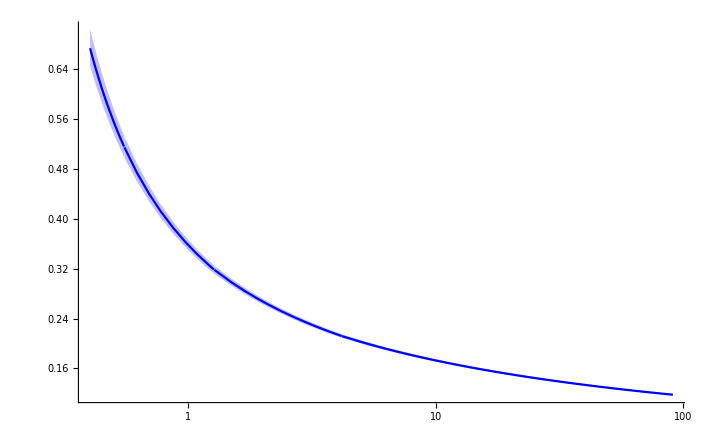

```mathematica
Show[LogLinearPlot[{αsLO[[1]][μ],αsLO[[2]][μ],αsLO[[3]][μ]},{μ,0.4,MZ},
Filling->{1->{{2},{Opacity[0.25,Blue]}},1->{{3},{Opacity[0.25,Blue]}}},PlotStyle->{Blue,Opacity[0,Blue],Opacity[0,Blue]},PlotRange->All]]
```

#### NLO

```mathematica
αsNLO={αsEvolve[0.1179,1],αsEvolve[0.1179+0.0009,1],αsEvolve[0.1179-0.0009,1]};
```

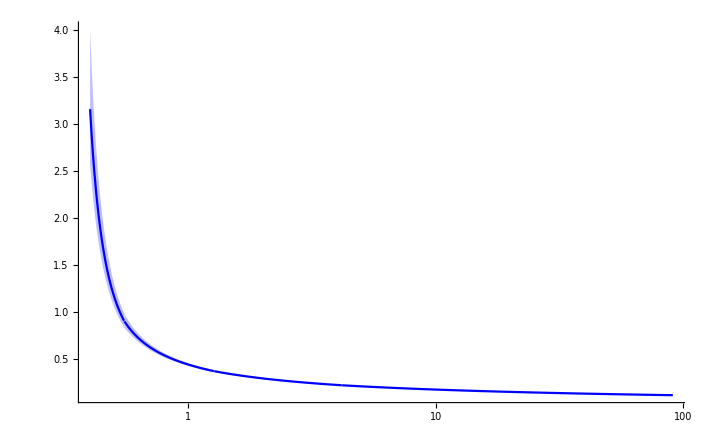

```mathematica
Show[LogLinearPlot[{αsNLO[[1]][μ],αsNLO[[2]][μ],αsNLO[[3]][μ]},{μ,0.4,MZ},
Filling->{1->{{2},{Opacity[0.25,Blue]}},1->{{3},{Opacity[0.25,Blue]}}},PlotStyle->{Blue,Opacity[0,Blue],Opacity[0,Blue]},PlotRange->All]]
```

#### NNLO

```mathematica
αsNNLO={αsEvolve[0.1179,2],αsEvolve[0.1179+0.0009,2],αsEvolve[0.1179-0.0009,2]};
```

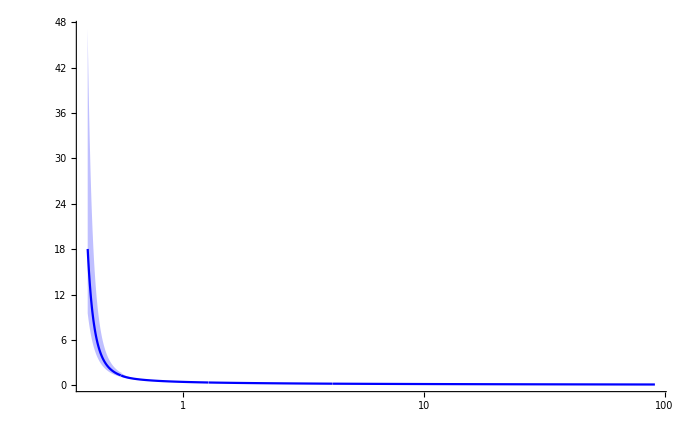

```mathematica
Show[LogLinearPlot[{αsNNLO[[1]][μ],αsNNLO[[2]][μ],αsNNLO[[3]][μ]},{μ,0.4,MZ},
Filling->{1->{{2},{Opacity[0.25,Blue]}},1->{{3},{Opacity[0.25,Blue]}}},PlotStyle->{Blue,Opacity[0,Blue],Opacity[0,Blue]},PlotRange->All]]
```

#### NNNLO

```mathematica
αsNNNLO={αsEvolve[0.1179,3],αsEvolve[0.1179+0.0009,3],αsEvolve[0.1179-0.0009,3]};
```

NDSolve::ndsz: At μ$3323 == 0.584677, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {0.55} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

NDSolve::ndsz: At μ$3373 == 0.6083, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {0.55} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

NDSolve::ndsz: At μ$3421 == 0.561566, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.55} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

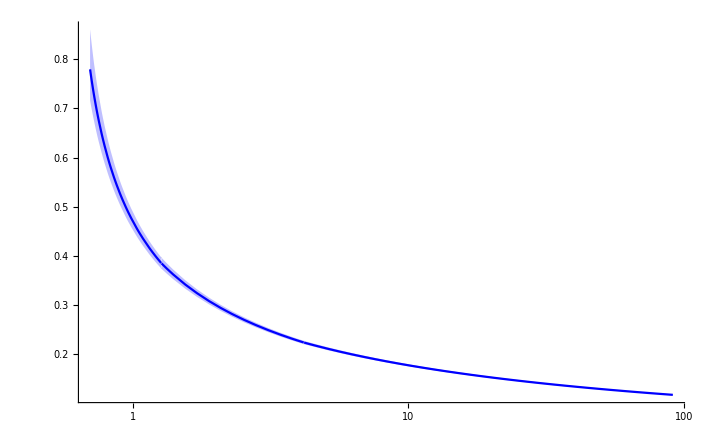

```mathematica
Show[LogLinearPlot[{αsNNNLO[[1]][μ],αsNNNLO[[2]][μ],αsNNNLO[[3]][μ]},{μ,0.7,MZ},
Filling->{1->{{2},{Opacity[0.25,Blue]}},1->{{3},{Opacity[0.25,Blue]}}},PlotStyle->{Blue,Opacity[0,Blue],Opacity[0,Blue]},PlotRange->All]]
```

#### Comparison

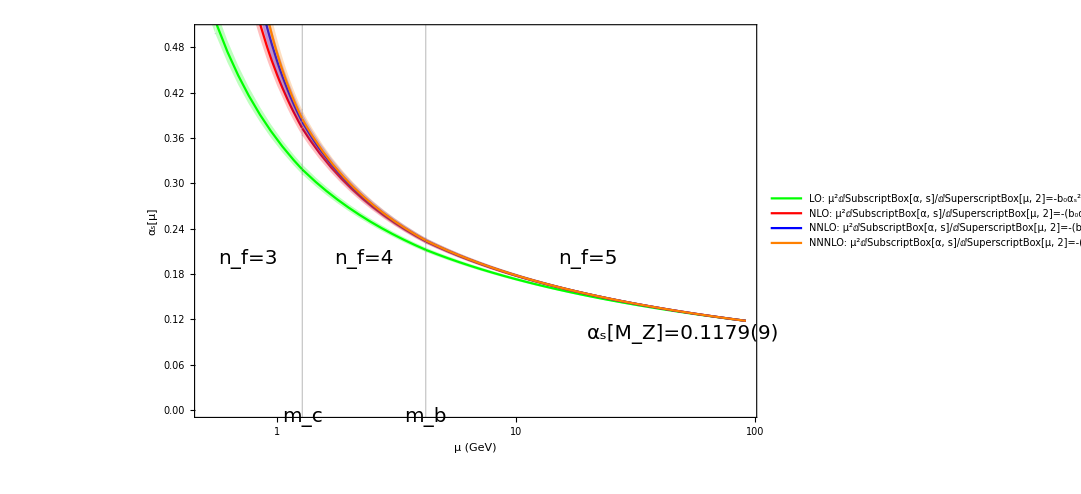

```mathematica
Fig1=Show[
LogLinearPlot[{αsLO[[1]][μ],αsLO[[2]][μ],αsLO[[3]][μ]},{μ,0.5,MZ},
Filling->{1->{{2},{Opacity[0.25,Green]}},1->{{3},{Opacity[0.25,Green]}}},PlotStyle->{Green,Opacity[0,White],Opacity[0,White]},PlotRange->All,
PlotLegends->Placed[{"LO: μ^2ⅆSubscriptBox[α, s]/ⅆSuperscriptBox[μ, 2]=-b_0α_s^2"},{0.7,0.8}],LabelStyle->{FontSize->15},GridLines->{{{mc,Black},{mb,Black}},None}],

LogLinearPlot[{αsNLO[[1]][μ],αsNLO[[2]][μ],αsNLO[[3]][μ]},{μ,0.6,MZ},
Filling->{1->{{2},{Opacity[0.25,Red]}},1->{{3},{Opacity[0.25,Red]}}},PlotStyle->{Red,Opacity[0,White],Opacity[0,White]},PlotRange->All,
PlotLegends->Placed[{"NLO: μ^2ⅆSubscriptBox[α, s]/ⅆSuperscriptBox[μ, 2]=-(b_0α_s^2+b_1α_s^3)"},{0.7,0.7}],LabelStyle->{FontSize->15}],

LogLinearPlot[{αsNNLO[[1]][μ],αsNNLO[[2]][μ],αsNNLO[[3]][μ]},{μ,0.6,MZ},
Filling->{1->{{2},{Opacity[0.25,Blue]}},1->{{3},{Opacity[0.25,Blue]}}},PlotStyle->{Blue,Opacity[0,White],Opacity[0,White]},PlotRange->All,
PlotLegends->Placed[{"NNLO: μ^2ⅆSubscriptBox[α, s]/ⅆSuperscriptBox[μ, 2]=-(b_0α_s^2+b_1α_s^3+b_2α_s^4)"},{0.7,0.6}],LabelStyle->{FontSize->15}],

LogLinearPlot[{αsNNNLO[[1]][μ],αsNNNLO[[2]][μ],αsNNNLO[[3]][μ]},{μ,0.7,MZ},
Filling->{1->{{2},{Opacity[0.25,Orange]}},1->{{3},{Opacity[0.25,Orange]}}},PlotStyle->{Orange,Opacity[0,White],Opacity[0,White]},PlotRange->All,
PlotLegends->Placed[{"NNNLO: μ^2ⅆSubscriptBox[α, s]/ⅆSuperscriptBox[μ, 2]=-(b_0α_s^2+b_1α_s^3+b_2α_s^4+b_3α_s^5)"},{0.7,0.5}],LabelStyle->{FontSize->15}],

PlotRange->{{Log[0.5],Log[MZ]},{0,0.5}},FrameLabel->{Style["μ (GeV)",20],Style["α_s[μ]",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},ImageSize->800,
Epilog->{
Text[Style["m_c",Black,20],{Log[mc],-0.01},Automatic,{1,0}],
Text[Style["m_b",Black,20],{Log[mb],-0.01},Automatic,{1,0}],
Text[Style["n_f=3",Black,20],{Log[0.75],0.2},Automatic,{1,0}],
Text[Style["n_f=4",Black,20],{Log[2.3],0.2},Automatic,{1,0}],
Text[Style["n_f=5",Black,20],{Log[20],0.2},Automatic,{1,0}],
Text[Style["α_s[M_Z]=0.1179(9)",Black,20],{Log[50],0.1},Automatic,{1,0}]
}
]
(*SetDirectory[NotebookDirectory[]];
Export["./Fig1.pdf",Fig1]*)
```

### Universal Parameters

```mathematica
GeVfm=0.1973269631; (*GeV fm*)(*For Unit Conversion*)
CF=4/3;CA=3;Tf=1/2;
```

### Asymptotic series

```mathematica
ClearAll[rnasym,dPVasym];
(*Follow the convention of arXiv:hep-ph/0105008*)
rnasym[n_,z_,μ_,nf_]:=Module[{CA,CF,TR,β0,β1,β2,β3,b,c1,c2,Nm},
CA=3;
CF=4/3;
TR=1/2;
β0=(11*CA-4*nf*TR)/(12Pi)4Pi;
β1=(17 CA^2-nf*TR*(10CA+6CF))/(24 Pi^2)(4Pi)^2;
β2=(2857-5033/9 nf+325/27 nf^2)/(128 Pi^3)(4Pi)^3;
β3=1/(4Pi)^4(29243-6946.3nf+405.089*nf^2+1.49931*nf^3)(4Pi)^4;
b=β1/(2 β0^2);
c1=1/(4b β0^3)(β1^2/β0-β2);
c2=(β1^4+4 β0^3 β1 β2-2 β0 β1^2 β2+β0^2 (-2 β1^3+β2^2)-2 β0^4 β3)/(32 (-1+b) b β0^8);
Nm=Piecewise[{{0.5749687262865643,nf==3},{0.5522713118193284,nf==4},{0.5235323457364502,nf==5}}];
Nm*Abs[z μ](β0/(2Pi))^n Gamma[n+1+b]/Gamma[1+b](1+b/(n+b)c1+(b(b-1))/((n+b)(n+b-1))c2)]

(*∫ⅆu 1/(1-2u)^(1+b)Exp[-u/αs(4Pi)/β0]=∫ⅆ(1/(1-2u)^b)*1/(2b)Exp[-u/αs(4Pi)/β0]=∫ⅆ(1/(1-2u)^b 1/(2b)Exp[-u/αs(4Pi)/β0])+∫ⅆu 1/(1-2u)^b 1/(2b)(1/αs(4Pi)/β0)Exp[-u/αs(4Pi)/β0]=-1/(2b)+∫ⅆu 1/(1-2u)^b 1/(2b)(1/αs(4Pi)/β0)Exp[-u/αs(4Pi)/β0]=∫ⅆu(1/(1-2u)^b-1)1/(2b)(1/αs(4Pi)/β0)Exp[-u/αs(4Pi)/β0]*)
dPVasym[z_,μ_,nf_,αs_]:=Module[{CA,CF,TR,β0,β1,β2,β3,b,c1,c2,Nm},
CA=3;
CF=4/3;
TR=1/2;
β0=(11*CA-4*nf*TR)/(12Pi)4Pi;
β1=(17 CA^2-nf*TR*(10CA+6CF))/(24 Pi^2)(4Pi)^2;
β2=(2857-5033/9 nf+325/27 nf^2)/(128 Pi^3)(4Pi)^3;
β3=1/(4Pi)^4(29243-6946.3nf+405.089*nf^2+1.49931*nf^3)(4Pi)^4;
b=β1/(2 β0^2);
c1=1/(4b β0^3)(β1^2/β0-β2);
c2=(β1^4+4 β0^3 β1 β2-2 β0 β1^2 β2+β0^2 (-2 β1^3+β2^2)-2 β0^4 β3)/(32 (-1+b) b β0^8);
Nm=Piecewise[{{0.5749687262865643,nf==3},{0.5522713118193284,nf==4},{0.5235323457364502,nf==5}}];(*Nm*Abs[z μ](NIntegrate[Re[(4Pi)/β0(1/(1-2(u+I*δu))^b-1)1/(2b)(1/αs(4Pi)/β0)Exp[-(u+I*δu)/αs(4Pi)/β0]],{u,0,0.5,20},Method->{"PrincipalValue","SingularPointIntegrationRadius"->1/16}]+NIntegrate[Re[(4Pi)/β0 1/(1-2(u+I*δu))^(1+b)(c1(1-2(u+I*δu))+c2(1-2(u+I*δu))^2)Exp[-(u+I*δu)/αs(4Pi)/β0]],{u,0,0.5,20},Method->{"PrincipalValue","SingularPointIntegrationRadius"->1/16}])*)
Nm*Abs[z μ] ⅇ^(-(2 π)/(αs β0)) (-2π)/β0 Re[ExpIntegralE[1+b,-(2 π)/(αs β0)]+c1  ExpIntegralE[b,-(2 π)/(αs β0)]+c2  ExpIntegralE[-1+b,-(2 π)/(αs β0)]]
]
```

```mathematica
dPVasym[0.1/GeVfm,100,3,αsNNNLO[[1]][100]]
```

4.93714

```mathematica
dPVasym[0.1/GeVfm,50,3,αsNNNLO[[1]][50]]
```

2.85773

### The full hybrid matching kernel

#### The matching matrix generator

```mathematica
(*Generate the fixed order matching kernel*)
SubMGen[δC_,xlist_,Pz_,zs_]:=Module[{δCtmp,Δx,δCmf},
δCtmp[y_,x_]:=δC[y/x,x,Pz,zs];
Δx=Abs[xlist[[2]]-xlist[[1]]];
(*Subscript[y, i],Subscript[x, j]*)
δCmf[i_,j_]:=If[i≠j,δCtmp[xlist[[i]],xlist[[j]]]/Abs[xlist[[j]]] Δx,-Sum[δCtmp[xlist[[k]],xlist[[i]]]/Abs[xlist[[i]]] Δx,{k,1,j-1}]-Sum[δCtmp[xlist[[k]],xlist[[i]]]/Abs[xlist[[i]]] Δx,{k,j+1,Length[xlist]}]];
ParallelTable[δCmf[i,j],{i,1,Length[xlist]},{j,1,Length[xlist]}]
]
```

#### The NLO matching kernel

```mathematica
(*
The matching kernel to calculate quasi-PDF from the light-cone PDF
f̃[y,Pz]=∫ⅆx/(|x|)C[y/x,μ/(x Pz)]f[x,μ]
*)
```

```mathematica
Cratio1pluswμ[ξ_,x_,Pz_,zs_]:=If[ξ>1,0,If[ξ<1&&ξ>0,((1+ξ^2)/(1-ξ)),0]];
Cratio1pluswoμ[ξ_,x_,Pz_,zs_]:=If[ξ>1,((1+ξ^2)/(1-ξ)Log[ξ/(ξ-1)]+1-3/(2(1-ξ))),If[ξ<1&&ξ>0,((1+ξ^2)/(1-ξ)(-Log[(1/x)^2]+Log[4 ξ(1-ξ)]-1)+1+3/(2(1-ξ))),(-(1+ξ^2)/(1-ξ)Log[ξ/(ξ-1)]-1+3/(2(1-ξ)))]];
Chybrid1plus[ξ_,x_,Pz_,zs_]:=(3/2)(-1/Abs[1-ξ]+(2SinIntegral[(1-ξ)*Abs[x*zs*Pz]])/(Pi*(1-ξ)));
```

```mathematica
ChNLOc[y_,x_,μ_,Pz_,zs_]:=Module[{ξ,nf,fr},
ξ=y/x;(*Momentum fraction*)
nf=3;
(αsNLO[[1]][μ]*CF)/(2Pi)((-Log[(μ/Pz)^2])Cratio1pluswμ[y/x,x,Pz,zs]+Cratio1pluswoμ[y/x,x,Pz,zs]+Chybrid1plus[y/x,x,Pz,zs])
]
```

#### The NNLO matching kernel

```mathematica
(*Decompose CMS2 into different logs*)
nf=3;

Gamma2[y_]:=If[y>0&&y<1,CF^2/2((2 (-1+y)^2-4 (1+y^2) Log[1-y]+(1+3 y^2) Log[y])/(y-1))+(CF*(11CA-2nf)/6*(1+y^2))/(2 (y-1)),0];

Gamma1a1[y_]:=CF^2(-((3+y^2)(PolyLog[2,1/y]- π^2/6+((Log[y^2]/2)^2)/2-1/4 Log[(-1+y)^2] Log[y^2]))/(y-1)+(π^2(3+y^2)-18 (y-1))/(6-6 y)-(2 (1+y^2)( Log[(y-1)^2]/2)^2)/(y-1)-((1+3 y^2)( Log[y^2]/2)^2)/(2 (y-1))+Log[(y-1)^2]/2 (2 (y-1)+((1+3 y^2) Log[y^2]/2)/(y-1))-2 (y-1) Log[y^2]/2)+(CF (11CA-2nf)/6(y-1+(1+y^2) Log[((y-1)/y)^2]/2))/(y-1);

Gamma1[y_]:=If[y>1,Gamma1a1[y],
If[y>0&&y<1,CF^2(((3 y^2+1) PolyLog[2,y])/(y-1)+(4 (1+y^2) (Log[(1-y)^2]/2)^2)/(y-1)-((7+17 y^2) (Log[y^2]/2)^2)/(4 (y-1))+((-9+10 y+4 y^2)Log[y^2]/2)/(2 (y-1))+(2 Log[2] (-2 (-1+y)^2+4 (1+y^2) Log[(1-y)^2]/2-(1+3 y^2) Log[y^2]/2))/(y-1)+(3 (1+y))/2+(Log[(1-y)^2]/2 (-6+4 y-6 y^2+3 (1+y^2) Log[y^2]/2))/(y-1))+CA*CF (-(11 (1+y^2) Log[(1-y)^2]/2)/(6 (y-1))-(11(y^2+1)Log[2])/(3(y-1))+(253 y^2-3 Pi^2(y^2+1)-174y+187)/(36(y-1))+((y^2+1) (Log[y^2]/2)^2)/(4 (y-1))-((5+17 y^2) Log[y^2]/2)/(12 (y-1)))+2 CF*Tf*nf* (-(11-6 y+17 y^2)/(18 (y-1))+((1+y^2) Log[(1-y)^2]/2)/(3 (y-1))+((1+y^2) Log[y^2]/2)/(6 (-1+y))+(2 (1+y^2) Log[2])/(3 (-1+y))),
If[y>-1&&y<0,CF^2 ((1+y) PolyLog[2,y]+(2 (1+y^2) (Log[(1-y)^2]/2)^2)/(y-1)+(y^2(Log[y^2]/2)^2)/(y-1)-(2 Log[(1-y)^2]/2 ((-1+y)^2+(1+y^2) Log[y^2]/2))/(y-1)+2y+π^2/(3-3 y)+(y-1) Log[y^2]/2-1)+CA CF (-((1+y^2) PolyLog[2,y])/(y-1)-(-34+π^2+22 y+(12+π^2) y^2)/(12 (y-1))+((1+y^2) (Log[y^2]/2)^2)/(4 (y-1))+((7-3 y+7 y^2) Log[y^2]/2)/(3 (y-1))-((1+y^2) Log[(1-y)^2]/2 (11+6 Log[y^2]/2))/(6 (y-1)))+2 CF nf Tf ((1+y^2) Log[(1-y)^2]/2-(1+y^2) Log[y^2]/2+y-1)/(3 (y-1)),
-Gamma1a1[y]
]]];

Gamma1IR[y_,r_]:=Gamma1[y]-((11CA-2nf)/6+3/2 CF)*If[y>1,CF*((1+y^2)/(1-y)Log[y/(y-1)]+1),If[y>0&&y<1,CF*((1+y^2)/(1-y)(-Log[r^2/4]+Log[y(1-y)])-(y(1+y))/(1-y)),CF*(-(1+y^2)/(1-y)Log[y/(y-1)]-1)]];

Gamma2IR[y_,r_]:=Gamma2[y]-If[y>0&&y<1,((11CA-2nf)/6+3/2 CF)*(1+y^2)/(y-1)CF,0];

C1CF[y_]:=(4 (2 y^2+1) PolyLog[3,1/(1-y)])/(y-1)+((3 y^2+1) PolyLog[3,1/y])/(y-1)-(2 (y^2+1) (PolyLog[3,1-y^2]+PolyLog[3,-1/y]-2 PolyLog[3,1/(y+1)]))/(y-1)+(PolyLog[2,1/y] (y^2 (1+2 Log[2])-2 (y^2-1) Log[(y-1)^2]/2+4 (y^2+1) Log[(y+1)^2]/2-8+6 Log[2]))/(y-1)+2 (y-1) PolyLog[2,-1/y]+(2 (2 y^2+1) (Log[y^2]/2)^3)/(3 (y-1))-(2 (y^2+1) (Log[(y+1)^2]/2)^3)/(3 (y-1))+(2 Log[2] (2 (y^2+1) (Log[((y-1)/y)^2]/2)^2+3 (1-y)+(y-1)^2 Log[(y/(y-1))^2]))/(y-1)-((π^2(y^2+1)+3 Log[y^2] (y^2 Log[y^2]/2+2 (y^2+1) (Log[(y+1)^2]/2-1))+3 (y-1)^2) Log[(y-1)^2]/2)/(3 (y-1))+(3 y-2)/(y-1)+(2 π^2)/(3-3 y)-(((12+π^2) y^2+π^2-12) Log[(y+1)^2]/2)/(3 (y-1))-(2 (2 ((y-1) y+1)+Log[y^2]/2)( Log[(y-1)^2]/2)^2)/(y-1)+(2 (Log[y^2]/2)^2 ((y^2+1) Log[(y+1)^2]/2-2 y))/(y-1)+(2 (y^2+2) (Log[(y-1)^2]/2)^3)/(3 (y-1))+(5 y-3) Log[y^2]/2;

C2CF[y_]:=-(2 (y^2+1) (PolyLog[3,1-y^2]+7 PolyLog[3,-y]+2 PolyLog[3,y/(y+1)]+3 Zeta[3]))/(y-1)-((y^2+3) PolyLog[3,y])/(y-1)-((y^2+5) PolyLog[3,y/(y-1)])/(y-1)- (PolyLog[2,y](-11 y^2+(3 y^2-1) Log[1-y]-(y^2+1) Log[y/(64 (y+1)^4)]+10 y+2-4 Log[2]))/(y-1)+PolyLog[2,-y]((4 (y^2+1) Log[y])/(y-1)+2 y+6)-((-30 y^2+π^2(y^2+3)+51 y-3) Log[y])/(6 (y-1))+(π^2(y(-3 y^2+y+2)-1))/(3 (y-1))-((11 y^2+7) Log[1-y]^3)/(6 (y-1))+(7 (5 y^2+3) Log[y]^3)/(12 (y-1))-((3 (y^2+1) Log[y]+y((y-7) y+5)-7) Log[1-y]^2)/(y-1) +((-7 y^2+3 (y^2+1) Log[y]^2+2 Log[y] (-4 (y^2+1) Log[y+1]+y(y(2 y+5)-4)+1)+y-2) Log[1-y])/(2 (y-1)) -(2 (y^2+1) Log[y] Log[y+1]^2)/(y-1)+(2 Log[2]^2(-4 (y^2+1) Log[1-y]+3 y^2 Log[y]+2 (y-1)^2+Log[y]))/(y-1)+(2 (y^2+1) Log[y+1]^3)/(3 (y-1))+(2 Log[2] ((7 y^2+2) Log[y]^2-2 (y^2+1) Log[1-y] (2 Log[1-y]+Log[y])))/(y-1)+(3 y^2-16 y+11)/(2-2 y)+(2 Log[2] (y^2+9 y^2 Log[1-y]+(-3 y^2-4 y+6) Log[-(y-1) y]-5 y+4))/(y-1)+(((π^2-12) y^2+12 (y^2-1) Log[y]+π^2+12) Log[y+1])/(3 (y-1))-((2 y(2 y(y+8+6 Log[2])+1)-25) Log[y]^2)/(4 (y-1));

C3CF[y_]:=-((5 y^2+7) PolyLog[3,y])/(y-1)-(2 (y^2+1) (PolyLog[3,-y]+2 PolyLog[3,(2 y)/(y-1)]-2 PolyLog[3,y/(y+1)]+2 PolyLog[3,(2 y)/(y+1)]+2 PolyLog[3,(y+1)/(y-1)]))/(y-1)+(4 y^2 PolyLog[3,y/(y-1)])/(y-1)-(PolyLog[2,y] (2 (y^2-1) Log[1-y]-2 (y^2+1) Log[-y/(8 (y+1)^2)]+(4-11 y) y+6-4 Log[2]))/(y-1)+(2 PolyLog[2,-y] ((y^2+1) Log[-y]+2 (y-1)))/(y-1)+(-11 y^2+6 y+7)/(2-2 y)+(π^2(4 y^2-2 y-1))/(6 (y-1))-(2 (2 y^2+1) Log[1-y]^3)/(3 (y-1))+(2 (-(y^2+1) Log[y+1]+2 (y-1) y+2) Log[1-y]^2)/(y-1)-(2 (y^2+1) Log[2] (2 Log[1-y]^2+Log[(y+1)/(1-y)]^2))/(y-1)-(4 y^2 Zeta[3])/(y-1)-((y^2-2) Log[-y]^3)/(3 (y-1))+((π^2 (y^2+1)+3 (y-1)^2+6 (3 y+1) (y-1) Log[-y]) Log[1-y])/(3 (y-1))-((3 (7+π^2) y^2-42 y+π^2+9) Log[-y])/(6 (y-1))-(((12+Pi^2)y^2-6(y^2-1)Log[-y]+Pi^2-12)Log[y+1])/(3(y-1))+(((4-5 y) y-2) Log[-y]^2)/(2 (y-1))-1/3 Log[2] (π^2 y+24 y+3 (y+1) Log[-y]^2-12 (y-1) Log[1-y]+π^2+6);

C1CA[y_]:=((y^2+1) (PolyLog[3,1-y^2]-2 PolyLog[3,1/(1-y)]+PolyLog[3,-1/y]+PolyLog[3,1/y]-2 PolyLog[3,1/(y+1)]))/(y-1)+(((87-128 y) y-59) Log[y^2]/2)/(9 (y-1))+(PolyLog[2,1/y] (5 y^2+12 (y^2+1) Log[(y/(y+1))^2]/2+17))/(6 (y-1))-(y-1) PolyLog[2,-1/y]+((y^2+1) (Log[(y-1)^2]/2)^3)/(3 (y-1))+(2 (y^2+1) (Log[y^2]/2)^3)/(3 (y-1))+((y^2+1) (Log[(y+1)^2]/2)^3)/(3 (y-1))-(11 (y^2+1) (Log[(y-1)^2]/2)^2)/(6 (y-1))+((10 (y(11 y-12)+11)-9 (y^2+1) (Log[y^2]/2)^2) Log[(y-1)^2]/2)/(9 (y-1))-(11 Log[2] ((y^2+1) Log[((y-1)/y)^2]/2+y-1))/(3 (y-1))+((2 (y^2-1)+(y^2+1) Log[(y-1)^4/y^2]/2 Log[y^2]/2) Log[(y+1)^2]/2)/(y-1) +(11 (y^2+1) (Log[y^2]/2)^2)/(6 (y-1))+(π^2((y^2+1) Log[(y^2-1)^2]/2+1))/(6 (y-1))+4/(3-3 y)+151/18;

C2CA[y_]:=((y^2+1) (PolyLog[3,1-y^2]+7 PolyLog[3,-y]+2 PolyLog[3,y]-3 PolyLog[3,y/(y-1)]+2 PolyLog[3,y/(y+1)]))/(y-1)+(1261 y^2-1119 y+880)/(54 (y-1))+PolyLog[2,-y] (-(2 (y^2+1) Log[y])/(y-1)-y-3)+(PolyLog[2,y] (-y^2+6 (y^2+1) Log[((1-y) (y+1)^2)/y^3]+26))/(6 (y-1))-(5 (y^2+1) Zeta[3])/(2 (y-1))+((y^2+1) Log[1-y]^3)/(2 (y-1))-((y^2+1) (7 Log[y]^3+4 Log[y+1]^3))/(12 (y-1))-((-19 y^2+6 (y^2+1) Log[y]-6 y-19) Log[1-y]^2)/(12 (y-1))-((193 y^2+18 (y^2+1) Log[y]^2+9 (y^2+2 y-3) Log[y]-204 y+211) Log[1-y])/(18 (y-1))+((67 y^2-24 y-35) Log[y]^2)/(24 (y-1))+(Log[2] (3 π^2 y^2-220 y^2-9 (y^2+1) Log[y]^2+33 (y^2+1) Log[1-y]+18 (y^2-1) Log[y]+207 y+3 π^2-187))/(9 (y-1))+(11 (y^2+1) Log[2]^2)/(3 (y-1))-((161 y^2-183 y+89) Log[y])/(18 (y-1))+(π^2 (-y^2+6 (y^2+1) Log[((1-y)^3 y)/(y+1)]+12 y+2))/(36 (y-1))+((y^2+1) Log[y] Log[y+1]^2)/(y-1)+(2 (y^2+(-y^2+(y^2+1) Log[1-y]+1) Log[y]-1) Log[y+1])/(y-1);

C3CA[y_]:=1/(y-1)(y^2+1) (PolyLog[3,-y]+2 PolyLog[3,y]+2 PolyLog[3,(2 y)/(y-1)]-2 PolyLog[3,y/(y+1)]+2 PolyLog[3,(2 y)/(y+1)]+2 PolyLog[3,(y+1)/(y-1)]) -(PolyLog[2,-y] ((y^2+1) Log[-y]+2 (y-1)))/(y-1)+(PolyLog[2,y] (-25 y^2+6 (y^2+1) Log[-16 y(y+1)^2]+12 y+11))/(6 (y-1))+(-99 y^2-302 y+449)/(36 (y-1))-(2 (y^2+1) Log[1-y]^3)/(3 (y-1))-(7 (y^2+1) Log[-y]^3)/(12 (y-1))+((y^2+1) (6 Log[-y]+11) Log[1-y]^2)/(6 (y-1))+((-20 (11 y^2-12 y+11)+27 (y^2+1) Log[-y]^2-18 (5 y^2-2 y+1) Log[-y]) Log[1-y])/(18 (y-1))+((y^2+12 y-23) Log[-y]^2)/(12 (y-1))+((y^2+1) Log[2] (Log[(1-y)/(y+1)]^2+Log[-(y-1)^4/y] Log[-y]))/(y-1)+(((y^2+1) Log[1-y]^2-(y^2-1) (Log[-y]-2)) Log[y+1])/(y-1)+((485 y^2-330 y+209) Log[-y])/(36 (y-1))+(Log[2] (π^2 y^2+12 y^2+11 (y^2+1) Log[1-y]+(-17 y^2+12 y-17) Log[-y]+11 y+π^2-23))/(3 (y-1))+(π^2(-2 y^2+3 (y^2+1) Log[-y(y+1)]+3 y+1))/(18 (y-1));

C1TF[y_]:=-((y^2+1) PolyLog[2,1/y])/(3 (y-1))+((y^2+1) (Log[(y-1)^2]/2)^2)/(3 (y-1))-((y^2+1) (Log[y^2]/2)^2)/(3 (y-1))-(2 (7 y^2-6 y+7) Log[(y-1)^2]/2)/(9 (y-1))+(2 Log[2] ((y^2+1) Log[((y-1)/y)^2]/2+y-1))/(3 (y-1))+((7 y^2-3 y+4) Log[y^2])/(9 (y-1))+(14-11 y)/(9 (y-1));

C2TF[y_]:=-((y^2+1) PolyLog[2,y])/(3 (y-1))-(π^2(y^2+1))/(18 (y-1))-(151 y^2-84 y+103)/(54 (y-1))-((y^2+1) Log[1-y]^2)/(3 (y-1))+((y^2+1) Log[y]^2)/(12 (y-1))-(2 (y^2+1) Log[2]^2)/(3 (y-1))+(2 (7 y^2-6 y+7) Log[1-y])/(9 (y-1))-(2 Log[2] (-14 y^2+3 (y^2+1) Log[1-y]+9 y-11))/(9 (y-1))+((11 y^2-12 y+11) Log[y])/(18 (y-1));

C3TF[y_]:=-((y^2+1) PolyLog[2,y])/(3 (y-1))-(π^2*(y^2+1))/(18 (y-1))-((y^2+1) Log[1-y]^2)/(3 (y-1))+((y^2+1) Log[-y]^2)/(6 (y-1))+(2 (7 y^2-6 y+7) Log[1-y])/(9 (y-1))-(2 (7 y^2-3 y+4) Log[-y])/(9 (y-1))-(2 Log[2] ((y^2+1) Log[1-y]-(y^2+1) Log[-y]+y-1))/(3 (y-1))+(14-11 y)/(9-9 y);

Pqq[y_]:=1/2 CF^2 (-1/2 (1+y) Log[y]^2+(((7 y^2)/2-2 y-3/2) Log[y])/(1-y)-5 (1-y)-((2 Log[1-y]+3/2) (1+y^2) Log[y])/(1-y))+1/2 CA CF ((67/9-π^2/3)/(1-y)+((1+y^2) Log[y]^2)/(2 (1-y))+((5 y^2+17) Log[y])/(6 (1-y))+1/18 (53-187 y)+1/6 (1+y) π^2)-1/2*CF*Tf*nf (20/(9 (1-y))+(2 (1+y^2) Log[y])/(3 (1-y))+(4 (1-y))/3-(10 (y+1))/9);

Pqqbar[y_]:=1/2 CF (CA/2-CF) (((1+y^2) (Log[y]^2-4 PolyLog[2,-y]-4 Log[y+1] Log[y]-π^2/3))/(1+y)+4 (1-y)+2 (y+1) Log[y]);

CMS2wLL[ξ_,x_,Pz_,zs_]:=Gamma2[ξ];
CMS2wNLL[ξ_,x_,Pz_,zs_]:=If[ξ>1,0,
If[ξ>0&&ξ<1,-Pqq[ξ],
If[ξ>-1&&ξ<0,-Pqqbar[-ξ],
If[ξ<-1,0,0]
]]]+Gamma1[ξ]+Gamma2[ξ]2Log[1/x^2];
CMS2woL[ξ_,x_,Pz_,zs_]:=If[ξ>1,(CF*C1CF[ξ]+CA*C1CA[ξ]+2*Tf*nf*C1TF[ξ])*CF,
If[ξ>0&&ξ<1,(CF*C2CF[ξ]+CA*C2CA[ξ]+2*Tf*nf*C2TF[ξ])*CF-Pqq[ξ]Log[1/x^2],
If[ξ>-1&&ξ<0,(CF*C3CF[ξ]+CA*C3CA[ξ]+2*Tf*nf*C3TF[ξ])*CF-Pqqbar[-ξ]Log[1/x^2],
If[ξ<-1,-(CF*C1CF[ξ]+CA*C1CA[ξ]+2*Tf*nf*C1TF[ξ])*CF,0]
]]]+Gamma1[ξ]Log[1/x^2]+Gamma2[ξ] Log[1/x^2]^2;

(*Decompose the hybrid counterterms into different logs*)
Chybrid2pluswLL[ξ_,x_,Pz_,zs_]:=CF^2 3/2 Cratio1pluswμ[ξ,x,Pz,zs];
Chybrid2pluswNLLPz[ξ_,x_,Pz_,zs_]:=2((11 CA CF)/16+(9 CF^2)/16-(CF nf Tf)/4)2/Abs[ξ-1]+CF^2 Cratio1pluswμ[ξ,x,Pz,zs] 5/2;
Chybrid2pluswNLLzs[ξ_,x_,Pz_,zs_]:=2((11 CA CF)/16+(9 CF^2)/16-(CF nf Tf)/4)2(-1/Abs[1-ξ]+(2*SinIntegral[(1-ξ)*Abs[Abs[x]Pz zs]])/(Pi*(1-ξ)))-CF^2 3/2*3/2(-1/Abs[1-ξ]+(2*SinIntegral[(1-ξ)*Abs[Abs[x]Pz zs]])/(Pi*(1-ξ)))-CF^2 Cratio1pluswoμ[ξ,x,Pz,zs] 3/2;
Chybrid2pluswoL[ξ_,x_,Pz_,zs_]:=-2((CA CF (53/16-π^2/12)+CF^2 (25/16+π^2/3)-(5 CF nf Tf)/4)(-1/Abs[1-ξ])+((11 CA CF)/16+(9 CF^2)/16-(CF nf Tf)/4)(2 (Log[4]+2 Log[Abs[ξ-1]]-Log[1/x^2]))/Abs[ξ-1])+2(CA CF (53/16-π^2/12)+CF^2 (25/16+π^2/3)-(5 CF nf Tf)/4)(-1/Abs[1-ξ]+(2*SinIntegral[(1-ξ)*Abs[Abs[x]Pz zs]])/(Pi*(1-ξ)))+2((11 CA CF)/16+(9 CF^2)/16-(CF nf Tf)/4)*(4/Abs[1-ξ]*(Log[ Abs[Abs[x]Pz zs]]+EulerGamma+Log[Abs[1-ξ]])-(4 Abs[Abs[x]Pz zs])/Pi (HypergeometricPFQ[{1,1,1},{2,2,2},I(ξ-1) Abs[Abs[x]Pz zs]]+HypergeometricPFQ[{1,1,1},{2,2,2},-I(ξ-1)Abs[Abs[x]Pz zs]]))-CF^2 5/2*3/2(-1/Abs[1-ξ]+(2*SinIntegral[(1-ξ)*Abs[Abs[x]Pz zs]])/(Pi*(1-ξ)))-CF^2 Cratio1pluswoμ[ξ,x,Pz,zs] 5/2;
```

```mathematica
ChNNLOc[y_,x_,μ_,Pz_,zs_]:=((αsNNLO[[1]][μ])/(2Pi))^2 Re[CMS2wLL[y/x,x,Pz,zs] Log[μ^2/Pz^2]^2+CMS2wNLL[y/x,x,Pz,zs]Log[μ^2/Pz^2]+CMS2woL[y/x,x,Pz,zs]+Chybrid2pluswLL[y/x,x,Pz,zs]Log[μ^2/Pz^2]Log[(zs^2 μ^2 Exp[2EulerGamma])/4]+Chybrid2pluswNLLPz[y/x,x,Pz,zs]Log[μ^2/Pz^2]+Chybrid2pluswNLLzs[y/x,x,Pz,zs]Log[(zs^2 μ^2 Exp[2EulerGamma])/4]+Chybrid2pluswoL[y/x,x,Pz,zs]];
```

#### Renormalon part

```mathematica
(*
The basic ingredient that can be used to construct all the renormalon matching kernels
∫ⅆλ/(2 π)ⅇ^(I λ (ξ-1))(|z|ⅇ^(-|z|M)-zs ⅇ^(-zs M))θ[|z|-zs]=2∫_(zs pz)^(+∞) (λ/pz Exp[-λ/pzM]-zsExp[-zs M])Cos[(1-ξ)*λ]/(2 Pi),
where λ=z*pz 
*)
Cz[ξ_,x_,Pz_,zs_]:=Module[{pz,M},
pz=Abs[x]Pz;
M=0.005;(*GeV*)
If[ξ≠1,-(ⅇ^(-M zs) zs Sin[pz zs-pz ξ zs])/(π (-1+ξ))+1/(π (M^2+pz^2 (-1+ξ)^2)^2)ⅇ^(-M zs) pz ((M^2-pz^2 (-1+ξ)^2+M^3 zs+M pz^2 (-1+ξ)^2 zs) Cos[pz (-1+ξ) zs]+pz (-1+ξ) (2 M+M^2 zs+pz^2 (-1+ξ)^2 zs) Sin[pz zs-pz ξ zs]),(ⅇ^(-M zs) pz (1+M zs+M^2 zs^2))/(M^2 π)]
]
(*
The exponentiated renormalon series can be constructed from the above one with MatrixExp
*)
```

```mathematica
(*
On the other hand, the exponentiated renormalon series can be obtained from the direct FT of the exponential decaying factor
∫_(-∞)^(+∞) ⅆν/(2π)Exp[I ν(ξ-1)](θ[zs|x Pz|-|ν|]+Exp[-(|ν|-zs|x Pz|)μ/(|x Pz|)∑_(n=n^*) Subscript[r, n] α^(n+1)]θ[|ν/(x Pz)|-zs])
*)
LRRcorr[ξ_,x_,Pz_,zs_,frsum_]:=Module[{Mr,Msub,ν0},
Mr=1/Abs[x Pz] frsum;
ν0=Abs[Pz x zs] ;
Sin[ν0 (1-ξ)]/(π (1-ξ))+(Mr Cos[ν0-ν0 ξ]+(-1+ξ) Sin[ν0-ν0 ξ])/(π (Mr^2+(-1+ξ)^2))
]
(*Generate the LRR correction*)
SubMGenLRR[xlist_,Pz_,zs_,frsum_]:=Module[{δCtmp,Δx,δCmf},
δCtmp[y_,x_]:=LRRcorr[y/x,x,Pz,zs,frsum];
Δx=Abs[xlist[[2]]-xlist[[1]]];
(*Subscript[y, i],Subscript[x, j]*)
δCmf[i_,j_]:=If[i≠j,δCtmp[xlist[[i]],xlist[[j]]]/Abs[xlist[[j]]] Δx,-Sum[δCtmp[xlist[[k]],xlist[[i]]]/Abs[xlist[[i]]] Δx,{k,1,j-1}]-Sum[δCtmp[xlist[[k]],xlist[[i]]]/Abs[xlist[[i]]] Δx,{k,j+1,Length[xlist]}]];
IdentityMatrix[Length[xlist]]+ParallelTable[δCmf[i,j],{i,1,Length[xlist]},{j,1,Length[xlist]}]
]
```

(*Consistency check of the two methods*)
xlist=Join[Table[x,{x,-2,-0.02,0.02}],Table[x,{x,0.02,2,0.02}]];
Pz=2;
zs=0.12/0.197;
μ=1;
nf=3;

CzM=SubMGen[Cz,xlist,Pz,zs];
CzMExp=MatrixExp[-CzM*frsum];

frsum=dPVasym[1,μ,nf,αsNLO[[1]][μ]];
MCzsum=SubMGenLRR[xlist,Pz,zs,frsum];

fvls=Table[Exp[-2 x^2],{x,xlist}];
Show[
ListPlot[fvls],
ListPlot[MCzsum.fvls,Joined→True,PlotStyle→Red],
ListPlot[CzMExp.fvls,Joined→True,PlotStyle→Black]
]
ClearAll[xlist,Pz,zs,μ,nf,CzM,CzMExp,frsum,MCzsum]

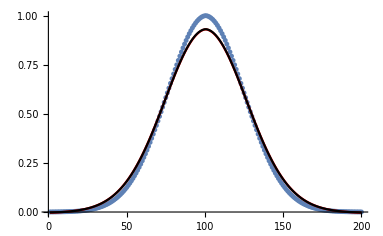

### The full DGLAP kernel, valence non-singlet

#### NLO

```mathematica
ClearAll[DGLAPNLOMGen,DGLAPNLOx];
```

```mathematica
DGLAPNLOMGen[xlistf_]:=Module[{pqq,zz,nf,H0,H2,H00,Hm10,H10,Pns0,Pns1,Δx,ymax,Mdglapns0,Mdglapns1},
(*arXiv:hep-ph/0403192*)
pqq[zz_]:=(1+zz^2)/(1-zz);
nf=3;
H0[z_]:=Log[z];
H2[z_]:=PolyLog[2,z];
H00[z_]:=1/(2!)Log[z]^2;
Hm10[z_]:=Log[z]Log[1+z]+PolyLog[2,-z];
H10[z_]:=-Log[z]Log[1-z]-PolyLog[2,z];
Pns0[z_]:=CF*2pqq[z];
Pns1[z_]:=4CA*CF*(pqq[z]*(67/18+11/6 H0[z]-Zeta[2]+H00[z])+pqq[-z](Zeta[2]+2*Hm10[z]-H00[z])+14/3(1-z))-4CF*nf*(pqq[z](H0[z]/3+5/9)+(2(1-z))/3)+4 CF^2(-2pqq[-z](2 *Hm10[z]-H00[z]+Zeta[2])+2*pqq[z]*(H10[z]-(3 H0[z])/4+H2[z])-(z+1)*H00[z]-(1-z)(1-3 H0[z]/2)-H0[z])+16CF(CF−CA/2)(pqq[−z](Zeta[2]+2Hm10[z]−H00[z])−2(1−z)−(1+z)H0[z]);
(*The full kernel is 2(αs/(4Pi))Pns0+2(αs/(4Pi))^2 Pns1*)
Δx=xlistf[[2]]-xlistf[[1]];
ymax=50;
Mdglapns0[i_,j_]:=If[i<j,Pns0[xlistf[[i]]/xlistf[[j]]] xlistf[[i]]/xlistf[[j]](Δx/Abs[xlistf[[i]]]),If[i>j,0,Sum[Pns0[xlistf[[i]]/xlistf[[k]]] xlistf[[i]]/xlistf[[k]](-Δx/Abs[xlistf[[k]]]),{k,i+1,Length[xlistf]}]+Sum[Pns0[xlistf[[i]]/y] xlistf[[i]]/y(-Δx/Abs[y]),{y,1+Δx,ymax,Δx}]]];
Mdglapns1[i_,j_]:=If[i<j,Pns1[xlistf[[i]]/xlistf[[j]]] xlistf[[i]]/xlistf[[j]](Δx/Abs[xlistf[[i]]]),If[i>j,0,Sum[Pns1[xlistf[[i]]/xlistf[[k]]] xlistf[[i]]/xlistf[[k]](-Δx/Abs[xlistf[[k]]]),{k,i+1,Length[xlistf]}]+Sum[Pns1[xlistf[[i]]/y] xlistf[[i]]/y(-Δx/Abs[y]),{y,1+Δx,ymax,Δx}]]];
{ParallelTable[Mdglapns0[i,j],{i,1,Length[xlistf]},{j,1,Length[xlistf]}],ParallelTable[Mdglapns1[i,j],{i,1,Length[xlistf]},{j,1,Length[xlistf]}]}
]
```

```mathematica
DGLAPNLOx[fint_,μi_,μf_,Mdglapns0_,Mdglapns1_,xlistp_]:=Module[{NE,ΔE,finttmp,flist,Δx,ymax,k,μtmp,Mdglap},
NE=Round[Abs[μf-μi]/0.02];
ΔE=(μf-μi)/NE;
finttmp=fint;
flist=Quiet[finttmp/@xlistp];
Δx=xlistp[[2]]-xlistp[[1]];
ymax=10;
For[k=0,k<NE,k++,
μtmp=μi+ΔE*k;
Mdglap=2((αsNLO[[1]][μtmp])/(4Pi))Mdglapns0+2((αsNLO[[1]][μtmp])/(4Pi))^2 Mdglapns1;
flist=flist+(Mdglap.flist)ΔE/μtmp;
];
ClearAll[finttmp];
finttmp=Interpolation[Re[Transpose[{xlistp,flist}]],InterpolationOrder->2];
finttmp
]
```

#### NNLO

```mathematica
ClearAll[DGLAPNNLOMGen,DGLAPNNLOx];
DGLAPNNLOMGen[xlistf_]:=Module[{pqq,zz,nf,H0,H2,H00,Hm10,H10,D0,L1,L0,Pns0,Pns1,Pns2,Δx,ymax,Mdglapns0,Mdglapns1,Mdglapns2},
(*arXiv:hep-ph/0403192*)
pqq[zz_]:=(1+zz^2)/(1-zz);
nf=3;
H0[z_]:=Log[z];
H2[z_]:=PolyLog[2,z];
H00[z_]:=1/(2!)Log[z]^2;
Hm10[z_]:=Log[z]Log[1+z]+PolyLog[2,-z];
H10[z_]:=-Log[z]Log[1-z]-PolyLog[2,z];
D0[z_]:=1/(1-z);
L1[z_]:=Log[1-z];
L0[z_]:=Log[z];

Pns0[z_]:=CF*2pqq[z];
Pns1[z_]:=4CA*CF*(pqq[z]*(67/18+11/6 H0[z]-Zeta[2]+H00[z])+pqq[-z](Zeta[2]+2*Hm10[z]-H00[z])+14/3(1-z))-4CF*nf*(pqq[z](H0[z]/3+5/9)+(2(1-z))/3)+4 CF^2(-2pqq[-z](2 *Hm10[z]-H00[z]+Zeta[2])+2*pqq[z]*(H10[z]-(3 H0[z])/4+H2[z])-(z+1)*H00[z]-(1-z)(1-3 H0[z]/2)-H0[z])+16CF(CF−CA/2)(pqq[−z](Zeta[2]+2Hm10[z]−H00[z])−2(1−z)−(1+z)H0[z]);
Pns2[z_]:=1174.898D0[z]+714.1L1[z]+1860.2−3505z+297.0 z^2-433.2 z^3+L0[z]*L1[z](251.2 L0[z]+684)+1465.2 L0[z]+399.2 L0[z]^2+(320 L0[z]^3)/9+(116 L0[z]^4)/81+nf (-183.187 D0[z]-(5120 L1[z])/81-216.62+406.5 z+77.89 z^2+34.76 z^3-1.136 L0[z]^3 z-65.43 L0[z]* L1[z]-172.69 L0[z]-(1072 L0[z]^2)/27-(256 L0[z]^3)/81)+ nf^2 64/81(-D0[z]+(L0[z] (5+(3 L0[z])/2) z)/(1-z)+1+(6+(11 L0[z])/2+(3 L0[z]^2)/4) (1-z));
(*The full kernel is 2(αs/(4Pi))Pns0+2(αs/(4Pi))^2 Pns1+2(αs/(4Pi))^3 Pns2*)

Δx=xlistf[[2]]-xlistf[[1]];
ymax=50;
Mdglapns0[i_,j_]:=If[i<j,Pns0[xlistf[[i]]/xlistf[[j]]] xlistf[[i]]/xlistf[[j]](Δx/Abs[xlistf[[i]]]),If[i>j,0,Sum[Pns0[xlistf[[i]]/xlistf[[k]]] xlistf[[i]]/xlistf[[k]](-Δx/Abs[xlistf[[k]]]),{k,i+1,Length[xlistf]}]+Sum[Pns0[xlistf[[i]]/y] xlistf[[i]]/y(-Δx/Abs[y]),{y,1+Δx,ymax,Δx}]]];
Mdglapns1[i_,j_]:=If[i<j,Pns1[xlistf[[i]]/xlistf[[j]]] xlistf[[i]]/xlistf[[j]](Δx/Abs[xlistf[[i]]]),If[i>j,0,Sum[Pns1[xlistf[[i]]/xlistf[[k]]] xlistf[[i]]/xlistf[[k]](-Δx/Abs[xlistf[[k]]]),{k,i+1,Length[xlistf]}]+Sum[Pns1[xlistf[[i]]/y] xlistf[[i]]/y(-Δx/Abs[y]),{y,1+Δx,ymax,Δx}]]];
Mdglapns2[i_,j_]:=If[i<j,Pns2[xlistf[[i]]/xlistf[[j]]] xlistf[[i]]/xlistf[[j]](Δx/Abs[xlistf[[i]]]),If[i>j,0,Sum[Pns2[xlistf[[i]]/xlistf[[k]]] xlistf[[i]]/xlistf[[k]](-Δx/Abs[xlistf[[k]]]),{k,i+1,Length[xlistf]}]+Sum[Pns2[xlistf[[i]]/y] xlistf[[i]]/y(-Δx/Abs[y]),{y,1+Δx,ymax,Δx}]]];
{ParallelTable[Mdglapns0[i,j],{i,1,Length[xlistf]},{j,1,Length[xlistf]}],ParallelTable[Mdglapns1[i,j],{i,1,Length[xlistf]},{j,1,Length[xlistf]}],
ParallelTable[Mdglapns2[i,j],{i,1,Length[xlistf]},{j,1,Length[xlistf]}]}
]
```

```mathematica
DGLAPNNLOx[fint_,μi_,μf_,Mdglapns0_,Mdglapns1_,Mdglapns2_,xlistp_]:=Module[{NE,ΔE,finttmp,flist,Δx,k,μtmp,Mdglap},
NE=Round[Abs[μf-μi]/0.02];
If[NE==0,NE=1,Nothing];
ΔE=(μf-μi)/NE;
finttmp=fint;
flist=Quiet[finttmp/@xlistp];
Δx=xlistp[[2]]-xlistp[[1]];
For[k=0,k<NE,k++,
μtmp=μi+ΔE*k;
Mdglap=2((αsNNLO[[1]][μtmp])/(4Pi))Mdglapns0+2((αsNNLO[[1]][μtmp])/(4Pi))^2 Mdglapns1+2((αsNNLO[[1]][μtmp])/(4Pi))^3 Mdglapns2;
flist=flist+(Mdglap.flist)ΔE/μtmp;
];
ClearAll[finttmp];
finttmp=Interpolation[Re[Transpose[{xlistp,flist}]],InterpolationOrder->2];
finttmp
]
```

### TR Fixed order objects

#### Hard kernel: coordinate space

```mathematica
HNLO[μ_,pz_,zs_,nf_]:=Module[{αs,L,H1,h1},
αs=αsNLO[[1]][μ];
L=Log[μ^2/(4 pz^2)];
H1=(αs CF)/(2Pi)(-L^2/2-L-2+π^2/12);
h1=(αs CF)/(2Pi)(3/2 Log[(zs^2 μ^2 ⅇ^(2 EulerGamma))/4]+5/2);
1-H1+h1];

HNLOLRR[μ_,pz_,zs_,nf_]:=Module[{αs,L,β0,Γ2,γH2,cH,H1,H2,h1,h2},
αs=αsNLO[[1]][μ];
L=Log[μ^2/(4 pz^2)];
H1=(αs CF)/(2Pi)(-L^2/2-L-2+π^2/12);
h1=(αs CF)/(2Pi)(3/2 Log[(zs^2 μ^2 ⅇ^(2 EulerGamma))/4]+5/2);
(1-H1+h1-rnasym[0,zs,μ,nf]*αs)Exp[dPVasym[zs,μ,nf,αs]]];
```

```mathematica
HNNLO[μ_,pz_,zs_,nf_]:=Module[{αs,L,β0,Γ2,γH2,cH,H1,H2,h1,h2},
αs=αsNNLO[[1]][μ];
L=Log[μ^2/(4 pz^2)];
β0=(11CA)/(6Pi)-nf/(3Pi);
Γ2=CF CA (-1/12+67/(36 Pi^2))-5  CF nf/(18 Pi^2);
γH2=CF nf (Tf/12+(20 Tf)/(27 π^2))-(CA CF (1108+99 π^2-1188 Zeta[3]))/(432 π^2)-(CF^2 (6-7 π^2+36 Zeta[3]))/(12 π^2);
cH=0.0725 CF^2-0.0840CF CA+0.1453CF nf Tf;
H1=(αs CF)/(2Pi)(-L^2/2-L-2+π^2/12);
H2=αs^2(CF^2/(32 π^2)L^4+(CF^2/(8 π^2)-(CF β0)/(24 π))L^3+(-1/96 CF^2 +(3 CF^2)/(8 π^2)-(CF β0)/(8 π)-Γ2/4)L^2+(-1/48 CF^2+CF^2/(2 π^2)-(CF β0)/(2 π)+1/48 CF π β0+γH2/2)L+cH-1/24 CF^2+CF^2/(2 π^2)+(CF^2 π^2)/1152);
h1=(αs CF)/(2Pi)(3/2 Log[(zs^2 μ^2 ⅇ^(2 EulerGamma))/4]+5/2);
h2=αs^2 1/2(Log[(zs^2 μ^2 ⅇ^(2 EulerGamma))/4]^2 ((11 CA CF)/(16 π^2)+(9 CF^2)/(16 π^2)-(CF nf Tf)/(4 π^2))+Log[(zs^2 μ^2 ⅇ^(2 EulerGamma))/4] ((CA CF (53/16-π^2/12))/π^2+(CF^2 (25/16+π^2/3))/π^2-(5 CF nf Tf)/(4 π^2))+(CF^2 (223/192+π^2/9-4 Zeta[3]))/π^2+(CA CF (4877/576-(5 π^2)/24+Zeta[3]))/π^2-(469 CF nf Tf)/(144 π^2));
1-H1-H2+H1^2+h1-h1 H1+h2];

HNNLOLRR[μ_,pz_,zs_,nf_]:=Module[{αs,L,β0,Γ2,γH2,cH,H1,H2,h1,h2,H1new,H2new,r0,r1},
αs=αsNNLO[[1]][μ];
L=Log[μ^2/(4 pz^2)];
β0=(11CA)/(6Pi)-nf/(3Pi);
Γ2=CF CA (-1/12+67/(36 Pi^2))-5  CF nf/(18 Pi^2);
γH2=CF nf (Tf/12+(20 Tf)/(27 π^2))-(CA CF (1108+99 π^2-1188 Zeta[3]))/(432 π^2)-(CF^2 (6-7 π^2+36 Zeta[3]))/(12 π^2);
cH=0.0725 CF^2-0.0840CF CA+0.1453CF nf Tf;
H1=(αs CF)/(2Pi)(-L^2/2-L-2+π^2/12);
H2=αs^2(CF^2/(32 π^2)L^4+(CF^2/(8 π^2)-(CF β0)/(24 π))L^3+(-1/96 CF^2 +(3 CF^2)/(8 π^2)-(CF β0)/(8 π)-Γ2/4)L^2+(-1/48 CF^2+CF^2/(2 π^2)-(CF β0)/(2 π)+1/48 CF π β0+γH2/2)L+cH-1/24 CF^2+CF^2/(2 π^2)+(CF^2 π^2)/1152);
h1=(αs CF)/(2Pi)(3/2 Log[(zs^2 μ^2 ⅇ^(2 EulerGamma))/4]+5/2);
h2=αs^2 1/2(Log[(zs^2 μ^2 ⅇ^(2 EulerGamma))/4]^2 ((11 CA CF)/(16 π^2)+(9 CF^2)/(16 π^2)-(CF nf Tf)/(4 π^2))+Log[(zs^2 μ^2 ⅇ^(2 EulerGamma))/4] ((CA CF (53/16-π^2/12))/π^2+(CF^2 (25/16+π^2/3))/π^2-(5 CF nf Tf)/(4 π^2))+(CF^2 (223/192+π^2/9-4 Zeta[3]))/π^2+(CA CF (4877/576-(5 π^2)/24+Zeta[3]))/π^2-(469 CF nf Tf)/(144 π^2));
H1new=-H1+h1;
H2new=-H2+H1^2-h1 H1+h2;
r0=rnasym[0,zs,μ,nf]*αs;
r1=rnasym[1,zs,μ,nf]*αs^2;
(1+H1new+H2new-r0-r1-r0*H1new+1/2 r0^2)Exp[dPVasym[zs,μ,nf,αs]]
];
```

```mathematica
ANLO[μ_,pz_,nf_]:=Module[{αs,L},
αs=αsNLO[[1]][μ];
L=Log[μ^2/(4 pz^2)];
-(αs CF)/(2Pi)(- π-L π)];
```

```mathematica
ANLOLRR[μ_,pz_,nf_]:=Module[{αs,L,β0,β1,Γ1,Γ2,ca,BSst,BSst1,BSst2,BSst3},
αs=αsNLO[[1]][μ];
L=Log[μ^2/(4 pz^2)];
BSst=2 dPVasym[1/pz,μ,nf,αs];
BSst1=BSst-2rnasym[0,1/pz,μ,nf]*αs;
-(αs CF)/(2Pi)(- π-L π)+BSst1];
```

```mathematica
ANNLO[μ_,pz_,nf_]:=Module[{αs,L,β0,Γ2,ca},
(*pzf=pz;*)
αs=αsNNLO[[1]][μ];
L=Log[μ^2/(4 pz^2)];
β0=(11CA)/(6Pi)-nf/(3Pi);
Γ2=CF CA (-1/12+67/(36 Pi^2))-5  CF nf/(18 Pi^2);
ca=CF^2(-(3Zeta[3])/π^2+7/12-1/(2 π^2))+CF CA((11Zeta[3])/(4 π^2)-11/24-475/(108 π^2))+CF nf 1/2(1/6+38/(27 π^2));
-(αs CF)/(2Pi)(- π-L π)-αs^2 π/2(-Γ2 L-(CF β0)/(2π)(L^2/2+L)+ca)];
```

```mathematica
ANNLOLRR[μ_,pz_,nf_]:=Module[{αs,L,β0,β1,Γ1,Γ2,ca,BSst,BSst1,BSst2,BSst3},
αs=αsNNLO[[1]][μ];
L=Log[μ^2/(4 pz^2)];
β0=(11CA)/(6Pi)-nf/(3Pi);
β1=2(17 CA^2-nf*Tf*(10*CA+6*CF))/(24 Pi^2);
Γ1=CF/Pi;
Γ2=CF CA (-1/12+67/(36 Pi^2))-5  CF nf/(18 Pi^2);
ca=CF^2(-(3Zeta[3])/π^2+7/12-1/(2 π^2))+CF CA((11Zeta[3])/(4 π^2)-11/24-475/(108 π^2))+CF nf 1/2(1/6+38/(27 π^2));
BSst=2 dPVasym[1/pz,μ,nf,αs];
BSst1=BSst-2rnasym[0,1/pz,μ,nf]*αs;
BSst2=BSst1-2rnasym[1,1/pz,μ,nf]*αs^2;
-(αs CF)/(2Pi)(- π-L π)-αs^2 π/2(-Γ2 L-(CF β0)/(2π)(L^2/2+L)+ca)+BSst2];
```

#### Hard kernel: momentum space

```mathematica
ℋ[A_,H_,y_,x_,μ_,μh_,Pz_,zs_]:=Module[{ζz,pz,nf},
ζz=(2 x Pz)^2;
pz=Abs[x]Pz;
nf=3;(*Fermion flavors, GeV*)
(*H[μh,pz,zs,nf]Exp[2S[μh,μ,nf]-aH[μh,μ,nf]](μh/(√ζz))^(2aΓ[μh,μ,nf])(Cos[A[μh,pz,nf]]Sin[Pi aΓA[μh,μ,nf]]+Sin[A[μh,pz,nf]]Cos[Pi aΓA[μh,μ,nf]])*)
(*H[μh,pz,zs,nf]Exp[2S[μh,μ,nf]-aH[μh,μ,nf]](μh/(√ζz))^(2aΓ[μh,μ,nf])(A[μ,pz,nf][[1]]+A[μ,pz,nf][[2]])*)
(*HLRR[μh,pz,zs,nf]Exp[2S[μh,μ,nf]-aH[μh,μ,nf]](μh/(√ζz))^(2aΓ[μh,μ,nf])Sin[Pi aΓA[μh,μ,nf]+ALRR[μh,pz,nf]]*)
Sin[A[μh,pz,nf]]/(π (1-y/x))H[μh,pz,zs,nf]
]

ℋLT[A_,H_,x_,μ_,μh_,Pz_,zs_]:=Module[{ζz,pz,nf},
ζz=(2 x Pz)^2;
pz=Abs[x]Pz;
nf=3;(*Fermion flavors, GeV*)
(*H[μh,pz,zs,nf]Exp[2S[μh,μ,nf]-aH[μh,μ,nf]](μh/(√ζz))^(2aΓ[μh,μ,nf])(Cos[A[μh,pz,nf]]Sin[Pi aΓA[μh,μ,nf]]+Sin[A[μh,pz,nf]]Cos[Pi aΓA[μh,μ,nf]])*)
(*H[μh,pz,zs,nf]Exp[2S[μh,μ,nf]-aH[μh,μ,nf]](μh/(√ζz))^(2aΓ[μh,μ,nf])(A[μ,pz,nf][[1]]+A[μ,pz,nf][[2]])*)
(*HLRR[μh,pz,zs,nf]Exp[2S[μh,μ,nf]-aH[μh,μ,nf]](μh/(√ζz))^(2aΓ[μh,μ,nf])Sin[Pi aΓA[μh,μ,nf]+ALRR[μh,pz,nf]]*)
Cos[A[μh,pz,nf]]H[μh,pz,zs,nf]
]
```

#### Hard matrix generator

```mathematica
(*A more efficient approach is as follows*)
J1dn[y_,x_]:=1/(1-y/x);

Jdngen[C_,xlist_]:=Module[{Δx,δCmf},
Δx=Abs[xlist[[2]]-xlist[[1]]];
(*Subscript[y, i],Subscript[x, j]*)
δCmf[i_,j_]:=If[i≠j,C[xlist[[i]],xlist[[j]]] Δx/Abs[xlist[[j]]],0];
ParallelTable[δCmf[i,j],{i,1,Length[xlist]},{j,1,Length[xlist]}]
]

(*Cdnm: J1dn*)
Hgen[Cdnm_,A_,H_,xlist_,μh_,Pz_,zs_]:=Module[{nf,Hls,Hdiag},
nf=3;
Hls=DiagonalMatrix[ParallelTable[Sin[A[μh,Abs[x]Pz,nf]]/π H[μh,Abs[x]Pz,zs,nf],{x,xlist}]];
Hdiag=DiagonalMatrix[ParallelTable[Cos[A[μh,Abs[x]Pz,nf]]H[μh,Abs[x]Pz,zs,nf],{x,xlist}]];
Cdnm.Hls+Hdiag
]
```

#### Soft function: coordinate space

```mathematica
(*J[μ_,z_,nf_]:=Module[{αs,Lz,β0,Γ2,γJ2,c1},
αs=αsNNLO[[1]][μ];
Lz=Log[(z^2 μ^2 Exp[2EulerGamma])/4];
β0=(11CA)/(6Pi)-nf/(3Pi);
Γ2=CF CA (-1/12+67/(36 Pi^2))-5  CF nf/(18 Pi^2);
γJ2=(23 CA CF)/144-(349 CA CF)/(108 π^2)-(CF nf Tf)/36+(29 CF nf Tf)/(27 π^2)+(5 CA CF Zeta[3])/(4 π^2);
c1=(2 β0 CF)/π(281/216+(5 π^2)/576-Zeta[3]/48)+(CF CA)/π^2(-11/54+(7 π^2)/144-(17 π^4)/2880-(5Zeta[3])/8);
1+(αs CF)/(2Pi)(Lz^2/2+Lz+π^2/12+2)+αs^2((CF β0)/(24 π)Lz^3+1/4(Γ2+(CF β0)/(2π))Lz^2+((CF β0)/(4π)(2+π^2/12)-γJ2/2)Lz+c1+1/2(CF/(2Pi))^2(Lz^2/2+Lz+π^2/12+2)^2)];*)

JcoeLO[μi_,nf_]:={1,0,0,0,0};

JcoeNLO[μi_,nf_]:=Module[{αs,J1ls},
αs=αsNLO[[1]][μi];
J1ls={0.5989461067778206 , 0.2122065907891938, 0.1061032953945969,0,0};
JcoeLO[μi,nf]-αs*J1ls
]

JcoeNNLO[μi_,nf_]:=Module[{αs,J1ls,J2ls,J1sqls},
αs=αsNNLO[[1]][μi];
J1ls={0.5989461067778206 , 0.2122065907891938, 0.1061032953945969,0,0};
J2ls={1.777071001087165-0.12262625669319276 nf,
 0.6822951380677521-0.058791304088763895 nf,
0.2841803732865709-0.015010545724790781 nf,
-0.0018763182155988477 (-28.5+1. nf),
0.005628954646796543 };
J1sqls={0.35873643882430845,0.25420062277156347,0.17213194856015407,0.04503163717437235,0.011257909293593087 };
JcoeLO[μi,nf]-αs*J1ls+(-J2ls+J1sqls)αs^2
]
```

```mathematica
Jcoe1[μ_,nf_]:=Module[{αs,J1ls},
αs=αsNNLO[[1]][μ];
J1ls={0.5989461067778206 , 0.2122065907891938, 0.1061032953945969,0,0};
-αs*J1ls
]
```

#### Soft function: momentum space

```mathematica
𝒥[y_,x_,μi_,Pz_,zs_,Jcoe_,δη_]:=Module[{pz,nf,ξ,rin,η,pi,dηevenls,Jls},
pz=Abs[x]Pz;
nf=3;(*Fermion flavors, GeV*)
ξ=y/x;(*Momentum fraction*)
rin=(2 pz)/μi*Abs[1-ξ];
η=δη;
pi=Abs[x Pz](ξ-1);

(* ((-2∂_η)^n((Sin[(η π)/2]Gamma[1-η] ⅇ^(-EulerGamma η))/Pi(Abs[1-ξ]ri)^η/Abs[1-ξ]))/((Sin[(η π)/2]Gamma[1-η] ⅇ^(-EulerGamma η))/Pi(Abs[1-ξ]ri)^η/Abs[1-ξ]), n=0,1,2,3,4 *)
dηevenls={1,
-π Cot[(π η)/2]+2 HarmonicNumber[-η]-2 Log[rin],
-π^2+4 (HarmonicNumber[-η]-Log[rin]) (-π Cot[(π η)/2]+HarmonicNumber[-η]-Log[rin])+4 PolyGamma[1,1-η],π Cot[(π η)/2] (-12 EulerGamma^2+π^2+24 EulerGamma Log[rin]-12 Log[rin]^2)+2 (EulerGamma-Log[rin]) (4 EulerGamma^2-3 π^2+4 Log[rin] (-2 EulerGamma+Log[rin]))-12 (-2 EulerGamma+π Cot[(π η)/2]+2 Log[rin]) PolyGamma[0,1-η]^2+8 PolyGamma[0,1-η]^3-12 (-2 EulerGamma+π Cot[(π η)/2]+2 Log[rin]) PolyGamma[1,1-η]+6 PolyGamma[0,1-η] (4 EulerGamma^2-π^2+4 Log[rin] (-2 EulerGamma+Log[rin])+4 π Cot[(π η)/2] (-EulerGamma+Log[rin])+4 PolyGamma[1,1-η])+8 PolyGamma[2,1-η],
16 EulerGamma^4-24 EulerGamma^2 π^2+π^4+8 π Cot[(π η)/2] (EulerGamma-Log[rin]) (-4 EulerGamma^2+π^2+8 EulerGamma Log[rin]-4 Log[rin]^2)-8 (2 EulerGamma-Log[rin]) Log[rin] (4 EulerGamma^2-3 π^2+2 Log[rin] (-2 EulerGamma+Log[rin]))+8 ((8 EulerGamma-4 π Cot[(π η)/2]-8 Log[rin]) PolyGamma[0,1-η]^3+2 PolyGamma[0,1-η]^4+3 (4 EulerGamma^2-π^2-8 EulerGamma Log[rin]+4 Log[rin]^2+4 π Cot[(π η)/2] (-EulerGamma+Log[rin])) PolyGamma[1,1-η]+6 PolyGamma[1,1-η]^2+3 PolyGamma[0,1-η]^2 (4 EulerGamma^2-π^2+4 Log[rin] (-2 EulerGamma+Log[rin])+4 π Cot[(π η)/2] (-EulerGamma+Log[rin])+4 PolyGamma[1,1-η])+(8 EulerGamma-4 π Cot[(π η)/2]-8 Log[rin]) PolyGamma[2,1-η]+PolyGamma[0,1-η] (π Cot[(π η)/2] (-12 EulerGamma^2+π^2+24 EulerGamma Log[rin]-12 Log[rin]^2)+2 (EulerGamma-Log[rin]) (4 EulerGamma^2-3 π^2+4 Log[rin] (-2 EulerGamma+Log[rin]))-12 (-2 EulerGamma+π Cot[(π η)/2]+2 Log[rin]) PolyGamma[1,1-η]+8 PolyGamma[2,1-η]))+16 PolyGamma[3,1-η]};

Jls=Jcoe[μi,nf];

Re[(Sin[(η π)/2]Gamma[1-η] ⅇ^(-EulerGamma η))/Pi(rin)^η/Abs[1-ξ] dηevenls.Jls]
]

(*∫_(Abs[ξ']>L/Abs[x]) ⅆξ'𝒥[ξ',pz,μ,μi]*)
𝒥LT[x_,μi_,Pz_,zs_,L_,Jcoe_,δη_]:=Module[{pz,nf,ξ,ri,η,rLx,pi,dηevenls,Jls},
pz=Abs[x]Pz;
nf=3;(*Fermion flavors, GeV*)
ri=(2 pz)/μi;
η=δη;
rLx=L/Abs[x];
(* ((-2∂_η)^n(Sin[(η π)/2]Gamma[1-η] ⅇ^(-EulerGamma η))/Pi(-(ri(-1+rLx))^η-(ri(1+rLx))^η)/η)/((Sin[(η π)/2]Gamma[1-η] ⅇ^(-EulerGamma η))/Pi(-(ri(-1+rLx))^η-(ri(1+rLx))^η)/η), n=0,1,2,3,4 *)
dηevenls={1,-π Cot[(π η)/2]+2 (EulerGamma+1/η-((ri (-1+rLx))^η Log[ri (-1+rLx)])/((ri (-1+rLx))^η+(ri (1+rLx))^η)-((ri (1+rLx))^η Log[ri (1+rLx)])/((ri (-1+rLx))^η+(ri (1+rLx))^η))+2 PolyGamma[0,1-η],1/(((ri (-1+rLx))^η+(ri (1+rLx))^η) η^2)(8 (ri (-1+rLx))^η+8 (ri (1+rLx))^η+8 EulerGamma (ri (-1+rLx))^η η+8 EulerGamma (ri (1+rLx))^η η+4 EulerGamma^2 (ri (-1+rLx))^η η^2-π^2 (ri (-1+rLx))^η η^2+4 EulerGamma^2 (ri (1+rLx))^η η^2-π^2 (ri (1+rLx))^η η^2-4 π (ri (-1+rLx))^η η Cot[(π η)/2]-4 π (ri (1+rLx))^η η Cot[(π η)/2]-4 EulerGamma π (ri (-1+rLx))^η η^2 Cot[(π η)/2]-4 EulerGamma π (ri (1+rLx))^η η^2 Cot[(π η)/2]-8 (ri (-1+rLx))^η η Log[ri (-1+rLx)]-8 EulerGamma (ri (-1+rLx))^η η^2 Log[ri (-1+rLx)]+4 π (ri (-1+rLx))^η η^2 Cot[(π η)/2] Log[ri (-1+rLx)]+4 (ri (-1+rLx))^η η^2 Log[ri (-1+rLx)]^2-8 (ri (1+rLx))^η η Log[ri (1+rLx)]-8 EulerGamma (ri (1+rLx))^η η^2 Log[ri (1+rLx)]+4 π (ri (1+rLx))^η η^2 Cot[(π η)/2] Log[ri (1+rLx)]+4 (ri (1+rLx))^η η^2 Log[ri (1+rLx)]^2+4 η (2 ((ri (-1+rLx))^η+(ri (1+rLx))^η) (1+EulerGamma η)-π ((ri (-1+rLx))^η+(ri (1+rLx))^η) η Cot[(π η)/2]-2 (ri (-1+rLx))^η η Log[ri (-1+rLx)]-2 (ri (1+rLx))^η η Log[ri (1+rLx)]) PolyGamma[0,1-η]+4 ((ri (-1+rLx))^η+(ri (1+rLx))^η) η^2 PolyGamma[0,1-η]^2+4 ((ri (-1+rLx))^η+(ri (1+rLx))^η) η^2 PolyGamma[1,1-η]),1/(((ri (-1+rLx))^η+(ri (1+rLx))^η) η^3)Csc[(π η)/2] (8 η^3 (EulerGamma^3 ((ri (-1+rLx))^η+(ri (1+rLx))^η)-3 EulerGamma^2 (ri (-1+rLx))^η Log[ri (-1+rLx)]+3 EulerGamma (ri (-1+rLx))^η Log[ri (-1+rLx)]^2-(ri (-1+rLx))^η Log[ri (-1+rLx)]^3-3 EulerGamma^2 (ri (1+rLx))^η Log[ri (1+rLx)]+3 EulerGamma (ri (1+rLx))^η Log[ri (1+rLx)]^2-(ri (1+rLx))^η Log[ri (1+rLx)]^3) Sin[(π η)/2]-12 η^2 (EulerGamma^2 ((ri (-1+rLx))^η+(ri (1+rLx))^η)-2 EulerGamma (ri (-1+rLx))^η Log[ri (-1+rLx)]+(ri (-1+rLx))^η Log[ri (-1+rLx)]^2-2 EulerGamma (ri (1+rLx))^η Log[ri (1+rLx)]+(ri (1+rLx))^η Log[ri (1+rLx)]^2) (π η Cos[(π η)/2]-2 Sin[(π η)/2]-2 η PolyGamma[0,1-η] Sin[(π η)/2])-6 η (EulerGamma ((ri (-1+rLx))^η+(ri (1+rLx))^η)-(ri (-1+rLx))^η Log[ri (-1+rLx)]-(ri (1+rLx))^η Log[ri (1+rLx)]) (4 π η Cos[(π η)/2]+4 η PolyGamma[0,1-η] (π η Cos[(π η)/2]-2 Sin[(π η)/2])-8 Sin[(π η)/2]+π^2 η^2 Sin[(π η)/2]-4 η^2 PolyGamma[0,1-η]^2 Sin[(π η)/2]-4 η^2 PolyGamma[1,1-η] Sin[(π η)/2])+((ri (-1+rLx))^η+(ri (1+rLx))^η) (-24 π η Cos[(π η)/2]+π^3 η^3 Cos[(π η)/2]-12 η^2 PolyGamma[0,1-η]^2 (π η Cos[(π η)/2]-2 Sin[(π η)/2])-12 η^2 PolyGamma[1,1-η] (π η Cos[(π η)/2]-2 Sin[(π η)/2])+48 Sin[(π η)/2]-6 π^2 η^2 Sin[(π η)/2]+8 η^3 PolyGamma[0,1-η]^3 Sin[(π η)/2]+8 η^3 PolyGamma[2,1-η] Sin[(π η)/2]-6 η PolyGamma[0,1-η] (4 π η Cos[(π η)/2]+(-8+π^2 η^2) Sin[(π η)/2]-4 η^2 PolyGamma[1,1-η] Sin[(π η)/2]))),-1/(((ri (-1+rLx))^η+(ri (1+rLx))^η) η^4)Csc[(π η)/2] (-16 η^4 (EulerGamma^4 ((ri (-1+rLx))^η+(ri (1+rLx))^η)-4 EulerGamma^3 (ri (-1+rLx))^η Log[ri (-1+rLx)]+6 EulerGamma^2 (ri (-1+rLx))^η Log[ri (-1+rLx)]^2-4 EulerGamma (ri (-1+rLx))^η Log[ri (-1+rLx)]^3+(ri (-1+rLx))^η Log[ri (-1+rLx)]^4-4 EulerGamma^3 (ri (1+rLx))^η Log[ri (1+rLx)]+6 EulerGamma^2 (ri (1+rLx))^η Log[ri (1+rLx)]^2-4 EulerGamma (ri (1+rLx))^η Log[ri (1+rLx)]^3+(ri (1+rLx))^η Log[ri (1+rLx)]^4) Sin[(π η)/2]+32 η^3 (EulerGamma^3 ((ri (-1+rLx))^η+(ri (1+rLx))^η)-3 EulerGamma^2 (ri (-1+rLx))^η Log[ri (-1+rLx)]+3 EulerGamma (ri (-1+rLx))^η Log[ri (-1+rLx)]^2-(ri (-1+rLx))^η Log[ri (-1+rLx)]^3-3 EulerGamma^2 (ri (1+rLx))^η Log[ri (1+rLx)]+3 EulerGamma (ri (1+rLx))^η Log[ri (1+rLx)]^2-(ri (1+rLx))^η Log[ri (1+rLx)]^3) (π η Cos[(π η)/2]-2 Sin[(π η)/2]-2 η PolyGamma[0,1-η] Sin[(π η)/2])+24 η^2 (EulerGamma^2 ((ri (-1+rLx))^η+(ri (1+rLx))^η)-2 EulerGamma (ri (-1+rLx))^η Log[ri (-1+rLx)]+(ri (-1+rLx))^η Log[ri (-1+rLx)]^2-2 EulerGamma (ri (1+rLx))^η Log[ri (1+rLx)]+(ri (1+rLx))^η Log[ri (1+rLx)]^2) (4 π η Cos[(π η)/2]+4 η PolyGamma[0,1-η] (π η Cos[(π η)/2]-2 Sin[(π η)/2])-8 Sin[(π η)/2]+π^2 η^2 Sin[(π η)/2]-4 η^2 PolyGamma[0,1-η]^2 Sin[(π η)/2]-4 η^2 PolyGamma[1,1-η] Sin[(π η)/2])-8 η (EulerGamma ((ri (-1+rLx))^η+(ri (1+rLx))^η)-(ri (-1+rLx))^η Log[ri (-1+rLx)]-(ri (1+rLx))^η Log[ri (1+rLx)]) (-24 π η Cos[(π η)/2]+π^3 η^3 Cos[(π η)/2]-12 η^2 PolyGamma[0,1-η]^2 (π η Cos[(π η)/2]-2 Sin[(π η)/2])-12 η^2 PolyGamma[1,1-η] (π η Cos[(π η)/2]-2 Sin[(π η)/2])+48 Sin[(π η)/2]-6 π^2 η^2 Sin[(π η)/2]+8 η^3 PolyGamma[0,1-η]^3 Sin[(π η)/2]+8 η^3 PolyGamma[2,1-η] Sin[(π η)/2]-6 η PolyGamma[0,1-η] (4 π η Cos[(π η)/2]+(-8+π^2 η^2) Sin[(π η)/2]-4 η^2 PolyGamma[1,1-η] Sin[(π η)/2]))-((ri (-1+rLx))^η+(ri (1+rLx))^η) (-192 π η Cos[(π η)/2]+8 π^3 η^3 Cos[(π η)/2]-32 π η^4 Cos[(π η)/2] PolyGamma[2,1-η]-32 η^3 PolyGamma[0,1-η]^3 (π η Cos[(π η)/2]-2 Sin[(π η)/2])+384 Sin[(π η)/2]-48 π^2 η^2 Sin[(π η)/2]+π^4 η^4 Sin[(π η)/2]+16 η^4 PolyGamma[0,1-η]^4 Sin[(π η)/2]+48 η^4 PolyGamma[1,1-η]^2 Sin[(π η)/2]+64 η^3 PolyGamma[2,1-η] Sin[(π η)/2]+16 η^4 PolyGamma[3,1-η] Sin[(π η)/2]-24 η^2 PolyGamma[1,1-η] (4 π η Cos[(π η)/2]+(-8+π^2 η^2) Sin[(π η)/2])-24 η^2 PolyGamma[0,1-η]^2 (4 π η Cos[(π η)/2]+(-8+π^2 η^2) Sin[(π η)/2]-4 η^2 PolyGamma[1,1-η] Sin[(π η)/2])+8 η PolyGamma[0,1-η] (-24 π η Cos[(π η)/2]+π^3 η^3 Cos[(π η)/2]-12 η^2 PolyGamma[1,1-η] (π η Cos[(π η)/2]-2 Sin[(π η)/2])+48 Sin[(π η)/2]-6 π^2 η^2 Sin[(π η)/2]+8 η^3 PolyGamma[2,1-η] Sin[(π η)/2])))};

Jls=Jcoe[μi,nf];

Re[(Sin[(η π)/2]Gamma[1-η] ⅇ^(-EulerGamma η))/Pi ri^η(-(-1+L/Abs[x])^η/η-(1+L/Abs[x])^η/η)dηevenls.Jls]
]
```

#### Soft matrix generator

```mathematica
(*The old method to generate Jet*)
Jgenold[xlist_,μi_,Pz_,zs_,Jcoe_,δη_]:=Module[{Δx,L,δCmf},
Δx=Abs[xlist[[2]]-xlist[[1]]];
L=Abs[xlist[[1]]]+Δx/2;
(*Subscript[y, i],Subscript[x, j]*)
δCmf[i_,j_]:=If[i≠j,𝒥[xlist[[i]],xlist[[j]],μi,Pz,zs,Jcoe,δη]/Abs[xlist[[j]]] Δx,-Sum[𝒥[xlist[[k]],xlist[[i]],μi,Pz,zs,Jcoe,δη]/Abs[xlist[[i]]] Δx,{k,1,j-1}]-Sum[𝒥[xlist[[k]],xlist[[i]],μi,Pz,zs,Jcoe,δη]/Abs[xlist[[i]]] Δx,{k,j+1,Length[xlist]}]-𝒥LT[xlist[[i]],μi,Pz,zs,L,Jcoe,δη]];
ParallelTable[δCmf[i,j],{i,1,Length[xlist]},{j,1,Length[xlist]}]
]
```

```mathematica
(*The new method to speed up the calculation*)
J2ηp[y_,x_]:=Abs[x-y];

J2dn[y_,x_]:=1/Abs[1-y/x];

Jηpgen[C_,xlist_]:=Module[{Δx,δCmf},
Δx=Abs[xlist[[2]]-xlist[[1]]];
(*Subscript[y, i],Subscript[x, j]*)
δCmf[i_,j_]:=If[i≠j,C[xlist[[i]],xlist[[j]]],0];
ParallelTable[δCmf[i,j],{i,1,Length[xlist]},{j,1,Length[xlist]}]
]

Jdngen[C_,xlist_]:=Module[{Δx,δCmf},
Δx=Abs[xlist[[2]]-xlist[[1]]];
(*Subscript[y, i],Subscript[x, j]*)
δCmf[i_,j_]:=If[i≠j,C[xlist[[i]],xlist[[j]]] Δx/Abs[xlist[[j]]],0];
ParallelTable[δCmf[i,j],{i,1,Length[xlist]},{j,1,Length[xlist]}]
]

ClearAll[Jls0gen,JLTls0gen,Jgen];
(*
Cηpm: J2ηp; 
Cdnm: J2dn
ηm must be the same between Jls0gen, JLTls0gen and Jgen
So does δη
*)
Jls0gen[Cηpm_,Cdnm_]:=Module[{ηm,δη,η},
ηm=10^-2;
δη=10^-3;
Table[η=ηm+(n-2)*δη;Cdnm*(Sin[(η π)/2]Gamma[1-η] ⅇ^(-EulerGamma η))/Pi((Cηpm+IdentityMatrix[Length[xlist]])^η-IdentityMatrix[Length[xlist]]),{n,0,4}]
]

JLTls0gen[xlist_]:=Module[{Δx,L,ηm,δη,η},
Δx=Abs[xlist[[2]]-xlist[[1]]];
L=(xlist[[Length[xlist]]]-xlist[[1]])/2+Δx/2;
η=δη;
ηm=10^-2;
δη=10^-3;
ParallelTable[η=ηm+(n-2)*δη;
(Sin[(η π)/2]Gamma[1-η] ⅇ^(-EulerGamma η))/Pi(-(-1+L/Abs[x])^η-(1+L/Abs[x])^η)/η Abs[x]^η,{n,0,4},{x,xlist}]
]

Jgen[Jls0_,JLTls0_,Jcoe_,xlist_,μi_,Pz_,zs_]:=Module[{Δx,L,nf,ηm,Jls,δη,η,Jlsshift,Moffdiag,JLTls,MLTdiag,Mdiag},
nf=3;(*Fermion flavors*)
(*Subscript[y, i],Subscript[x, j]*)
Jls=Table[(Jcoe[μi,nf][[n]]),{n,1,Length[Jcoe[μi,nf]]}];

ηm=10^-2;
δη=10^-3;
Jlsshift=Table[η=ηm+(n-2)*δη;((2Pz)/μi)^η Jls0[[n+1]],{n,0,4}];
Moffdiag=Sum[1/δη^n(-1)^(n+k)Binomial[n,k]Jlsshift[[k+1+IntegerPart[(4-n)/2]]](-2)^n Jls[[n+1]],{n,0,4},{k,0,n}];

JLTls=Table[η=ηm+(n-2)*δη;((2Pz)/μi)^η JLTls0[[n+1]],{n,0,4}];
MLTdiag=Sum[1/δη^n(-1)^(n+k)Binomial[n,k]JLTls[[k+1+IntegerPart[(4-n)/2]]](-2)^n Jls[[n+1]],{n,0,4},{k,0,n}];
Mdiag=-DiagonalMatrix[Total[Moffdiag,{1}]+MLTdiag];

Moffdiag+Mdiag
]
```

(*Consistency check of the two methods*)
xlist=Join[Table[x,{x,-2,-0.02,0.02}],Table[x,{x,0.02,2,0.02}]];
Pz=2;
zs=0.12/0.197;
μ=1;
nf=3;

J2ηpls=Jηpgen[J2ηp,xlist];
J2dnls=Jdngen[J2dn,xlist];
Jls0=Jls0gen[J2ηpls,J2dnls];
JLTls0=JLTls0gen[xlist];
Jm=Jgen[Jls0,JLTls0,JcoeNNLO,xlist,μ,Pz,zs];

Jm1=Jgenold[xlist,μ,Pz,zs,JcoeNNLO,10^-2];

fvls=Table[Exp[-2 x^2],{x,xlist}];
Show[
ListPlot[fvls],
ListPlot[Jm.fvls,Joined→True,PlotStyle→Red],
ListPlot[Jm1.fvls,Joined→True,PlotStyle→Blue]
]

ClearAll[xlist,Pz,zs,μ,nf,J2ηpls,J2dnls,Jls0,JLTls0,Jm,Jm1,fvls]

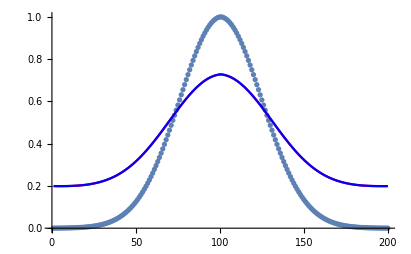

### TR Evolution Kernels

#### NLO Soft Evolution factors

The QCD running coupling
ⅆα/ⅆLog[μ]=β=-β0 αs^2-β1 αs^3

Evolution equation
ⅆLog[J]/ⅆLog[μ]=-Γ Log[z^2 μ^2 Exp[2EulerGamma]/4]+γJ
(*RG of the absolute value of the coordinate space Jet function*)
Define 2S[ν,μ]=2∫_α[ν]^α[μ] ⅆα Γ[α]/β[α] ∫_α[ν]^α ⅆαp/β[αp]=-2∫_α[ν]^α[μ] ⅆα(Γ1 α+Γ2 α^2+Γ3 α^3+Γ4 α^4)/(-β0 α^2-β1 α^3-β2 α^4-β3 α^5) ∫_α[ν]^α ⅆαp/(-β0 αp^2-β1 αp^3-β2 αp^4-β3 αp^5);
Define aJ[ν,μ]=∫_ν^μ ⅆα γJ/β;
Define aΓ[ν,μ]=∫_⋁^μ ⅆα Γ[α]/β[α]=∫_⋁^μ ⅆα (Γ1 α+Γ2 α^2+Γ3 α^3+Γ4 α^4)/(β0 α^2+β1 α^3+β2 α^4+β3 α^5);

```mathematica
SNLO[ν_,μ_,nf_]:=Module[{β0,β1,β2,Γ1,Γ2,Γ3,αν,αμ,r},
(*β0=(11CA)/(6Pi)-nf/(3Pi);
β1=2(17 CA^2-nf*Tf*(10*CA+6*CF))/(24 Pi^2);
β2=2(2857-5033/9 nf+325/27 nf^2)/(128 Pi^3);
Γ1=CF/Pi;
Γ2=CF CA (-1/12+67/(36 Pi^2))-5  CF nf/(18 Pi^2);
Γ3=4 CF (-16/27 nf^2 Tf^2+CA nf Tf (-418/27+(40 π^2)/27-(56 Zeta[3])/3)+CA^2 (245/6-(134 π^2)/27+(11 π^4)/45+(22 Zeta[3])/3)+CF nf Tf (-55/3+16 Zeta[3]))(1/(4Pi))^3;
αν=αsNLO[[1]][ν];
αμ=αsNLO[[1]][μ];
r=αμ/αν;
-((Γ1 (-1+r-r Log[r]))/(r β0^2 αν)+(2 (-1+r) (β1 Γ1-β0 Γ2)+Log[r] (-2 β1 Γ1+2 β0 Γ2+β1 Γ1 Log[r]))/(2 β0^3)-(((-1+r) ((-1+r) β1^2 Γ1-(-3+r) β0 β1 Γ2+β0 (-(1+r) β2 Γ1+(-1+r) β0 Γ3))+2 ((-1+r) β1^2 Γ1+β0 β2 Γ1-r β0 β1 Γ2) Log[r]) αν)/(2 β0^4))*)
αν=αsNLO[[1]][ν];
αμ=αsNLO[[1]][μ];
r=αμ/αν;
-((0.4244131815783876 (-1.+r-1. r Log[r]))/((1.7507043740108488-0.1061032953945969 nf)^2 r αν)-1/(1.7507043740108488-0.1061032953945969 nf)^4 0.5 αν (((1.7507043740108488-0.1061032953945969 nf) (0.00021387463030592366 (2857.-559.2222222222222 nf+12.037037037037036 nf^2) (-1.-1. r)+0.002687627869433291 (1.7507043740108488-0.1061032953945969 nf) (220.29342596801393-34.34764320790106 nf-0.14814814814814814 nf^2) (-1.+r))-0.008443431970194815 (153.-19. nf) (1.7507043740108488-0.1061032953945969 nf) (0.42094658933740353-0.03752636431197695 nf) (-3.+r)+0.000030257070769012834 (153.-19. nf)^2 (-1.+r)) (-1.+r)+2. (0.00021387463030592366 (1.7507043740108488-0.1061032953945969 nf) (2857.-559.2222222222222 nf+12.037037037037036 nf^2)+0.000030257070769012834 (153.-19. nf)^2 (-1.+r)-0.008443431970194815 (153.-19. nf) (1.7507043740108488-0.1061032953945969 nf) (0.42094658933740353-0.03752636431197695 nf) r) Log[r])+1/(1.7507043740108488-0.1061032953945969 nf)^3 0.5 (2. (0.003583503825911055 (153.-19. nf)-1. (1.7507043740108488-0.1061032953945969 nf) (0.42094658933740353-0.03752636431197695 nf)) (-1.+r)+Log[r] (-0.00716700765182211 (153.-19. nf)+2. (1.7507043740108488-0.1061032953945969 nf) (0.42094658933740353-0.03752636431197695 nf)+0.003583503825911055 (153.-19. nf) Log[r])))
]
```

```mathematica
aΓNLO[ν_,μ_,nf_]:=Module[{β0,β1,β2,Γ1,Γ2,Γ3,αν,αμ},
αν=αsNLO[[1]][ν];
αμ=αsNLO[[1]][μ];
β0=(11CA)/(6Pi)-nf/(3Pi);
β1=2(17 CA^2-nf*Tf*(10*CA+6*CF))/(24 Pi^2);
β2=2(2857-5033/9 nf+325/27 nf^2)/(128 Pi^3);
(*JHEP 01(2007)076; e-Print:hep-ph/0607228*)
Γ1=CF/Pi;
Γ2=CF CA (-1/12+67/(36 Pi^2))-5  CF nf/(18 Pi^2);
Γ3=4 CF (-16/27 nf^2 Tf^2+CA nf Tf (-418/27+(40 π^2)/27-(56 Zeta[3])/3)+CA^2 (245/6-(134 π^2)/27+(11 π^4)/45+(22 Zeta[3])/3)+CF nf Tf (-55/3+16 Zeta[3]))(1/(4Pi))^3;
-((Γ1 Log[αμ]-Γ1 Log[αν])/β0+(αν (β1 Γ1-β0 Γ2))/β0^2+(αμ (-β1 Γ1+β0 Γ2))/β0^2+(αν^2 (-β1^2 Γ1+β0 β2 Γ1+β0 β1 Γ2-β0^2 Γ3))/(2 β0^3)+(αμ^2 (β1^2 Γ1-β0 β2 Γ1-β0 β1 Γ2+β0^2 Γ3))/(2 β0^3))
]
```

```mathematica
aJNLO[ν_,μ_,nf_]:=Module[{β0,β1,γJ1,γJ2,αν,αμ},
(*
β0=(11CA)/(6Pi)-nf/(3Pi);
β1=2(17 CA^2-nf*Tf*(10*CA+6*CF))/(24 Pi^2);
γJ1=-CF/π;
γJ2=(23 CA CF)/144-(349 CA CF)/(108 π^2)-(CF nf Tf)/36+(29 CF nf Tf)/(27 π^2)+(5 CA CF Zeta[3])/(4 π^2);
αν=αsNLO[[1]][ν];
αμ=αsNLO[[1]][μ];
-((γJ1 Log[(αμ(β0+β1 αν))/((β0+β1 αμ)αν)])/β0+(γJ2 Log[(β0+β1 αμ)/(β0+β1 αν)])/β1)
*)
αν=αsNLO[[1]][ν];
αμ=αsNLO[[1]][μ];
-(1/(153.-19. nf)118.4352528130723 (-0.06181208443124142+0.05403245248463692 nf) Log[(1.7507043740108488-0.1061032953945969 nf+0.008443431970194815 (153.-19. nf) αμ)/(1.7507043740108488-0.1061032953945969 nf+0.008443431970194815 (153.-19. nf) αν)]-(0.4244131815783876 Log[(αμ (1.7507043740108488-0.1061032953945969 nf+0.008443431970194815 (153.-19. nf) αν))/((1.7507043740108488-0.1061032953945969 nf+0.008443431970194815 (153.-19. nf) αμ) αν)])/(1.7507043740108488-0.1061032953945969 nf))
]
```

#### NNLO Soft Evolution factors

```mathematica
SNNLO[ν_,μ_,nf_]:=Module[{β0,β1,β2,β3,Γ1,Γ2,Γ3,Γ4,αν,αμ,r},
αν=αsNNLO[[1]][ν];
αμ=αsNNLO[[1]][μ];
r=αμ/αν;
(*
β0=(11CA)/(6Pi)-nf/(3Pi);
β1=2(17 CA^2-nf*Tf*(10*CA+6*CF))/(24 Pi^2);
β2=2(2857-5033/9 nf+325/27 nf^2)/(128 Pi^3);
β3=2 1/(4Pi)^4(29243-6946.3nf+405.089*nf^2+1.49931*nf^3);
(*JHEP 01(2007)076; e-Print:hep-ph/0607228*)
Γ1=CF/Pi;
Γ2=CF CA (-1/12+67/(36 Pi^2))-5  CF nf/(18 Pi^2);
Γ3=4 CF (-16/27 nf^2 Tf^2+CA nf Tf (-418/27+(40 π^2)/27-(56 Zeta[3])/3)+CA^2 (245/6-(134 π^2)/27+(11 π^4)/45+(22 Zeta[3])/3)+CF nf Tf (-55/3+16 Zeta[3]))(1/(4Pi))^3;
Γ4=Piecewise[{{7849,nf==3},{4313,nf==4},{1553,nf==5}}](1/(4Pi))^4;
-((Γ1 (-1+r-r Log[r]))/(r β0^2 αν)+(2 (-1+r) (β1 Γ1-β0 Γ2)+Log[r] (-2 β1 Γ1+2 β0 Γ2+β1 Γ1 Log[r]))/(2 β0^3)-(((-1+r) ((-1+r) β1^2 Γ1-(-3+r) β0 β1 Γ2+β0 (-(1+r) β2 Γ1+(-1+r) β0 Γ3))+2 ((-1+r) β1^2 Γ1+β0 β2 Γ1-r β0 β1 Γ2) Log[r]) αν)/(2 β0^4)+(-((β1^3 Γ1-2 β0 β1 β2 Γ1+β0^2 β3 Γ1) Log[r])/(2 β0^5)+((β1^3 Γ1-β0 β1 β2 Γ1-β0 β1^2 Γ2+β0^2 β1 Γ3) Log[r] r^2)/(2 β0^5)+((-β1 β2 Γ1+β0 β3 Γ1+β1^2 Γ2-β0 β1 Γ3) (r-1))/(2 β0^4)+((4 β1^3 Γ1-7 β0 β1 β2 Γ1+3 β0^2 β3 Γ1-3 β0 β1^2 Γ2+4 β0^2 β2 Γ2+β0^2 β1 Γ3-2 β0^3 Γ4) (r-1)^2)/(4 β0^5)+((β1^3 Γ1-2 β0 β1 β2 Γ1+β0^2 β3 Γ1-β0 β1^2 Γ2+β0^2 β2 Γ2+β0^2 β1 Γ3-β0^3 Γ4) (r-1)^3)/(3 β0^5)) αν^2)
*)
Γ4=0.8301952532517868-0.20740149085932388 nf+0.00784293896438143 nf^2+0.000131225944768728 nf^3;
-(1/((-16.5+1. nf)^5 r αν)(169349.12278808458+nf^2 (1866.1060362323371-1866.1060362323371 r)-169349.12278808458 r+nf^3 (-37.69911184307752+37.69911184307752 r)+nf (-30790.74959783356+30790.74959783356 r)+(169349.12278808458-30790.74959783356 nf+1866.1060362323371 nf^2-37.69911184307752 nf^3) r Log[r])+1/((-16.5+1. nf)^5 r)(-43003.13498926942 r+43003.13498926942 r^2+nf^4 r (-3.3333333333333326+3.3333333333333326 r)+nf (14847.751816230802 r-14847.751816230802 r^2)+nf^3 (145.39118679673192 r-145.39118679673192 r^2)+nf^2 (-2233.3637464382305 r+2233.3637464382305 r^2)+(-43003.13498926942+14847.751816230802 nf-2233.3637464382305 nf^2+145.39118679673192 nf^3-3.3333333333333326 nf^4) r Log[r]+(-62481.37500000001+15332.625 nf-1170.0000000000002 nf^2+28.500000000000004 nf^3) r Log[r]^2)+1/((-16.5+1. nf)^5 r)(47948.92216609327 r-80572.08116774802 r^2+32623.15900165475 r^3+nf^4 r (-3.257652489948413+3.6306216363562243 r-0.3729691464078115 r^2)+nf^5 r (0.017683882565766147-0.035367765131532294 r+0.017683882565766147 r^2)+nf (-14014.14615263123 r+25351.31023200847 r^2-11337.164079377242 r^3)+nf^3 (51.63751702712898 r-11.089900837336602 r^2-40.547616189792365 r^3)+nf^2 (628.6599133087333 r-1887.0711242919285 r^2+1258.4112109831951 r^3)+r (47057.78467366614+nf^2 (1592.5391757213044-2222.290473395767 r)+nf^4 (2.155223187702749-5.039906531243351 r)-31732.021509227627 r+nf^3 (-85.06831708261798+177.2534502995394 r)+nf (-15650.565985637146+12973.583912383161 r)) Log[r]) αν+1/((-16.5+1. nf)^5 r)(-47395.70468150936 r+11949.470025598639 r^2+138907.13222018708 r^3-103460.89756427635 r^4+nf^4 r (-6.040275823142721+6.400673019763813 r+7.465761631685678 r^2-7.8261588283067685 r^3)+nf^5 r (0.10832153467984487-0.19056356877175792 r+0.05078760478515303 r^2+0.03145442930676004 r^3)+66503.2450053653 r Γ4-199509.7350160959 r^3 Γ4+133006.49001073057 r^4 Γ4+nf^3 (-124.09085827361426 r^2+r^4 (339.8881430858445-29.60881320326807 Γ4)+r (204.47113045684586-14.804406601634035 Γ4)+r^3 (-420.268415269076+44.413219804902106 Γ4))+nf^2 (1187.78488763929 r^2+r^3 (7432.48911329624-2198.4543803426545 Γ4)+r (-3090.3714744059444+732.818126780885 Γ4)+r^4 (-5529.902526529585+1465.6362535617695 Γ4))+nf (-5927.35618398285 r^2+r^4 (39390.678866918104-24182.998183769196 Γ4)+r (20474.800614034288-12091.499091884598 Γ4)+r^3 (-53938.123296969534+36274.4972756538 Γ4))+r (44691.59347537425-24072.635248517938 r^2+nf^2 (1904.6362785910057-1367.69181323402 r^2)+nf^5 (0.021362605853455324-0.02673753457228358 r^2)+nf^4 (1.8082231159079556+0.33805708587718314 r^2)+nf^3 (-117.3805099908506+62.34376954508361 r^2)+nf (-14264.593988573215+9896.160165740834 r^2)) Log[r]) αν^2)
]
```

```mathematica
aΓNNLO[ν_,μ_,nf_]:=Module[{β0,β1,β2,β3,Γ1,Γ2,Γ3,Γ4,αν,αμ},
αν=αsNNLO[[1]][ν];
αμ=αsNNLO[[1]][μ];
(*
β0=(11CA)/(6Pi)-nf/(3Pi);
β1=2(17 CA^2-nf*Tf*(10*CA+6*CF))/(24 Pi^2);
β2=2(2857-5033/9 nf+325/27 nf^2)/(128 Pi^3);
β3=2 1/(4Pi)^4(29243-6946.3nf+405.089*nf^2+1.49931*nf^3);
(*JHEP 01(2007)076; e-Print:hep-ph/0607228*)
Γ1=CF/Pi;
Γ2=CF CA (-1/12+67/(36 Pi^2))-5  CF nf/(18 Pi^2);
Γ3=4 CF (-16/27 nf^2 Tf^2+CA nf Tf (-418/27+(40 π^2)/27-(56 Zeta[3])/3)+CA^2 (245/6-(134 π^2)/27+(11 π^4)/45+(22 Zeta[3])/3)+CF nf Tf (-55/3+16 Zeta[3]))(1/(4Pi))^3;
Γ4=Piecewise[{{7849,nf==3},{4313,nf==4},{1553,nf==5}}](1/(4Pi))^4;
-((αν (β1 Γ1-β0 Γ2))/β0^2+(αμ (-β1 Γ1+β0 Γ2))/β0^2+(αν^2 (-β1^2 Γ1+β0 β2 Γ1+β0 β1 Γ2-β0^2 Γ3))/(2 β0^3)+(αμ^2 (β1^2 Γ1-β0 β2 Γ1-β0 β1 Γ2+β0^2 Γ3))/(2 β0^3)+(αν^3 (β1^3 Γ1-2 β0 β1 β2 Γ1+β0^2 β3 Γ1-β0 β1^2 Γ2+β0^2 β2 Γ2+β0^2 β1 Γ3-β0^3 Γ4))/(3 β0^4)+(αμ^3 (-β1^3 Γ1+2 β0 β1 β2 Γ1-β0^2 β3 Γ1+β0 β1^2 Γ2-β0^2 β2 Γ2-β0^2 β1 Γ3+β0^3 Γ4))/(3 β0^4)+(Γ1 Log[αμ]-Γ1 Log[αν])/β0)
*)
Γ4=0.8301952532517868-0.20740149085932388 nf+0.00784293896438143 nf^2+0.000131225944768728 nf^3;
-1/(16.5-1. nf)^4(4562.774334660177 αμ-1575.395396903199 nf αμ+236.96725331191917 nf^2 αμ-15.426484040464658 nf^3 αμ+0.35367765131532286 nf^4 αμ+3461.4246762574794 αμ^2-1202.9104692511764 nf αμ^2+133.52157644682234 nf^2 αμ^2-4.302235698132281 nf^3 αμ^2-0.039573255514378555 nf^4 αμ^2+0.0018763182155988479 nf^5 αμ^2-10977.542176052542 αμ^3+4179.480835610317 nf αμ^3-586.7408812756962 nf^2 αμ^3+36.06325204695837 nf^3 αμ^3-0.8303812419648653 nf^4 αμ^3+0.003337418604203626 nf^5 αμ^3-4562.774334660177 αν+1575.395396903199 nf αν-236.96725331191917 nf^2 αν+15.426484040464658 nf^3 αν-0.35367765131532286 nf^4 αν-3461.4246762574794 αν^2+1202.9104692511764 nf αν^2-133.52157644682234 nf^2 αν^2+4.302235698132281 nf^3 αν^2+0.039573255514378555 nf^4 αν^2-0.0018763182155988479 nf^5 αν^2+10977.542176052542 αν^3-4179.480835610317 nf αν^3+586.7408812756962 nf^2 αν^3-36.06325204695837 nf^3 αν^3+0.8303812419648653 nf^4 αν^3-0.003337418604203626 nf^5 αν^3+14112.426899007045 αμ^3 Γ4-2565.895799819463 nf αμ^3 Γ4+155.50883635269474 nf^2 αμ^3 Γ4-3.1415926535897927 nf^3 αμ^3 Γ4-14112.426899007045 αν^3 Γ4+2565.895799819463 nf αν^3 Γ4-155.50883635269474 nf^2 αν^3 Γ4+3.1415926535897927 nf^3 αν^3 Γ4-3.999999999999999 (-16.5+1. nf)^3 Log[αμ]+3.999999999999999 (-16.5+1. nf)^3 Log[αν])
]
```

```mathematica
aJNNLO[ν_,μ_,nf_]:=Module[{β0,β1,β2,γJ1,γJ2,γs3,γHH3,γHL3,γJ3,αν,αμ},
αν=αsNNLO[[1]][ν];
αμ=αsNNLO[[1]][μ];
(*β0=(11CA)/(6Pi)-nf/(3Pi);
β1=2(17 CA^2-nf*Tf*(10*CA+6*CF))/(24 Pi^2);
β2=2(2857-5033/9 nf+325/27 nf^2)/(128 Pi^3);
γJ1=-CF/π;
γJ2=(23 CA CF)/144-(349 CA CF)/(108 π^2)-(CF nf Tf)/36+(29 CF nf Tf)/(27 π^2)+(5 CA CF Zeta[3])/(4 π^2);
(*(*DOI:10.1007/JHEP08(2022)280; e-Print:2205.02249[hep-ph]*)
γs3=-2(1/(4Pi))^3(CF^2 nf (1711/54-π^2/3-(4 π^4)/45-(152 Zeta[3])/9)+CA CF nf (5921/729-(707 π^2)/243+(4 π^4)/15-(364 Zeta[3])/27)+CF nf^2 (1040/729+(10 π^2)/81-(56 Zeta[3])/27)+CA^2 CF (-136781/1458+(6325 π^2)/486-(44 π^4)/45+(658 Zeta[3])/3-44/9 π^2 Zeta[3]-96 Zeta[5]));
(*DOI:10.1007/JHEP03(2020)071; e-Print:1911.04494[hep-ph]*)
γHH3=2(1/(4Pi))^3 CF(CA^2(-343/9+(304 π^2)/27-(22 π^4)/45-(740 Zeta[3])/9-4/3 π^2 Zeta[3]+36 Zeta[5])+CF nf Tf(110/3-32 Zeta[3])+CA nf Tf(356/27-(80 π^2)/27+(496 Zeta[3])/9)+(32 nf^2 Tf^2)/27);
(*Based on 2γHL-γs=γHH*)
γHL3=(γs3+γHH3)/2;
γJ3=2γHL3-2γs3;*)
γJ3=-0.07788903112582936+0.05491061519528693 nf+0.0006023279289568775 nf^2;
-((αν (β1 γJ1-β0 γJ2))/β0^2+(αμ (-β1 γJ1+β0 γJ2))/β0^2+(αν^2 (-β1^2 γJ1+β0 β2 γJ1+β0 β1 γJ2-β0^2 γJ3))/(2 β0^3)+(αμ^2 (β1^2 γJ1-β0 β2 γJ1-β0 β1 γJ2+β0^2 γJ3))/(2 β0^3)+(γJ1 Log[αμ]-γJ1 Log[αν])/β0)*)
-1/(-16.5+1. nf)^3(-644.9699398507711 αμ-9.374731624410005 nf αμ+11.339724955901072 nf^2 αμ-0.5092438673435247 nf^3 αμ-109.89176567551844 αμ^2+20.555856689417507 nf αμ^2-4.385774382444827 nf^2 αμ^2+0.33422650259849124 nf^3 αμ^2-0.0028384034949943218 nf^4 αμ^2+644.9699398507711 αν+9.374731624410005 nf αν-11.339724955901072 nf^2 αν+0.5092438673435247 nf^3 αν+109.89176567551844 αν^2-20.555856689417507 nf αν^2+4.385774382444827 nf^2 αν^2-0.33422650259849124 nf^3 αν^2+0.0028384034949943218 nf^4 αν^2+4. (16.5-1. nf)^2 Log[αμ]-4. (16.5-1. nf)^2 Log[αν])
]
```

#### Evolution kernel formalism

```mathematica
ClearAll[P𝒥,P𝒥LT]
P𝒥[S_,aΓ_,aJ_,y_,x_,μ_,μi_,Pz_,zs_]:=Module[{nf,ξ,η},
nf=3;(*Fermion flavors, GeV*)
ξ=y/x;(*Momentum fraction*)
η=2aΓ[μi,μ,nf];
Re[Exp[-2 S[μi,μ,nf]+aJ[μi,μ,nf]](Sin[(η π)/2]Gamma[1-η] ⅇ^(-EulerGamma η))/Pi((2 Abs[x]Pz)/μi*Abs[1-ξ])^η/Abs[1-ξ]]
]

(*∫_(Abs[ξ']>L/Abs[x]) ⅆξ'P𝒥[ξ']*)
P𝒥LT[S_,aΓ_,aJ_,x_,μ_,μi_,Pz_,zs_,L_]:=Module[{nf,η},
nf=3;(*Fermion flavors, GeV*)
η=2aΓ[μi,μ,nf];
Re[Exp[-2 S[μi,μ,nf]+aJ[μi,μ,nf]](Sin[(η π)/2]Gamma[1-η] ⅇ^(-EulerGamma η))/Pi((2 Abs[x]Pz)/μi)^η(-(-1+L/Abs[x])^η/η-(1+L/Abs[x])^η/η)]
]
```

#### Evolution matrix generator

```mathematica
(*The old method to generate Jet*)
PJgenold[S_,aΓ_,aJ_,xlist_,μ_,μi_,Pz_,zs_]:=Module[{Δx,L,δCmf},
Δx=Abs[xlist[[2]]-xlist[[1]]];
L=Abs[xlist[[1]]]+Δx/2;
(*Subscript[y, i],Subscript[x, j]*)
δCmf[i_,j_]:=If[i≠j,P𝒥[S,aΓ,aJ,xlist[[i]],xlist[[j]],μ,μi,Pz,zs]/Abs[xlist[[j]]] Δx,-Sum[P𝒥[S,aΓ,aJ,xlist[[k]],xlist[[i]],μ,μi,Pz,zs]/Abs[xlist[[i]]] Δx,{k,1,j-1}]-Sum[P𝒥[S,aΓ,aJ,xlist[[k]],xlist[[i]],μ,μi,Pz,zs]/Abs[xlist[[i]]] Δx,{k,j+1,Length[xlist]}]-P𝒥LT[S,aΓ,aJ,xlist[[i]],μ,μi,Pz,zs,L]];
ParallelTable[δCmf[i,j],{i,1,Length[xlist]},{j,1,Length[xlist]}]
]
```

```mathematica
J2ηp[y_,x_]:=Abs[x-y];

J2dn[y_,x_]:=1/Abs[1-y/x];

Jηpgen[C_,xlist_]:=Module[{Δx,δCmf},
Δx=Abs[xlist[[2]]-xlist[[1]]];
(*Subscript[y, i],Subscript[x, j]*)
δCmf[i_,j_]:=If[i≠j,C[xlist[[i]],xlist[[j]]],0];
ParallelTable[δCmf[i,j],{i,1,Length[xlist]},{j,1,Length[xlist]}]
]

Jdngen[C_,xlist_]:=Module[{Δx,δCmf},
Δx=Abs[xlist[[2]]-xlist[[1]]];
(*Subscript[y, i],Subscript[x, j]*)
δCmf[i_,j_]:=If[i≠j,C[xlist[[i]],xlist[[j]]] Δx/Abs[xlist[[j]]],0];
ParallelTable[δCmf[i,j],{i,1,Length[xlist]},{j,1,Length[xlist]}]
]

ClearAll[PJgen];
(*Cηpm: J2ηp; 
Cdnm: J2dn*)
PJgen[Cηpm_,Cdnm_,S_,aΓ_,aJ_,xlist_,μ_,μi_,Pz_,zs_]:=Module[{Δx,L,nf,η,fam,Moffdiag,Mdiag},
Δx=Abs[xlist[[2]]-xlist[[1]]];
L=(xlist[[Length[xlist]]]-xlist[[1]])/2;
nf=3;(*Fermion flavors*)
(*Subscript[y, i],Subscript[x, j]*)
η=2aΓ[μi,μ,nf];
fam=Exp[-2 S[μi,μ,nf]+aJ[μi,μ,nf]];
Moffdiag=fam*Cdnm*(Sin[(η π)/2]Gamma[1-η] ⅇ^(-EulerGamma η))/Pi((2Pz)/μi)^η((Cηpm+IdentityMatrix[Length[xlist]])^η-IdentityMatrix[Length[xlist]]);
Mdiag=-DiagonalMatrix[Total[Moffdiag,{1}]+ParallelTable[P𝒥LT[S,aΓ,aJ,x,μ,μi,Pz,zs,L+Δx/2],{x,xlist}]];
Moffdiag+Mdiag
]
```

(*Consistency check of the two methods*)
xlist=Join[Table[x,{x,-2,-0.02,0.02}],Table[x,{x,0.02,2,0.02}]];
Pz=2;
zs=0.12/0.197;
μ=2;
μi=1;
nf=3;

J2ηpls=Jηpgen[J2ηp,xlist];
J2dnls=Jdngen[J2dn,xlist];
PJm=PJgen[J2ηpls,J2dnls,SNLO,aΓNLO,aJNLO,xlist,μ,μi,Pz,zs];

PJm1=PJgenold[SNLO,aΓNLO,aJNLO,xlist,μ,μi,Pz,zs];

fvls=Table[Exp[-2 x^2],{x,xlist}];
Show[
ListPlot[fvls],
ListPlot[PJm.fvls,Joined→True,PlotStyle→Red],
ListPlot[PJm1.fvls,Joined→True,PlotStyle→Blue]
]

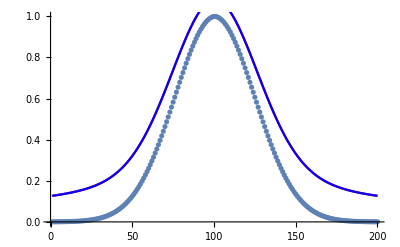

## NLO without considering renormalon

### Lattice Data Pion Valence Quasi - PDF, Pz=1.9 GeV, zs=0.12fm, λ_L=25

```mathematica
(*
The data is generated by BNL/ANL Collaborations, Gao:2021dbh
Renormalized based on the RGR+LRR method, Zhang:2023bxs
*)
```

```mathematica
Pz=1.94;(*GeV*)
zs=0.12/GeVfm;(*GeV^-1*)
```

```mathematica
qls={{-2.,0.004644373353200662},{-1.99,0.004120247847633056},{-1.98,0.003622067087287381},{-1.97,0.0031552223149979},{-1.96,0.002726220362994065},{-1.95,0.002332121946113358},{-1.94,0.0019748105696102128},{-1.93,0.0016617946317518128},{-1.92,0.0013896498468505209},{-1.91,0.001157969030572405},{-1.9,0.0009740062784405524},{-1.89,0.0008343069837817357},{-1.88,0.0007354910726053484},{-1.87,0.0006844474334537591},{-1.86,0.0006775322836966953},{-1.85,0.0007093746490651379},{-1.84,0.0007848304657079239},{-1.83,0.0009010306765860066},{-1.82,0.0010500511427830594},{-1.81,0.0012347748938322317},{-1.8,0.0014529691648524812},{-1.79,0.001695074247695391},{-1.78,0.0019608772861017146},{-1.77,0.0022493261730182164},{-1.76,0.002548904375507088},{-1.75,0.0028570969569776993},{-1.74,0.0031734135755238676},{-1.73,0.003485305751241066},{-1.72,0.003787860492555417},{-1.71,0.004080714570753909},{-1.7,0.0043513415591125565},{-1.69,0.00459209780747},{-1.68,0.004802930805205951},{-1.67,0.004971973589585376},{-1.66,0.0050893807375176625},{-1.65,0.0051544301651739125},{-1.64,0.0051572528883037675},{-1.63,0.0050857962876900975},{-1.62,0.004939638608088999},{-1.61,0.0047103710762440385},{-1.6,0.004384588087735983},{-1.59,0.003961638559377615},{-1.58,0.0034355478567254134},{-1.57,0.0027923727101677306},{-1.56,0.0020307899346212865},{-1.55,0.001147653353127118},{-1.54,0.0001293662115165748},{-1.53,-0.0010262053436745217},{-1.52,-0.002319241626571331},{-1.51,-0.003762070898562308},{-1.5,-0.00535767461611031},{-1.49,-0.007103322325419803},{-1.48,-0.009009173627881811},{-1.47,-0.011078971693766839},{-1.46,-0.013307310981559016},{-1.45,-0.01570136328212513},{-1.44,-0.0182654114646309},{-1.43,-0.020991762810628253},{-1.42,-0.02388391683318669},{-1.41,-0.026946333224345465},{-1.4,-0.030169528227263636},{-1.39,-0.03355282186583401},{-1.38,-0.03710035027897443},{-1.37,-0.04081071753848808},{-1.36,-0.04465944879214011},{-1.35,-0.04865963860632827},{-1.34,-0.052799840226409746},{-1.33,-0.05707031143306075},{-1.32,-0.061472539521033896},{-1.31,-0.06599476622458914},{-1.3,-0.07062273776425468},{-1.29,-0.07535273029596794},{-1.28,-0.08017913633450793},{-1.27,-0.08507972027317055},{-1.26,-0.09004977201197047},{-1.25,-0.09507580386853634},{-1.24,-0.10013643453606268},{-1.23,-0.1052217762493435},{-1.22,-0.11031842068337755},{-1.21,-0.11539884898458205},{-1.2,-0.12044650543362649},{-1.19,-0.12544472751274555},{-1.18,-0.1303598348657722},{-1.17,-0.1351735733812622},{-1.16,-0.13984482290530456},{-1.15,-0.14433717761958592},{-1.14,-0.14860599638320865},{-1.13,-0.15260865725942266},{-1.12,-0.15627783779791632},{-1.11,-0.15953306926178973},{-1.1,-0.16228714588271892},{-1.09,-0.16441456147949368},{-1.08,-0.16574791938649297},{-1.07,-0.16608017752841578},{-1.06,-0.16512238403855972},{-1.05,-0.16247228616306125},{-1.04,-0.1576079570670807},{-1.03,-0.1498745549865596},{-1.02,-0.13856750481624514},{-1.01,-0.12329118093713683},{-1.,-0.10452791672037298},{-0.99,-0.08386577478628733},{-0.98,-0.06335779275286002},{-0.97,-0.044487529193872555},{-0.96,-0.027791608369410428},{-0.95,-0.013222288017471662},{-0.94,-0.0005060197676422379},{-0.93,0.010712926418813828},{-0.92,0.020747082549468394},{-0.91,0.029838009883754957},{-0.9,0.03821136232499601},{-0.89,0.0460465568700808},{-0.88,0.05346537832030689},{-0.87,0.06059246869266078},{-0.86,0.06753496522164032},{-0.85,0.0743557313427976},{-0.84,0.08112836368178805},{-0.83,0.0879271737670217},{-0.82,0.09478793608711844},{-0.81,0.10175642926745493},{-0.8,0.10889143693088607},{-0.79,0.11621674758268581},{-0.78,0.1237610583222274},{-0.77,0.13157504382591872},{-0.76,0.1396783280519504},{-0.75,0.14808810060910665},{-0.74,0.1568499582295041},{-0.73,0.16598381259698758},{-0.72,0.17549878312097195},{-0.71,0.18543635329779484},{-0.7,0.19581939592572234},{-0.69,0.20665153845175915},{-0.68,0.2179701214189261},{-0.67,0.22980255026321988},{-0.66,0.24214923764638413},{-0.65,0.25504292135001416},{-0.64,0.2685163194493533},{-0.63,0.28256884463310383},{-0.62,0.2972271045353138},{-0.61,0.3125311593245419},{-0.6,0.32848076047689745},{-0.59,0.34509795809233895},{-0.58,0.3624260434801411},{-0.57,0.38046917194148},{-0.56,0.3992438019869307},{-0.55,0.4187982160626459},{-0.54,0.43914024161844556},{-0.53,0.46028312747525324},{-0.52,0.4822784905078693},{-0.51,0.5051420233327284},{-0.5,0.5288815511766826},{-0.49,0.5535517147724702},{-0.48,0.5791791881504709},{-0.47,0.6057682632765653},{-0.46,0.6333745418103949},{-0.45,0.6620379331888059},{-0.44,0.6917625152625423},{-0.43,0.7226035104236992},{-0.42,0.7546157172441825},{-0.41,0.78780717183097},{-0.4,0.8222324759737083},{-0.39,0.8579628404685727},{-0.38,0.8950151875900143},{-0.37,0.9334445457962022},{-0.36,0.9733404584277825},{-0.35,1.0147346620849456},{-0.34,1.05768518912032},{-0.33,1.1023027626430033},{-0.32,1.1486414268852312},{-0.31,1.1967701625144844},{-0.3,1.246818645446664},{-0.29,1.2988768175409042},{-0.28,1.3530252429364402},{-0.27,1.409432971004116},{-0.26,1.4682327591165751},{-0.25,1.5295336404418816},{-0.24,1.5935488304240892},{-0.23,1.6604769430098891},{-0.22,1.7304757454739113},{-0.21,1.8038230429831537},{-0.2,1.8808140737409953},{-0.19,1.961688885024415},{-0.18,2.046824052821365},{-0.17,2.1366600426183044},{-0.16,2.231574775658292},{-0.15,2.3320820112281115},{-0.14,2.439006731842744},{-0.13,2.552529992013758},{-0.12,2.673751967916616},{-0.11,2.8037487067637175},{-0.1,2.9433866951050964},{-0.09,3.0936367993617053},{-0.08,3.2556429738423134},{-0.07,3.4302252428984916},{-0.06,3.617879799994142},{-0.05,3.8181709368900414},{-0.04,4.027353378189677},{-0.03,4.235688352317414},{-0.02,4.423972412482997},{-0.01,4.56087468343495},{0,4.612277188558619},{0.01,4.56087468343495},{0.02,4.423972412482997},{0.03,4.235688352317414},{0.04,4.027353378189677},{0.05,3.8181709368900414},{0.06,3.617879799994142},{0.07,3.4302252428984916},{0.08,3.2556429738423134},{0.09,3.0936367993617053},{0.1,2.9433866951050964},{0.11,2.8037487067637175},{0.12,2.673751967916616},{0.13,2.552529992013758},{0.14,2.439006731842744},{0.15,2.3320820112281115},{0.16,2.231574775658292},{0.17,2.1366600426183044},{0.18,2.046824052821365},{0.19,1.961688885024415},{0.2,1.8808140737409953},{0.21,1.8038230429831537},{0.22,1.7304757454739113},{0.23,1.6604769430098891},{0.24,1.5935488304240892},{0.25,1.5295336404418816},{0.26,1.4682327591165751},{0.27,1.409432971004116},{0.28,1.3530252429364402},{0.29,1.2988768175409042},{0.3,1.246818645446664},{0.31,1.1967701625144844},{0.32,1.1486414268852312},{0.33,1.1023027626430033},{0.34,1.05768518912032},{0.35,1.0147346620849456},{0.36,0.9733404584277825},{0.37,0.9334445457962022},{0.38,0.8950151875900143},{0.39,0.8579628404685727},{0.4,0.8222324759737083},{0.41,0.78780717183097},{0.42,0.7546157172441825},{0.43,0.7226035104236992},{0.44,0.6917625152625423},{0.45,0.6620379331888059},{0.46,0.6333745418103949},{0.47,0.6057682632765653},{0.48,0.5791791881504709},{0.49,0.5535517147724702},{0.5,0.5288815511766826},{0.51,0.5051420233327284},{0.52,0.4822784905078693},{0.53,0.46028312747525324},{0.54,0.43914024161844556},{0.55,0.4187982160626459},{0.56,0.3992438019869307},{0.57,0.38046917194148},{0.58,0.3624260434801411},{0.59,0.34509795809233895},{0.6,0.32848076047689745},{0.61,0.3125311593245419},{0.62,0.2972271045353138},{0.63,0.28256884463310383},{0.64,0.2685163194493533},{0.65,0.25504292135001416},{0.66,0.24214923764638413},{0.67,0.22980255026321988},{0.68,0.2179701214189261},{0.69,0.20665153845175915},{0.7,0.19581939592572234},{0.71,0.18543635329779484},{0.72,0.17549878312097195},{0.73,0.16598381259698758},{0.74,0.1568499582295041},{0.75,0.14808810060910665},{0.76,0.1396783280519504},{0.77,0.13157504382591872},{0.78,0.1237610583222274},{0.79,0.11621674758268581},{0.8,0.10889143693088607},{0.81,0.10175642926745493},{0.82,0.09478793608711844},{0.83,0.0879271737670217},{0.84,0.08112836368178805},{0.85,0.0743557313427976},{0.86,0.06753496522164032},{0.87,0.06059246869266078},{0.88,0.05346537832030689},{0.89,0.0460465568700808},{0.9,0.03821136232499601},{0.91,0.029838009883754957},{0.92,0.020747082549468394},{0.93,0.010712926418813828},{0.94,-0.0005060197676422379},{0.95,-0.013222288017471662},{0.96,-0.027791608369410428},{0.97,-0.044487529193872555},{0.98,-0.06335779275286002},{0.99,-0.08386577478628733},{1.,-0.10452791672037298},{1.01,-0.12329118093713683},{1.02,-0.13856750481624514},{1.03,-0.1498745549865596},{1.04,-0.1576079570670807},{1.05,-0.16247228616306125},{1.06,-0.16512238403855972},{1.07,-0.16608017752841578},{1.08,-0.16574791938649297},{1.09,-0.16441456147949368},{1.1,-0.16228714588271892},{1.11,-0.15953306926178973},{1.12,-0.15627783779791632},{1.13,-0.15260865725942266},{1.14,-0.14860599638320865},{1.15,-0.14433717761958592},{1.16,-0.13984482290530456},{1.17,-0.1351735733812622},{1.18,-0.1303598348657722},{1.19,-0.12544472751274555},{1.2,-0.12044650543362649},{1.21,-0.11539884898458205},{1.22,-0.11031842068337755},{1.23,-0.1052217762493435},{1.24,-0.10013643453606268},{1.25,-0.09507580386853634},{1.26,-0.09004977201197047},{1.27,-0.08507972027317055},{1.28,-0.08017913633450793},{1.29,-0.07535273029596794},{1.3,-0.07062273776425468},{1.31,-0.06599476622458914},{1.32,-0.061472539521033896},{1.33,-0.05707031143306075},{1.34,-0.052799840226409746},{1.35,-0.04865963860632827},{1.36,-0.04465944879214011},{1.37,-0.04081071753848808},{1.38,-0.03710035027897443},{1.39,-0.03355282186583401},{1.4,-0.030169528227263636},{1.41,-0.026946333224345465},{1.42,-0.02388391683318669},{1.43,-0.020991762810628253},{1.44,-0.0182654114646309},{1.45,-0.01570136328212513},{1.46,-0.013307310981559016},{1.47,-0.011078971693766839},{1.48,-0.009009173627881811},{1.49,-0.007103322325419803},{1.5,-0.00535767461611031},{1.51,-0.003762070898562308},{1.52,-0.002319241626571331},{1.53,-0.0010262053436745217},{1.54,0.0001293662115165748},{1.55,0.001147653353127118},{1.56,0.0020307899346212865},{1.57,0.0027923727101677306},{1.58,0.0034355478567254134},{1.59,0.003961638559377615},{1.6,0.004384588087735983},{1.61,0.0047103710762440385},{1.62,0.004939638608088999},{1.63,0.0050857962876900975},{1.64,0.0051572528883037675},{1.65,0.0051544301651739125},{1.66,0.0050893807375176625},{1.67,0.004971973589585376},{1.68,0.004802930805205951},{1.69,0.00459209780747},{1.7,0.0043513415591125565},{1.71,0.004080714570753909},{1.72,0.003787860492555417},{1.73,0.003485305751241066},{1.74,0.0031734135755238676},{1.75,0.0028570969569776993},{1.76,0.002548904375507088},{1.77,0.0022493261730182164},{1.78,0.0019608772861017146},{1.79,0.001695074247695391},{1.8,0.0014529691648524812},{1.81,0.0012347748938322317},{1.82,0.0010500511427830594},{1.83,0.0009010306765860066},{1.84,0.0007848304657079239},{1.85,0.0007093746490651379},{1.86,0.0006775322836966953},{1.87,0.0006844474334537591},{1.88,0.0007354910726053484},{1.89,0.0008343069837817357},{1.9,0.0009740062784405524},{1.91,0.001157969030572405},{1.92,0.0013896498468505209},{1.93,0.0016617946317518128},{1.94,0.0019748105696102128},{1.95,0.002332121946113358},{1.96,0.002726220362994065},{1.97,0.0031552223149979},{1.98,0.003622067087287381},{1.99,0.004120247847633056},{2.,0.004644373353200662}};
```

### Pz=1.9 GeV, Δx=0.0025, L=3, γ=0.4

```mathematica
μ=2;(*GeV*)(*Factorization Scale*)
PertAcc="NLO";
```

#### Discretization

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

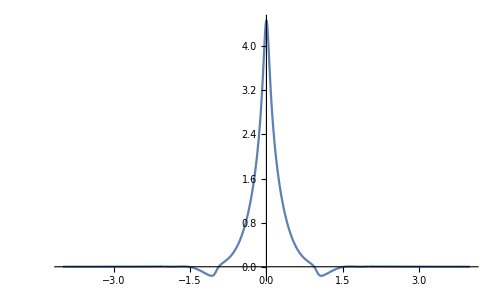

```mathematica
qlsgf=GaussianFilter[qls,{{4,0}}];
qinttest=Interpolation[qlsgf];
ClearAll[qint];
qint[x_]:=If[Abs[x]<2,qinttest[x],qinttest[2]Exp[-(Abs[x]-2)]];
Plot[qint[x],{x,-4,4},PlotRange->All]
```

```mathematica
L=3;
Δx=0.0025;(*Discretization*)
xlist=Join[Table[x,{x,-L,-Δx,Δx}],Table[x,{x,Δx,L,Δx}]];
qV=Table[qint[x],{x,xlist}];
```

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

#### Fixed order results

```mathematica
(*Matrix Elements generation*)
```

```mathematica
If[PertAcc=="NLO",
MCratio1pluswμ=SubMGen[Cratio1pluswμ,xlist,Pz,zs];
MCratio1pluswoμ=SubMGen[Cratio1pluswoμ,xlist,Pz,zs];
MChybrid1plus=SubMGen[Chybrid1plus,xlist,Pz,zs];
MfixGen[μ_]:=Module[{C1},
C1=(αsNLO[[1]][μ]*CF)/(2Pi)((-Log[(μ/Pz)^2])MCratio1pluswμ+MCratio1pluswoμ+MChybrid1plus);
IdentityMatrix[Length[xlist]]-C1
],
Nothing[];
]
```

```mathematica
(*Calculation*)
```

```mathematica
ChM=MfixGen[μ];
fVfixed=ChM.qV;
(fVfixed+Reverse[fVfixed])/2
fVint=Interpolation[Transpose[{xlist,(fVfixed+Reverse[fVfixed])/2}]];
```

{-0.00367194,-0.00422786,-0.00451364,-0.00470935,-0.00486003,-0.00498366,-0.00508927,-0.00518198,-0.00526502,-0.00534052,-0.00540999,-0.00547451,-0.00553491,-0.00559181,-0.0056457,-0.00569699,-0.00574598,-0.00579296,-0.00583812,-0.00588167,-0.00592376,-0.00596452,-0.00600407,-0.00604251,-0.00607993,-0.00611641,-0.00615201,-0.0061868,-0.00622083,-0.00625415,-0.00628681,-0.00631883,-0.00635027,-0.00638115,-0.0064115,-0.00644135,-0.00647072,-0.00649964,-0.00652812,-0.00655619,-0.00658387,-0.00661116,-0.0066381,-0.00666468,-0.00669092,-0.00671685,-0.00674245,-0.00676776,-0.00679278,-0.00681751,-0.00684196,-0.00686616,-0.00689009,-0.00691377,-0.00693721,-0.00696042,-0.00698339,-0.00700614,-0.00702866,-0.00705098,-0.00707308,-0.00709498,-0.00711667,-0.00713817,-0.00715948,-0.0071806,-0.00720153,-0.00722229,-0.00724286,-0.00726326,-0.00728349,-0.00730354,-0.00732343,-0.00734316,-0.00736272,-0.00738212,-0.00740137,-0.00742046,-0.0074394,-0.00745818,-0.00747682,-0.00749531,-0.00751365,-0.00753185,-0.0075499,-0.00756782,-0.00758559,-0.00760322,-0.00762072,-0.00763808,-0.00765531,-0.0076724,-0.00768936,-0.00770619,-0.00772289,-0.00773946,-0.0077559,-0.00777221,-0.00778839,-0.00780445,-0.00782039,-0.00783619,-0.00785188,-0.00786744,-0.00788288,-0.0078982,-0.00791339,-0.00792847,-0.00794342,-0.00795826,-0.00797298,-0.00798757,-0.00800205,-0.00801642,-0.00803066,-0.00804479,-0.0080588,-0.0080727,-0.00808648,-0.00810014,-0.00811369,-0.00812713,-0.00814045,-0.00815365,-0.00816675,-0.00817972,-0.00819259,-0.00820534,-0.00821798,-0.00823051,-0.00824292,-0.00825522,-0.00826741,-0.00827949,-0.00829146,-0.00830331,-0.00831505,-0.00832669,-0.00833821,-0.00834962,-0.00836091,-0.0083721,-0.00838318,-0.00839414,-0.008405,-0.00841574,-0.00842638,-0.0084369,-0.00844731,-0.00845761,-0.00846781,-0.00847789,-0.00848786,-0.00849772,-0.00850747,-0.00851712,-0.00852665,-0.00853607,-0.00854538,-0.00855458,-0.00856367,-0.00857265,-0.00858152,-0.00859029,-0.00859894,-0.00860748,-0.00861591,-0.00862423,-0.00863244,-0.00864054,-0.00864853,-0.00865642,-0.00866419,-0.00867185,-0.0086794,-0.00868684,-0.00869417,-0.00870139,-0.0087085,-0.0087155,-0.00872239,-0.00872917,-0.00873584,-0.0087424,-0.00874884,-0.00875518,-0.00876141,-0.00876753,-0.00877354,-0.00877943,-0.00878522,-0.00879089,-0.00879646,-0.00880192,-0.00880726,-0.00881249,-0.00881762,-0.00882263,-0.00882753,-0.00883233,-0.00883701,-0.00884158,-0.00884604,-0.00885039,-0.00885463,-0.00885876,-0.00886278,-0.00886669,-0.00887049,-0.00887418,-0.00887776,-0.00888123,-0.00888459,-0.00888784,-0.00889098,-0.00889401,-0.00889692,-0.00889973,-0.00890243,-0.00890502,-0.00890751,-0.00890988,-0.00891214,-0.00891429,-0.00891634,-0.00891827,-0.0089201,-0.00892182,-0.00892343,-0.00892493,-0.00892632,-0.00892761,-0.00892878,-0.00892985,-0.00893082,-0.00893167,-0.00893242,-0.00893306,-0.0089336,-0.00893403,-0.00893435,-0.00893457,-0.00893468,-0.00893469,-0.00893459,-0.00893439,-0.00893408,-0.00893367,-0.00893316,-0.00893254,-0.00893182,-0.008931,-0.00893008,-0.00892905,-0.00892793,-0.0089267,-0.00892538,-0.00892395,-0.00892243,-0.00892081,-0.00891909,-0.00891727,-0.00891536,-0.00891335,-0.00891125,-0.00890905,-0.00890675,-0.00890437,-0.00890189,-0.00889932,-0.00889666,-0.00889391,-0.00889106,-0.00888814,-0.00888512,-0.00888202,-0.00887883,-0.00887555,-0.0088722,-0.00886876,-0.00886524,-0.00886164,-0.00885796,-0.0088542,-0.00885036,-0.00884645,-0.00884247,-0.00883841,-0.00883428,-0.00883009,-0.00882582,-0.00882149,-0.00881709,-0.00881263,-0.0088081,-0.00880352,-0.00879888,-0.00879418,-0.00878943,-0.00878463,-0.00877978,-0.00877487,-0.00876993,-0.00876494,-0.0087599,-0.00875483,-0.00874973,-0.00874459,-0.00873942,-0.00873422,-0.008729,-0.00872376,-0.00871849,-0.00871322,-0.00870793,-0.00870263,-0.00869732,-0.00869202,-0.00868672,-0.00868143,-0.00867614,-0.00867087,-0.00866563,-0.0086604,-0.00865521,-0.00865005,-0.00864493,-0.00863986,-0.00863484,-0.00862987,-0.00862497,-0.00862014,-0.00861538,-0.00861071,-0.00860612,-0.00860164,-0.00859726,-0.008593,-0.00858885,-0.00858484,-0.00858097,-0.00857726,-0.0085737,-0.00857032,-0.00856712,-0.00856411,-0.00856132,-0.00855874,-0.0085564,-0.00855431,-0.00855248,-0.00855094,-0.00854969,-0.00854876,-0.00854816,-0.00854792,-0.00854806,-0.00854859,-0.00854955,-0.00855095,-0.00855283,-0.00855521,-0.00855813,-0.00856162,-0.00856571,-0.00857044,-0.00857585,-0.00858199,-0.0085889,-0.00859663,-0.00860524,-0.00861478,-0.00862533,-0.00863695,-0.00864971,-0.00866372,-0.00867904,-0.0086958,-0.0087141,-0.00873407,-0.00875585,-0.0087796,-0.0088055,-0.00883374,-0.00886457,-0.00889825,-0.00893508,-0.00897544,-0.00901974,-0.00906849,-0.00912233,-0.00918201,-0.00924849,-0.00932302,-0.00940725,-0.00950345,-0.00961494,-0.00974691,-0.00990846,-0.010119,-0.010442,-0.0102087,-0.010061,-0.0099493,-0.00985854,-0.00978177,-0.00971502,-0.00965578,-0.00960231,-0.00955333,-0.0095079,-0.00946535,-0.00942511,-0.0093868,-0.00935,-0.0093144,-0.00927977,-0.00924564,-0.00921212,-0.00917908,-0.00914641,-0.00911476,-0.00908335,-0.0090521,-0.00902091,-0.00898982,-0.00895865,-0.00892734,-0.00889583,-0.00886414,-0.00883218,-0.00879991,-0.0087673,-0.0087344,-0.00870113,-0.00866749,-0.00863346,-0.00859916,-0.00856447,-0.00852941,-0.00849396,-0.00845822,-0.00842212,-0.00838566,-0.00834887,-0.0083118,-0.00827443,-0.00823679,-0.00819888,-0.00816085,-0.00812262,-0.0080842,-0.00804563,-0.00800703,-0.00796832,-0.00792956,-0.00789075,-0.007852,-0.00781327,-0.00777462,-0.00773607,-0.00769776,-0.00765965,-0.00762175,-0.00758411,-0.00754688,-0.00750998,-0.00747347,-0.00743737,-0.00740178,-0.00736669,-0.00733215,-0.0072982,-0.00726498,-0.00723246,-0.00720066,-0.00716963,-0.00713953,-0.0071103,-0.00708198,-0.00705461,-0.00702829,-0.00700301,-0.00697883,-0.00695578,-0.00693401,-0.00691347,-0.00689422,-0.00687629,-0.00685985,-0.00684484,-0.00683129,-0.00681926,-0.00680883,-0.0068,-0.00679282,-0.00678734,-0.00678367,-0.00678179,-0.00678175,-0.0067836,-0.00678747,-0.00679332,-0.00680118,-0.0068111,-0.00682317,-0.00683737,-0.00685376,-0.00687238,-0.00689331,-0.00691655,-0.00694214,-0.00697013,-0.00700064,-0.00703363,-0.00706913,-0.00710718,-0.00714784,-0.00719112,-0.00723705,-0.00728567,-0.00733703,-0.00739114,-0.00744805,-0.00750778,-0.00757043,-0.00763598,-0.00770444,-0.00777584,-0.00785024,-0.00792763,-0.00800803,-0.00809148,-0.00817798,-0.00826758,-0.00836028,-0.00845612,-0.00855516,-0.00865738,-0.0087628,-0.00887142,-0.00898328,-0.00909838,-0.00921673,-0.00933834,-0.00946319,-0.00959132,-0.00972275,-0.00985748,-0.00999554,-0.0101369,-0.0102816,-0.0104297,-0.010581,-0.0107357,-0.0108937,-0.011055,-0.0112196,-0.0113875,-0.0115587,-0.0117332,-0.0119109,-0.012092,-0.0122763,-0.0124639,-0.0126547,-0.0128488,-0.013046,-0.0132465,-0.01345,-0.0136567,-0.0138665,-0.0140794,-0.0142953,-0.0145143,-0.0147363,-0.0149613,-0.0151893,-0.0154201,-0.0156539,-0.0158906,-0.0161299,-0.016372,-0.0166169,-0.0168645,-0.0171146,-0.0173674,-0.0176227,-0.0178805,-0.0181408,-0.0184035,-0.0186686,-0.0189359,-0.0192054,-0.0194771,-0.019751,-0.0200269,-0.0203047,-0.0205844,-0.0208661,-0.0211496,-0.0214347,-0.0217216,-0.0220101,-0.0223001,-0.0225914,-0.0228841,-0.0231782,-0.0234734,-0.0237697,-0.024067,-0.0243653,-0.0246645,-0.0249644,-0.0252651,-0.0255664,-0.0258682,-0.0261703,-0.0264728,-0.0267755,-0.0270784,-0.0273811,-0.0276838,-0.0279863,-0.0282885,-0.0285903,-0.0288916,-0.0291924,-0.0294924,-0.0297915,-0.0300897,-0.0303869,-0.0306828,-0.0309772,-0.0312702,-0.0315615,-0.0318512,-0.032139,-0.0324248,-0.0327086,-0.0329901,-0.033269,-0.0335454,-0.0338192,-0.0340901,-0.0343578,-0.0346224,-0.0348838,-0.0351418,-0.0353961,-0.0356467,-0.0358935,-0.0361364,-0.0363751,-0.0366095,-0.0368396,-0.037065,-0.0372856,-0.0375013,-0.0377119,-0.0379172,-0.038117,-0.0383111,-0.0384995,-0.0386818,-0.0388579,-0.0390276,-0.0391907,-0.0393471,-0.0394964,-0.0396385,-0.0397732,-0.0399003,-0.0400195,-0.0401306,-0.0402336,-0.0403281,-0.0404139,-0.0404908,-0.0405587,-0.0406172,-0.040666,-0.0407049,-0.0407339,-0.0407525,-0.0407604,-0.0407575,-0.0407436,-0.0407184,-0.0406815,-0.0406328,-0.040572,-0.0404989,-0.0404129,-0.0403141,-0.040202,-0.0400765,-0.0399369,-0.0397833,-0.0396154,-0.0394327,-0.0392349,-0.0390217,-0.0387929,-0.0385481,-0.0382867,-0.0380087,-0.0377136,-0.0374011,-0.0370705,-0.0367217,-0.0363545,-0.0359683,-0.0355624,-0.0351367,-0.0346909,-0.0342246,-0.0337367,-0.0332274,-0.0326962,-0.0321426,-0.0315655,-0.030965,-0.0303407,-0.029692,-0.0290177,-0.0283181,-0.0275926,-0.0268406,-0.0260607,-0.0252532,-0.0244177,-0.0235534,-0.0226586,-0.021734,-0.0207788,-0.0197925,-0.018773,-0.017721,-0.0166359,-0.0155171,-0.0143618,-0.0131713,-0.011945,-0.0106821,-0.00937907,-0.00803805,-0.00665829,-0.00523916,-0.00377621,-0.00227247,-0.000727232,0.000860036,0.00249517,0.00417359,0.00589586,0.00766229,0.0094806,0.0113439,0.0132523,0.0152059,0.0172146,0.0192682,0.0213664,0.0235082,0.0257063,0.0279461,0.0302262,0.0325442,0.034915,0.0373189,0.0397526,0.042212,0.0447102,0.0472247,0.0497499,0.0522789,0.0548154,0.0573411,0.0598479,0.0623271,0.0647601,0.0671467,0.0694771,0.0717423,0.0738919,0.0759575,0.0779302,0.0798036,0.0814965,0.0830778,0.0845427,0.085891,0.0870287,0.0880502,0.0889579,0.0897592,0.0903798,0.0909099,0.0913593,0.0917414,0.0920334,0.0922854,0.0925124,0.0927292,0.092973,0.0932365,0.0935341,0.0938779,0.0943448,0.0948805,0.0954949,0.0961939,0.0970616,0.0980245,0.0990862,0.100246,0.101571,0.102993,0.104512,0.106122,0.10786,0.109683,0.111584,0.113557,0.115616,0.117736,0.119913,0.122141,0.124417,0.126734,0.129088,0.131474,0.133884,0.136318,0.138775,0.14125,0.143734,0.146232,0.148742,0.151261,0.153781,0.156308,0.15884,0.161377,0.163911,0.166447,0.168985,0.171524,0.17406,0.176595,0.17913,0.181665,0.184196,0.186726,0.189255,0.191784,0.194308,0.196832,0.199356,0.201878,0.204398,0.206918,0.209438,0.211957,0.214475,0.216993,0.219511,0.222031,0.22455,0.22707,0.229591,0.232115,0.234639,0.237166,0.239695,0.242226,0.24476,0.247297,0.249837,0.252381,0.254928,0.25748,0.260036,0.262597,0.265162,0.267732,0.270308,0.272889,0.275476,0.278069,0.280669,0.283275,0.285887,0.288507,0.291134,0.293768,0.29641,0.29906,0.301718,0.304385,0.30706,0.309743,0.312436,0.315138,0.317849,0.32057,0.3233,0.326041,0.328792,0.331553,0.334325,0.337107,0.339901,0.342705,0.345521,0.348348,0.351187,0.354037,0.3569,0.359775,0.362662,0.365561,0.368474,0.371399,0.374337,0.377288,0.380253,0.383231,0.386223,0.389228,0.392247,0.395281,0.398329,0.401391,0.404468,0.407559,0.410666,0.413787,0.416923,0.420075,0.423242,0.426425,0.429623,0.432838,0.436068,0.439315,0.442577,0.445857,0.449153,0.452465,0.455795,0.459141,0.462505,0.465886,0.469284,0.4727,0.476133,0.479584,0.483054,0.486541,0.490047,0.493571,0.497114,0.500675,0.504255,0.507854,0.511472,0.51511,0.518766,0.522443,0.526139,0.529855,0.533591,0.537347,0.541123,0.54492,0.548737,0.552575,0.556434,0.560313,0.564214,0.568137,0.572081,0.576046,0.580034,0.584043,0.588075,0.592129,0.596205,0.600304,0.604426,0.608571,0.612739,0.61693,0.621145,0.625384,0.629647,0.633934,0.638245,0.64258,0.646941,0.651326,0.655736,0.660171,0.664632,0.669118,0.673631,0.678169,0.682735,0.687326,0.691945,0.69659,0.701263,0.705964,0.710692,0.715448,0.720232,0.725045,0.729886,0.734757,0.739657,0.744587,0.749547,0.754536,0.759557,0.764608,0.76969,0.774803,0.779948,0.785126,0.790335,0.795577,0.800852,0.806161,0.811504,0.81688,0.822291,0.827738,0.833219,0.838735,0.844288,0.849878,0.855504,0.861167,0.866869,0.872608,0.878387,0.884204,0.890062,0.895959,0.901897,0.907876,0.913897,0.91996,0.926066,0.932215,0.938409,0.944647,0.95093,0.957259,0.963635,0.970058,0.976528,0.983047,0.989616,0.996234,1.0029,1.00962,1.0164,1.02322,1.0301,1.03704,1.04403,1.05107,1.05818,1.06534,1.07256,1.07985,1.08719,1.0946,1.10207,1.10961,1.11721,1.12488,1.13262,1.14043,1.14831,1.15626,1.16428,1.17239,1.18056,1.18882,1.19716,1.20558,1.21408,1.22267,1.23134,1.24011,1.24896,1.25791,1.26695,1.27609,1.28533,1.29467,1.30412,1.31368,1.32334,1.33311,1.343,1.35301,1.36314,1.37339,1.38378,1.39429,1.40494,1.41572,1.42665,1.43773,1.44895,1.46033,1.47187,1.48358,1.49546,1.5075,1.51974,1.53215,1.54476,1.55757,1.57058,1.58381,1.59726,1.61093,1.62486,1.63902,1.65343,1.66811,1.68308,1.69832,1.71387,1.72972,1.74591,1.76243,1.7793,1.79654,1.81418,1.83222,1.85068,1.86958,1.88896,1.90883,1.92921,1.95013,1.97164,1.99375,2.01651,2.03996,2.06414,2.08909,2.11488,2.14157,2.16917,2.19782,2.22758,2.25853,2.29069,2.32427,2.3594,2.3962,2.43461,2.47507,2.51776,2.56289,2.61029,2.66075,2.71456,2.77208,2.83306,2.89875,2.96963,3.04629,3.12862,3.21836,3.31634,3.42358,3.54067,3.66982,3.81273,3.97152,4.14874,4.34811,4.57437,4.83409,5.13733,5.49825,5.94132,6.5106,7.29753,8.53266,11.1311,11.1311,8.53266,7.29753,6.5106,5.94132,5.49825,5.13733,4.83409,4.57437,4.34811,4.14874,3.97152,3.81273,3.66982,3.54067,3.42358,3.31634,3.21836,3.12862,3.04629,2.96963,2.89875,2.83306,2.77208,2.71456,2.66075,2.61029,2.56289,2.51776,2.47507,2.43461,2.3962,2.3594,2.32427,2.29069,2.25853,2.22758,2.19782,2.16917,2.14157,2.11488,2.08909,2.06414,2.03996,2.01651,1.99375,1.97164,1.95013,1.92921,1.90883,1.88896,1.86958,1.85068,1.83222,1.81418,1.79654,1.7793,1.76243,1.74591,1.72972,1.71387,1.69832,1.68308,1.66811,1.65343,1.63902,1.62486,1.61093,1.59726,1.58381,1.57058,1.55757,1.54476,1.53215,1.51974,1.5075,1.49546,1.48358,1.47187,1.46033,1.44895,1.43773,1.42665,1.41572,1.40494,1.39429,1.38378,1.37339,1.36314,1.35301,1.343,1.33311,1.32334,1.31368,1.30412,1.29467,1.28533,1.27609,1.26695,1.25791,1.24896,1.24011,1.23134,1.22267,1.21408,1.20558,1.19716,1.18882,1.18056,1.17239,1.16428,1.15626,1.14831,1.14043,1.13262,1.12488,1.11721,1.10961,1.10207,1.0946,1.08719,1.07985,1.07256,1.06534,1.05818,1.05107,1.04403,1.03704,1.0301,1.02322,1.0164,1.00962,1.0029,0.996234,0.989616,0.983047,0.976528,0.970058,0.963635,0.957259,0.95093,0.944647,0.938409,0.932215,0.926066,0.91996,0.913897,0.907876,0.901897,0.895959,0.890062,0.884204,0.878387,0.872608,0.866869,0.861167,0.855504,0.849878,0.844288,0.838735,0.833219,0.827738,0.822291,0.81688,0.811504,0.806161,0.800852,0.795577,0.790335,0.785126,0.779948,0.774803,0.76969,0.764608,0.759557,0.754536,0.749547,0.744587,0.739657,0.734757,0.729886,0.725045,0.720232,0.715448,0.710692,0.705964,0.701263,0.69659,0.691945,0.687326,0.682735,0.678169,0.673631,0.669118,0.664632,0.660171,0.655736,0.651326,0.646941,0.64258,0.638245,0.633934,0.629647,0.625384,0.621145,0.61693,0.612739,0.608571,0.604426,0.600304,0.596205,0.592129,0.588075,0.584043,0.580034,0.576046,0.572081,0.568137,0.564214,0.560313,0.556434,0.552575,0.548737,0.54492,0.541123,0.537347,0.533591,0.529855,0.526139,0.522443,0.518766,0.51511,0.511472,0.507854,0.504255,0.500675,0.497114,0.493571,0.490047,0.486541,0.483054,0.479584,0.476133,0.4727,0.469284,0.465886,0.462505,0.459141,0.455795,0.452465,0.449153,0.445857,0.442577,0.439315,0.436068,0.432838,0.429623,0.426425,0.423242,0.420075,0.416923,0.413787,0.410666,0.407559,0.404468,0.401391,0.398329,0.395281,0.392247,0.389228,0.386223,0.383231,0.380253,0.377288,0.374337,0.371399,0.368474,0.365561,0.362662,0.359775,0.3569,0.354037,0.351187,0.348348,0.345521,0.342705,0.339901,0.337107,0.334325,0.331553,0.328792,0.326041,0.3233,0.32057,0.317849,0.315138,0.312436,0.309743,0.30706,0.304385,0.301718,0.29906,0.29641,0.293768,0.291134,0.288507,0.285887,0.283275,0.280669,0.278069,0.275476,0.272889,0.270308,0.267732,0.265162,0.262597,0.260036,0.25748,0.254928,0.252381,0.249837,0.247297,0.24476,0.242226,0.239695,0.237166,0.234639,0.232115,0.229591,0.22707,0.22455,0.222031,0.219511,0.216993,0.214475,0.211957,0.209438,0.206918,0.204398,0.201878,0.199356,0.196832,0.194308,0.191784,0.189255,0.186726,0.184196,0.181665,0.17913,0.176595,0.17406,0.171524,0.168985,0.166447,0.163911,0.161377,0.15884,0.156308,0.153781,0.151261,0.148742,0.146232,0.143734,0.14125,0.138775,0.136318,0.133884,0.131474,0.129088,0.126734,0.124417,0.122141,0.119913,0.117736,0.115616,0.113557,0.111584,0.109683,0.10786,0.106122,0.104512,0.102993,0.101571,0.100246,0.0990862,0.0980245,0.0970616,0.0961939,0.0954949,0.0948805,0.0943448,0.0938779,0.0935341,0.0932365,0.092973,0.0927292,0.0925124,0.0922854,0.0920334,0.0917414,0.0913593,0.0909099,0.0903798,0.0897592,0.0889579,0.0880502,0.0870287,0.085891,0.0845427,0.0830778,0.0814965,0.0798036,0.0779302,0.0759575,0.0738919,0.0717423,0.0694771,0.0671467,0.0647601,0.0623271,0.0598479,0.0573411,0.0548154,0.0522789,0.0497499,0.0472247,0.0447102,0.042212,0.0397526,0.0373189,0.034915,0.0325442,0.0302262,0.0279461,0.0257063,0.0235082,0.0213664,0.0192682,0.0172146,0.0152059,0.0132523,0.0113439,0.0094806,0.00766229,0.00589586,0.00417359,0.00249517,0.000860036,-0.000727232,-0.00227247,-0.00377621,-0.00523916,-0.00665829,-0.00803805,-0.00937907,-0.0106821,-0.011945,-0.0131713,-0.0143618,-0.0155171,-0.0166359,-0.017721,-0.018773,-0.0197925,-0.0207788,-0.021734,-0.0226586,-0.0235534,-0.0244177,-0.0252532,-0.0260607,-0.0268406,-0.0275926,-0.0283181,-0.0290177,-0.029692,-0.0303407,-0.030965,-0.0315655,-0.0321426,-0.0326962,-0.0332274,-0.0337367,-0.0342246,-0.0346909,-0.0351367,-0.0355624,-0.0359683,-0.0363545,-0.0367217,-0.0370705,-0.0374011,-0.0377136,-0.0380087,-0.0382867,-0.0385481,-0.0387929,-0.0390217,-0.0392349,-0.0394327,-0.0396154,-0.0397833,-0.0399369,-0.0400765,-0.040202,-0.0403141,-0.0404129,-0.0404989,-0.040572,-0.0406328,-0.0406815,-0.0407184,-0.0407436,-0.0407575,-0.0407604,-0.0407525,-0.0407339,-0.0407049,-0.040666,-0.0406172,-0.0405587,-0.0404908,-0.0404139,-0.0403281,-0.0402336,-0.0401306,-0.0400195,-0.0399003,-0.0397732,-0.0396385,-0.0394964,-0.0393471,-0.0391907,-0.0390276,-0.0388579,-0.0386818,-0.0384995,-0.0383111,-0.038117,-0.0379172,-0.0377119,-0.0375013,-0.0372856,-0.037065,-0.0368396,-0.0366095,-0.0363751,-0.0361364,-0.0358935,-0.0356467,-0.0353961,-0.0351418,-0.0348838,-0.0346224,-0.0343578,-0.0340901,-0.0338192,-0.0335454,-0.033269,-0.0329901,-0.0327086,-0.0324248,-0.032139,-0.0318512,-0.0315615,-0.0312702,-0.0309772,-0.0306828,-0.0303869,-0.0300897,-0.0297915,-0.0294924,-0.0291924,-0.0288916,-0.0285903,-0.0282885,-0.0279863,-0.0276838,-0.0273811,-0.0270784,-0.0267755,-0.0264728,-0.0261703,-0.0258682,-0.0255664,-0.0252651,-0.0249644,-0.0246645,-0.0243653,-0.024067,-0.0237697,-0.0234734,-0.0231782,-0.0228841,-0.0225914,-0.0223001,-0.0220101,-0.0217216,-0.0214347,-0.0211496,-0.0208661,-0.0205844,-0.0203047,-0.0200269,-0.019751,-0.0194771,-0.0192054,-0.0189359,-0.0186686,-0.0184035,-0.0181408,-0.0178805,-0.0176227,-0.0173674,-0.0171146,-0.0168645,-0.0166169,-0.016372,-0.0161299,-0.0158906,-0.0156539,-0.0154201,-0.0151893,-0.0149613,-0.0147363,-0.0145143,-0.0142953,-0.0140794,-0.0138665,-0.0136567,-0.01345,-0.0132465,-0.013046,-0.0128488,-0.0126547,-0.0124639,-0.0122763,-0.012092,-0.0119109,-0.0117332,-0.0115587,-0.0113875,-0.0112196,-0.011055,-0.0108937,-0.0107357,-0.010581,-0.0104297,-0.0102816,-0.0101369,-0.00999554,-0.00985748,-0.00972275,-0.00959132,-0.00946319,-0.00933834,-0.00921673,-0.00909838,-0.00898328,-0.00887142,-0.0087628,-0.00865738,-0.00855516,-0.00845612,-0.00836028,-0.00826758,-0.00817798,-0.00809148,-0.00800803,-0.00792763,-0.00785024,-0.00777584,-0.00770444,-0.00763598,-0.00757043,-0.00750778,-0.00744805,-0.00739114,-0.00733703,-0.00728567,-0.00723705,-0.00719112,-0.00714784,-0.00710718,-0.00706913,-0.00703363,-0.00700064,-0.00697013,-0.00694214,-0.00691655,-0.00689331,-0.00687238,-0.00685376,-0.00683737,-0.00682317,-0.0068111,-0.00680118,-0.00679332,-0.00678747,-0.0067836,-0.00678175,-0.00678179,-0.00678367,-0.00678734,-0.00679282,-0.0068,-0.00680883,-0.00681926,-0.00683129,-0.00684484,-0.00685985,-0.00687629,-0.00689422,-0.00691347,-0.00693401,-0.00695578,-0.00697883,-0.00700301,-0.00702829,-0.00705461,-0.00708198,-0.0071103,-0.00713953,-0.00716963,-0.00720066,-0.00723246,-0.00726498,-0.0072982,-0.00733215,-0.00736669,-0.00740178,-0.00743737,-0.00747347,-0.00750998,-0.00754688,-0.00758411,-0.00762175,-0.00765965,-0.00769776,-0.00773607,-0.00777462,-0.00781327,-0.007852,-0.00789075,-0.00792956,-0.00796832,-0.00800703,-0.00804563,-0.0080842,-0.00812262,-0.00816085,-0.00819888,-0.00823679,-0.00827443,-0.0083118,-0.00834887,-0.00838566,-0.00842212,-0.00845822,-0.00849396,-0.00852941,-0.00856447,-0.00859916,-0.00863346,-0.00866749,-0.00870113,-0.0087344,-0.0087673,-0.00879991,-0.00883218,-0.00886414,-0.00889583,-0.00892734,-0.00895865,-0.00898982,-0.00902091,-0.0090521,-0.00908335,-0.00911476,-0.00914641,-0.00917908,-0.00921212,-0.00924564,-0.00927977,-0.0093144,-0.00935,-0.0093868,-0.00942511,-0.00946535,-0.0095079,-0.00955333,-0.00960231,-0.00965578,-0.00971502,-0.00978177,-0.00985854,-0.0099493,-0.010061,-0.0102087,-0.010442,-0.010119,-0.00990846,-0.00974691,-0.00961494,-0.00950345,-0.00940725,-0.00932302,-0.00924849,-0.00918201,-0.00912233,-0.00906849,-0.00901974,-0.00897544,-0.00893508,-0.00889825,-0.00886457,-0.00883374,-0.0088055,-0.0087796,-0.00875585,-0.00873407,-0.0087141,-0.0086958,-0.00867904,-0.00866372,-0.00864971,-0.00863695,-0.00862533,-0.00861478,-0.00860524,-0.00859663,-0.0085889,-0.00858199,-0.00857585,-0.00857044,-0.00856571,-0.00856162,-0.00855813,-0.00855521,-0.00855283,-0.00855095,-0.00854955,-0.00854859,-0.00854806,-0.00854792,-0.00854816,-0.00854876,-0.00854969,-0.00855094,-0.00855248,-0.00855431,-0.0085564,-0.00855874,-0.00856132,-0.00856411,-0.00856712,-0.00857032,-0.0085737,-0.00857726,-0.00858097,-0.00858484,-0.00858885,-0.008593,-0.00859726,-0.00860164,-0.00860612,-0.00861071,-0.00861538,-0.00862014,-0.00862497,-0.00862987,-0.00863484,-0.00863986,-0.00864493,-0.00865005,-0.00865521,-0.0086604,-0.00866563,-0.00867087,-0.00867614,-0.00868143,-0.00868672,-0.00869202,-0.00869732,-0.00870263,-0.00870793,-0.00871322,-0.00871849,-0.00872376,-0.008729,-0.00873422,-0.00873942,-0.00874459,-0.00874973,-0.00875483,-0.0087599,-0.00876494,-0.00876993,-0.00877487,-0.00877978,-0.00878463,-0.00878943,-0.00879418,-0.00879888,-0.00880352,-0.0088081,-0.00881263,-0.00881709,-0.00882149,-0.00882582,-0.00883009,-0.00883428,-0.00883841,-0.00884247,-0.00884645,-0.00885036,-0.0088542,-0.00885796,-0.00886164,-0.00886524,-0.00886876,-0.0088722,-0.00887555,-0.00887883,-0.00888202,-0.00888512,-0.00888814,-0.00889106,-0.00889391,-0.00889666,-0.00889932,-0.00890189,-0.00890437,-0.00890675,-0.00890905,-0.00891125,-0.00891335,-0.00891536,-0.00891727,-0.00891909,-0.00892081,-0.00892243,-0.00892395,-0.00892538,-0.0089267,-0.00892793,-0.00892905,-0.00893008,-0.008931,-0.00893182,-0.00893254,-0.00893316,-0.00893367,-0.00893408,-0.00893439,-0.00893459,-0.00893469,-0.00893468,-0.00893457,-0.00893435,-0.00893403,-0.0089336,-0.00893306,-0.00893242,-0.00893167,-0.00893082,-0.00892985,-0.00892878,-0.00892761,-0.00892632,-0.00892493,-0.00892343,-0.00892182,-0.0089201,-0.00891827,-0.00891634,-0.00891429,-0.00891214,-0.00890988,-0.00890751,-0.00890502,-0.00890243,-0.00889973,-0.00889692,-0.00889401,-0.00889098,-0.00888784,-0.00888459,-0.00888123,-0.00887776,-0.00887418,-0.00887049,-0.00886669,-0.00886278,-0.00885876,-0.00885463,-0.00885039,-0.00884604,-0.00884158,-0.00883701,-0.00883233,-0.00882753,-0.00882263,-0.00881762,-0.00881249,-0.00880726,-0.00880192,-0.00879646,-0.00879089,-0.00878522,-0.00877943,-0.00877354,-0.00876753,-0.00876141,-0.00875518,-0.00874884,-0.0087424,-0.00873584,-0.00872917,-0.00872239,-0.0087155,-0.0087085,-0.00870139,-0.00869417,-0.00868684,-0.0086794,-0.00867185,-0.00866419,-0.00865642,-0.00864853,-0.00864054,-0.00863244,-0.00862423,-0.00861591,-0.00860748,-0.00859894,-0.00859029,-0.00858152,-0.00857265,-0.00856367,-0.00855458,-0.00854538,-0.00853607,-0.00852665,-0.00851712,-0.00850747,-0.00849772,-0.00848786,-0.00847789,-0.00846781,-0.00845761,-0.00844731,-0.0084369,-0.00842638,-0.00841574,-0.008405,-0.00839414,-0.00838318,-0.0083721,-0.00836091,-0.00834962,-0.00833821,-0.00832669,-0.00831505,-0.00830331,-0.00829146,-0.00827949,-0.00826741,-0.00825522,-0.00824292,-0.00823051,-0.00821798,-0.00820534,-0.00819259,-0.00817972,-0.00816675,-0.00815365,-0.00814045,-0.00812713,-0.00811369,-0.00810014,-0.00808648,-0.0080727,-0.0080588,-0.00804479,-0.00803066,-0.00801642,-0.00800205,-0.00798757,-0.00797298,-0.00795826,-0.00794342,-0.00792847,-0.00791339,-0.0078982,-0.00788288,-0.00786744,-0.00785188,-0.00783619,-0.00782039,-0.00780445,-0.00778839,-0.00777221,-0.0077559,-0.00773946,-0.00772289,-0.00770619,-0.00768936,-0.0076724,-0.00765531,-0.00763808,-0.00762072,-0.00760322,-0.00758559,-0.00756782,-0.0075499,-0.00753185,-0.00751365,-0.00749531,-0.00747682,-0.00745818,-0.0074394,-0.00742046,-0.00740137,-0.00738212,-0.00736272,-0.00734316,-0.00732343,-0.00730354,-0.00728349,-0.00726326,-0.00724286,-0.00722229,-0.00720153,-0.0071806,-0.00715948,-0.00713817,-0.00711667,-0.00709498,-0.00707308,-0.00705098,-0.00702866,-0.00700614,-0.00698339,-0.00696042,-0.00693721,-0.00691377,-0.00689009,-0.00686616,-0.00684196,-0.00681751,-0.00679278,-0.00676776,-0.00674245,-0.00671685,-0.00669092,-0.00666468,-0.0066381,-0.00661116,-0.00658387,-0.00655619,-0.00652812,-0.00649964,-0.00647072,-0.00644135,-0.0064115,-0.00638115,-0.00635027,-0.00631883,-0.00628681,-0.00625415,-0.00622083,-0.0061868,-0.00615201,-0.00611641,-0.00607993,-0.00604251,-0.00600407,-0.00596452,-0.00592376,-0.00588167,-0.00583812,-0.00579296,-0.00574598,-0.00569699,-0.0056457,-0.00559181,-0.00553491,-0.00547451,-0.00540999,-0.00534052,-0.00526502,-0.00518198,-0.00508927,-0.00498366,-0.00486003,-0.00470935,-0.00451364,-0.00422786,-0.00367194}

#### DGLAP log resummation

```mathematica
(*Generating xlsf and μhls*)
xlsf=Table[N[1.0/50 i],{i,5,50}];
μhls=2*xlsf*Pz;

(*Generating DGLAP kernels*)
xDGLAP=Table[N[1.0/100 i],{i,1,100}];
If[PertAcc=="NLO",
{Mdglapns0,Mdglapns1}=DGLAPNLOMGen[xDGLAP];,
Nothing[]
];
```

```mathematica
(*Calculation*)
PDFls={};
PDFls2={};
Monitor[
For[i=Length[μhls],i≥1,i--,

ChM=MfixGen[μhls[[i]]];
PDFlist=Transpose[{xlist,ChM.qV}];

PDFint=Interpolation[PDFlist];
PDFintsys[x_]:=(PDFint[x]+PDFint[-x])/2;
PDFCombine[x_]:=If[Abs[x]≤ xlsf[[i]]+Δx/4,PDFintsys[x],If[xlsf[[i]]+Δx/4<Abs[x]≤ xlsf[[i]]+(3Δx)/4,((xlsf[[i]]+(3Δx)/4)-Abs[x])/(Δx/2)PDFintsys[x]+(Abs[x]-(xlsf[[i]]+Δx/4))/(Δx/2)PDFls2[[Length[μhls]-i]][x],PDFls2[[Length[μhls]-i]][x]]];
(*PDFCombine[x_]:=PDFintsys[x];*)

If[PertAcc=="NLO",
AppendTo[PDFls,DGLAPNLOx[PDFCombine,μhls[[i]],μ,Mdglapns0,Mdglapns1,xDGLAP]];AppendTo[PDFls2,DGLAPNLOx[PDFCombine,μhls[[i]],μhls[[i-1]],Mdglapns0,Mdglapns1,xDGLAP]];,
Nothing[]
];

PrintTemporary[{xlsf[[i]],PDFls[[Length[PDFls]]][xlsf[[i]]]}];
],
Row[{ProgressIndicator[i,{1,Length[μhls]}],i}," "]
]

PDFRGR=Table[PDFls[[Length[xlsf]-i+1]][xlsf[[i]]],{i,1,Length[xlsf]}]
```

{2.47782,1.40203,1.45361,1.46526,1.44056,1.39714,1.34432,1.28718,1.22855,1.17001,1.11249,1.05651,1.00237,0.950333,0.900456,0.852715,0.80708,0.76347,0.721835,0.682108,0.644224,0.608094,0.573602,0.540748,0.509458,0.479645,0.451249,0.424176,0.398335,0.373627,0.349942,0.327158,0.305135,0.283703,0.262688,0.241858,0.220945,0.199634,0.177557,0.154332,0.129676,0.103821,0.0786858,0.059925,0.056607,0.0811718}

```mathematica
PDFRGRint=Interpolation[Transpose[Re[{xlsf,PDFRGR}]],InterpolationOrder->2];
```

#### DGLAP+Threshold log

```mathematica
(*Generating xlist and μhls*)
xlsf=Table[N[1.0/50 i],{i,5,45}];
μhls=2*xlsf*Pz;
μils=2*(1-xlsf)*Pz;
```

```mathematica
(*Prepare for hard kernel*)
J1dnm=Jdngen[J1dn,xlist];

If[PertAcc=="NLO",
Hmgen[μ_]:=Module[{},
Hgen[J1dnm,ANLO,HNLO,xlist,μ,Pz,zs]
],
Nothing[]
]
```

```mathematica
(*Prepare for soft function*)
J2ηpm=Jηpgen[J2ηp,xlist];
J2dnm=Jdngen[J2dn,xlist];
Jls0=Jls0gen[J2ηpm,J2dnm];
JLTls0=JLTls0gen[xlist];

If[PertAcc=="NLO",
Jmgen[μ_]:=Module[{},
Jgen[Jls0,JLTls0,JcoeNLO,xlist,μ,Pz,zs]
];
PJmgen[μf_,μi_]:=Module[{},
PJgen[J2ηpm,J2dnm,SNLO,aΓNLO,aJNLO,xlist,μf,μi,Pz,zs]
];,
Nothing[]
]
```

```mathematica
(*Threshold cut*)
Mcut=Table[If[Abs[1-y/x]<0.4,1,0],{y,xlist},{x,xlist}];
```

```mathematica
(*Calculations*)
PDFls={};
PDFls2={};
Monitor[
For[i=Length[μhls],i≥1,i--,

ChM=MfixGen[μhls[[i]]];
If[μhls[[i]]>μils[[i]],
Hm=Hmgen[μhls[[i]]];
Jmμi=Jmgen[μils[[i]]];
Jmμh=Jmgen[μhls[[i]]];
PJm=PJmgen[μhls[[i]],μils[[i]]];
Strnew=(Mcut*PJm).(Mcut*Jmμi).(Mcut*Hm);
Strnew0=(Mcut*Jmμh).(Mcut*Hm);
PDFlist=Transpose[{xlist,(ChM+Strnew-Strnew0).qV}],
PDFlist=Transpose[{xlist,ChM.qV}]
];


PDFint=Interpolation[PDFlist];
PDFintsys[x_]:=(PDFint[x]+PDFint[-x])/2;
If[μhls[[i]]>μils[[i]],
PDFCombine[x_]:=PDFintsys[x],
PDFCombine[x_]:=If[Abs[x]≤ xlsf[[i]]+Δx/4,PDFintsys[x],If[xlsf[[i]]+Δx/4<Abs[x]≤ xlsf[[i]]+(3Δx)/4,((xlsf[[i]]+(3Δx)/4)-Abs[x])/(Δx/2)PDFintsys[x]+(Abs[x]-(xlsf[[i]]+Δx/4))/(Δx/2)PDFls2[[Length[μhls]-i]][x],PDFls2[[Length[μhls]-i]][x]]]
];
(*PDFCombine[x_]:=PDFintsys[x];*)


If[PertAcc=="NLO",
AppendTo[PDFls,DGLAPNLOx[PDFCombine,μhls[[i]],μ,Mdglapns0,Mdglapns1,xDGLAP]];AppendTo[PDFls2,DGLAPNLOx[PDFCombine,μhls[[i]],μhls[[i-1]],Mdglapns0,Mdglapns1,xDGLAP]];,
Nothing[]
];


PrintTemporary[{xlsf[[i]],PDFls[[Length[PDFls]]][xlsf[[i]]]}];
],
Row[{ProgressIndicator[i,{1,Length[μhls]}],i}," "]
]

PDFRGRTR=Table[PDFls[[Length[xlsf]-i+1]][xlsf[[i]]],{i,1,Length[xlsf]}]
```

{2.48698,1.40543,1.4563,1.46759,1.44262,1.39899,1.346,1.28871,1.22994,1.17129,1.11366,1.05758,1.00334,0.951214,0.901245,0.853412,0.80768,0.763967,0.72222,0.682365,0.644326,0.605526,0.569136,0.535297,0.498856,0.468903,0.441528,0.410862,0.386954,0.364106,0.342779,0.317201,0.297978,0.27988,0.258773,0.242911,0.22922,0.222573,0.287219,0.0799064,-1.88849}

```mathematica
PDFRGRTRint=Interpolation[Transpose[Re[{xlsf,PDFRGRTR}]],InterpolationOrder->1];
```

#### CVs Plot

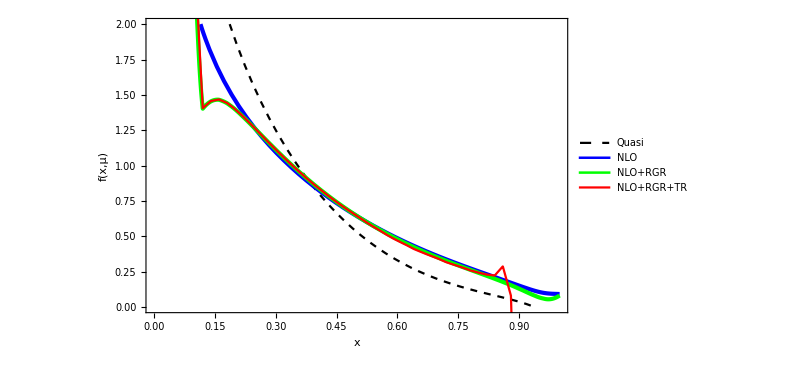

./pics/MCfull6NLO_add.pdf

```mathematica
fig=Show[
Plot[qint[x],{x,0,1},PlotStyle->{Black,Dashed},
PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["Quasi",20]},{0.7,0.75}]],

Plot[fVint[x],{x,0.10,1},PlotStyle->{Blue,Thickness[0.005]},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc,20]},{0.7,0.65}]],

Plot[PDFRGRint[x],{x,0.10,1},PlotStyle->{Green,Thickness[0.005]},PlotRange->All,PlotLegends->Placed[{Style[PertAcc<>"+RGR",20]},{0.7,0.55}]],

Plot[PDFRGRTRint[x],{x,0.10,0.9},PlotStyle->Red,PlotRange->All,PlotLegends->Placed[{Style[PertAcc<>"+RGR+TR",20]},{0.7,0.45}]],

PlotRange->{{0,1},{0,2}},
FrameLabel->{Style["x",20],Style["f(x,μ)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]

SetDirectory[NotebookDirectory[]];
Export["./pics/MCfull6NLO_add.pdf",fig]
```

#### μ_i=2|1-|x_i||P_z r1, μ_h=2|x_i| P_z r2, r1,r2=0.8~1.2

```mathematica
r1ls={1.2,1,0.8};
r2ls={1.2,1,0.8};
xlsf=Table[N[1.0/50 i],{i,5,45}];
Mcut=Table[If[Abs[1-y/x]<0.4,1,0],{y,xlist},{x,xlist}];
```

```mathematica
(*Resummation and variation of r1 and r2*)
PDFRGRTRls=Table[
PrintTemporary[{r1,r2}];
(*Resummation on the inversed matrix*)
PDFls={};
PDFls2={};
μils=2*(1-xlsf)*Pz*r1;
μhls=2*xlsf*Pz*r2;
Monitor[
For[i=Length[μhls],i≥1,i--,

ChM=MfixGen[μhls[[i]]];
Quiet[If[μhls[[i]]>μils[[i]],
Hm=Hmgen[μhls[[i]]];
Jmμi=Jmgen[μils[[i]]];
Jmμh=Jmgen[μhls[[i]]];
PJm=PJmgen[μhls[[i]],μils[[i]]];
Strnew=(Mcut*PJm).(Mcut*Jmμi).(Mcut*Hm);
Strnew0=(Mcut*Jmμh).(Mcut*Hm);
PDFlist=Transpose[{xlist,(ChM+Strnew-Strnew0).qV}],
PDFlist=Transpose[{xlist,ChM.qV}]
];];

ClearAll[PDFint,PDFintsys,PDFCombine];
PDFint=Interpolation[PDFlist];
PDFintsys[x_]:=(PDFint[x]+PDFint[-x])/2;
If[μhls[[i]]>μils[[i]],
PDFCombine[x_]:=PDFintsys[x],
PDFCombine[x_]:=If[Abs[x]≤ xlsf[[i]]+Δx/4,PDFintsys[x],If[xlsf[[i]]+Δx/4<Abs[x]≤ xlsf[[i]]+(3Δx)/4,((xlsf[[i]]+(3Δx)/4)-Abs[x])/(Δx/2)PDFintsys[x]+(Abs[x]-(xlsf[[i]]+Δx/4))/(Δx/2)PDFls2[[Length[μhls]-i]][x],PDFls2[[Length[μhls]-i]][x]]]
];
(*PDFCombine[x_]:=PDFintsys[x];*)

If[PertAcc=="NLO",
AppendTo[PDFls,DGLAPNLOx[PDFCombine,μhls[[i]],μ,Mdglapns0,Mdglapns1,xDGLAP]];AppendTo[PDFls2,DGLAPNLOx[PDFCombine,μhls[[i]],μhls[[i-1]],Mdglapns0,Mdglapns1,xDGLAP]];,
Nothing[]
];

],
Row[{ProgressIndicator[i,{1,Length[μhls]}],i}," "]
];
Table[PDFls[[Length[xlsf]-i+1]][xlsf[[i]]],{i,1,Length[xlsf]}]
,{r1,r1ls},{r2,r2ls}]
```

General::munfl: 0.000416667^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.043913^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0913636^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.143333^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.2005^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.263684^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00125104^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0448216^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0923567^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.144423^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.201702^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.28933×10^-307 0.00187927 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00208681^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0457317^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0933515^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.145515^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.202906^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.86665×10^-306 0.00187927 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.03125^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.25^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0625^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.21875^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.09375^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.1875^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.262355^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.86665×10^-306 0.00187927 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.261029^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.199301^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.142245^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0903724^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0430061^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.28933×10^-307 0.00187927 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.259706^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.198104^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.14116^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0893829^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0421007^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.263684^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.196909^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.140076^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0883953^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0411969^532.122 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.000416667^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.043913^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0913636^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.143333^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.2005^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.263684^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00125104^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0448216^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0923567^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.144423^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.201702^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.35669×10^-307 0.0018794 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00208681^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0457317^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0933515^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.145515^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.202906^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.9638×10^-306 0.0018794 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.25^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.03125^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.21875^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0625^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.1875^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.09375^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.262355^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.199301^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.142245^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0903724^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.9638×10^-306 0.0018794 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.261029^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.198104^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.14116^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0893829^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0430061^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.35669×10^-307 0.0018794 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.259706^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.196909^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.140076^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0883953^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0421007^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.263684^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.0411969^532.083 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.000416667^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.043913^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0913636^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.143333^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.2005^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.263684^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00125104^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0448216^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0923567^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.144423^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.201702^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.45192×10^-307 0.00187959 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00208681^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0457317^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0933515^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.145515^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.202906^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.10111×10^-306 0.00187959 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.03125^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.25^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0625^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.21875^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.09375^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.1875^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.262355^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.199301^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.142245^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.10111×10^-306 0.00187959 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.261029^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.198104^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0903724^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.14116^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0430061^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.45192×10^-307 0.00187959 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.259706^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.196909^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0893829^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.140076^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0421007^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.263684^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.0883953^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.0411969^532.032 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{{1.3468,1.46814,1.50924,1.49584,1.4558,1.40283,1.34395,1.28291,1.22169,1.16131,1.10251,1.04591,0.991577,0.939523,0.889736,0.842144,0.796692,0.753261,0.71179,0.672242,0.634585,0.596597,0.561619,0.529397,0.492816,0.463913,0.437622,0.40655,0.383443,0.361497,0.341972,0.31591,0.297327,0.27973,0.257551,0.241229,0.225795,0.212714,0.199599,0.245929,0.081849},{2.48501,1.40469,1.45572,1.46708,1.44217,1.39858,1.34562,1.28837,1.22963,1.171,1.11339,1.05733,1.00311,0.951005,0.901056,0.853242,0.807532,0.763843,0.722123,0.682304,0.644315,0.608065,0.573444,0.53921,0.504564,0.473576,0.445165,0.414758,0.389893,0.366523,0.345071,0.319875,0.300113,0.28124,0.259357,0.242195,0.225961,0.211826,0.198797,0.22631,0.0713943},{9.27092×10^6,2.73143,1.51953,1.45512,1.44402,1.40972,1.36261,1.30872,1.25174,1.19388,1.13639,1.08007,1.02534,0.972434,0.9215,0.872608,0.82587,0.781264,0.738643,0.697944,0.659085,0.622031,0.586693,0.552999,0.520871,0.490212,0.459138,0.428701,0.401323,0.375852,0.352087,0.32716,0.305748,0.285257,0.263377,0.245042,0.227736,0.212339,0.19905,0.21336,0.0557663}},{{1.34843,1.4694,1.51031,1.49678,1.45664,1.40358,1.34463,1.28352,1.22225,1.16182,1.10297,1.04632,0.991928,0.939817,0.889967,0.842299,0.796749,0.753188,0.711049,0.670938,0.628497,0.592229,0.557894,0.526481,0.488043,0.460068,0.434724,0.403391,0.38116,0.359663,0.340244,0.313788,0.295721,0.278914,0.257579,0.242664,0.23013,0.226166,0.366941,0.090527,-2.51238},{2.48698,1.40543,1.4563,1.46759,1.44262,1.39899,1.346,1.28871,1.22994,1.17129,1.11366,1.05758,1.00334,0.951214,0.901245,0.853412,0.80768,0.763967,0.72222,0.682365,0.644326,0.605526,0.569136,0.535297,0.498856,0.468903,0.441528,0.410862,0.386954,0.364106,0.342779,0.317201,0.297978,0.27988,0.258773,0.242911,0.22922,0.222573,0.287219,0.0799064,-1.88849},{9.1785×10^6,2.73796,1.52104,1.45625,1.445,1.4106,1.36343,1.30947,1.25245,1.19455,1.13703,1.08068,1.02593,0.973006,0.922055,0.873149,0.826399,0.781783,0.739153,0.698448,0.659584,0.622527,0.587181,0.553112,0.517499,0.48474,0.454566,0.423911,0.397584,0.372729,0.3491,0.323827,0.302977,0.283234,0.262053,0.244891,0.229732,0.220229,0.2504,0.0640524,-1.42463}},{{1.34964,1.47032,1.5111,1.49747,1.45725,1.40413,1.34513,1.28398,1.22266,1.16219,1.1033,1.04661,0.992188,0.940036,0.890138,0.842406,0.796283,0.747079,0.705401,0.666786,0.620636,0.585812,0.552431,0.522047,0.482309,0.455104,0.430242,0.3985,0.376926,0.356233,0.338077,0.312583,0.295985,0.28129,0.263811,0.25853,0.300748,0.0852215,0.0771788,1.05793,0.167106},{2.49204,1.40739,1.45786,1.46895,1.44384,1.4001,1.34701,1.28965,1.23082,1.17211,1.11444,1.05831,1.00403,0.951867,0.901858,0.853981,0.808194,0.764362,0.720649,0.678814,0.634959,0.597688,0.562347,0.529513,0.491835,0.462764,0.43596,0.40487,0.381667,0.35965,0.339547,0.314843,0.296992,0.280754,0.262831,0.25453,0.275968,0.0437607,0.0716615,1.10097,0.165699},{9.11601×10^6,2.74236,1.52202,1.45699,1.44563,1.41117,1.36395,1.30996,1.25291,1.19498,1.13744,1.08106,1.02629,0.973349,0.922383,0.873461,0.826694,0.782059,0.739402,0.698644,0.659574,0.61994,0.58153,0.545588,0.508901,0.477152,0.447664,0.416613,0.391053,0.367066,0.344607,0.320136,0.300552,0.282401,0.263744,0.252262,0.259303,-0.0913135,0.0655951,1.16101,0.164764}}}

```mathematica
PDFRGRTRintls=Table[Interpolation[Transpose[Re[{xlsf,PDFRGRTRls[[i,j]]}]],InterpolationOrder->1],{i,1,Length[r1ls]},{j,1,Length[r2ls]}];
```

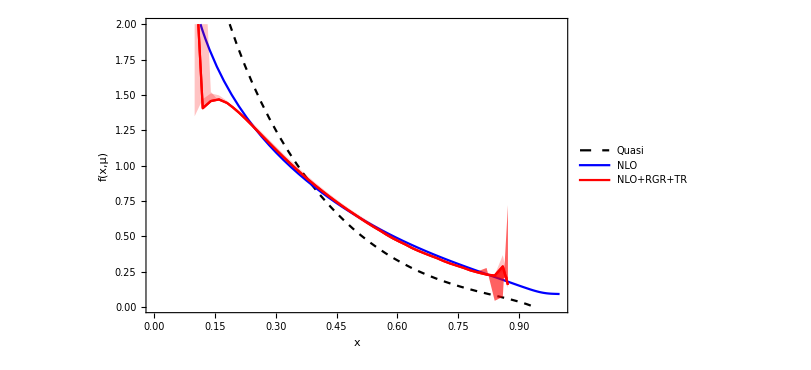

NotebookDirectory::nosv: The notebook mvykd_shm is not saved.

SetDirectory::badfile: The specified argument $Failed should be a valid string or File.

./pics/MCfull6err_add.pdf

```mathematica
fig=Show[
Plot[qint[x],{x,0,1},PlotStyle->{Black,Dashed},
PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["Quasi",20]},{0.7,0.75}]],

Plot[fVint[x],{x,0.10,1},PlotStyle->Blue,PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc,20]},{0.7,0.65}]],

Plot[{PDFRGRTRintls[[2,2]][x],PDFRGRTRintls[[2,1]][x],PDFRGRTRintls[[2,3]][x]},{x,0.10,0.87262},PlotStyle->{Red,Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618^3,Red]}},1->{{3},{Opacity[0.618^3,Red]}}},PlotRange->{{0,1},{0,2}}],

Plot[{PDFRGRTRintls[[2,2]][x],PDFRGRTRintls[[1,2]][x],PDFRGRTRintls[[3,2]][x]},{x,0.10,0.87262},PlotStyle->{Red,Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618,Red]}},1->{{3},{Opacity[0.618,Red]}}},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc<>"+RGR+TR",20]},{0.7,0.55}]],

PlotRange->{{0,1},{0,2}},
FrameLabel->{Style["x",20],Style["f(x,μ)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]

SetDirectory[NotebookDirectory[]];
Export["./pics/MCfull6err_add.pdf",fig]
```

#### μ_i=2|1-|x_i||P_z, μ_i0=2|x_i|P_z, μ_h=2|x_i| P_z, |1-ξ|<γ, γ=0.3~0.5

```mathematica
γls={0.3,0.4,0.5};
xlsf=Table[N[1.0/50 i],{i,5,45}];
```

```mathematica
(*Resummation and variation of r1 and r2*)
PDFRGRTRls=Table[
PrintTemporary[{γ}];
(*Resummation on the inversed matrix*)
Mcut=Table[If[Abs[1-y/x]<γ,1,0],{y,xlist},{x,xlist}];
PDFls={};
PDFls2={};
μils=2*(1-xlsf)*Pz;
μhls=2*xlsf*Pz;
Monitor[
For[i=Length[μhls],i≥1,i--,

ChM=MfixGen[μhls[[i]]];
Quiet[If[μhls[[i]]>μils[[i]],
Hm=Hmgen[μhls[[i]]];
Jmμi=Jmgen[μils[[i]]];
Jmμh=Jmgen[μhls[[i]]];
PJm=PJmgen[μhls[[i]],μils[[i]]];
Strnew=(Mcut*PJm).(Mcut*Jmμi).(Mcut*Hm);
Strnew0=(Mcut*Jmμh).(Mcut*Hm);
PDFlist=Transpose[{xlist,(ChM+Strnew-Strnew0).qV}],
PDFlist=Transpose[{xlist,ChM.qV}]
];];

PDFint=Interpolation[PDFlist];
PDFintsys[x_]:=(PDFint[x]+PDFint[-x])/2;
If[μhls[[i]]>μils[[i]],
PDFCombine[x_]:=PDFintsys[x],
PDFCombine[x_]:=If[Abs[x]≤ xlsf[[i]]+Δx/4,PDFintsys[x],If[xlsf[[i]]+Δx/4<Abs[x]≤ xlsf[[i]]+(3Δx)/4,((xlsf[[i]]+(3Δx)/4)-Abs[x])/(Δx/2)PDFintsys[x]+(Abs[x]-(xlsf[[i]]+Δx/4))/(Δx/2)PDFls2[[Length[μhls]-i]][x],PDFls2[[Length[μhls]-i]][x]]]
];
(*PDFCombine[x_]:=PDFintsys[x];*)

If[PertAcc=="NLO",
AppendTo[PDFls,DGLAPNLOx[PDFCombine,μhls[[i]],μ,Mdglapns0,Mdglapns1,xDGLAP]];AppendTo[PDFls2,DGLAPNLOx[PDFCombine,μhls[[i]],μhls[[i-1]],Mdglapns0,Mdglapns1,xDGLAP]];,
Nothing[]
];

],
Row[{ProgressIndicator[i,{1,Length[μhls]}],i}," "]
];
Table[PDFls[[Length[xlsf]-i+1]][xlsf[[i]]],{i,1,Length[xlsf]}]
,{γ,γls}]
```

{{2.48729,1.40556,1.45641,1.46768,1.44271,1.39907,1.34607,1.28877,1.23001,1.17135,1.11372,1.05763,1.0034,0.951269,0.901299,0.853465,0.807732,0.764018,0.722268,0.68241,0.644364,0.607919,0.572367,0.537538,0.504293,0.472376,0.441229,0.411731,0.388831,0.361628,0.3364,0.313394,0.292652,0.272968,0.258489,0.241732,0.22643,0.216257,0.256019,0.111364,-0.793505},{2.48698,1.40543,1.4563,1.46759,1.44262,1.39899,1.346,1.28871,1.22994,1.17129,1.11366,1.05758,1.00334,0.951214,0.901245,0.853412,0.80768,0.763967,0.72222,0.682365,0.644326,0.605526,0.569136,0.535297,0.498856,0.468903,0.441528,0.410862,0.386954,0.364106,0.342779,0.317201,0.297978,0.27988,0.258773,0.242911,0.22922,0.222573,0.287219,0.0799064,-1.88849},{2.487,1.40544,1.45631,1.46759,1.44263,1.399,1.346,1.28871,1.22995,1.17129,1.11366,1.05758,1.00334,0.951217,0.901248,0.853414,0.807682,0.763969,0.72222,0.682366,0.644328,0.604617,0.569428,0.533813,0.499773,0.472531,0.441885,0.412841,0.390918,0.364382,0.339173,0.320678,0.297929,0.277014,0.262265,0.244771,0.231393,0.232144,0.34501,0.0337684,-3.78716}}

```mathematica
PDFRGRTRintls2=Table[Interpolation[Transpose[Re[{xlsf,PDFRGRTRls[[i]]}]],InterpolationOrder->1],{i,1,Length[γls]}];
```

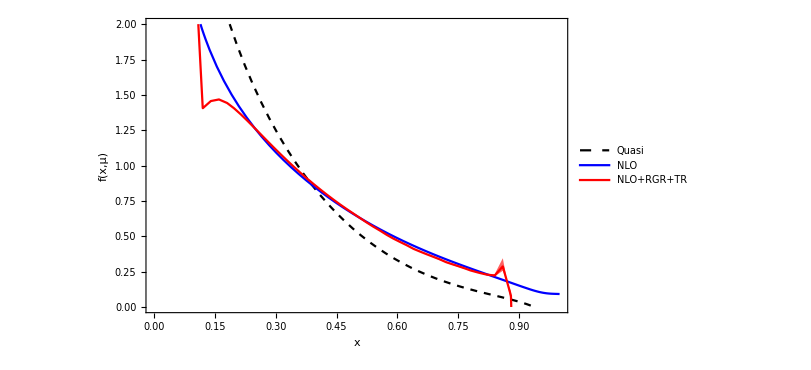

./pics/MCfull6err2_add.pdf

```mathematica
fig=Show[
Plot[qint[x],{x,0,1},PlotStyle->{Black,Dashed},
PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["Quasi",20]},{0.7,0.75}]],

Plot[fVint[x],{x,0.10,1},PlotStyle->Blue,PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc,20]},{0.7,0.65}]],

Plot[{PDFRGRTRintls2[[2]][x],PDFRGRTRintls2[[1]][x],PDFRGRTRintls2[[3]][x]},{x,0.1,0.9},PlotStyle->{Red,Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618,Red]}},1->{{3},{Opacity[0.618,Red]}}},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc<>"+RGR+TR",20]},{0.7,0.55}]],

PlotRange->{{0,1},{0,2}},
FrameLabel->{Style["x",20],Style["f(x,μ)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]

SetDirectory[NotebookDirectory[]];
Export["./pics/MCfull6err2_add.pdf",fig]
```

### Lattice Data Pion Valence Quasi - PDF, Pz=2.4 GeV, zs=0.12fm, λ_L=25

```mathematica
(*
The data is generated by BNL/ANL Collaborations, Gao:2021dbh
Renormalized based on the RGR+LRR method, Zhang:2023bxs
*)
```

```mathematica
Pz=2.42;(*GeV*)
zs=0.12/GeVfm;(*GeV^-1*)
```

```mathematica
qls={{-2.,0.016002760039722924},{-1.99,0.015887574042307555},{-1.98,0.015769298537119177},{-1.97,0.015651054439920053},{-1.96,0.015537982722831821},{-1.95,0.015423266299025878},{-1.94,0.015308569778789256},{-1.93,0.015200690172101513},{-1.92,0.015092782439958905},{-1.91,0.014983672857724693},{-1.9,0.014881632075273703},{-1.89,0.014781557713512535},{-1.88,0.014679191309954872},{-1.87,0.014582315574944368},{-1.86,0.014488105245006669},{-1.85,0.014390766600798445},{-1.84,0.014296907142623355},{-1.83,0.01420485916682258},{-1.82,0.01410753494507068},{-1.81,0.014011103415060112},{-1.8,0.013915408619938001},{-1.79,0.013811171506082395},{-1.78,0.013703147524524447},{-1.77,0.013594015349707306},{-1.76,0.013473429508102076},{-1.75,0.013342886006395369},{-1.74,0.013207008238168012},{-1.73,0.013056394938598094},{-1.72,0.012889749784635144},{-1.71,0.012711939646396466},{-1.7,0.0125142729724254},{-1.69,0.01229379514137114},{-1.68,0.012056125350862472},{-1.67,0.011792707894812581},{-1.66,0.011497863508286438},{-1.65,0.011178491113797755},{-1.64,0.010827960757579191},{-1.63,0.010437097541860375},{-1.62,0.010012071824349579},{-1.61,0.009549543021939829},{-1.6,0.00903878615716052},{-1.59,0.008483740678217305},{-1.58,0.007883005396386943},{-1.57,0.007225722047100147},{-1.56,0.006514720518658194},{-1.55,0.005749885514038617},{-1.54,0.004919208803577744},{-1.53,0.004024581398908007},{-1.52,0.003068867626560029},{-1.51,0.0020392134229877956},{-1.5,0.0009343960999919736},{-1.49,-0.00023965766066175523},{-1.48,-0.0014938616131794646},{-1.47,-0.002832914889942537},{-1.46,-0.004250323357059049},{-1.45,-0.005754117891897975},{-1.44,-0.007350228912705661},{-1.43,-0.009032219288796106},{-1.42,-0.01080675454374976},{-1.41,-0.012680671535971811},{-1.4,-0.014645923568183972},{-1.39,-0.01670717448910158},{-1.38,-0.018873951509977543},{-1.37,-0.02113734631306642},{-1.36,-0.02349724428241852},{-1.35,-0.025965271332858746},{-1.34,-0.02853335566397873},{-1.33,-0.03119765290648614},{-1.32,-0.03396871448763292},{-1.31,-0.03684033673798506},{-1.3,-0.03980452100874363},{-1.29,-0.042870490745547385},{-1.28,-0.04603347064869405},{-1.27,-0.04928144627642734},{-1.26,-0.05262094164796991},{-1.25,-0.05604832210200327},{-1.24,-0.05954764128120552},{-1.23,-0.06312104180876688},{-1.22,-0.06676524390010376},{-1.21,-0.07045988376307998},{-1.2,-0.07420068373481863},{-1.19,-0.07798276113143267},{-1.18,-0.08178023706659528},{-1.17,-0.08557912043016967},{-1.16,-0.08936903731907804},{-1.15,-0.09311519181953949},{-1.14,-0.09678783202103004},{-1.13,-0.10036281856134652},{-1.12,-0.10378732266272922},{-1.11,-0.10700214437268302},{-1.1,-0.10994967911044312},{-1.09,-0.11253384342757554},{-1.08,-0.11462950567447232},{-1.07,-0.11609210469202785},{-1.06,-0.11670837428044217},{-1.05,-0.11618259322942256},{-1.04,-0.114139833233035},{-1.03,-0.11008166892401049},{-1.02,-0.1034119511284729},{-1.01,-0.09362210749035499},{-1.,-0.0805968014089399},{-0.99,-0.06488833068450539},{-0.98,-0.047613468135153984},{-0.97,-0.029919177083612317},{-0.96,-0.01257341119574639},{-0.95,0.004015212541519637},{-0.94,0.019675004405850856},{-0.93,0.03440040782687702},{-0.92,0.04823743097938622},{-0.91,0.06123815267304789},{-0.9,0.07349239403742361},{-0.89,0.08508386272349382},{-0.88,0.09606655424108655},{-0.87,0.10651647753863558},{-0.86,0.1165068384842558},{-0.85,0.12607586518058808},{-0.84,0.1352800155381841},{-0.83,0.14418300837190048},{-0.82,0.15281266484290884},{-0.81,0.1612101290790506},{-0.8,0.16943362868574435},{-0.79,0.17750642920074938},{-0.78,0.18545808779643552},{-0.77,0.19334366916196885},{-0.76,0.20118622607371262},{-0.75,0.20900648024270285},{-0.74,0.2168571781801245},{-0.73,0.22476424625040978},{-0.72,0.23274182302578422},{-0.71,0.24084024236153873},{-0.7,0.249090445177916},{-0.69,0.25750210281350566},{-0.68,0.2661225289182071},{-0.67,0.27498905821103775},{-0.66,0.2841090703946234},{-0.65,0.2935260536337961},{-0.64,0.30328445574619606},{-0.63,0.31339167904969073},{-0.62,0.3238880285181158},{-0.61,0.33482242176638277},{-0.6,0.34620611294425263},{-0.59,0.3580729200281365},{-0.58,0.37048137942831794},{-0.57,0.3834464103680947},{-0.56,0.39699666091264607},{-0.55,0.4111966871379936},{-0.54,0.4260690362389198},{-0.53,0.44163767555509903},{-0.52,0.45797203884704335},{-0.51,0.47510485277658265},{-0.5,0.4930565918617625},{-0.49,0.511900269986981},{-0.48,0.531681244627473},{-0.47,0.5524184969575328},{-0.46,0.574187372618828},{-0.45,0.5970481826153238},{-0.44,0.6210213342295112},{-0.43,0.646183564961867},{-0.42,0.6726123618641973},{-0.41,0.7003335327617658},{-0.4,0.7294247953699666},{-0.39,0.7599833315517526},{-0.38,0.7920452347466175},{-0.37,0.8256901559752229},{-0.36,0.861037152632353},{-0.35,0.8981397049378198},{-0.34,0.9370815983313716},{-0.33,0.978006993930354},{-0.32,1.0209953345737275},{-0.31,1.0661459775523285},{-0.3,1.1136210819824681},{-0.29,1.163541738370499},{-0.28,1.2160162073500604},{-0.27,1.2712646833064385},{-0.26,1.3294527076611735},{-0.25,1.3907180861206685},{-0.24,1.4553252913595562},{-0.23,1.5235255398777838},{-0.22,1.5955146484669809},{-0.21,1.671622615122327},{-0.2,1.7522080084420701},{-0.19,1.8375681202020644},{-0.18,1.92814907756745},{-0.17,2.024468727635753},{-0.16,2.126977804784396},{-0.15,2.236303714606596},{-0.14,2.3532728102399734},{-0.13,2.4784999437998207},{-0.12,2.6128822183235343},{-0.11,2.757626498698002},{-0.1,2.9138689514948846},{-0.09,3.0828194907599316},{-0.08,3.2657706407485256},{-0.07,3.4637620626235472},{-0.06,3.6773282703004404},{-0.05,3.905774079133029},{-0.04,4.144720870520647},{-0.03,4.3831406501832095},{-0.02,4.59911936535436},{-0.01,4.756490618017347},{0,4.815082476451321},{0.01,4.756490618017347},{0.02,4.59911936535436},{0.03,4.3831406501832095},{0.04,4.144720870520647},{0.05,3.905774079133029},{0.06,3.6773282703004404},{0.07,3.4637620626235472},{0.08,3.2657706407485256},{0.09,3.0828194907599316},{0.1,2.9138689514948846},{0.11,2.757626498698002},{0.12,2.6128822183235343},{0.13,2.4784999437998207},{0.14,2.3532728102399734},{0.15,2.236303714606596},{0.16,2.126977804784396},{0.17,2.024468727635753},{0.18,1.92814907756745},{0.19,1.8375681202020644},{0.2,1.7522080084420701},{0.21,1.671622615122327},{0.22,1.5955146484669809},{0.23,1.5235255398777838},{0.24,1.4553252913595562},{0.25,1.3907180861206685},{0.26,1.3294527076611735},{0.27,1.2712646833064385},{0.28,1.2160162073500604},{0.29,1.163541738370499},{0.3,1.1136210819824681},{0.31,1.0661459775523285},{0.32,1.0209953345737275},{0.33,0.978006993930354},{0.34,0.9370815983313716},{0.35,0.8981397049378198},{0.36,0.861037152632353},{0.37,0.8256901559752229},{0.38,0.7920452347466175},{0.39,0.7599833315517526},{0.4,0.7294247953699666},{0.41,0.7003335327617658},{0.42,0.6726123618641973},{0.43,0.646183564961867},{0.44,0.6210213342295112},{0.45,0.5970481826153238},{0.46,0.574187372618828},{0.47,0.5524184969575328},{0.48,0.531681244627473},{0.49,0.511900269986981},{0.5,0.4930565918617625},{0.51,0.47510485277658265},{0.52,0.45797203884704335},{0.53,0.44163767555509903},{0.54,0.4260690362389198},{0.55,0.4111966871379936},{0.56,0.39699666091264607},{0.57,0.3834464103680947},{0.58,0.37048137942831794},{0.59,0.3580729200281365},{0.6,0.34620611294425263},{0.61,0.33482242176638277},{0.62,0.3238880285181158},{0.63,0.31339167904969073},{0.64,0.30328445574619606},{0.65,0.2935260536337961},{0.66,0.2841090703946234},{0.67,0.27498905821103775},{0.68,0.2661225289182071},{0.69,0.25750210281350566},{0.7,0.249090445177916},{0.71,0.24084024236153873},{0.72,0.23274182302578422},{0.73,0.22476424625040978},{0.74,0.2168571781801245},{0.75,0.20900648024270285},{0.76,0.20118622607371262},{0.77,0.19334366916196885},{0.78,0.18545808779643552},{0.79,0.17750642920074938},{0.8,0.16943362868574435},{0.81,0.1612101290790506},{0.82,0.15281266484290884},{0.83,0.14418300837190048},{0.84,0.1352800155381841},{0.85,0.12607586518058808},{0.86,0.1165068384842558},{0.87,0.10651647753863558},{0.88,0.09606655424108655},{0.89,0.08508386272349382},{0.9,0.07349239403742361},{0.91,0.06123815267304789},{0.92,0.04823743097938622},{0.93,0.03440040782687702},{0.94,0.019675004405850856},{0.95,0.004015212541519637},{0.96,-0.01257341119574639},{0.97,-0.029919177083612317},{0.98,-0.047613468135153984},{0.99,-0.06488833068450539},{1.,-0.0805968014089399},{1.01,-0.09362210749035499},{1.02,-0.1034119511284729},{1.03,-0.11008166892401049},{1.04,-0.114139833233035},{1.05,-0.11618259322942256},{1.06,-0.11670837428044217},{1.07,-0.11609210469202785},{1.08,-0.11462950567447232},{1.09,-0.11253384342757554},{1.1,-0.10994967911044312},{1.11,-0.10700214437268302},{1.12,-0.10378732266272922},{1.13,-0.10036281856134652},{1.14,-0.09678783202103004},{1.15,-0.09311519181953949},{1.16,-0.08936903731907804},{1.17,-0.08557912043016967},{1.18,-0.08178023706659528},{1.19,-0.07798276113143267},{1.2,-0.07420068373481863},{1.21,-0.07045988376307998},{1.22,-0.06676524390010376},{1.23,-0.06312104180876688},{1.24,-0.05954764128120552},{1.25,-0.05604832210200327},{1.26,-0.05262094164796991},{1.27,-0.04928144627642734},{1.28,-0.04603347064869405},{1.29,-0.042870490745547385},{1.3,-0.03980452100874363},{1.31,-0.03684033673798506},{1.32,-0.03396871448763292},{1.33,-0.03119765290648614},{1.34,-0.02853335566397873},{1.35,-0.025965271332858746},{1.36,-0.02349724428241852},{1.37,-0.02113734631306642},{1.38,-0.018873951509977543},{1.39,-0.01670717448910158},{1.4,-0.014645923568183972},{1.41,-0.012680671535971811},{1.42,-0.01080675454374976},{1.43,-0.009032219288796106},{1.44,-0.007350228912705661},{1.45,-0.005754117891897975},{1.46,-0.004250323357059049},{1.47,-0.002832914889942537},{1.48,-0.0014938616131794646},{1.49,-0.00023965766066175523},{1.5,0.0009343960999919736},{1.51,0.0020392134229877956},{1.52,0.003068867626560029},{1.53,0.004024581398908007},{1.54,0.004919208803577744},{1.55,0.005749885514038617},{1.56,0.006514720518658194},{1.57,0.007225722047100147},{1.58,0.007883005396386943},{1.59,0.008483740678217305},{1.6,0.00903878615716052},{1.61,0.009549543021939829},{1.62,0.010012071824349579},{1.63,0.010437097541860375},{1.64,0.010827960757579191},{1.65,0.011178491113797755},{1.66,0.011497863508286438},{1.67,0.011792707894812581},{1.68,0.012056125350862472},{1.69,0.01229379514137114},{1.7,0.0125142729724254},{1.71,0.012711939646396466},{1.72,0.012889749784635144},{1.73,0.013056394938598094},{1.74,0.013207008238168012},{1.75,0.013342886006395369},{1.76,0.013473429508102076},{1.77,0.013594015349707306},{1.78,0.013703147524524447},{1.79,0.013811171506082395},{1.8,0.013915408619938001},{1.81,0.014011103415060112},{1.82,0.01410753494507068},{1.83,0.01420485916682258},{1.84,0.014296907142623355},{1.85,0.014390766600798445},{1.86,0.014488105245006669},{1.87,0.014582315574944368},{1.88,0.014679191309954872},{1.89,0.014781557713512535},{1.9,0.014881632075273703},{1.91,0.014983672857724693},{1.92,0.015092782439958905},{1.93,0.015200690172101513},{1.94,0.015308569778789256},{1.95,0.015423266299025878},{1.96,0.015537982722831821},{1.97,0.015651054439920053},{1.98,0.015769298537119177},{1.99,0.015887574042307555},{2.,0.016002760039722924}};
```

### Pz=2.4 GeV, Δx=0.0025, L=3, γ=0.4

```mathematica
μ=2;(*GeV*)(*Factorization Scale*)
PertAcc="NLO";
```

#### Discretization

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

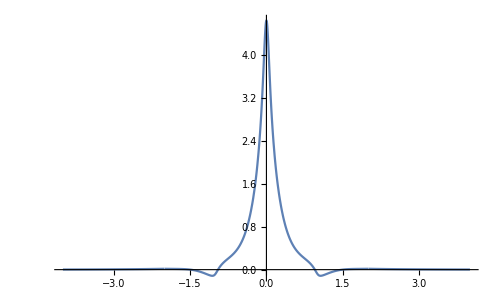

```mathematica
qlsgf=GaussianFilter[qls,{{4,0}}];
qinttest=Interpolation[qlsgf];
ClearAll[qint];
qint[x_]:=If[Abs[x]<2,qinttest[x],qinttest[2]Exp[-(Abs[x]-2)]];
Plot[qint[x],{x,-4,4},PlotRange->All]
```

```mathematica
L=3;
Δx=0.0025;(*Discretization*)
xlist=Join[Table[x,{x,-L,-Δx,Δx}],Table[x,{x,Δx,L,Δx}]];
qV=Table[qint[x],{x,xlist}];
```

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

#### Fixed order results

```mathematica
(*Matrix Elements generation*)
```

```mathematica
If[PertAcc=="NLO",
MCratio1pluswμ=SubMGen[Cratio1pluswμ,xlist,Pz,zs];
MCratio1pluswoμ=SubMGen[Cratio1pluswoμ,xlist,Pz,zs];
MChybrid1plus=SubMGen[Chybrid1plus,xlist,Pz,zs];
MfixGen[μ_]:=Module[{C1},
C1=(αsNLO[[1]][μ]*CF)/(2Pi)((-Log[(μ/Pz)^2])MCratio1pluswμ+MCratio1pluswoμ+MChybrid1plus);
IdentityMatrix[Length[xlist]]-C1
],
Nothing[];
]
```

ToExpression::notstrbox: FEPrivate`FrontEndResourceString[GetFEKernelInit] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

CloudConnect::verr: This version of Mathematica is no longer supported for use with the Wolfram Cloud beginning Wed 1 Jan 2025. Please

```mathematica
(*Calculation*)
```

```mathematica
ChM=MfixGen[μ];
fVfixed=ChM.qV;
(fVfixed+Reverse[fVfixed])/2
fVint=Interpolation[Transpose[{xlist,(fVfixed+Reverse[fVfixed])/2}]];
```

{0.0207847,0.0185887,0.0174864,0.0167485,0.0161927,0.015746,0.0153721,0.0150501,0.014767,0.0145142,0.0142855,0.0140766,0.0138842,0.0137057,0.013539,0.0133828,0.0132355,0.0130962,0.0129639,0.012838,0.0127177,0.0126026,0.0124921,0.0123859,0.0122836,0.0121848,0.0120894,0.011997,0.0119075,0.0118205,0.0117361,0.0116539,0.0115739,0.0114959,0.0114198,0.0113455,0.0112729,0.0112019,0.0111324,0.0110643,0.0109976,0.0109322,0.010868,0.010805,0.0107431,0.0106822,0.0106224,0.0105636,0.0105056,0.0104486,0.0103925,0.0103371,0.0102826,0.0102288,0.0101758,0.0101234,0.0100718,0.0100208,0.00997042,0.00992067,0.00987151,0.00982292,0.00977489,0.00972739,0.00968041,0.00963393,0.00958794,0.00954242,0.00949737,0.00945275,0.00940858,0.00936482,0.00932147,0.00927852,0.00923596,0.00919377,0.00915195,0.00911049,0.00906938,0.00902861,0.00898817,0.00894806,0.00890826,0.00886877,0.00882959,0.00879069,0.00875209,0.00871377,0.00867572,0.00863795,0.00860044,0.00856318,0.00852618,0.00848943,0.00845293,0.00841666,0.00838062,0.00834482,0.00830924,0.00827388,0.00823874,0.00820381,0.00816909,0.00813458,0.00810027,0.00806616,0.00803224,0.00799852,0.00796498,0.00793163,0.00789847,0.00786548,0.00783267,0.00780004,0.00776758,0.00773529,0.00770317,0.00767121,0.00763942,0.00760778,0.0075763,0.00754499,0.00751382,0.00748281,0.00745194,0.00742123,0.00739066,0.00736024,0.00732996,0.00729982,0.00726982,0.00723996,0.00721024,0.00718065,0.0071512,0.00712188,0.00709269,0.00706363,0.00703469,0.00700589,0.00697721,0.00694865,0.00692022,0.00689191,0.00686373,0.00683566,0.00680771,0.00677988,0.00675217,0.00672457,0.00669709,0.00666972,0.00664246,0.00661532,0.00658829,0.00656137,0.00653456,0.00650786,0.00648127,0.00645478,0.00642841,0.00640214,0.00637597,0.00634991,0.00632395,0.0062981,0.00627234,0.00624669,0.00622115,0.0061957,0.00617035,0.00614511,0.00611996,0.00609491,0.00606996,0.0060451,0.00602035,0.00599569,0.00597112,0.00594665,0.00592228,0.005898,0.00587382,0.00584972,0.00582573,0.00580182,0.00577801,0.00575429,0.00573066,0.00570712,0.00568367,0.00566031,0.00563704,0.00561387,0.00559078,0.00556778,0.00554486,0.00552204,0.0054993,0.00547665,0.00545409,0.00543161,0.00540922,0.00538692,0.0053647,0.00534256,0.00532051,0.00529855,0.00527667,0.00525487,0.00523316,0.00521152,0.00518997,0.00516851,0.00514712,0.00512582,0.0051046,0.00508346,0.00506239,0.00504141,0.00502051,0.00499969,0.00497895,0.00495828,0.00493769,0.00491719,0.00489675,0.0048764,0.00485612,0.00483592,0.00481579,0.00479574,0.00477577,0.00475587,0.00473604,0.00471629,0.00469661,0.004677,0.00465746,0.004638,0.00461861,0.00459929,0.00458004,0.00456086,0.00454175,0.0045227,0.00450373,0.00448482,0.00446598,0.00444721,0.0044285,0.00440986,0.00439128,0.00437276,0.00435431,0.00433593,0.0043176,0.00429934,0.00428113,0.00426299,0.0042449,0.00422688,0.00420891,0.004191,0.00417314,0.00415534,0.00413759,0.0041199,0.00410226,0.00408467,0.00406713,0.00404964,0.0040322,0.0040148,0.00399745,0.00398015,0.00396289,0.00394568,0.00392851,0.00391137,0.00389428,0.00387722,0.0038602,0.00384322,0.00382627,0.00380935,0.00379247,0.00377561,0.00375878,0.00374198,0.0037252,0.00370845,0.00369172,0.003675,0.00365831,0.00364163,0.00362496,0.00360831,0.00359166,0.00357503,0.00355839,0.00354177,0.00352514,0.00350851,0.00349188,0.00347524,0.00345859,0.00344194,0.00342526,0.00340857,0.00339186,0.00337513,0.00335837,0.00334158,0.00332476,0.0033079,0.003291,0.00327406,0.00325707,0.00324003,0.00322294,0.00320579,0.00318857,0.00317129,0.00315393,0.0031365,0.00311899,0.00310139,0.00308369,0.0030659,0.00304801,0.00303001,0.0030119,0.00299366,0.00297529,0.0029568,0.00293816,0.00291937,0.00290043,0.00288132,0.00286204,0.00284259,0.00282294,0.0028031,0.00278305,0.00276278,0.00274229,0.00272155,0.00270057,0.00267933,0.00265781,0.00263601,0.0026139,0.00259149,0.00256874,0.00254565,0.0025222,0.00249837,0.00247414,0.0024495,0.00242443,0.00239889,0.00237288,0.00234636,0.00231931,0.00229171,0.00226353,0.00223472,0.00220527,0.00217514,0.00214428,0.00211266,0.00208024,0.00204696,0.00201278,0.00197764,0.00194148,0.00190424,0.00186584,0.0018262,0.00178524,0.00174286,0.00169894,0.00165337,0.00160601,0.0015567,0.00150526,0.00145147,0.0013951,0.00133586,0.0012734,0.00120729,0.001137,0.00106187,0.000981007,0.000893203,0.00079672,0.000688862,0.00056495,0.000415125,0.000207339,0.000247631,0.000249264,0.000234796,0.000210898,0.00018064,0.000145745,0.0001073,0.0000660426,0.0000224812,-0.0000229899,-0.0000700491,-0.000118454,-0.000168029,-0.000218598,-0.000270026,-0.000322204,-0.000375005,-0.000428379,-0.000482259,-0.000536589,-0.000591336,-0.000646444,-0.000701877,-0.0007576,-0.000813638,-0.000869916,-0.00092641,-0.000983098,-0.00103996,-0.00109697,-0.00115414,-0.00121143,-0.00126884,-0.00132637,-0.00138401,-0.00144176,-0.00149967,-0.00155769,-0.00161582,-0.00167405,-0.0017324,-0.00179085,-0.0018494,-0.00190806,-0.0019668,-0.00202566,-0.00208463,-0.00214372,-0.00220299,-0.0022624,-0.00232195,-0.00238166,-0.00244154,-0.0025016,-0.00256183,-0.00262224,-0.00268282,-0.0027436,-0.00280458,-0.00286579,-0.00292727,-0.002989,-0.00305099,-0.00311324,-0.0031758,-0.00323866,-0.00330182,-0.00336529,-0.00342908,-0.00349319,-0.00355767,-0.00362251,-0.00368777,-0.00375343,-0.00381951,-0.00388602,-0.00395302,-0.00402047,-0.0040884,-0.00415682,-0.00422571,-0.00429511,-0.00436504,-0.00443552,-0.00450659,-0.00457824,-0.0046505,-0.00472337,-0.00479694,-0.00487115,-0.00494604,-0.00502161,-0.00509785,-0.00517481,-0.0052525,-0.00533093,-0.00541014,-0.00549012,-0.00557091,-0.00565252,-0.00573502,-0.00581838,-0.00590262,-0.00598774,-0.00607376,-0.0061607,-0.00624857,-0.0063374,-0.00642719,-0.00651798,-0.00660977,-0.00670258,-0.00679649,-0.00689146,-0.00698751,-0.00708464,-0.00718288,-0.00728224,-0.00738274,-0.00748438,-0.00758719,-0.00769118,-0.00779637,-0.00790278,-0.00801048,-0.00811943,-0.00822965,-0.00834114,-0.00845393,-0.00856802,-0.00868342,-0.00880015,-0.0089182,-0.00903761,-0.00915839,-0.00928054,-0.00940416,-0.00952918,-0.00965563,-0.00978352,-0.00991287,-0.0100437,-0.0101759,-0.0103097,-0.0104448,-0.0105815,-0.0107197,-0.0108593,-0.0110006,-0.0111433,-0.0112876,-0.0114334,-0.0115809,-0.0117298,-0.0118804,-0.0120324,-0.0121861,-0.0123413,-0.012498,-0.0126563,-0.0128163,-0.0129778,-0.0131409,-0.0133056,-0.0134719,-0.0136398,-0.0138093,-0.0139803,-0.0141529,-0.0143271,-0.0145028,-0.0146802,-0.014859,-0.0150395,-0.0152215,-0.0154051,-0.0155902,-0.0157769,-0.0159651,-0.0161548,-0.0163459,-0.0165386,-0.0167327,-0.0169283,-0.0171253,-0.0173238,-0.0175237,-0.0177251,-0.0179278,-0.018132,-0.0183375,-0.0185443,-0.0187524,-0.0189618,-0.0191725,-0.0193844,-0.0195975,-0.0198118,-0.0200273,-0.0202439,-0.0204617,-0.0206806,-0.0209006,-0.0211216,-0.0213436,-0.0215665,-0.0217904,-0.0220151,-0.0222407,-0.0224671,-0.0226943,-0.0229222,-0.0231508,-0.0233801,-0.02361,-0.0238405,-0.0240715,-0.024303,-0.0245349,-0.0247672,-0.0249998,-0.0252326,-0.0254656,-0.0256989,-0.0259322,-0.0261656,-0.026399,-0.0266323,-0.0268654,-0.0270984,-0.0273311,-0.0275634,-0.0277953,-0.0280267,-0.0282576,-0.0284879,-0.0287174,-0.0289462,-0.0291742,-0.0294012,-0.0296272,-0.0298521,-0.0300758,-0.0302982,-0.0305192,-0.0307387,-0.0309567,-0.031173,-0.0313875,-0.0316003,-0.031811,-0.0320198,-0.0322263,-0.0324306,-0.0326325,-0.032832,-0.0330286,-0.0332226,-0.0334137,-0.0336019,-0.0337868,-0.0339686,-0.034147,-0.0343219,-0.0344932,-0.0346607,-0.0348243,-0.0349838,-0.035139,-0.0352898,-0.0354361,-0.0355777,-0.0357144,-0.0358461,-0.0359726,-0.0360938,-0.0362094,-0.0363194,-0.0364234,-0.0365214,-0.036613,-0.0366982,-0.0367767,-0.0368483,-0.0369127,-0.0369699,-0.0370195,-0.0370615,-0.0370954,-0.0371212,-0.0371386,-0.0371473,-0.037147,-0.0371375,-0.0371186,-0.03709,-0.0370513,-0.0370024,-0.036943,-0.0368728,-0.0367914,-0.0366986,-0.0365942,-0.0364777,-0.0363487,-0.036207,-0.0360524,-0.0358843,-0.0357023,-0.0355062,-0.0352957,-0.0350704,-0.0348296,-0.0345732,-0.0343008,-0.034012,-0.0337059,-0.0333825,-0.0330414,-0.0326821,-0.0323035,-0.0319057,-0.0314883,-0.0310507,-0.0305918,-0.0301116,-0.0296097,-0.0290853,-0.0285373,-0.0279658,-0.02737,-0.0267494,-0.0261024,-0.0254293,-0.0247294,-0.0240019,-0.0232452,-0.0224595,-0.0216441,-0.0207982,-0.0199196,-0.019009,-0.0180654,-0.0170882,-0.0160743,-0.015025,-0.0139392,-0.0128163,-0.0116525,-0.0104496,-0.00920655,-0.00792255,-0.00659306,-0.0052206,-0.00380416,-0.00234294,-0.000830973,0.000727763,0.00233421,0.00398904,0.00569986,0.00746076,0.00927248,0.0111353,0.013059,0.0150348,0.0170631,0.0191435,0.0212878,0.0234839,0.0257311,0.028028,0.0303874,0.0327936,0.0352448,0.037738,0.0402827,0.0428632,0.0454757,0.0481156,0.0507822,0.0534662,0.0561619,0.0588635,0.0615525,0.0642344,0.0669026,0.0695514,0.0721401,0.0746962,0.0772137,0.0796885,0.082063,0.0843854,0.0866522,0.0888628,0.0909571,0.0929928,0.0949702,0.0968926,0.0987171,0.100492,0.102222,0.103912,0.105552,0.107163,0.108752,0.110326,0.111903,0.113477,0.115055,0.116642,0.118273,0.119924,0.121597,0.123295,0.125059,0.126854,0.128681,0.130542,0.132469,0.134429,0.136424,0.138451,0.140532,0.142644,0.144785,0.146954,0.149161,0.151392,0.153646,0.15592,0.158219,0.160536,0.162868,0.165214,0.167575,0.169948,0.17233,0.174721,0.17712,0.179526,0.181937,0.184353,0.186773,0.189195,0.191621,0.194048,0.196476,0.198906,0.201335,0.203765,0.206194,0.208622,0.21105,0.213477,0.215902,0.218326,0.220749,0.22317,0.225589,0.228006,0.230423,0.232837,0.23525,0.237661,0.24007,0.242479,0.244885,0.247291,0.249695,0.252099,0.254502,0.256904,0.259305,0.261706,0.264107,0.266508,0.268908,0.27131,0.273711,0.276113,0.278517,0.280921,0.283327,0.285734,0.288143,0.290554,0.292967,0.295382,0.2978,0.30022,0.302644,0.305071,0.307502,0.309936,0.312374,0.314817,0.317264,0.319715,0.322172,0.324633,0.3271,0.329572,0.332051,0.334535,0.337026,0.339523,0.342027,0.344538,0.347056,0.349582,0.352115,0.354656,0.357206,0.359764,0.36233,0.364905,0.36749,0.370084,0.372687,0.375301,0.377924,0.380558,0.383202,0.385857,0.388522,0.391199,0.393888,0.396588,0.3993,0.402024,0.40476,0.40751,0.410272,0.413046,0.415835,0.418637,0.421452,0.424281,0.427125,0.429983,0.432855,0.435743,0.438645,0.441563,0.444497,0.447446,0.450411,0.453392,0.45639,0.459405,0.462436,0.465485,0.46855,0.471634,0.474735,0.477854,0.480992,0.484148,0.487323,0.490517,0.49373,0.496962,0.500214,0.503486,0.506777,0.510089,0.513422,0.516776,0.52015,0.523545,0.526963,0.530402,0.533862,0.537345,0.54085,0.544378,0.547929,0.551502,0.555099,0.55872,0.562364,0.566033,0.569725,0.573443,0.577185,0.580952,0.584744,0.588562,0.592405,0.596274,0.60017,0.604092,0.608041,0.612017,0.61602,0.620051,0.624109,0.628196,0.632311,0.636454,0.640626,0.644827,0.649058,0.653318,0.657608,0.661928,0.666279,0.670661,0.675073,0.679517,0.683993,0.688501,0.693041,0.697613,0.702218,0.706856,0.711528,0.716234,0.720974,0.725748,0.730557,0.735401,0.740281,0.745196,0.750148,0.755136,0.76016,0.765222,0.770322,0.775459,0.780635,0.78585,0.791104,0.796397,0.80173,0.807104,0.812518,0.817973,0.823471,0.82901,0.834591,0.840215,0.845883,0.851595,0.857351,0.863152,0.868999,0.874892,0.880831,0.886816,0.89285,0.898931,0.905061,0.911239,0.917469,0.923748,0.930078,0.93646,0.942895,0.949382,0.955923,0.962517,0.969168,0.975874,0.982636,0.989455,0.996333,1.00327,1.01027,1.01732,1.02444,1.03162,1.03886,1.04617,1.05355,1.06098,1.06849,1.07606,1.08371,1.09142,1.09921,1.10707,1.115,1.12301,1.13109,1.13925,1.14749,1.15581,1.16422,1.1727,1.18127,1.18993,1.19868,1.20751,1.21644,1.22547,1.23458,1.2438,1.25311,1.26253,1.27205,1.28167,1.2914,1.30125,1.3112,1.32127,1.33147,1.34178,1.35222,1.36278,1.37348,1.3843,1.39527,1.40637,1.41762,1.42902,1.44057,1.45228,1.46415,1.47619,1.48839,1.50077,1.51334,1.52609,1.53902,1.55216,1.56551,1.57907,1.59284,1.60684,1.62108,1.63556,1.65029,1.66528,1.68055,1.69609,1.71193,1.72807,1.74454,1.76133,1.77847,1.79596,1.81384,1.83212,1.8508,1.86991,1.88949,1.90954,1.93009,1.95117,1.97281,1.99504,2.0179,2.04142,2.06564,2.09061,2.11639,2.14302,2.17054,2.19906,2.22865,2.2594,2.2913,2.32457,2.35933,2.39571,2.43362,2.47352,2.51559,2.56003,2.60664,2.65624,2.70911,2.7656,2.82542,2.88987,2.95941,3.03464,3.11538,3.20343,3.2996,3.40491,3.51986,3.64674,3.7872,3.94334,4.11767,4.31388,4.53664,4.79246,5.09132,5.44722,5.88446,6.44688,7.22571,8.45142,11.0424,11.0424,8.45142,7.22571,6.44688,5.88446,5.44722,5.09132,4.79246,4.53664,4.31388,4.11767,3.94334,3.7872,3.64674,3.51986,3.40491,3.2996,3.20343,3.11538,3.03464,2.95941,2.88987,2.82542,2.7656,2.70911,2.65624,2.60664,2.56003,2.51559,2.47352,2.43362,2.39571,2.35933,2.32457,2.2913,2.2594,2.22865,2.19906,2.17054,2.14302,2.11639,2.09061,2.06564,2.04142,2.0179,1.99504,1.97281,1.95117,1.93009,1.90954,1.88949,1.86991,1.8508,1.83212,1.81384,1.79596,1.77847,1.76133,1.74454,1.72807,1.71193,1.69609,1.68055,1.66528,1.65029,1.63556,1.62108,1.60684,1.59284,1.57907,1.56551,1.55216,1.53902,1.52609,1.51334,1.50077,1.48839,1.47619,1.46415,1.45228,1.44057,1.42902,1.41762,1.40637,1.39527,1.3843,1.37348,1.36278,1.35222,1.34178,1.33147,1.32127,1.3112,1.30125,1.2914,1.28167,1.27205,1.26253,1.25311,1.2438,1.23458,1.22547,1.21644,1.20751,1.19868,1.18993,1.18127,1.1727,1.16422,1.15581,1.14749,1.13925,1.13109,1.12301,1.115,1.10707,1.09921,1.09142,1.08371,1.07606,1.06849,1.06098,1.05355,1.04617,1.03886,1.03162,1.02444,1.01732,1.01027,1.00327,0.996333,0.989455,0.982636,0.975874,0.969168,0.962517,0.955923,0.949382,0.942895,0.93646,0.930078,0.923748,0.917469,0.911239,0.905061,0.898931,0.89285,0.886816,0.880831,0.874892,0.868999,0.863152,0.857351,0.851595,0.845883,0.840215,0.834591,0.82901,0.823471,0.817973,0.812518,0.807104,0.80173,0.796397,0.791104,0.78585,0.780635,0.775459,0.770322,0.765222,0.76016,0.755136,0.750148,0.745196,0.740281,0.735401,0.730557,0.725748,0.720974,0.716234,0.711528,0.706856,0.702218,0.697613,0.693041,0.688501,0.683993,0.679517,0.675073,0.670661,0.666279,0.661928,0.657608,0.653318,0.649058,0.644827,0.640626,0.636454,0.632311,0.628196,0.624109,0.620051,0.61602,0.612017,0.608041,0.604092,0.60017,0.596274,0.592405,0.588562,0.584744,0.580952,0.577185,0.573443,0.569725,0.566033,0.562364,0.55872,0.555099,0.551502,0.547929,0.544378,0.54085,0.537345,0.533862,0.530402,0.526963,0.523545,0.52015,0.516776,0.513422,0.510089,0.506777,0.503486,0.500214,0.496962,0.49373,0.490517,0.487323,0.484148,0.480992,0.477854,0.474735,0.471634,0.46855,0.465485,0.462436,0.459405,0.45639,0.453392,0.450411,0.447446,0.444497,0.441563,0.438645,0.435743,0.432855,0.429983,0.427125,0.424281,0.421452,0.418637,0.415835,0.413046,0.410272,0.40751,0.40476,0.402024,0.3993,0.396588,0.393888,0.391199,0.388522,0.385857,0.383202,0.380558,0.377924,0.375301,0.372687,0.370084,0.36749,0.364905,0.36233,0.359764,0.357206,0.354656,0.352115,0.349582,0.347056,0.344538,0.342027,0.339523,0.337026,0.334535,0.332051,0.329572,0.3271,0.324633,0.322172,0.319715,0.317264,0.314817,0.312374,0.309936,0.307502,0.305071,0.302644,0.30022,0.2978,0.295382,0.292967,0.290554,0.288143,0.285734,0.283327,0.280921,0.278517,0.276113,0.273711,0.27131,0.268908,0.266508,0.264107,0.261706,0.259305,0.256904,0.254502,0.252099,0.249695,0.247291,0.244885,0.242479,0.24007,0.237661,0.23525,0.232837,0.230423,0.228006,0.225589,0.22317,0.220749,0.218326,0.215902,0.213477,0.21105,0.208622,0.206194,0.203765,0.201335,0.198906,0.196476,0.194048,0.191621,0.189195,0.186773,0.184353,0.181937,0.179526,0.17712,0.174721,0.17233,0.169948,0.167575,0.165214,0.162868,0.160536,0.158219,0.15592,0.153646,0.151392,0.149161,0.146954,0.144785,0.142644,0.140532,0.138451,0.136424,0.134429,0.132469,0.130542,0.128681,0.126854,0.125059,0.123295,0.121597,0.119924,0.118273,0.116642,0.115055,0.113477,0.111903,0.110326,0.108752,0.107163,0.105552,0.103912,0.102222,0.100492,0.0987171,0.0968926,0.0949702,0.0929928,0.0909571,0.0888628,0.0866522,0.0843854,0.082063,0.0796885,0.0772137,0.0746962,0.0721401,0.0695514,0.0669026,0.0642344,0.0615525,0.0588635,0.0561619,0.0534662,0.0507822,0.0481156,0.0454757,0.0428632,0.0402827,0.037738,0.0352448,0.0327936,0.0303874,0.028028,0.0257311,0.0234839,0.0212878,0.0191435,0.0170631,0.0150348,0.013059,0.0111353,0.00927248,0.00746076,0.00569986,0.00398904,0.00233421,0.000727763,-0.000830973,-0.00234294,-0.00380416,-0.0052206,-0.00659306,-0.00792255,-0.00920655,-0.0104496,-0.0116525,-0.0128163,-0.0139392,-0.015025,-0.0160743,-0.0170882,-0.0180654,-0.019009,-0.0199196,-0.0207982,-0.0216441,-0.0224595,-0.0232452,-0.0240019,-0.0247294,-0.0254293,-0.0261024,-0.0267494,-0.02737,-0.0279658,-0.0285373,-0.0290853,-0.0296097,-0.0301116,-0.0305918,-0.0310507,-0.0314883,-0.0319057,-0.0323035,-0.0326821,-0.0330414,-0.0333825,-0.0337059,-0.034012,-0.0343008,-0.0345732,-0.0348296,-0.0350704,-0.0352957,-0.0355062,-0.0357023,-0.0358843,-0.0360524,-0.036207,-0.0363487,-0.0364777,-0.0365942,-0.0366986,-0.0367914,-0.0368728,-0.036943,-0.0370024,-0.0370513,-0.03709,-0.0371186,-0.0371375,-0.037147,-0.0371473,-0.0371386,-0.0371212,-0.0370954,-0.0370615,-0.0370195,-0.0369699,-0.0369127,-0.0368483,-0.0367767,-0.0366982,-0.036613,-0.0365214,-0.0364234,-0.0363194,-0.0362094,-0.0360938,-0.0359726,-0.0358461,-0.0357144,-0.0355777,-0.0354361,-0.0352898,-0.035139,-0.0349838,-0.0348243,-0.0346607,-0.0344932,-0.0343219,-0.034147,-0.0339686,-0.0337868,-0.0336019,-0.0334137,-0.0332226,-0.0330286,-0.032832,-0.0326325,-0.0324306,-0.0322263,-0.0320198,-0.031811,-0.0316003,-0.0313875,-0.031173,-0.0309567,-0.0307387,-0.0305192,-0.0302982,-0.0300758,-0.0298521,-0.0296272,-0.0294012,-0.0291742,-0.0289462,-0.0287174,-0.0284879,-0.0282576,-0.0280267,-0.0277953,-0.0275634,-0.0273311,-0.0270984,-0.0268654,-0.0266323,-0.026399,-0.0261656,-0.0259322,-0.0256989,-0.0254656,-0.0252326,-0.0249998,-0.0247672,-0.0245349,-0.024303,-0.0240715,-0.0238405,-0.02361,-0.0233801,-0.0231508,-0.0229222,-0.0226943,-0.0224671,-0.0222407,-0.0220151,-0.0217904,-0.0215665,-0.0213436,-0.0211216,-0.0209006,-0.0206806,-0.0204617,-0.0202439,-0.0200273,-0.0198118,-0.0195975,-0.0193844,-0.0191725,-0.0189618,-0.0187524,-0.0185443,-0.0183375,-0.018132,-0.0179278,-0.0177251,-0.0175237,-0.0173238,-0.0171253,-0.0169283,-0.0167327,-0.0165386,-0.0163459,-0.0161548,-0.0159651,-0.0157769,-0.0155902,-0.0154051,-0.0152215,-0.0150395,-0.014859,-0.0146802,-0.0145028,-0.0143271,-0.0141529,-0.0139803,-0.0138093,-0.0136398,-0.0134719,-0.0133056,-0.0131409,-0.0129778,-0.0128163,-0.0126563,-0.012498,-0.0123413,-0.0121861,-0.0120324,-0.0118804,-0.0117298,-0.0115809,-0.0114334,-0.0112876,-0.0111433,-0.0110006,-0.0108593,-0.0107197,-0.0105815,-0.0104448,-0.0103097,-0.0101759,-0.0100437,-0.00991287,-0.00978352,-0.00965563,-0.00952918,-0.00940416,-0.00928054,-0.00915839,-0.00903761,-0.0089182,-0.00880015,-0.00868342,-0.00856802,-0.00845393,-0.00834114,-0.00822965,-0.00811943,-0.00801048,-0.00790278,-0.00779637,-0.00769118,-0.00758719,-0.00748438,-0.00738274,-0.00728224,-0.00718288,-0.00708464,-0.00698751,-0.00689146,-0.00679649,-0.00670258,-0.00660977,-0.00651798,-0.00642719,-0.0063374,-0.00624857,-0.0061607,-0.00607376,-0.00598774,-0.00590262,-0.00581838,-0.00573502,-0.00565252,-0.00557091,-0.00549012,-0.00541014,-0.00533093,-0.0052525,-0.00517481,-0.00509785,-0.00502161,-0.00494604,-0.00487115,-0.00479694,-0.00472337,-0.0046505,-0.00457824,-0.00450659,-0.00443552,-0.00436504,-0.00429511,-0.00422571,-0.00415682,-0.0040884,-0.00402047,-0.00395302,-0.00388602,-0.00381951,-0.00375343,-0.00368777,-0.00362251,-0.00355767,-0.00349319,-0.00342908,-0.00336529,-0.00330182,-0.00323866,-0.0031758,-0.00311324,-0.00305099,-0.002989,-0.00292727,-0.00286579,-0.00280458,-0.0027436,-0.00268282,-0.00262224,-0.00256183,-0.0025016,-0.00244154,-0.00238166,-0.00232195,-0.0022624,-0.00220299,-0.00214372,-0.00208463,-0.00202566,-0.0019668,-0.00190806,-0.0018494,-0.00179085,-0.0017324,-0.00167405,-0.00161582,-0.00155769,-0.00149967,-0.00144176,-0.00138401,-0.00132637,-0.00126884,-0.00121143,-0.00115414,-0.00109697,-0.00103996,-0.000983098,-0.00092641,-0.000869916,-0.000813638,-0.0007576,-0.000701877,-0.000646444,-0.000591336,-0.000536589,-0.000482259,-0.000428379,-0.000375005,-0.000322204,-0.000270026,-0.000218598,-0.000168029,-0.000118454,-0.0000700491,-0.0000229899,0.0000224812,0.0000660426,0.0001073,0.000145745,0.00018064,0.000210898,0.000234796,0.000249264,0.000247631,0.000207339,0.000415125,0.00056495,0.000688862,0.00079672,0.000893203,0.000981007,0.00106187,0.001137,0.00120729,0.0012734,0.00133586,0.0013951,0.00145147,0.00150526,0.0015567,0.00160601,0.00165337,0.00169894,0.00174286,0.00178524,0.0018262,0.00186584,0.00190424,0.00194148,0.00197764,0.00201278,0.00204696,0.00208024,0.00211266,0.00214428,0.00217514,0.00220527,0.00223472,0.00226353,0.00229171,0.00231931,0.00234636,0.00237288,0.00239889,0.00242443,0.0024495,0.00247414,0.00249837,0.0025222,0.00254565,0.00256874,0.00259149,0.0026139,0.00263601,0.00265781,0.00267933,0.00270057,0.00272155,0.00274229,0.00276278,0.00278305,0.0028031,0.00282294,0.00284259,0.00286204,0.00288132,0.00290043,0.00291937,0.00293816,0.0029568,0.00297529,0.00299366,0.0030119,0.00303001,0.00304801,0.0030659,0.00308369,0.00310139,0.00311899,0.0031365,0.00315393,0.00317129,0.00318857,0.00320579,0.00322294,0.00324003,0.00325707,0.00327406,0.003291,0.0033079,0.00332476,0.00334158,0.00335837,0.00337513,0.00339186,0.00340857,0.00342526,0.00344194,0.00345859,0.00347524,0.00349188,0.00350851,0.00352514,0.00354177,0.00355839,0.00357503,0.00359166,0.00360831,0.00362496,0.00364163,0.00365831,0.003675,0.00369172,0.00370845,0.0037252,0.00374198,0.00375878,0.00377561,0.00379247,0.00380935,0.00382627,0.00384322,0.0038602,0.00387722,0.00389428,0.00391137,0.00392851,0.00394568,0.00396289,0.00398015,0.00399745,0.0040148,0.0040322,0.00404964,0.00406713,0.00408467,0.00410226,0.0041199,0.00413759,0.00415534,0.00417314,0.004191,0.00420891,0.00422688,0.0042449,0.00426299,0.00428113,0.00429934,0.0043176,0.00433593,0.00435431,0.00437276,0.00439128,0.00440986,0.0044285,0.00444721,0.00446598,0.00448482,0.00450373,0.0045227,0.00454175,0.00456086,0.00458004,0.00459929,0.00461861,0.004638,0.00465746,0.004677,0.00469661,0.00471629,0.00473604,0.00475587,0.00477577,0.00479574,0.00481579,0.00483592,0.00485612,0.0048764,0.00489675,0.00491719,0.00493769,0.00495828,0.00497895,0.00499969,0.00502051,0.00504141,0.00506239,0.00508346,0.0051046,0.00512582,0.00514712,0.00516851,0.00518997,0.00521152,0.00523316,0.00525487,0.00527667,0.00529855,0.00532051,0.00534256,0.0053647,0.00538692,0.00540922,0.00543161,0.00545409,0.00547665,0.0054993,0.00552204,0.00554486,0.00556778,0.00559078,0.00561387,0.00563704,0.00566031,0.00568367,0.00570712,0.00573066,0.00575429,0.00577801,0.00580182,0.00582573,0.00584972,0.00587382,0.005898,0.00592228,0.00594665,0.00597112,0.00599569,0.00602035,0.0060451,0.00606996,0.00609491,0.00611996,0.00614511,0.00617035,0.0061957,0.00622115,0.00624669,0.00627234,0.0062981,0.00632395,0.00634991,0.00637597,0.00640214,0.00642841,0.00645478,0.00648127,0.00650786,0.00653456,0.00656137,0.00658829,0.00661532,0.00664246,0.00666972,0.00669709,0.00672457,0.00675217,0.00677988,0.00680771,0.00683566,0.00686373,0.00689191,0.00692022,0.00694865,0.00697721,0.00700589,0.00703469,0.00706363,0.00709269,0.00712188,0.0071512,0.00718065,0.00721024,0.00723996,0.00726982,0.00729982,0.00732996,0.00736024,0.00739066,0.00742123,0.00745194,0.00748281,0.00751382,0.00754499,0.0075763,0.00760778,0.00763942,0.00767121,0.00770317,0.00773529,0.00776758,0.00780004,0.00783267,0.00786548,0.00789847,0.00793163,0.00796498,0.00799852,0.00803224,0.00806616,0.00810027,0.00813458,0.00816909,0.00820381,0.00823874,0.00827388,0.00830924,0.00834482,0.00838062,0.00841666,0.00845293,0.00848943,0.00852618,0.00856318,0.00860044,0.00863795,0.00867572,0.00871377,0.00875209,0.00879069,0.00882959,0.00886877,0.00890826,0.00894806,0.00898817,0.00902861,0.00906938,0.00911049,0.00915195,0.00919377,0.00923596,0.00927852,0.00932147,0.00936482,0.00940858,0.00945275,0.00949737,0.00954242,0.00958794,0.00963393,0.00968041,0.00972739,0.00977489,0.00982292,0.00987151,0.00992067,0.00997042,0.0100208,0.0100718,0.0101234,0.0101758,0.0102288,0.0102826,0.0103371,0.0103925,0.0104486,0.0105056,0.0105636,0.0106224,0.0106822,0.0107431,0.010805,0.010868,0.0109322,0.0109976,0.0110643,0.0111324,0.0112019,0.0112729,0.0113455,0.0114198,0.0114959,0.0115739,0.0116539,0.0117361,0.0118205,0.0119075,0.011997,0.0120894,0.0121848,0.0122836,0.0123859,0.0124921,0.0126026,0.0127177,0.012838,0.0129639,0.0130962,0.0132355,0.0133828,0.013539,0.0137057,0.0138842,0.0140766,0.0142855,0.0145142,0.014767,0.0150501,0.0153721,0.015746,0.0161927,0.0167485,0.0174864,0.0185887,0.0207847}

#### DGLAP log resummation

```mathematica
(*Generating xlsf and μhls*)
xlsf=Table[N[1.0/50 i],{i,4,50}];
μhls=2*xlsf*Pz;

(*Generating DGLAP kernels*)
xDGLAP=Table[N[1.0/100 i],{i,1,100}];
If[PertAcc=="NLO",
{Mdglapns0,Mdglapns1}=DGLAPNLOMGen[xDGLAP];,
Nothing[]
];
```

```mathematica
(*Calculation*)
PDFls={};
PDFls2={};
Monitor[
For[i=Length[μhls],i≥1,i--,

ChM=MfixGen[μhls[[i]]];
PDFlist=Transpose[{xlist,ChM.qV}];

PDFint=Interpolation[PDFlist];
PDFintsys[x_]:=(PDFint[x]+PDFint[-x])/2;
PDFCombine[x_]:=If[Abs[x]≤ xlsf[[i]]+Δx/4,PDFintsys[x],If[xlsf[[i]]+Δx/4<Abs[x]≤ xlsf[[i]]+(3Δx)/4,((xlsf[[i]]+(3Δx)/4)-Abs[x])/(Δx/2)PDFintsys[x]+(Abs[x]-(xlsf[[i]]+Δx/4))/(Δx/2)PDFls2[[Length[μhls]-i]][x],PDFls2[[Length[μhls]-i]][x]]];
(*PDFCombine[x_]:=PDFintsys[x];*)

If[PertAcc=="NLO",
AppendTo[PDFls,DGLAPNLOx[PDFCombine,μhls[[i]],μ,Mdglapns0,Mdglapns1,xDGLAP]];AppendTo[PDFls2,DGLAPNLOx[PDFCombine,μhls[[i]],μhls[[i-1]],Mdglapns0,Mdglapns1,xDGLAP]];,
Nothing[]
];

PrintTemporary[{xlsf[[i]],PDFls[[Length[PDFls]]][xlsf[[i]]]}];
],
Row[{ProgressIndicator[i,{1,Length[μhls]}],i}," "]
]

PDFRGR=Table[PDFls[[Length[xlsf]-i+1]][xlsf[[i]]],{i,1,Length[xlsf]}]
```

{2.93117,1.53093,1.62355,1.62341,1.57875,1.51433,1.44201,1.36762,1.29406,1.22283,1.15462,1.09003,1.02909,0.971705,0.917737,0.867035,0.819433,0.774732,0.732723,0.693312,0.656324,0.621597,0.588966,0.558273,0.529362,0.502066,0.476245,0.451733,0.428371,0.405996,0.384442,0.363532,0.343102,0.32296,0.302914,0.282765,0.262304,0.241321,0.21963,0.19707,0.173647,0.149604,0.125869,0.104798,0.0909191,0.0898916,0.118777}

```mathematica
PDFRGRint=Interpolation[Transpose[Re[{xlsf,PDFRGR}]],InterpolationOrder->2];
```

#### DGLAP+Threshold log

```mathematica
(*Generating xlist and μhls*)
xlsf=Table[N[1.0/50 i],{i,4,46}];
μhls=2*xlsf*Pz;
μils=2*(1-xlsf)*Pz;
```

```mathematica
(*Prepare for hard kernel*)
J1dnm=Jdngen[J1dn,xlist];

If[PertAcc=="NLO",
Hmgen[μ_]:=Module[{},
Hgen[J1dnm,ANLO,HNLO,xlist,μ,Pz,zs]
],
Nothing[]
]
```

```mathematica
(*Prepare for soft function*)
J2ηpm=Jηpgen[J2ηp,xlist];
J2dnm=Jdngen[J2dn,xlist];
Jls0=Jls0gen[J2ηpm,J2dnm];
JLTls0=JLTls0gen[xlist];

If[PertAcc=="NLO",
Jmgen[μ_]:=Module[{},
Jgen[Jls0,JLTls0,JcoeNLO,xlist,μ,Pz,zs]
];
PJmgen[μf_,μi_]:=Module[{},
PJgen[J2ηpm,J2dnm,SNLO,aΓNLO,aJNLO,xlist,μf,μi,Pz,zs]
];,
Nothing[]
]
```

```mathematica
(*Threshold cut*)
Mcut=Table[If[Abs[1-y/x]<0.4,1,0],{y,xlist},{x,xlist}];
```

```mathematica
(*Calculations*)
PDFls={};
PDFls2={};
Monitor[
For[i=Length[μhls],i≥1,i--,

ChM=MfixGen[μhls[[i]]];
If[μhls[[i]]>μils[[i]],
Hm=Hmgen[μhls[[i]]];
Jmμi=Jmgen[μils[[i]]];
Jmμh=Jmgen[μhls[[i]]];
PJm=PJmgen[μhls[[i]],μils[[i]]];
Strnew=(Mcut*PJm).(Mcut*Jmμi).(Mcut*Hm);
Strnew0=(Mcut*Jmμh).(Mcut*Hm);
PDFlist=Transpose[{xlist,(ChM+Strnew-Strnew0).qV}],
PDFlist=Transpose[{xlist,ChM.qV}]
];


PDFint=Interpolation[PDFlist];
PDFintsys[x_]:=(PDFint[x]+PDFint[-x])/2;
If[μhls[[i]]>μils[[i]],
PDFCombine[x_]:=PDFintsys[x],
PDFCombine[x_]:=If[Abs[x]≤ xlsf[[i]]+Δx/4,PDFintsys[x],If[xlsf[[i]]+Δx/4<Abs[x]≤ xlsf[[i]]+(3Δx)/4,((xlsf[[i]]+(3Δx)/4)-Abs[x])/(Δx/2)PDFintsys[x]+(Abs[x]-(xlsf[[i]]+Δx/4))/(Δx/2)PDFls2[[Length[μhls]-i]][x],PDFls2[[Length[μhls]-i]][x]]]
];
(*PDFCombine[x_]:=PDFintsys[x];*)


If[PertAcc=="NLO",
AppendTo[PDFls,DGLAPNLOx[PDFCombine,μhls[[i]],μ,Mdglapns0,Mdglapns1,xDGLAP]];AppendTo[PDFls2,DGLAPNLOx[PDFCombine,μhls[[i]],μhls[[i-1]],Mdglapns0,Mdglapns1,xDGLAP]];,
Nothing[]
];


PrintTemporary[{xlsf[[i]],PDFls[[Length[PDFls]]][xlsf[[i]]]}];
],
Row[{ProgressIndicator[i,{1,Length[μhls]}],i}," "]
]

PDFRGRTR=Table[PDFls[[Length[xlsf]-i+1]][xlsf[[i]]],{i,1,Length[xlsf]}]
```

{2.93512,1.53222,1.62456,1.62427,1.57949,1.51498,1.44257,1.36811,1.2945,1.2232,1.15495,1.09031,1.02932,0.971884,0.917868,0.867118,0.819466,0.774715,0.732654,0.693193,0.656168,0.621529,0.58598,0.553719,0.524275,0.492632,0.467052,0.443922,0.417747,0.397337,0.377937,0.36029,0.337754,0.320712,0.303567,0.282681,0.265877,0.249436,0.234744,0.220231,0.239775,0.0957228,-3.9473}

```mathematica
PDFRGRTRint=Interpolation[Transpose[Re[{xlsf,PDFRGRTR}]],InterpolationOrder->1];
```

#### CVs Plot

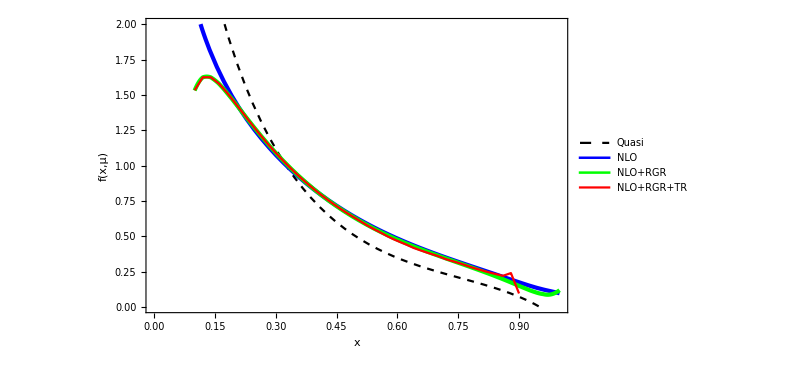

```mathematica
fig=Show[
Plot[qint[x],{x,0,1},PlotStyle->{Black,Dashed},
PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["Quasi",20]},{0.7,0.75}]],

Plot[fVint[x],{x,0.10,1},PlotStyle->{Blue,Thickness[0.005]},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc,20]},{0.7,0.65}]],

Plot[PDFRGRint[x],{x,0.10,1},PlotStyle->{Green,Thickness[0.005]},PlotRange->All,PlotLegends->Placed[{Style[PertAcc<>"+RGR",20]},{0.7,0.55}]],

Plot[PDFRGRTRint[x],{x,0.10,0.9},PlotStyle->Red,PlotRange->All,PlotLegends->Placed[{Style[PertAcc<>"+RGR+TR",20]},{0.7,0.45}]],

PlotRange->{{0,1},{0,2}},
FrameLabel->{Style["x",20],Style["f(x,μ)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]

(*SetDirectory[NotebookDirectory[]];
Export["./pics/MCfull6NLO_add.pdf",fig]*)
```

#### μ_i=2|1-|x_i||P_z r1, μ_h=2|x_i| P_z r2, r1,r2=0.8~1.2

```mathematica
r1ls={1.2,1,0.8};
r2ls={1.2,1,0.8};
xlsf=Table[N[1.0/50 i],{i,4,46}];
Mcut=Table[If[Abs[1-y/x]<0.4,1,0],{y,xlist},{x,xlist}];
```

```mathematica
(*Resummation and variation of r1 and r2*)
PDFRGRTRls=Table[
PrintTemporary[{r1,r2}];
(*Resummation on the inversed matrix*)
PDFls={};
PDFls2={};
μils=2*(1-xlsf)*Pz*r1;
μhls=2*xlsf*Pz*r2;
Monitor[
For[i=Length[μhls],i≥1,i--,

ChM=MfixGen[μhls[[i]]];
Quiet[If[μhls[[i]]>μils[[i]],
Hm=Hmgen[μhls[[i]]];
Jmμi=Jmgen[μils[[i]]];
Jmμh=Jmgen[μhls[[i]]];
PJm=PJmgen[μhls[[i]],μils[[i]]];
Strnew=(Mcut*PJm).(Mcut*Jmμi).(Mcut*Hm);
Strnew0=(Mcut*Jmμh).(Mcut*Hm);
PDFlist=Transpose[{xlist,(ChM+Strnew-Strnew0).qV}],
PDFlist=Transpose[{xlist,ChM.qV}]
];];

ClearAll[PDFint,PDFintsys,PDFCombine];
PDFint=Interpolation[PDFlist];
PDFintsys[x_]:=(PDFint[x]+PDFint[-x])/2;
If[μhls[[i]]>μils[[i]],
PDFCombine[x_]:=PDFintsys[x],
PDFCombine[x_]:=If[Abs[x]≤ xlsf[[i]]+Δx/4,PDFintsys[x],If[xlsf[[i]]+Δx/4<Abs[x]≤ xlsf[[i]]+(3Δx)/4,((xlsf[[i]]+(3Δx)/4)-Abs[x])/(Δx/2)PDFintsys[x]+(Abs[x]-(xlsf[[i]]+Δx/4))/(Δx/2)PDFls2[[Length[μhls]-i]][x],PDFls2[[Length[μhls]-i]][x]]]
];
(*PDFCombine[x_]:=PDFintsys[x];*)

If[PertAcc=="NLO",
AppendTo[PDFls,DGLAPNLOx[PDFCombine,μhls[[i]],μ,Mdglapns0,Mdglapns1,xDGLAP]];AppendTo[PDFls2,DGLAPNLOx[PDFCombine,μhls[[i]],μhls[[i-1]],Mdglapns0,Mdglapns1,xDGLAP]];,
Nothing[]
];

],
Row[{ProgressIndicator[i,{1,Length[μhls]}],i}," "]
];
Table[PDFls[[Length[xlsf]-i+1]][xlsf[[i]]],{i,1,Length[xlsf]}]
,{r1,r1ls},{r2,r2ls}]
```

General::munfl: 0.000416667^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.043913^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0913636^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.143333^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.2005^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.263684^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00125104^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0448216^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0923567^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.144423^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.201702^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.265016^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00208681^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0457317^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0933515^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.145515^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.202906^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.26635^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.273438^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0390625^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.234375^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.078125^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.195312^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.117188^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.262355^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.199301^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.142245^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0903724^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.21665×10^-306 0.00165345 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.261029^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.198104^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.14116^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0893829^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0430061^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.52745×10^-308 0.00165345 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.259706^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.196909^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.140076^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0883953^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0421007^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.30916^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.0411969^604.796 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.000416667^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.043913^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0913636^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.143333^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.2005^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.263684^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00125104^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0448216^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0923567^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.144423^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.201702^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.265016^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00208681^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0457317^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0933515^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.145515^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.202906^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.26635^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.0390625^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.273438^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.078125^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.234375^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.117188^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.195312^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1.26266×10^-306 0.00165354 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.262355^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.199301^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.142245^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.81327×10^-308 0.00165354 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.261029^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.198104^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.14116^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0903724^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0430061^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.30916^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.259706^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.196909^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.140076^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0893829^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0421007^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.0883953^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0411969^604.764 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.000416667^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.043913^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0913636^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.143333^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.2005^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.263684^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00125104^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0448216^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0923567^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.144423^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.201702^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.265016^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00208681^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0457317^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0933515^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.145515^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.202906^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.26635^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.0390625^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.273438^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.078125^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.234375^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.117188^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.195312^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.262355^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.199301^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.142245^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0903724^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0430061^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.3307×10^-306 0.00165366 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.261029^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.198104^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.14116^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0893829^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0421007^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.236×10^-308 0.00165366 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.259706^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.196909^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.140076^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0883953^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0411969^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.30916^604.719 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{{1.44646,1.63702,1.68278,1.65308,1.59178,1.51792,1.44003,1.36219,1.28622,1.21387,1.14541,1.08084,1.02009,0.963019,0.909384,0.85904,0.81184,0.767589,0.726108,0.687223,0.650768,0.616747,0.582362,0.551379,0.523485,0.491822,0.467291,0.445294,0.41894,0.399383,0.380732,0.364408,0.340959,0.324917,0.309455,0.288631,0.271831,0.254822,0.238996,0.217848,0.205414,0.242838,0.08664},{2.9345,1.53202,1.6244,1.62414,1.57937,1.51488,1.44248,1.36803,1.29443,1.22314,1.1549,1.09026,1.02929,0.971856,0.917848,0.867106,0.819462,0.774717,0.732661,0.693201,0.65616,0.621375,0.588692,0.558019,0.527655,0.497556,0.470966,0.446839,0.420908,0.399697,0.379679,0.361436,0.3389,0.321508,0.304707,0.284217,0.26673,0.249214,0.232649,0.212744,0.199773,0.219258,0.0875542},{-5.93789×10^6,2.63299,1.59769,1.6022,1.57674,1.52307,1.45656,1.3851,1.31283,1.24192,1.17351,1.10815,1.04612,0.98758,0.932506,0.880699,0.832019,0.786275,0.743315,0.702974,0.665085,0.629489,0.596018,0.56446,0.534722,0.506672,0.480215,0.453038,0.427004,0.403624,0.381781,0.361422,0.339386,0.320639,0.302533,0.282401,0.264182,0.246113,0.228791,0.209838,0.195832,0.201597,0.0889043}},{{1.44711,1.63749,1.68317,1.65341,1.59207,1.51817,1.44024,1.36237,1.28637,1.214,1.14551,1.08091,1.02013,0.963027,0.909354,0.858965,0.811708,0.767383,0.725812,0.686144,0.649242,0.611009,0.578438,0.548059,0.521112,0.487843,0.464236,0.443161,0.416556,0.397734,0.379644,0.363905,0.340444,0.324718,0.30891,0.287738,0.271693,0.255931,0.242358,0.228198,0.267019,0.100769,-8.99799},{2.93512,1.53222,1.62456,1.62427,1.57949,1.51498,1.44257,1.36811,1.2945,1.2232,1.15495,1.09031,1.02932,0.971884,0.917868,0.867118,0.819466,0.774715,0.732654,0.693193,0.656168,0.621529,0.58598,0.553719,0.524275,0.492632,0.467052,0.443922,0.417747,0.397337,0.377937,0.36029,0.337754,0.320712,0.303567,0.282681,0.265877,0.249436,0.234744,0.220231,0.239775,0.0957228,-3.9473},{-6.03302×10^6,2.63448,1.59823,1.60263,1.57712,1.5234,1.45686,1.38537,1.31308,1.24216,1.17372,1.10835,1.0463,0.987749,0.932661,0.88084,0.832146,0.786387,0.743411,0.703051,0.66514,0.629517,0.596011,0.564412,0.53404,0.503094,0.474893,0.449129,0.422893,0.40039,0.379236,0.359479,0.337478,0.31911,0.300655,0.280069,0.262437,0.245234,0.229344,0.21415,0.218898,0.0889531,-2.21528}},{{1.44745,1.63774,1.68337,1.65358,1.59222,1.51829,1.44035,1.36246,1.28645,1.21406,1.14556,1.08095,1.02015,0.96303,0.909342,0.858941,0.811699,0.766635,0.720389,0.6814,0.645835,0.604443,0.573063,0.543525,0.517681,0.483256,0.460736,0.44074,0.414232,0.396302,0.378611,0.362865,0.339052,0.323458,0.308709,0.289038,0.275421,0.264915,0.268711,3.41147,0.119569,-8.5305,0.12082},{2.93718,1.53291,1.6251,1.62473,1.57989,1.51534,1.44289,1.36839,1.29475,1.22343,1.15515,1.09048,1.02947,0.972004,0.91796,0.867179,0.819492,0.774702,0.732627,0.690863,0.652416,0.612805,0.579229,0.547878,0.519501,0.486758,0.462345,0.440364,0.414278,0.394813,0.375859,0.358204,0.335272,0.318334,0.30214,0.282501,0.267669,0.255272,0.252894,0.48266,0.116256,-3.98712,0.122013},{-6.06042×10^6,2.63493,1.59839,1.60275,1.57722,1.52349,1.45694,1.38544,1.31314,1.24221,1.17377,1.10839,1.04633,0.987776,0.932682,0.880854,0.832153,0.786387,0.743403,0.703034,0.665113,0.629473,0.592873,0.558885,0.527533,0.495629,0.468688,0.444158,0.418043,0.396547,0.375902,0.356138,0.333722,0.315411,0.297767,0.278138,0.261975,0.247569,0.23943,0.30067,0.114516,-2.26412,0.124338}}}

```mathematica
PDFRGRTRintls=Table[Interpolation[Transpose[Re[{xlsf,PDFRGRTRls[[i,j]]}]],InterpolationOrder->1],{i,1,Length[r1ls]},{j,1,Length[r2ls]}];
```

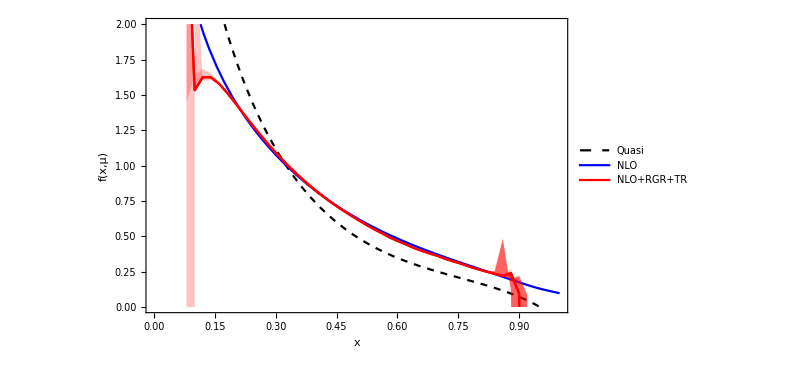

```mathematica
fig=Show[
Plot[qint[x],{x,0,1},PlotStyle->{Black,Dashed},
PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["Quasi",20]},{0.7,0.75}]],

Plot[fVint[x],{x,0.10,1},PlotStyle->Blue,PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc,20]},{0.7,0.65}]],

Plot[{PDFRGRTRintls[[2,2]][x],PDFRGRTRintls[[2,1]][x],PDFRGRTRintls[[2,3]][x]},{x,0.08,0.92},PlotStyle->{Red,Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618^3,Red]}},1->{{3},{Opacity[0.618^3,Red]}}},PlotRange->{{0,1},{0,2}}],

Plot[{PDFRGRTRintls[[2,2]][x],PDFRGRTRintls[[1,2]][x],PDFRGRTRintls[[3,2]][x]},{x,0.08,0.92},PlotStyle->{Red,Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618,Red]}},1->{{3},{Opacity[0.618,Red]}}},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc<>"+RGR+TR",20]},{0.7,0.55}]],

PlotRange->{{0,1},{0,2}},
FrameLabel->{Style["x",20],Style["f(x,μ)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]

(*SetDirectory[NotebookDirectory[]];
Export["./pics/MCfull6err_add.pdf",fig]*)
```

#### μ_i=2|1-|x_i||P_z, μ_i0=2|x_i|P_z, μ_h=2|x_i| P_z, |1-ξ|<γ, γ=0.3~0.5

```mathematica
γls={0.3,0.4,0.5};
xlsf=Table[N[1.0/50 i],{i,4,46}];
```

```mathematica
(*Resummation and variation of r1 and r2*)
PDFRGRTRls=Table[
PrintTemporary[{γ}];
(*Resummation on the inversed matrix*)
Mcut=Table[If[Abs[1-y/x]<γ,1,0],{y,xlist},{x,xlist}];
PDFls={};
PDFls2={};
μils=2*(1-xlsf)*Pz;
μhls=2*xlsf*Pz;
Monitor[
For[i=Length[μhls],i≥1,i--,

ChM=MfixGen[μhls[[i]]];
Quiet[If[μhls[[i]]>μils[[i]],
Hm=Hmgen[μhls[[i]]];
Jmμi=Jmgen[μils[[i]]];
Jmμh=Jmgen[μhls[[i]]];
PJm=PJmgen[μhls[[i]],μils[[i]]];
Strnew=(Mcut*PJm).(Mcut*Jmμi).(Mcut*Hm);
Strnew0=(Mcut*Jmμh).(Mcut*Hm);
PDFlist=Transpose[{xlist,(ChM+Strnew-Strnew0).qV}],
PDFlist=Transpose[{xlist,ChM.qV}]
];];

PDFint=Interpolation[PDFlist];
PDFintsys[x_]:=(PDFint[x]+PDFint[-x])/2;
If[μhls[[i]]>μils[[i]],
PDFCombine[x_]:=PDFintsys[x],
PDFCombine[x_]:=If[Abs[x]≤ xlsf[[i]]+Δx/4,PDFintsys[x],If[xlsf[[i]]+Δx/4<Abs[x]≤ xlsf[[i]]+(3Δx)/4,((xlsf[[i]]+(3Δx)/4)-Abs[x])/(Δx/2)PDFintsys[x]+(Abs[x]-(xlsf[[i]]+Δx/4))/(Δx/2)PDFls2[[Length[μhls]-i]][x],PDFls2[[Length[μhls]-i]][x]]]
];
(*PDFCombine[x_]:=PDFintsys[x];*)

If[PertAcc=="NLO",
AppendTo[PDFls,DGLAPNLOx[PDFCombine,μhls[[i]],μ,Mdglapns0,Mdglapns1,xDGLAP]];AppendTo[PDFls2,DGLAPNLOx[PDFCombine,μhls[[i]],μhls[[i-1]],Mdglapns0,Mdglapns1,xDGLAP]];,
Nothing[]
];

],
Row[{ProgressIndicator[i,{1,Length[μhls]}],i}," "]
];
Table[PDFls[[Length[xlsf]-i+1]][xlsf[[i]]],{i,1,Length[xlsf]}]
,{γ,γls}]
```

{{2.93538,1.53231,1.62463,1.62433,1.57954,1.51503,1.44262,1.36815,1.29453,1.22324,1.15498,1.09033,1.02935,0.971904,0.917884,0.86713,0.819472,0.774712,0.732638,0.693156,0.65609,0.621316,0.588148,0.556777,0.526332,0.497453,0.469913,0.443056,0.41749,0.398633,0.375925,0.355234,0.335967,0.317888,0.299044,0.284853,0.267374,0.249757,0.233377,0.220092,0.23292,0.102907,-2.00594},{2.93512,1.53222,1.62456,1.62427,1.57949,1.51498,1.44257,1.36811,1.2945,1.2232,1.15495,1.09031,1.02932,0.971884,0.917868,0.867118,0.819466,0.774715,0.732654,0.693193,0.656168,0.621529,0.58598,0.553719,0.524275,0.492632,0.467052,0.443922,0.417747,0.397337,0.377937,0.36029,0.337754,0.320712,0.303567,0.282681,0.265877,0.249436,0.234744,0.220231,0.239775,0.0957228,-3.9473},{2.93514,1.53223,1.62457,1.62428,1.57949,1.51498,1.44258,1.36812,1.2945,1.22321,1.15495,1.09031,1.02932,0.971885,0.917869,0.867119,0.819467,0.774715,0.732653,0.693191,0.656164,0.621511,0.585286,0.554263,0.523058,0.493563,0.470304,0.443876,0.419019,0.400569,0.377716,0.356255,0.340643,0.320197,0.300253,0.285374,0.266192,0.248337,0.235632,0.223741,0.246434,0.104391,-1.11077}}

```mathematica
PDFRGRTRintls2=Table[Interpolation[Transpose[Re[{xlsf,PDFRGRTRls[[i]]}]],InterpolationOrder->1],{i,1,Length[γls]}];
```

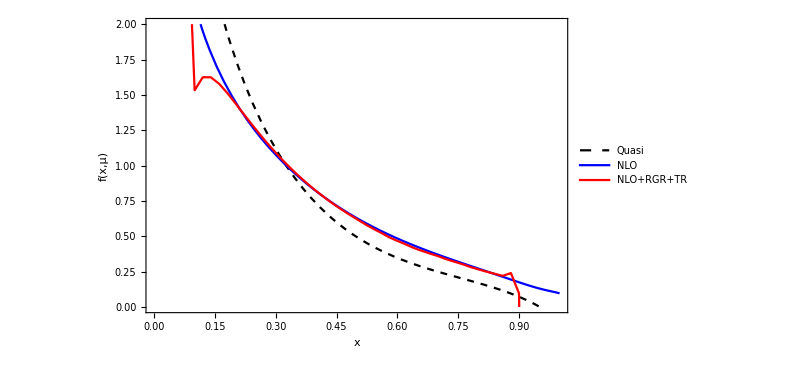

```mathematica
fig=Show[
Plot[qint[x],{x,0,1},PlotStyle->{Black,Dashed},
PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["Quasi",20]},{0.7,0.75}]],

Plot[fVint[x],{x,0.10,1},PlotStyle->Blue,PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc,20]},{0.7,0.65}]],

Plot[{PDFRGRTRintls2[[2]][x],PDFRGRTRintls2[[1]][x],PDFRGRTRintls2[[3]][x]},{x,0.08,0.92},PlotStyle->{Red,Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618,Red]}},1->{{3},{Opacity[0.618,Red]}}},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc<>"+RGR+TR",20]},{0.7,0.55}]],

PlotRange->{{0,1},{0,2}},
FrameLabel->{Style["x",20],Style["f(x,μ)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]

(*SetDirectory[NotebookDirectory[]];
Export["./pics/MCfull6err2_add.pdf",fig]*)
```

### Compare Pz=1.9 GeV and Pz=2.4 GeV, √(σ_h^2+σ_i^2), L=3

#### Data

```mathematica
PDFRGRTRls19={{{1.3467996518428786,1.4681419489731502,1.509241443386508,1.4958391582421522,1.4558010656679137,1.402826177373952,1.343950674903559,1.2829107528343362,1.2216909017919546,1.1613135038978475,1.1025136266675755,1.0459134573705822,0.9915769141533246,0.9395229195831142,0.8897360809514534,0.8421444312765097,0.7966917046844358,0.7532610438998287,0.7117902033086799,0.6722421876868607,0.634584582064467,0.5965972905041276,0.5616187822647409,0.5293969739258167,0.4928155525219778,0.46391333348381303,0.4376219017370061,0.4065500843097786,0.38344259351612153,0.3614970378897441,0.3419718818486321,0.31590977916530877,0.29732740373163946,0.2797300447755983,0.2575509069124838,0.24122902752645106,0.2257949068698581,0.21271415474329403,0.19959896266151664,0.245929040328498,0.08184903194385551},{2.485005081503087,1.4046907729959754,1.4557158291942636,1.4670771798614417,1.4421684242352566,1.3985810154633376,1.34562345486278,1.288365972173637,1.2296272297023745,1.1709985814954105,1.1133915211310743,1.057329365268923,1.0031137615109313,0.9510049846853174,0.901055597830699,0.8532421320987965,0.8075321901856047,0.7638431032851503,0.7221234291560866,0.6823041864629067,0.6443154793619399,0.6080653849080951,0.5734439980281864,0.5392098737724246,0.5045635870154256,0.4735763552297303,0.4451647766958857,0.41475797159692623,0.38989261179101703,0.36652317817996605,0.3450714325446493,0.31987500491648513,0.3001131804557724,0.28124032581888314,0.25935749290041804,0.2421946244862067,0.22596066840249862,0.21182580701084064,0.198796589458327,0.2263098620624731,0.07139430977198455},{9.270921629147358*^6,2.7314345423323365,1.5195282617661774,1.4551246710859043,1.4440231640275374,1.4097174458203774,1.3626120998601503,1.3087164490741583,1.2517429384331515,1.193879773629715,1.1363933617320423,1.0800704108038652,1.0253350490402315,0.9724335912356358,0.9215001389212375,0.8726077690166147,0.8258702196376712,0.7812639451172325,0.7386428653969601,0.6979438653566302,0.6590852779750508,0.6220308834499044,0.5866929470725231,0.5529991841272638,0.5208714816975415,0.49021248019164554,0.45913844896593153,0.4287013324530103,0.40132317798426764,0.37585243957065706,0.3520865745689015,0.32716018685536835,0.30574811059131946,0.28525726809925345,0.2633768768212463,0.24504232733572487,0.22773595870112495,0.21233917246566159,0.1990499997208716,0.2133600227648599,0.05576632084418362}},{{1.3484328313705383,1.4693964145355158,1.5103126837054777,1.4967778532472662,1.4566359671756632,1.4035757847475374,1.3446276619501494,1.2835244219580957,1.2222476296155336,1.16181735800111,1.1029668891751285,1.0463162020449097,0.9919275217682728,0.9398172334407102,0.8899665202206029,0.8422988243789185,0.7967494127177116,0.7531877548806879,0.7110492914318086,0.6709376792641834,0.6284974128457251,0.592229249374636,0.5578942055940427,0.5264806846203643,0.4880434932810811,0.460068274059752,0.4347243208092409,0.40339143725557103,0.38116041656897304,0.3596627182356621,0.34024351464913005,0.3137879989863189,0.2957209466781051,0.2789137785505366,0.25757902661249693,0.24266437886053355,0.23013014310964475,0.22616620210159044,0.3669407896430617,0.09052699771323432,-2.512380771479854},{2.4869773445281185,1.4054345684705,1.4563045870446032,1.4675883496209576,1.4426233503426764,1.3989913404022591,1.3459968857388813,1.288707996881424,1.2299418114490936,1.171288825449605,1.113659656234851,1.057576975373116,1.0033418671133199,0.9512140047671026,0.9012453942853872,0.8534119563742913,0.8076804666801588,0.7639673590437731,0.7222195612501711,0.6823653077237146,0.644326306654306,0.6055260878538757,0.5691360608381585,0.5352970660991363,0.4988562604275064,0.46890317389517033,0.4415281827011606,0.4108620835331967,0.38695391948634356,0.3641062225216392,0.34277859756163775,0.3172005676908754,0.29797776239451823,0.2798803173411989,0.25877311087047644,0.24291120833362137,0.2292197861498737,0.2225726548803893,0.28721882979554264,0.0799063687269465,-1.8884863458773549},{9.178498018858016*^6,2.7379575712315107,1.5210353025749983,1.456254237697612,1.4450009709103746,1.4106014605142976,1.3634253924453872,1.309473580353102,1.2524542300440296,1.1945530145725374,1.1370348389126688,1.0806848680689212,1.025926546440134,0.9730055263754006,0.9220553967336014,0.8731488312675226,0.8263992661825134,0.7817828398475394,0.7391533065904249,0.6984475471489751,0.6595842975247315,0.6225270528553123,0.5871810254967715,0.5531116320377779,0.5174986006434442,0.48474015830258554,0.4545663314378421,0.42391064764822306,0.39758423136388865,0.37272875150030416,0.34910035716139104,0.3238269897454188,0.3029767668107062,0.28323411398485315,0.2620532428084015,0.24489089948988835,0.2297320448743481,0.22022862355055667,0.2504004179163178,0.0640524152779377,-1.4246329771476467}},{{1.3496359116893295,1.4703205128621462,1.5111019282851137,1.4974694796955572,1.4572511224637341,1.4041281074031842,1.3451265300400055,1.2839767541077574,1.2226582096707719,1.1621892845664628,1.103301951647344,1.0466145423838453,0.9921879512082742,0.9400364183372037,0.8901376533893984,0.8424057465632907,0.7962830812019394,0.7470788730001212,0.7054013787759742,0.6667857982727454,0.62063574132377,0.5858123134268862,0.5524310307524035,0.5220472284789006,0.48230872196524993,0.4551039056222826,0.43024224099296,0.3985003256386692,0.37692633924364966,0.3562334397544444,0.3380772534723745,0.31258255123346584,0.2959852864348623,0.2812896564893709,0.26381061908515496,0.2585298251427144,0.3007480111596869,0.08522152755708351,0.07717882477918267,1.0579299618152371,0.16710648775862452},{2.492038320715153,1.4073875361431658,1.4578595603581028,1.4689454392891625,1.443839309832058,1.4000974407479314,1.3470139284835856,1.2896508802798394,1.2308213808152264,1.1721137000690887,1.1144361440548227,1.0583096869229047,1.004033889845872,0.9518666684392608,0.9018580951278293,0.8539810411922762,0.8081942428438474,0.7643618504600102,0.7206490766491404,0.6788139963735954,0.6349594347439249,0.5976875659270933,0.562347027437299,0.5295130912109611,0.49183510585259604,0.4627638004471041,0.4359599261655267,0.4048700209229126,0.3816665920207571,0.35965015157310476,0.3395465088845295,0.3148430263429977,0.2969922541157884,0.28075394433010276,0.26283092921045315,0.2545303864998919,0.2759679829939944,0.043760687887736335,0.0716614927654211,1.1009684970217324,0.1656992723555646},{9.116008030478425*^6,2.7423602685958195,1.5220208749741198,1.4569886852022125,1.4456343806697192,1.4111718986460358,1.3639477314891675,1.3099571218887311,1.2529054982879453,1.1949768566247594,1.1374350723420414,1.0810642463730427,1.026287266705073,0.9733491892765124,0.9223830008740745,0.8734606477450994,0.8266944890124148,0.7820585814586715,0.7394017344249628,0.6986438175187193,0.6595739516149344,0.6199401203689489,0.5815301702192075,0.5455884745069983,0.5089012580375372,0.477151995647698,0.447663998775945,0.4166129876684524,0.391052811425722,0.3670663299281522,0.344606990155018,0.3201358690343405,0.30055240335581423,0.28240086698397976,0.26374431155592915,0.25226216654460626,0.2593034919683255,-0.09131350649075436,0.06559506965828071,1.161007563981439,0.1647640664875977}}};
```

```mathematica
PDFRGRTRls24={{{1.4464560996282974,1.637015033743667,1.6827761266222732,1.653075882182051,1.591784519666141,1.5179181160729986,1.440027634521712,1.3621907588130209,1.2862176205981117,1.2138735942862802,1.1454103018499162,1.0808425555992136,1.0200937117067554,0.9630187318552458,0.9093839517189798,0.8590403107147974,0.8118398056755509,0.7675887172464809,0.7261083588511827,0.6872228850829565,0.6507684682253234,0.6167468457422599,0.5823616046130139,0.5513786724545339,0.5234846345212794,0.49182193904263083,0.46729125909207747,0.4452938642712498,0.41894046216101,0.39938329672136436,0.38073209493759186,0.3644084845795085,0.3409588532922611,0.324916750437776,0.30945546159856335,0.2886311908836542,0.2718308097654043,0.2548219392525161,0.2389961410130668,0.2178482733956648,0.2054137102818199,0.24283836811012097,0.08663998231472246},{2.9344961826283207,1.5320195044745835,1.6244019336603188,1.6241355126488508,1.5793727440494882,1.5148776498674636,1.4424840419053113,1.3680346599052877,1.2944277983365713,1.2231437375833876,1.1548984345335893,1.0902648470121918,1.0292862639085592,0.9718564766173103,0.9178481544024032,0.86710609908226,0.8194615029295592,0.7747170981745096,0.7326613945477287,0.6932012554171575,0.6561598135977696,0.6213754962589754,0.588691564764577,0.5580193687850036,0.527655024329302,0.49755633045238296,0.4709662214069247,0.4468386541316415,0.42090803133766097,0.39969749438520674,0.37967929589037286,0.36143570308376155,0.3388999133339867,0.321507966951056,0.30470655081196657,0.28421690049606285,0.2667301067538625,0.2492137747867862,0.2326488209169322,0.21274354927136882,0.1997732326553299,0.21925757406983537,0.08755418571488921},{-5.937887152597518*^6,2.6329944779179395,1.5976864395830364,1.6022007677938093,1.576744640238113,1.5230681199004739,1.4565574759465696,1.3850985941085605,1.3128311802765493,1.2419237446648326,1.173507402896061,1.1081494217898726,1.0461151856347457,0.9875800303546902,0.9325058295313985,0.8806987725903124,0.8320186634412041,0.7862746028823647,0.74331535478522,0.7029739136084489,0.6650854752050985,0.6294894791393997,0.5960177681665086,0.5644598468558786,0.5347215421032877,0.5066723893372075,0.4802154253921228,0.4530382261875004,0.4270044914936504,0.40362402989332163,0.38178138004785017,0.36142174125247045,0.3393859483004482,0.3206388570758224,0.3025329695053902,0.28240091665157674,0.26418238064731175,0.24611290336169644,0.22879053046934703,0.20983774143281922,0.19583196662067326,0.20159650787638866,0.08890431789164283}},{{1.4471134090680393,1.63749300821173,1.6831708325135646,1.6534102846339345,1.5920711274262849,1.5181650316847626,1.4402402207523959,1.362372611883443,1.2863709879691134,1.2139995782596134,1.1455090292531453,1.0809132822395378,1.0201345735977918,0.9630265322002156,0.9093540714067267,0.8589654251946419,0.811708366415897,0.7673829065587423,0.7258123000121512,0.6861436494726664,0.6492420654983996,0.6110092554071967,0.5784383797749585,0.5480591947877504,0.521112471502766,0.48784253448319087,0.46423635989048906,0.4431608002711052,0.41655615448760475,0.3977343095809245,0.37964417435560505,0.36390459008093984,0.34044391326418916,0.32471766273645464,0.30891039914830226,0.2877378881190158,0.27169287460125324,0.2559314935437014,0.24235798797678726,0.22819771088905919,0.2670190178122294,0.10076854997929816,-8.997985889899812},{2.9351201514268115,1.5322227413174774,1.6245612963774554,1.6242705590250706,1.5794893768456826,1.5149792952823555,1.4425729650631973,1.3681125057356445,1.2944957416479135,1.2232026354797543,1.154948902407278,1.090307289021059,1.0293209291699497,0.9718835259732046,0.9178676581909045,0.8671181047562885,0.8194661469058445,0.7747148833807423,0.7326538613081589,0.693193069853478,0.6561683753888806,0.6215294191540407,0.5859801076939302,0.5537188478904617,0.52427496446858,0.4926316031390539,0.4670519098663237,0.44392242791467024,0.41774660153560533,0.39733705839614686,0.37793658142591485,0.36028960398975246,0.337753836046506,0.3207115826490831,0.30356691078113396,0.282681376936927,0.2658769834149518,0.24943585767135518,0.23474411026200231,0.2202308958960298,0.23977535169871814,0.09572279853928523,-3.9472966412572292},{-6.033017810499675*^6,2.634478034076454,1.5982336045360748,1.6026332263644716,1.5771200361920081,1.5234022876013693,1.45685899699181,1.3853731438544303,1.3130827323879093,1.2421553531752403,1.1737212927834682,1.1083472454346195,1.0462981288065516,0.9877488768527238,0.9326609408019005,0.880840129449985,0.8321457999815243,0.7863866882143667,0.7434109309289564,0.703050752510002,0.665140259880902,0.6295172668072977,0.5960112383154074,0.5644119087704905,0.5340397534535332,0.5030938083519988,0.4748928666303925,0.44912860965165813,0.4228928248870216,0.40039027898552965,0.37923589839802363,0.3594785762286947,0.3374778912467595,0.3191095926428898,0.3006547992640076,0.28006906461968617,0.26243661376093286,0.24523421530828898,0.22934403626141012,0.2141497363511777,0.21889844625809649,0.08895311328646469,-2.2152786419870893}},{{1.4474504317892443,1.6377375280310584,1.6833722863049903,1.6535802615741448,1.5922159695199727,1.5182888854970904,1.4403458724929978,1.36246198067075,1.2864453460536223,1.2140596707289792,1.145555190233747,1.0809455318310741,1.0201525993459808,0.9630298131218514,0.9093424294145065,0.8589410265391777,0.811699180908956,0.7666353635894724,0.7203893688764089,0.6813997765576175,0.6458353836840687,0.6044427889556819,0.573062662755588,0.5435245472028651,0.5176812906609305,0.48325575316366004,0.4607360209370148,0.44073993703300135,0.4142315753304523,0.3963019666270299,0.3786113557966225,0.36286465904564785,0.33905218034236334,0.3234579862472534,0.30870911762097253,0.2890376520611908,0.2754208513169669,0.26491458496482095,0.2687105938114736,3.411474572442617,0.11956861112553215,-8.530500644916755,0.12081979791361216},{2.937184419707696,1.532912379969803,1.6251049717155672,1.6247341282838021,1.579893451525032,1.5153357934761282,1.4428896659586814,1.3683949580810992,1.2947477773309657,1.223426882129746,1.1551470070879986,1.0904799560441507,1.0294680084539962,0.9720041368328445,0.9179599178647024,0.8671790396993729,0.8194917172374695,0.7747018665511207,0.7326273603473772,0.6908632558144295,0.6524156462339813,0.6128049527072457,0.5792287738422541,0.547877686035226,0.5195008750330656,0.48675808559863276,0.4623445881143312,0.44036393600568174,0.4142783128046389,0.39481290598906155,0.3758587136845708,0.3582044787798849,0.33527224216951135,0.3183336026121376,0.302140312065311,0.2825007382868389,0.26766889186805476,0.25527156116719074,0.25289425860795894,0.48265995360190833,0.11625602526793696,-3.987116175505242,0.12201327470304207},{-6.060421555818027*^6,2.634928687335853,1.5983895302996374,1.602754423593318,1.577223683687135,1.5234927390247526,1.4569385387495128,1.3854432661508558,1.3131444615766084,1.242209454199305,1.1737682964607405,1.108387513745428,1.0463318814031624,0.9877762067611231,0.9326818116201034,0.8808543825032478,0.832153148506383,0.7863866922907959,0.7434029539660045,0.7030338665436411,0.6651128906989018,0.6294726524228272,0.5928732552157362,0.558884955809883,0.5275326534959651,0.4956294857405508,0.468687877722513,0.44415777672400625,0.41804252369503364,0.3965472591379329,0.3759024610890603,0.35613751230505364,0.33372154020269157,0.31541082533652254,0.29776740526876544,0.2781381243469987,0.26197457443062677,0.24756929188522775,0.2394298061316764,0.30066995895153076,0.11451555102737712,-2.264121123969089,0.12433765846821332}}};
```

#### Plot

```mathematica
ClearAll[PDFRGRTRintls19cv,PDFRGRTRintls19err,PDFRGRTRintls24cv,PDFRGRTRintls24err];
xlsf=Table[N[1.0/50 i],{i,5,45}];
PDFRGRTRintls19=Table[Interpolation[Transpose[Re[{xlsf,PDFRGRTRls19[[i,j]]}]],InterpolationOrder->1],{i,1,3},{j,1,3}];
PDFRGRTRintls19cv[x_]:=PDFRGRTRintls19[[2,2]][x];

PDFRGRTR19hsdls=StandardDeviation[PDFRGRTRls19[[2,;;]]];
PDFRGRTRintls19herr=Interpolation[Transpose[{xlsf,PDFRGRTR19hsdls}],InterpolationOrder->1];

PDFRGRTR19isdls=StandardDeviation[PDFRGRTRls19[[;;,2]]];
PDFRGRTRintls19ierr=Interpolation[Transpose[{xlsf,PDFRGRTR19isdls}],InterpolationOrder->1];

PDFRGRTRintls19err[x_]:=√(PDFRGRTRintls19herr[x]^2+PDFRGRTRintls19ierr[x]^2);



xlsf=Table[N[1.0/50 i],{i,4,46}];
PDFRGRTRintls24=Table[Interpolation[Transpose[Re[{xlsf,PDFRGRTRls24[[i,j]]}]],InterpolationOrder->1],{i,1,3},{j,1,3}];
PDFRGRTRintls24cv[x_]:=PDFRGRTRintls24[[2,2]][x];

PDFRGRTR24hsdls=StandardDeviation[PDFRGRTRls24[[2,;;]]];
PDFRGRTRintls24herr=Interpolation[Transpose[{xlsf,PDFRGRTR24hsdls}],InterpolationOrder->1];

PDFRGRTR24isdls=StandardDeviation[PDFRGRTRls24[[;;,2]]];
PDFRGRTRintls24ierr=Interpolation[Transpose[{xlsf,PDFRGRTR24isdls}],InterpolationOrder->1];

PDFRGRTRintls24err[x_]:=√(PDFRGRTRintls24herr[x]^2+PDFRGRTRintls24ierr[x]^2);
```

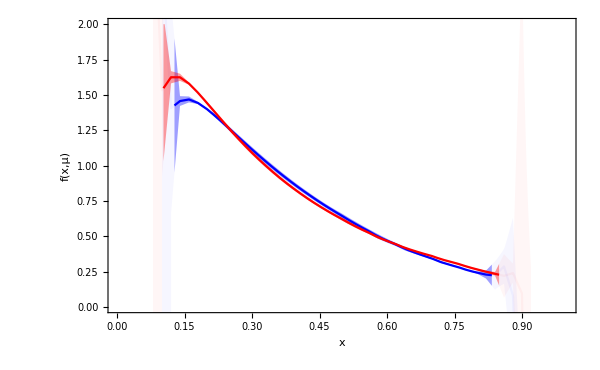

./pics/ComparePz6_add.pdf

```mathematica
fig=Show[

Plot[{PDFRGRTRintls19cv[x],PDFRGRTRintls19cv[x]+PDFRGRTRintls19err[x],PDFRGRTRintls19cv[x]-PDFRGRTRintls19err[x]},{x,0.127715,0.832990},PlotStyle->{Blue,Opacity[0,Blue],Opacity[0,Blue]},Filling->{1->{{2},{Opacity[0.618^2,Blue]}},1->{{3},{Opacity[0.618^2,Blue]}}},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["P^z = 1.9 GeV",20]},{0.6,0.6}]],

Plot[{PDFRGRTRintls19cv[x],PDFRGRTRintls19cv[x]+PDFRGRTRintls19err[x],PDFRGRTRintls19cv[x]-PDFRGRTRintls19err[x]},x∈ImplicitRegion[0.1≤x≤ 0.127715||0.832990≤x≤0.9,{x}],PlotStyle->{Opacity[0.618^7,Blue],Opacity[0,Blue],Opacity[0,Blue]},Filling->{1->{{2},{Opacity[0.618^7,Blue]}},1->{{3},{Opacity[0.618^7,Blue]}}}],

Plot[{PDFRGRTRintls24cv[x],PDFRGRTRintls24cv[x]+PDFRGRTRintls24err[x],PDFRGRTRintls24cv[x]-PDFRGRTRintls24err[x]},{x,0.103275,0.849064},PlotStyle->{Red,Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618^2,Red]}},1->{{3},{Opacity[0.618^2,Red]}}},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["P^z = 2.4 GeV",20]},{0.6,0.6}]],

Plot[{PDFRGRTRintls24cv[x],PDFRGRTRintls24cv[x]+PDFRGRTRintls24err[x],PDFRGRTRintls24cv[x]-PDFRGRTRintls24err[x]},x∈ImplicitRegion[0.08≤x≤ 0.103275||0.849064≤x≤ 0.92,{x}],PlotStyle->{Opacity[0.618^7,Red],Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618^7,Red]}},1->{{3},{Opacity[0.618^7,Red]}}}],


PlotRange->{{0,1},{0,2}},
FrameLabel->{Style["x",20],Style["f(x,μ)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]

SetDirectory[NotebookDirectory[]];
Export["./pics/ComparePz6_add.pdf",fig]
```

### Compare Pz=1.9 GeV and Pz=2.4 GeV, √(σ_h^2+σ_i^2+σ_γ^2), L=3

#### Data scale variation

```mathematica
PDFRGRTRls19={{{1.3467996518428786,1.4681419489731502,1.509241443386508,1.4958391582421522,1.4558010656679137,1.402826177373952,1.343950674903559,1.2829107528343362,1.2216909017919546,1.1613135038978475,1.1025136266675755,1.0459134573705822,0.9915769141533246,0.9395229195831142,0.8897360809514534,0.8421444312765097,0.7966917046844358,0.7532610438998287,0.7117902033086799,0.6722421876868607,0.634584582064467,0.5965972905041276,0.5616187822647409,0.5293969739258167,0.4928155525219778,0.46391333348381303,0.4376219017370061,0.4065500843097786,0.38344259351612153,0.3614970378897441,0.3419718818486321,0.31590977916530877,0.29732740373163946,0.2797300447755983,0.2575509069124838,0.24122902752645106,0.2257949068698581,0.21271415474329403,0.19959896266151664,0.245929040328498,0.08184903194385551},{2.485005081503087,1.4046907729959754,1.4557158291942636,1.4670771798614417,1.4421684242352566,1.3985810154633376,1.34562345486278,1.288365972173637,1.2296272297023745,1.1709985814954105,1.1133915211310743,1.057329365268923,1.0031137615109313,0.9510049846853174,0.901055597830699,0.8532421320987965,0.8075321901856047,0.7638431032851503,0.7221234291560866,0.6823041864629067,0.6443154793619399,0.6080653849080951,0.5734439980281864,0.5392098737724246,0.5045635870154256,0.4735763552297303,0.4451647766958857,0.41475797159692623,0.38989261179101703,0.36652317817996605,0.3450714325446493,0.31987500491648513,0.3001131804557724,0.28124032581888314,0.25935749290041804,0.2421946244862067,0.22596066840249862,0.21182580701084064,0.198796589458327,0.2263098620624731,0.07139430977198455},{9.270921629147358*^6,2.7314345423323365,1.5195282617661774,1.4551246710859043,1.4440231640275374,1.4097174458203774,1.3626120998601503,1.3087164490741583,1.2517429384331515,1.193879773629715,1.1363933617320423,1.0800704108038652,1.0253350490402315,0.9724335912356358,0.9215001389212375,0.8726077690166147,0.8258702196376712,0.7812639451172325,0.7386428653969601,0.6979438653566302,0.6590852779750508,0.6220308834499044,0.5866929470725231,0.5529991841272638,0.5208714816975415,0.49021248019164554,0.45913844896593153,0.4287013324530103,0.40132317798426764,0.37585243957065706,0.3520865745689015,0.32716018685536835,0.30574811059131946,0.28525726809925345,0.2633768768212463,0.24504232733572487,0.22773595870112495,0.21233917246566159,0.1990499997208716,0.2133600227648599,0.05576632084418362}},{{1.3484328313705383,1.4693964145355158,1.5103126837054777,1.4967778532472662,1.4566359671756632,1.4035757847475374,1.3446276619501494,1.2835244219580957,1.2222476296155336,1.16181735800111,1.1029668891751285,1.0463162020449097,0.9919275217682728,0.9398172334407102,0.8899665202206029,0.8422988243789185,0.7967494127177116,0.7531877548806879,0.7110492914318086,0.6709376792641834,0.6284974128457251,0.592229249374636,0.5578942055940427,0.5264806846203643,0.4880434932810811,0.460068274059752,0.4347243208092409,0.40339143725557103,0.38116041656897304,0.3596627182356621,0.34024351464913005,0.3137879989863189,0.2957209466781051,0.2789137785505366,0.25757902661249693,0.24266437886053355,0.23013014310964475,0.22616620210159044,0.3669407896430617,0.09052699771323432,-2.512380771479854},{2.4869773445281185,1.4054345684705,1.4563045870446032,1.4675883496209576,1.4426233503426764,1.3989913404022591,1.3459968857388813,1.288707996881424,1.2299418114490936,1.171288825449605,1.113659656234851,1.057576975373116,1.0033418671133199,0.9512140047671026,0.9012453942853872,0.8534119563742913,0.8076804666801588,0.7639673590437731,0.7222195612501711,0.6823653077237146,0.644326306654306,0.6055260878538757,0.5691360608381585,0.5352970660991363,0.4988562604275064,0.46890317389517033,0.4415281827011606,0.4108620835331967,0.38695391948634356,0.3641062225216392,0.34277859756163775,0.3172005676908754,0.29797776239451823,0.2798803173411989,0.25877311087047644,0.24291120833362137,0.2292197861498737,0.2225726548803893,0.28721882979554264,0.0799063687269465,-1.8884863458773549},{9.178498018858016*^6,2.7379575712315107,1.5210353025749983,1.456254237697612,1.4450009709103746,1.4106014605142976,1.3634253924453872,1.309473580353102,1.2524542300440296,1.1945530145725374,1.1370348389126688,1.0806848680689212,1.025926546440134,0.9730055263754006,0.9220553967336014,0.8731488312675226,0.8263992661825134,0.7817828398475394,0.7391533065904249,0.6984475471489751,0.6595842975247315,0.6225270528553123,0.5871810254967715,0.5531116320377779,0.5174986006434442,0.48474015830258554,0.4545663314378421,0.42391064764822306,0.39758423136388865,0.37272875150030416,0.34910035716139104,0.3238269897454188,0.3029767668107062,0.28323411398485315,0.2620532428084015,0.24489089948988835,0.2297320448743481,0.22022862355055667,0.2504004179163178,0.0640524152779377,-1.4246329771476467}},{{1.3496359116893295,1.4703205128621462,1.5111019282851137,1.4974694796955572,1.4572511224637341,1.4041281074031842,1.3451265300400055,1.2839767541077574,1.2226582096707719,1.1621892845664628,1.103301951647344,1.0466145423838453,0.9921879512082742,0.9400364183372037,0.8901376533893984,0.8424057465632907,0.7962830812019394,0.7470788730001212,0.7054013787759742,0.6667857982727454,0.62063574132377,0.5858123134268862,0.5524310307524035,0.5220472284789006,0.48230872196524993,0.4551039056222826,0.43024224099296,0.3985003256386692,0.37692633924364966,0.3562334397544444,0.3380772534723745,0.31258255123346584,0.2959852864348623,0.2812896564893709,0.26381061908515496,0.2585298251427144,0.3007480111596869,0.08522152755708351,0.07717882477918267,1.0579299618152371,0.16710648775862452},{2.492038320715153,1.4073875361431658,1.4578595603581028,1.4689454392891625,1.443839309832058,1.4000974407479314,1.3470139284835856,1.2896508802798394,1.2308213808152264,1.1721137000690887,1.1144361440548227,1.0583096869229047,1.004033889845872,0.9518666684392608,0.9018580951278293,0.8539810411922762,0.8081942428438474,0.7643618504600102,0.7206490766491404,0.6788139963735954,0.6349594347439249,0.5976875659270933,0.562347027437299,0.5295130912109611,0.49183510585259604,0.4627638004471041,0.4359599261655267,0.4048700209229126,0.3816665920207571,0.35965015157310476,0.3395465088845295,0.3148430263429977,0.2969922541157884,0.28075394433010276,0.26283092921045315,0.2545303864998919,0.2759679829939944,0.043760687887736335,0.0716614927654211,1.1009684970217324,0.1656992723555646},{9.116008030478425*^6,2.7423602685958195,1.5220208749741198,1.4569886852022125,1.4456343806697192,1.4111718986460358,1.3639477314891675,1.3099571218887311,1.2529054982879453,1.1949768566247594,1.1374350723420414,1.0810642463730427,1.026287266705073,0.9733491892765124,0.9223830008740745,0.8734606477450994,0.8266944890124148,0.7820585814586715,0.7394017344249628,0.6986438175187193,0.6595739516149344,0.6199401203689489,0.5815301702192075,0.5455884745069983,0.5089012580375372,0.477151995647698,0.447663998775945,0.4166129876684524,0.391052811425722,0.3670663299281522,0.344606990155018,0.3201358690343405,0.30055240335581423,0.28240086698397976,0.26374431155592915,0.25226216654460626,0.2593034919683255,-0.09131350649075436,0.06559506965828071,1.161007563981439,0.1647640664875977}}};
```

```mathematica
PDFRGRTRls24={{{1.4464560996282974,1.637015033743667,1.6827761266222732,1.653075882182051,1.591784519666141,1.5179181160729986,1.440027634521712,1.3621907588130209,1.2862176205981117,1.2138735942862802,1.1454103018499162,1.0808425555992136,1.0200937117067554,0.9630187318552458,0.9093839517189798,0.8590403107147974,0.8118398056755509,0.7675887172464809,0.7261083588511827,0.6872228850829565,0.6507684682253234,0.6167468457422599,0.5823616046130139,0.5513786724545339,0.5234846345212794,0.49182193904263083,0.46729125909207747,0.4452938642712498,0.41894046216101,0.39938329672136436,0.38073209493759186,0.3644084845795085,0.3409588532922611,0.324916750437776,0.30945546159856335,0.2886311908836542,0.2718308097654043,0.2548219392525161,0.2389961410130668,0.2178482733956648,0.2054137102818199,0.24283836811012097,0.08663998231472246},{2.9344961826283207,1.5320195044745835,1.6244019336603188,1.6241355126488508,1.5793727440494882,1.5148776498674636,1.4424840419053113,1.3680346599052877,1.2944277983365713,1.2231437375833876,1.1548984345335893,1.0902648470121918,1.0292862639085592,0.9718564766173103,0.9178481544024032,0.86710609908226,0.8194615029295592,0.7747170981745096,0.7326613945477287,0.6932012554171575,0.6561598135977696,0.6213754962589754,0.588691564764577,0.5580193687850036,0.527655024329302,0.49755633045238296,0.4709662214069247,0.4468386541316415,0.42090803133766097,0.39969749438520674,0.37967929589037286,0.36143570308376155,0.3388999133339867,0.321507966951056,0.30470655081196657,0.28421690049606285,0.2667301067538625,0.2492137747867862,0.2326488209169322,0.21274354927136882,0.1997732326553299,0.21925757406983537,0.08755418571488921},{-5.937887152597518*^6,2.6329944779179395,1.5976864395830364,1.6022007677938093,1.576744640238113,1.5230681199004739,1.4565574759465696,1.3850985941085605,1.3128311802765493,1.2419237446648326,1.173507402896061,1.1081494217898726,1.0461151856347457,0.9875800303546902,0.9325058295313985,0.8806987725903124,0.8320186634412041,0.7862746028823647,0.74331535478522,0.7029739136084489,0.6650854752050985,0.6294894791393997,0.5960177681665086,0.5644598468558786,0.5347215421032877,0.5066723893372075,0.4802154253921228,0.4530382261875004,0.4270044914936504,0.40362402989332163,0.38178138004785017,0.36142174125247045,0.3393859483004482,0.3206388570758224,0.3025329695053902,0.28240091665157674,0.26418238064731175,0.24611290336169644,0.22879053046934703,0.20983774143281922,0.19583196662067326,0.20159650787638866,0.08890431789164283}},{{1.4471134090680393,1.63749300821173,1.6831708325135646,1.6534102846339345,1.5920711274262849,1.5181650316847626,1.4402402207523959,1.362372611883443,1.2863709879691134,1.2139995782596134,1.1455090292531453,1.0809132822395378,1.0201345735977918,0.9630265322002156,0.9093540714067267,0.8589654251946419,0.811708366415897,0.7673829065587423,0.7258123000121512,0.6861436494726664,0.6492420654983996,0.6110092554071967,0.5784383797749585,0.5480591947877504,0.521112471502766,0.48784253448319087,0.46423635989048906,0.4431608002711052,0.41655615448760475,0.3977343095809245,0.37964417435560505,0.36390459008093984,0.34044391326418916,0.32471766273645464,0.30891039914830226,0.2877378881190158,0.27169287460125324,0.2559314935437014,0.24235798797678726,0.22819771088905919,0.2670190178122294,0.10076854997929816,-8.997985889899812},{2.9351201514268115,1.5322227413174774,1.6245612963774554,1.6242705590250706,1.5794893768456826,1.5149792952823555,1.4425729650631973,1.3681125057356445,1.2944957416479135,1.2232026354797543,1.154948902407278,1.090307289021059,1.0293209291699497,0.9718835259732046,0.9178676581909045,0.8671181047562885,0.8194661469058445,0.7747148833807423,0.7326538613081589,0.693193069853478,0.6561683753888806,0.6215294191540407,0.5859801076939302,0.5537188478904617,0.52427496446858,0.4926316031390539,0.4670519098663237,0.44392242791467024,0.41774660153560533,0.39733705839614686,0.37793658142591485,0.36028960398975246,0.337753836046506,0.3207115826490831,0.30356691078113396,0.282681376936927,0.2658769834149518,0.24943585767135518,0.23474411026200231,0.2202308958960298,0.23977535169871814,0.09572279853928523,-3.9472966412572292},{-6.033017810499675*^6,2.634478034076454,1.5982336045360748,1.6026332263644716,1.5771200361920081,1.5234022876013693,1.45685899699181,1.3853731438544303,1.3130827323879093,1.2421553531752403,1.1737212927834682,1.1083472454346195,1.0462981288065516,0.9877488768527238,0.9326609408019005,0.880840129449985,0.8321457999815243,0.7863866882143667,0.7434109309289564,0.703050752510002,0.665140259880902,0.6295172668072977,0.5960112383154074,0.5644119087704905,0.5340397534535332,0.5030938083519988,0.4748928666303925,0.44912860965165813,0.4228928248870216,0.40039027898552965,0.37923589839802363,0.3594785762286947,0.3374778912467595,0.3191095926428898,0.3006547992640076,0.28006906461968617,0.26243661376093286,0.24523421530828898,0.22934403626141012,0.2141497363511777,0.21889844625809649,0.08895311328646469,-2.2152786419870893}},{{1.4474504317892443,1.6377375280310584,1.6833722863049903,1.6535802615741448,1.5922159695199727,1.5182888854970904,1.4403458724929978,1.36246198067075,1.2864453460536223,1.2140596707289792,1.145555190233747,1.0809455318310741,1.0201525993459808,0.9630298131218514,0.9093424294145065,0.8589410265391777,0.811699180908956,0.7666353635894724,0.7203893688764089,0.6813997765576175,0.6458353836840687,0.6044427889556819,0.573062662755588,0.5435245472028651,0.5176812906609305,0.48325575316366004,0.4607360209370148,0.44073993703300135,0.4142315753304523,0.3963019666270299,0.3786113557966225,0.36286465904564785,0.33905218034236334,0.3234579862472534,0.30870911762097253,0.2890376520611908,0.2754208513169669,0.26491458496482095,0.2687105938114736,3.411474572442617,0.11956861112553215,-8.530500644916755,0.12081979791361216},{2.937184419707696,1.532912379969803,1.6251049717155672,1.6247341282838021,1.579893451525032,1.5153357934761282,1.4428896659586814,1.3683949580810992,1.2947477773309657,1.223426882129746,1.1551470070879986,1.0904799560441507,1.0294680084539962,0.9720041368328445,0.9179599178647024,0.8671790396993729,0.8194917172374695,0.7747018665511207,0.7326273603473772,0.6908632558144295,0.6524156462339813,0.6128049527072457,0.5792287738422541,0.547877686035226,0.5195008750330656,0.48675808559863276,0.4623445881143312,0.44036393600568174,0.4142783128046389,0.39481290598906155,0.3758587136845708,0.3582044787798849,0.33527224216951135,0.3183336026121376,0.302140312065311,0.2825007382868389,0.26766889186805476,0.25527156116719074,0.25289425860795894,0.48265995360190833,0.11625602526793696,-3.987116175505242,0.12201327470304207},{-6.060421555818027*^6,2.634928687335853,1.5983895302996374,1.602754423593318,1.577223683687135,1.5234927390247526,1.4569385387495128,1.3854432661508558,1.3131444615766084,1.242209454199305,1.1737682964607405,1.108387513745428,1.0463318814031624,0.9877762067611231,0.9326818116201034,0.8808543825032478,0.832153148506383,0.7863866922907959,0.7434029539660045,0.7030338665436411,0.6651128906989018,0.6294726524228272,0.5928732552157362,0.558884955809883,0.5275326534959651,0.4956294857405508,0.468687877722513,0.44415777672400625,0.41804252369503364,0.3965472591379329,0.3759024610890603,0.35613751230505364,0.33372154020269157,0.31541082533652254,0.29776740526876544,0.2781381243469987,0.26197457443062677,0.24756929188522775,0.2394298061316764,0.30066995895153076,0.11451555102737712,-2.264121123969089,0.12433765846821332}}};
```

#### Data threshold cut variation

```mathematica
PDFRGRTRls219={{2.487294834074457,1.405562170695839,1.4564072205610856,1.467678735162951,1.4427052708050287,1.3990669164443097,1.3460675423543598,1.2887747681021846,1.2300054644394385,1.1713499895736619,1.1137188152571682,1.0576345126153188,1.0033980811461505,0.9512690989904221,0.9012994855782911,0.8534650616738637,0.807732433311909,0.764017867343768,0.7222678682236138,0.6824098524690739,0.6443641621409127,0.6079189572587312,0.5723674558061608,0.5375382306494971,0.5042925701007513,0.47237648286691175,0.4412289968777472,0.41173090290646025,0.38883125554472114,0.3616283159289855,0.336399878588279,0.3133942382880516,0.29265188419091986,0.27296809893965573,0.258488564448035,0.24173184996025407,0.2264302277396023,0.21625674666842862,0.2560192103857031,0.11136376191359978,-0.7935053771579833},{2.4869773445281185,1.4054345684705,1.4563045870446032,1.4675883496209576,1.4426233503426764,1.3989913404022591,1.3459968857388813,1.288707996881424,1.2299418114490936,1.171288825449605,1.113659656234851,1.057576975373116,1.0033418671133199,0.9512140047671026,0.9012453942853872,0.8534119563742913,0.8076804666801588,0.7639673590437731,0.7222195612501711,0.6823653077237146,0.644326306654306,0.6055260878538757,0.5691360608381585,0.5352970660991363,0.4988562604275064,0.46890317389517033,0.4415281827011606,0.4108620835331967,0.38695391948634356,0.3641062225216392,0.34277859756163775,0.3172005676908754,0.29797776239451823,0.2798803173411989,0.25877311087047644,0.24291120833362137,0.2292197861498737,0.2225726548803893,0.28721882979554264,0.0799063687269465,-1.8884863458773549},{2.486997301086157,1.4054424560765766,1.4563108873267407,1.4675938531973485,1.442628291296195,1.3989958475699646,1.3460010429412288,1.2887118618987585,1.2299454236949485,1.1712922133779844,1.1136628366910324,1.057579955702004,1.0033446453702628,0.9512165683800701,0.9012477195110404,0.8534140067633768,0.8076821908392976,0.7639686947392181,0.7222204518031267,0.6823658144420136,0.6443277292752249,0.6046170087482645,0.5694279680136255,0.533813493486556,0.499773439656697,0.4725308675296495,0.44188516623041085,0.4128406189705295,0.3909182286078231,0.36438161922528084,0.33917341732711825,0.32067777601595115,0.29792876921306866,0.277014143675675,0.26226474051799603,0.24477127526970205,0.23139313735596628,0.23214367286023516,0.3450095422479836,0.033768380638429615,-3.787155743799039}};
```

```mathematica
PDFRGRTRls224={{2.935383590332335,1.5323133946183247,1.6246332179084286,1.6243323316503104,1.5795437835050057,1.5150279428624809,1.4426168932311925,1.3681524469157325,1.294532188465121,1.2232359072584678,1.1549791694525484,1.0903345673804399,1.0293450755968725,0.9719042353556091,0.9178843748487653,0.8671299216151067,0.8194716016618777,0.7747116030962943,0.7326377926640294,0.6931559479933364,0.6560899031433993,0.6213158719312228,0.5881484539913053,0.5567765027755632,0.5263322381728718,0.4974530437564985,0.4699130247746547,0.44305614258026316,0.4174895827226609,0.39863275556476707,0.3759245223207295,0.35523379266893385,0.33596737675388294,0.31788849183062223,0.2990435762611113,0.2848532904667543,0.2673744364675885,0.24975672601224572,0.2333772394084647,0.22009227366532247,0.23292028977558396,0.10290742722536295,-2.005944556253355},{2.9351201514268115,1.5322227413174774,1.6245612963774554,1.6242705590250706,1.5794893768456826,1.5149792952823555,1.4425729650631973,1.3681125057356445,1.2944957416479135,1.2232026354797543,1.154948902407278,1.090307289021059,1.0293209291699497,0.9718835259732046,0.9178676581909045,0.8671181047562885,0.8194661469058445,0.7747148833807423,0.7326538613081589,0.693193069853478,0.6561683753888806,0.6215294191540407,0.5859801076939302,0.5537188478904617,0.52427496446858,0.4926316031390539,0.4670519098663237,0.44392242791467024,0.41774660153560533,0.39733705839614686,0.37793658142591485,0.36028960398975246,0.337753836046506,0.3207115826490831,0.30356691078113396,0.282681376936927,0.2658769834149518,0.24943585767135518,0.23474411026200231,0.2202308958960298,0.23977535169871814,0.09572279853928523,-3.9472966412572292},{2.9351409890629574,1.5322299832315034,1.6245670483397345,1.624275504289697,1.5794937442540404,1.5149832158183052,1.4425765218918685,1.3681157558781987,1.2944987217056119,1.2232053671528011,1.1549513945270233,1.090309537262635,1.0293229158916952,0.9718852207181776,0.9178690119864852,0.8671190453274639,0.8194665696147231,0.7747146387702419,0.7326527295773313,0.6931906532105108,0.6561636248207603,0.6215109485234658,0.5852857985330003,0.5542633541558315,0.5230577645630721,0.49356300339437414,0.4703035158917021,0.4438757543953567,0.4190186086195559,0.4005687224436043,0.3777161047774741,0.35625457196409077,0.3406426611677323,0.3201974378629981,0.30025309661910393,0.2853744550404302,0.26619223092564426,0.24833742069876505,0.23563217439450523,0.22374081179227467,0.2464335228188606,0.10439096662264252,-1.1107698158715336}};
```

#### Plot

```mathematica
ClearAll[PDFRGRTRintls19cv,PDFRGRTRintls19err,PDFRGRTRintls24cv,PDFRGRTRintls24err];
xlsf=Table[N[1.0/50 i],{i,5,45}];
PDFRGRTRintls19=Table[Interpolation[Transpose[Re[{xlsf,PDFRGRTRls19[[i,j]]}]],InterpolationOrder->1],{i,1,3},{j,1,3}];
PDFRGRTRintls19cv[x_]:=PDFRGRTRintls19[[2,2]][x];

PDFRGRTR19hsdls=StandardDeviation[PDFRGRTRls19[[2,;;]]];
PDFRGRTRintls19herr=Interpolation[Transpose[{xlsf,PDFRGRTR19hsdls}],InterpolationOrder->1];

PDFRGRTR19isdls=StandardDeviation[PDFRGRTRls19[[;;,2]]];
PDFRGRTRintls19ierr=Interpolation[Transpose[{xlsf,PDFRGRTR19isdls}],InterpolationOrder->1];

PDFRGRTR19γsdls=StandardDeviation[PDFRGRTRls219];
PDFRGRTRintls19γerr=Interpolation[Transpose[{xlsf,PDFRGRTR19γsdls}],InterpolationOrder->1];

PDFRGRTRintls19err[x_]:=√(PDFRGRTRintls19herr[x]^2+PDFRGRTRintls19ierr[x]^2+PDFRGRTRintls19γerr[x]^2);
```

```mathematica
xlsf=Table[N[1.0/50 i],{i,4,46}];
PDFRGRTRintls24=Table[Interpolation[Transpose[Re[{xlsf,PDFRGRTRls24[[i,j]]}]],InterpolationOrder->1],{i,1,3},{j,1,3}];
PDFRGRTRintls24cv[x_]:=PDFRGRTRintls24[[2,2]][x];

PDFRGRTR24hsdls=StandardDeviation[PDFRGRTRls24[[2,;;]]];
PDFRGRTRintls24herr=Interpolation[Transpose[{xlsf,PDFRGRTR24hsdls}],InterpolationOrder->1];

PDFRGRTR24isdls=StandardDeviation[PDFRGRTRls24[[;;,2]]];
PDFRGRTRintls24ierr=Interpolation[Transpose[{xlsf,PDFRGRTR24isdls}],InterpolationOrder->1];

PDFRGRTR24γsdls=StandardDeviation[PDFRGRTRls224];
PDFRGRTRintls24γerr=Interpolation[Transpose[{xlsf,PDFRGRTR24γsdls}],InterpolationOrder->1];

PDFRGRTRintls24err[x_]:=√(PDFRGRTRintls24herr[x]^2+PDFRGRTRintls24ierr[x]^2+PDFRGRTRintls24γerr[x]^2);
```

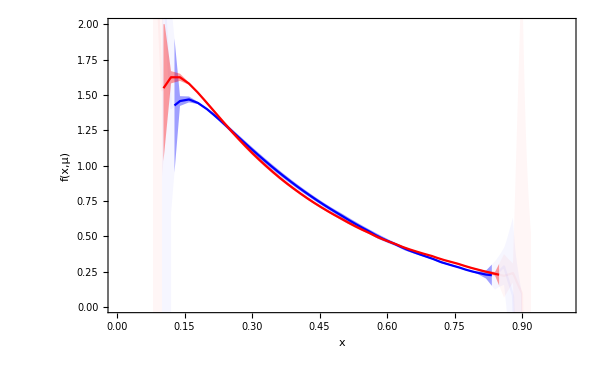

./pics/ComparePz6_add.pdf

```mathematica
fig=Show[

Plot[{PDFRGRTRintls19cv[x],PDFRGRTRintls19cv[x]+PDFRGRTRintls19err[x],PDFRGRTRintls19cv[x]-PDFRGRTRintls19err[x]},{x,0.127715,0.832990},PlotStyle->{Blue,Opacity[0,Blue],Opacity[0,Blue]},Filling->{1->{{2},{Opacity[0.618^2,Blue]}},1->{{3},{Opacity[0.618^2,Blue]}}},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["P^z = 1.9 GeV",20]},{0.6,0.6}]],

Plot[{PDFRGRTRintls19cv[x],PDFRGRTRintls19cv[x]+PDFRGRTRintls19err[x],PDFRGRTRintls19cv[x]-PDFRGRTRintls19err[x]},x∈ImplicitRegion[0.1≤x≤ 0.127715||0.832990≤x≤0.9,{x}],PlotStyle->{Opacity[0.618^7,Blue],Opacity[0,Blue],Opacity[0,Blue]},Filling->{1->{{2},{Opacity[0.618^7,Blue]}},1->{{3},{Opacity[0.618^7,Blue]}}}],

Plot[{PDFRGRTRintls24cv[x],PDFRGRTRintls24cv[x]+PDFRGRTRintls24err[x],PDFRGRTRintls24cv[x]-PDFRGRTRintls24err[x]},{x,0.103275,0.849064},PlotStyle->{Red,Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618^2,Red]}},1->{{3},{Opacity[0.618^2,Red]}}},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["P^z = 2.4 GeV",20]},{0.6,0.6}]],

Plot[{PDFRGRTRintls24cv[x],PDFRGRTRintls24cv[x]+PDFRGRTRintls24err[x],PDFRGRTRintls24cv[x]-PDFRGRTRintls24err[x]},x∈ImplicitRegion[0.08≤x≤ 0.103275||0.849064≤x≤ 0.92,{x}],PlotStyle->{Opacity[0.618^7,Red],Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618^7,Red]}},1->{{3},{Opacity[0.618^7,Red]}}}],


PlotRange->{{0,1},{0,2}},
FrameLabel->{Style["x",20],Style["f(x,μ)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]

SetDirectory[NotebookDirectory[]];
Export["./pics/ComparePz6_add.pdf",fig]
```

## NNLO without considering renormalon

### Lattice Data Pion Valence Quasi - PDF, Pz=1.9 GeV, zs=0.12fm, λ_L=25

```mathematica
(*
The data is generated by BNL/ANL Collaborations, Gao:2021dbh
Renormalized based on the RGR+LRR method, Zhang:2023bxs
*)
```

```mathematica
Pz=1.94;(*GeV*)
zs=0.12/GeVfm;(*GeV^-1*)
```

```mathematica
qls={{-2.,0.004644373353200662},{-1.99,0.004120247847633056},{-1.98,0.003622067087287381},{-1.97,0.0031552223149979},{-1.96,0.002726220362994065},{-1.95,0.002332121946113358},{-1.94,0.0019748105696102128},{-1.93,0.0016617946317518128},{-1.92,0.0013896498468505209},{-1.91,0.001157969030572405},{-1.9,0.0009740062784405524},{-1.89,0.0008343069837817357},{-1.88,0.0007354910726053484},{-1.87,0.0006844474334537591},{-1.86,0.0006775322836966953},{-1.85,0.0007093746490651379},{-1.84,0.0007848304657079239},{-1.83,0.0009010306765860066},{-1.82,0.0010500511427830594},{-1.81,0.0012347748938322317},{-1.8,0.0014529691648524812},{-1.79,0.001695074247695391},{-1.78,0.0019608772861017146},{-1.77,0.0022493261730182164},{-1.76,0.002548904375507088},{-1.75,0.0028570969569776993},{-1.74,0.0031734135755238676},{-1.73,0.003485305751241066},{-1.72,0.003787860492555417},{-1.71,0.004080714570753909},{-1.7,0.0043513415591125565},{-1.69,0.00459209780747},{-1.68,0.004802930805205951},{-1.67,0.004971973589585376},{-1.66,0.0050893807375176625},{-1.65,0.0051544301651739125},{-1.64,0.0051572528883037675},{-1.63,0.0050857962876900975},{-1.62,0.004939638608088999},{-1.61,0.0047103710762440385},{-1.6,0.004384588087735983},{-1.59,0.003961638559377615},{-1.58,0.0034355478567254134},{-1.57,0.0027923727101677306},{-1.56,0.0020307899346212865},{-1.55,0.001147653353127118},{-1.54,0.0001293662115165748},{-1.53,-0.0010262053436745217},{-1.52,-0.002319241626571331},{-1.51,-0.003762070898562308},{-1.5,-0.00535767461611031},{-1.49,-0.007103322325419803},{-1.48,-0.009009173627881811},{-1.47,-0.011078971693766839},{-1.46,-0.013307310981559016},{-1.45,-0.01570136328212513},{-1.44,-0.0182654114646309},{-1.43,-0.020991762810628253},{-1.42,-0.02388391683318669},{-1.41,-0.026946333224345465},{-1.4,-0.030169528227263636},{-1.39,-0.03355282186583401},{-1.38,-0.03710035027897443},{-1.37,-0.04081071753848808},{-1.36,-0.04465944879214011},{-1.35,-0.04865963860632827},{-1.34,-0.052799840226409746},{-1.33,-0.05707031143306075},{-1.32,-0.061472539521033896},{-1.31,-0.06599476622458914},{-1.3,-0.07062273776425468},{-1.29,-0.07535273029596794},{-1.28,-0.08017913633450793},{-1.27,-0.08507972027317055},{-1.26,-0.09004977201197047},{-1.25,-0.09507580386853634},{-1.24,-0.10013643453606268},{-1.23,-0.1052217762493435},{-1.22,-0.11031842068337755},{-1.21,-0.11539884898458205},{-1.2,-0.12044650543362649},{-1.19,-0.12544472751274555},{-1.18,-0.1303598348657722},{-1.17,-0.1351735733812622},{-1.16,-0.13984482290530456},{-1.15,-0.14433717761958592},{-1.14,-0.14860599638320865},{-1.13,-0.15260865725942266},{-1.12,-0.15627783779791632},{-1.11,-0.15953306926178973},{-1.1,-0.16228714588271892},{-1.09,-0.16441456147949368},{-1.08,-0.16574791938649297},{-1.07,-0.16608017752841578},{-1.06,-0.16512238403855972},{-1.05,-0.16247228616306125},{-1.04,-0.1576079570670807},{-1.03,-0.1498745549865596},{-1.02,-0.13856750481624514},{-1.01,-0.12329118093713683},{-1.,-0.10452791672037298},{-0.99,-0.08386577478628733},{-0.98,-0.06335779275286002},{-0.97,-0.044487529193872555},{-0.96,-0.027791608369410428},{-0.95,-0.013222288017471662},{-0.94,-0.0005060197676422379},{-0.93,0.010712926418813828},{-0.92,0.020747082549468394},{-0.91,0.029838009883754957},{-0.9,0.03821136232499601},{-0.89,0.0460465568700808},{-0.88,0.05346537832030689},{-0.87,0.06059246869266078},{-0.86,0.06753496522164032},{-0.85,0.0743557313427976},{-0.84,0.08112836368178805},{-0.83,0.0879271737670217},{-0.82,0.09478793608711844},{-0.81,0.10175642926745493},{-0.8,0.10889143693088607},{-0.79,0.11621674758268581},{-0.78,0.1237610583222274},{-0.77,0.13157504382591872},{-0.76,0.1396783280519504},{-0.75,0.14808810060910665},{-0.74,0.1568499582295041},{-0.73,0.16598381259698758},{-0.72,0.17549878312097195},{-0.71,0.18543635329779484},{-0.7,0.19581939592572234},{-0.69,0.20665153845175915},{-0.68,0.2179701214189261},{-0.67,0.22980255026321988},{-0.66,0.24214923764638413},{-0.65,0.25504292135001416},{-0.64,0.2685163194493533},{-0.63,0.28256884463310383},{-0.62,0.2972271045353138},{-0.61,0.3125311593245419},{-0.6,0.32848076047689745},{-0.59,0.34509795809233895},{-0.58,0.3624260434801411},{-0.57,0.38046917194148},{-0.56,0.3992438019869307},{-0.55,0.4187982160626459},{-0.54,0.43914024161844556},{-0.53,0.46028312747525324},{-0.52,0.4822784905078693},{-0.51,0.5051420233327284},{-0.5,0.5288815511766826},{-0.49,0.5535517147724702},{-0.48,0.5791791881504709},{-0.47,0.6057682632765653},{-0.46,0.6333745418103949},{-0.45,0.6620379331888059},{-0.44,0.6917625152625423},{-0.43,0.7226035104236992},{-0.42,0.7546157172441825},{-0.41,0.78780717183097},{-0.4,0.8222324759737083},{-0.39,0.8579628404685727},{-0.38,0.8950151875900143},{-0.37,0.9334445457962022},{-0.36,0.9733404584277825},{-0.35,1.0147346620849456},{-0.34,1.05768518912032},{-0.33,1.1023027626430033},{-0.32,1.1486414268852312},{-0.31,1.1967701625144844},{-0.3,1.246818645446664},{-0.29,1.2988768175409042},{-0.28,1.3530252429364402},{-0.27,1.409432971004116},{-0.26,1.4682327591165751},{-0.25,1.5295336404418816},{-0.24,1.5935488304240892},{-0.23,1.6604769430098891},{-0.22,1.7304757454739113},{-0.21,1.8038230429831537},{-0.2,1.8808140737409953},{-0.19,1.961688885024415},{-0.18,2.046824052821365},{-0.17,2.1366600426183044},{-0.16,2.231574775658292},{-0.15,2.3320820112281115},{-0.14,2.439006731842744},{-0.13,2.552529992013758},{-0.12,2.673751967916616},{-0.11,2.8037487067637175},{-0.1,2.9433866951050964},{-0.09,3.0936367993617053},{-0.08,3.2556429738423134},{-0.07,3.4302252428984916},{-0.06,3.617879799994142},{-0.05,3.8181709368900414},{-0.04,4.027353378189677},{-0.03,4.235688352317414},{-0.02,4.423972412482997},{-0.01,4.56087468343495},{0,4.612277188558619},{0.01,4.56087468343495},{0.02,4.423972412482997},{0.03,4.235688352317414},{0.04,4.027353378189677},{0.05,3.8181709368900414},{0.06,3.617879799994142},{0.07,3.4302252428984916},{0.08,3.2556429738423134},{0.09,3.0936367993617053},{0.1,2.9433866951050964},{0.11,2.8037487067637175},{0.12,2.673751967916616},{0.13,2.552529992013758},{0.14,2.439006731842744},{0.15,2.3320820112281115},{0.16,2.231574775658292},{0.17,2.1366600426183044},{0.18,2.046824052821365},{0.19,1.961688885024415},{0.2,1.8808140737409953},{0.21,1.8038230429831537},{0.22,1.7304757454739113},{0.23,1.6604769430098891},{0.24,1.5935488304240892},{0.25,1.5295336404418816},{0.26,1.4682327591165751},{0.27,1.409432971004116},{0.28,1.3530252429364402},{0.29,1.2988768175409042},{0.3,1.246818645446664},{0.31,1.1967701625144844},{0.32,1.1486414268852312},{0.33,1.1023027626430033},{0.34,1.05768518912032},{0.35,1.0147346620849456},{0.36,0.9733404584277825},{0.37,0.9334445457962022},{0.38,0.8950151875900143},{0.39,0.8579628404685727},{0.4,0.8222324759737083},{0.41,0.78780717183097},{0.42,0.7546157172441825},{0.43,0.7226035104236992},{0.44,0.6917625152625423},{0.45,0.6620379331888059},{0.46,0.6333745418103949},{0.47,0.6057682632765653},{0.48,0.5791791881504709},{0.49,0.5535517147724702},{0.5,0.5288815511766826},{0.51,0.5051420233327284},{0.52,0.4822784905078693},{0.53,0.46028312747525324},{0.54,0.43914024161844556},{0.55,0.4187982160626459},{0.56,0.3992438019869307},{0.57,0.38046917194148},{0.58,0.3624260434801411},{0.59,0.34509795809233895},{0.6,0.32848076047689745},{0.61,0.3125311593245419},{0.62,0.2972271045353138},{0.63,0.28256884463310383},{0.64,0.2685163194493533},{0.65,0.25504292135001416},{0.66,0.24214923764638413},{0.67,0.22980255026321988},{0.68,0.2179701214189261},{0.69,0.20665153845175915},{0.7,0.19581939592572234},{0.71,0.18543635329779484},{0.72,0.17549878312097195},{0.73,0.16598381259698758},{0.74,0.1568499582295041},{0.75,0.14808810060910665},{0.76,0.1396783280519504},{0.77,0.13157504382591872},{0.78,0.1237610583222274},{0.79,0.11621674758268581},{0.8,0.10889143693088607},{0.81,0.10175642926745493},{0.82,0.09478793608711844},{0.83,0.0879271737670217},{0.84,0.08112836368178805},{0.85,0.0743557313427976},{0.86,0.06753496522164032},{0.87,0.06059246869266078},{0.88,0.05346537832030689},{0.89,0.0460465568700808},{0.9,0.03821136232499601},{0.91,0.029838009883754957},{0.92,0.020747082549468394},{0.93,0.010712926418813828},{0.94,-0.0005060197676422379},{0.95,-0.013222288017471662},{0.96,-0.027791608369410428},{0.97,-0.044487529193872555},{0.98,-0.06335779275286002},{0.99,-0.08386577478628733},{1.,-0.10452791672037298},{1.01,-0.12329118093713683},{1.02,-0.13856750481624514},{1.03,-0.1498745549865596},{1.04,-0.1576079570670807},{1.05,-0.16247228616306125},{1.06,-0.16512238403855972},{1.07,-0.16608017752841578},{1.08,-0.16574791938649297},{1.09,-0.16441456147949368},{1.1,-0.16228714588271892},{1.11,-0.15953306926178973},{1.12,-0.15627783779791632},{1.13,-0.15260865725942266},{1.14,-0.14860599638320865},{1.15,-0.14433717761958592},{1.16,-0.13984482290530456},{1.17,-0.1351735733812622},{1.18,-0.1303598348657722},{1.19,-0.12544472751274555},{1.2,-0.12044650543362649},{1.21,-0.11539884898458205},{1.22,-0.11031842068337755},{1.23,-0.1052217762493435},{1.24,-0.10013643453606268},{1.25,-0.09507580386853634},{1.26,-0.09004977201197047},{1.27,-0.08507972027317055},{1.28,-0.08017913633450793},{1.29,-0.07535273029596794},{1.3,-0.07062273776425468},{1.31,-0.06599476622458914},{1.32,-0.061472539521033896},{1.33,-0.05707031143306075},{1.34,-0.052799840226409746},{1.35,-0.04865963860632827},{1.36,-0.04465944879214011},{1.37,-0.04081071753848808},{1.38,-0.03710035027897443},{1.39,-0.03355282186583401},{1.4,-0.030169528227263636},{1.41,-0.026946333224345465},{1.42,-0.02388391683318669},{1.43,-0.020991762810628253},{1.44,-0.0182654114646309},{1.45,-0.01570136328212513},{1.46,-0.013307310981559016},{1.47,-0.011078971693766839},{1.48,-0.009009173627881811},{1.49,-0.007103322325419803},{1.5,-0.00535767461611031},{1.51,-0.003762070898562308},{1.52,-0.002319241626571331},{1.53,-0.0010262053436745217},{1.54,0.0001293662115165748},{1.55,0.001147653353127118},{1.56,0.0020307899346212865},{1.57,0.0027923727101677306},{1.58,0.0034355478567254134},{1.59,0.003961638559377615},{1.6,0.004384588087735983},{1.61,0.0047103710762440385},{1.62,0.004939638608088999},{1.63,0.0050857962876900975},{1.64,0.0051572528883037675},{1.65,0.0051544301651739125},{1.66,0.0050893807375176625},{1.67,0.004971973589585376},{1.68,0.004802930805205951},{1.69,0.00459209780747},{1.7,0.0043513415591125565},{1.71,0.004080714570753909},{1.72,0.003787860492555417},{1.73,0.003485305751241066},{1.74,0.0031734135755238676},{1.75,0.0028570969569776993},{1.76,0.002548904375507088},{1.77,0.0022493261730182164},{1.78,0.0019608772861017146},{1.79,0.001695074247695391},{1.8,0.0014529691648524812},{1.81,0.0012347748938322317},{1.82,0.0010500511427830594},{1.83,0.0009010306765860066},{1.84,0.0007848304657079239},{1.85,0.0007093746490651379},{1.86,0.0006775322836966953},{1.87,0.0006844474334537591},{1.88,0.0007354910726053484},{1.89,0.0008343069837817357},{1.9,0.0009740062784405524},{1.91,0.001157969030572405},{1.92,0.0013896498468505209},{1.93,0.0016617946317518128},{1.94,0.0019748105696102128},{1.95,0.002332121946113358},{1.96,0.002726220362994065},{1.97,0.0031552223149979},{1.98,0.003622067087287381},{1.99,0.004120247847633056},{2.,0.004644373353200662}};
```

### Δx=0.005, L=3, γ=0.4

```mathematica
μ=2;(*GeV*)(*Factorization Scale*)
PertAcc="NNLO";
```

#### Discretization

```mathematica
qlsgf=GaussianFilter[qls,{{4,0}}];
qinttest=Interpolation[qlsgf];
ClearAll[qint];
qint[x_]:=If[Abs[x]<2,qinttest[x],qinttest[2]Exp[-(Abs[x]-2)]];
Plot[qint[x],{x,-4,4},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
L=3;
Δx=0.005;(*Discretization*)
xlist=Join[Table[x,{x,-L,-Δx,Δx}],Table[x,{x,Δx,L,Δx}]];
qV=Table[qint[x],{x,xlist}];
```

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

#### Fixed order results

```mathematica
(*Matrix Elements generation*)
```

```mathematica
If[PertAcc=="NNLO",
MCratio1pluswμ=SubMGen[Cratio1pluswμ,xlist,Pz,zs];
MCratio1pluswoμ=SubMGen[Cratio1pluswoμ,xlist,Pz,zs];
MChybrid1plus=SubMGen[Chybrid1plus,xlist,Pz,zs];

MCMS2wLL=SubMGen[CMS2wLL,xlist,Pz,zs];
MCMS2wNLL=SubMGen[CMS2wNLL,xlist,Pz,zs];
MCMS2woL=SubMGen[CMS2woL,xlist,Pz,zs];
MChybrid2pluswLL=SubMGen[Chybrid2pluswLL,xlist,Pz,zs];
MChybrid2pluswNLLPz=SubMGen[Chybrid2pluswNLLPz,xlist,Pz,zs];
MChybrid2pluswNLLzs=SubMGen[Chybrid2pluswNLLzs,xlist,Pz,zs];
MChybrid2pluswoL=SubMGen[Chybrid2pluswoL,xlist,Pz,zs];

MfixGen[μ_]:=Module[{nf,C1,C2,C1i,C2i},
nf=3;
C1=(αsNNLO[[1]][μ]*CF)/(2Pi)((-Log[(μ/Pz)^2])MCratio1pluswμ+MCratio1pluswoμ+MChybrid1plus);
C2=Re[((αsNNLO[[1]][μ])/(2Pi))^2(MCMS2wLL*Log[μ^2/Pz^2]^2+MCMS2wNLL*Log[μ^2/Pz^2]+MCMS2woL+MChybrid2pluswLL*Log[μ^2/Pz^2]Log[(zs^2 μ^2 Exp[2EulerGamma])/4]+MChybrid2pluswNLLPz*Log[μ^2/Pz^2]+MChybrid2pluswNLLzs*Log[(zs^2 μ^2 Exp[2EulerGamma])/4]+MChybrid2pluswoL)];
C1i=-C1;
C2i=-C2+C1.C1;

IdentityMatrix[Length[xlist]]+C1i+C2i
],
Nothing[];
]
```

ToExpression::notstrbox: FEPrivate`FrontEndResourceString[GetFEKernelInit] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

CloudConnect::verr: This version of Mathematica is no longer supported for use with the Wolfram Cloud beginning Wed 1 Jan 2025. Please

```mathematica
(*Calculation*)
```

```mathematica
ChM=MfixGen[μ];
fVfixed=ChM.qV;
(fVfixed+Reverse[fVfixed])/2
fVint=Interpolation[Transpose[{xlist,(fVfixed+Reverse[fVfixed])/2}]];
```

{-0.0266072,-0.0263889,-0.0261463,-0.0259362,-0.0257563,-0.0256008,-0.0254645,-0.0253438,-0.0252359,-0.0251385,-0.02505,-0.024969,-0.0248946,-0.0248258,-0.0247619,-0.0247023,-0.0246465,-0.0245941,-0.0245446,-0.0244978,-0.0244535,-0.0244112,-0.0243709,-0.0243322,-0.0242952,-0.0242595,-0.024225,-0.0241917,-0.0241594,-0.024128,-0.0240975,-0.0240676,-0.0240384,-0.0240097,-0.0239815,-0.0239538,-0.0239264,-0.0238993,-0.0238725,-0.023846,-0.0238196,-0.0237933,-0.0237671,-0.0237409,-0.0237148,-0.0236887,-0.0236625,-0.0236362,-0.0236098,-0.0235833,-0.0235566,-0.0235297,-0.0235027,-0.0234754,-0.0234478,-0.02342,-0.0233918,-0.0233634,-0.0233346,-0.0233055,-0.023276,-0.0232461,-0.0232159,-0.0231852,-0.0231541,-0.0231226,-0.0230906,-0.0230582,-0.0230252,-0.0229918,-0.0229579,-0.0229235,-0.0228885,-0.022853,-0.022817,-0.0227804,-0.0227432,-0.0227055,-0.0226672,-0.0226283,-0.0225888,-0.0225486,-0.0225079,-0.0224665,-0.0224245,-0.0223819,-0.0223386,-0.0222947,-0.0222501,-0.0222048,-0.0221589,-0.0221122,-0.0220649,-0.0220169,-0.0219682,-0.0219188,-0.0218686,-0.0218178,-0.0217662,-0.0217139,-0.0216609,-0.0216071,-0.0215526,-0.0214974,-0.0214414,-0.0213846,-0.0213271,-0.0212689,-0.0212099,-0.0211501,-0.0210895,-0.0210282,-0.0209661,-0.0209032,-0.0208396,-0.0207752,-0.02071,-0.020644,-0.0205772,-0.0205097,-0.0204414,-0.0203723,-0.0203024,-0.0202317,-0.0201602,-0.020088,-0.020015,-0.0199412,-0.0198666,-0.0197913,-0.0197152,-0.0196383,-0.0195606,-0.0194822,-0.0194031,-0.0193232,-0.0192425,-0.0191611,-0.019079,-0.0189961,-0.0189126,-0.0188283,-0.0187433,-0.0186577,-0.0185713,-0.0184843,-0.0183966,-0.0183083,-0.0182194,-0.0181298,-0.0180397,-0.0179489,-0.0178576,-0.0177658,-0.0176734,-0.0175806,-0.0174872,-0.0173934,-0.0172992,-0.0172046,-0.0171096,-0.0170143,-0.0169187,-0.0168229,-0.0167268,-0.0166306,-0.0165343,-0.0164379,-0.0163414,-0.016245,-0.0161488,-0.0160526,-0.0159568,-0.0158613,-0.0157662,-0.0156716,-0.0155776,-0.0154843,-0.0153919,-0.0153004,-0.0152101,-0.015121,-0.0150334,-0.0149473,-0.0148631,-0.014781,-0.0147011,-0.0146238,-0.0145492,-0.0144778,-0.0144098,-0.0143455,-0.0142852,-0.0142289,-0.0141767,-0.0141279,-0.0140806,-0.0140299,-0.0139622,-0.0138299,-0.0133347,-0.013031,-0.0126172,-0.0122131,-0.0118297,-0.0114669,-0.0111231,-0.0107965,-0.0104856,-0.0101893,-0.00990693,-0.00963677,-0.00937833,-0.00913058,-0.00889285,-0.00866443,-0.00844484,-0.00823355,-0.00803023,-0.00783441,-0.00764586,-0.00746419,-0.00728923,-0.0071207,-0.00695848,-0.00680226,-0.00665198,-0.00650736,-0.00636834,-0.00623471,-0.00610643,-0.00598326,-0.00586519,-0.00575196,-0.00564354,-0.00553977,-0.00544061,-0.00534583,-0.00525544,-0.00516918,-0.00508702,-0.00500878,-0.00493442,-0.0048637,-0.00479662,-0.00473289,-0.00467248,-0.00461519,-0.00456094,-0.00450951,-0.00446084,-0.00441466,-0.0043709,-0.00432932,-0.00428982,-0.00425218,-0.00421629,-0.00418186,-0.00414879,-0.00411683,-0.00408581,-0.00405553,-0.00402583,-0.0039964,-0.00396709,-0.00393765,-0.00390785,-0.00387749,-0.00384635,-0.00381414,-0.00378066,-0.00374563,-0.00370879,-0.00366993,-0.00362878,-0.00358506,-0.00353849,-0.0034888,-0.00343567,-0.00337889,-0.00331813,-0.0032531,-0.00318349,-0.00310899,-0.00302925,-0.00294405,-0.00285299,-0.0027558,-0.00265209,-0.00254157,-0.0024238,-0.00229856,-0.00216538,-0.00202401,-0.00187399,-0.00171499,-0.00154653,-0.00136838,-0.00117998,-0.000981078,-0.000771145,-0.000549832,-0.000316598,-0.000071159,0.000187101,0.000458446,0.000743501,0.00104264,0.00135648,0.00168535,0.00202995,0.00239057,0.00276794,0.00316248,0.00357487,0.00400562,0.0044555,0.00492482,0.00541447,0.00592496,0.0064571,0.00701135,0.00758862,0.00818921,0.00881412,0.00946375,0.010139,0.0108405,0.0115691,0.0123256,0.0131108,0.0139256,0.014771,0.0156478,0.0165571,0.0174997,0.0184769,0.0194894,0.0205385,0.0216252,0.0227508,0.0239162,0.0251228,0.0263715,0.0276639,0.029001,0.0303843,0.031815,0.0332946,0.0348243,0.0364058,0.0380403,0.0397297,0.0414753,0.0432789,0.0451418,0.0470662,0.0490532,0.0511051,0.053223,0.0554094,0.0576651,0.0599926,0.0623927,0.064868,0.0674186,0.0700474,0.072754,0.0755411,0.0784077,0.0813566,0.0843853,0.0874966,0.0906859,0.0939558,0.0972989,0.100717,0.104199,0.107746,0.11134,0.11498,0.118639,0.122317,0.125972,0.129601,0.133149,0.136606,0.139906,0.143029,0.145911,0.148514,0.1508,0.15271,0.154262,0.155373,0.156143,0.156481,0.156558,0.156306,0.155922,0.155399,0.154898,0.154486,0.154241,0.154292,0.154628,0.155397,0.156524,0.158132,0.160125,0.162574,0.16539,0.168593,0.172117,0.175944,0.180032,0.184345,0.188858,0.193532,0.198352,0.203286,0.208324,0.213442,0.218632,0.223877,0.229174,0.234508,0.239878,0.245275,0.250699,0.256142,0.261606,0.267085,0.27258,0.27809,0.283614,0.289151,0.294703,0.300269,0.30585,0.311446,0.317059,0.322689,0.328337,0.334003,0.339691,0.345399,0.351131,0.356886,0.362666,0.368473,0.374307,0.38017,0.386064,0.391988,0.397946,0.403937,0.409964,0.416026,0.422127,0.428267,0.434446,0.440667,0.44693,0.453236,0.459588,0.465985,0.472428,0.47892,0.485461,0.492052,0.498695,0.505389,0.512137,0.518939,0.525795,0.532709,0.539679,0.546707,0.553795,0.560942,0.56815,0.57542,0.582753,0.590149,0.59761,0.605136,0.612728,0.620388,0.628115,0.635911,0.643777,0.651714,0.659722,0.667802,0.675955,0.684182,0.692484,0.700862,0.709316,0.717847,0.726457,0.735146,0.743914,0.752764,0.761695,0.77071,0.779807,0.78899,0.798257,0.807611,0.817052,0.826582,0.836201,0.845911,0.855712,0.865605,0.875592,0.885674,0.895851,0.906126,0.916499,0.926972,0.937545,0.948221,0.958999,0.969884,0.980874,0.991973,1.00318,1.0145,1.02593,1.03748,1.04914,1.06093,1.07283,1.08486,1.09701,1.10929,1.1217,1.13424,1.14692,1.15974,1.1727,1.18581,1.19906,1.21247,1.22603,1.23976,1.25365,1.26772,1.28196,1.29638,1.31099,1.3258,1.34082,1.35604,1.37149,1.38717,1.40308,1.41926,1.4357,1.45243,1.46945,1.48679,1.50446,1.5225,1.54093,1.55978,1.57908,1.59888,1.61921,1.64015,1.66174,1.68408,1.70723,1.73132,1.75646,1.78281,1.81057,1.83998,1.87137,1.9051,1.94176,1.98194,2.02667,2.07703,2.13493,2.20248,2.28332,2.38188,2.50536,2.66335,2.87083,3.14987,3.53643,4.09257,4.94359,6.41048,9.98309,9.98309,6.41048,4.94359,4.09257,3.53643,3.14987,2.87083,2.66335,2.50536,2.38188,2.28332,2.20248,2.13493,2.07703,2.02667,1.98194,1.94176,1.9051,1.87137,1.83998,1.81057,1.78281,1.75646,1.73132,1.70723,1.68408,1.66174,1.64015,1.61921,1.59888,1.57908,1.55978,1.54093,1.5225,1.50446,1.48679,1.46945,1.45243,1.4357,1.41926,1.40308,1.38717,1.37149,1.35604,1.34082,1.3258,1.31099,1.29638,1.28196,1.26772,1.25365,1.23976,1.22603,1.21247,1.19906,1.18581,1.1727,1.15974,1.14692,1.13424,1.1217,1.10929,1.09701,1.08486,1.07283,1.06093,1.04914,1.03748,1.02593,1.0145,1.00318,0.991973,0.980874,0.969884,0.958999,0.948221,0.937545,0.926972,0.916499,0.906126,0.895851,0.885674,0.875592,0.865605,0.855712,0.845911,0.836201,0.826582,0.817052,0.807611,0.798257,0.78899,0.779807,0.77071,0.761695,0.752764,0.743914,0.735146,0.726457,0.717847,0.709316,0.700862,0.692484,0.684182,0.675955,0.667802,0.659722,0.651714,0.643777,0.635911,0.628115,0.620388,0.612728,0.605136,0.59761,0.590149,0.582753,0.57542,0.56815,0.560942,0.553795,0.546707,0.539679,0.532709,0.525795,0.518939,0.512137,0.505389,0.498695,0.492052,0.485461,0.47892,0.472428,0.465985,0.459588,0.453236,0.44693,0.440667,0.434446,0.428267,0.422127,0.416026,0.409964,0.403937,0.397946,0.391988,0.386064,0.38017,0.374307,0.368473,0.362666,0.356886,0.351131,0.345399,0.339691,0.334003,0.328337,0.322689,0.317059,0.311446,0.30585,0.300269,0.294703,0.289151,0.283614,0.27809,0.27258,0.267085,0.261606,0.256142,0.250699,0.245275,0.239878,0.234508,0.229174,0.223877,0.218632,0.213442,0.208324,0.203286,0.198352,0.193532,0.188858,0.184345,0.180032,0.175944,0.172117,0.168593,0.16539,0.162574,0.160125,0.158132,0.156524,0.155397,0.154628,0.154292,0.154241,0.154486,0.154898,0.155399,0.155922,0.156306,0.156558,0.156481,0.156143,0.155373,0.154262,0.15271,0.1508,0.148514,0.145911,0.143029,0.139906,0.136606,0.133149,0.129601,0.125972,0.122317,0.118639,0.11498,0.11134,0.107746,0.104199,0.100717,0.0972989,0.0939558,0.0906859,0.0874966,0.0843853,0.0813566,0.0784077,0.0755411,0.072754,0.0700474,0.0674186,0.064868,0.0623927,0.0599926,0.0576651,0.0554094,0.053223,0.0511051,0.0490532,0.0470662,0.0451418,0.0432789,0.0414753,0.0397297,0.0380403,0.0364058,0.0348243,0.0332946,0.031815,0.0303843,0.029001,0.0276639,0.0263715,0.0251228,0.0239162,0.0227508,0.0216252,0.0205385,0.0194894,0.0184769,0.0174997,0.0165571,0.0156478,0.014771,0.0139256,0.0131108,0.0123256,0.0115691,0.0108405,0.010139,0.00946375,0.00881412,0.00818921,0.00758862,0.00701135,0.0064571,0.00592496,0.00541447,0.00492482,0.0044555,0.00400562,0.00357487,0.00316248,0.00276794,0.00239057,0.00202995,0.00168535,0.00135648,0.00104264,0.000743501,0.000458446,0.000187101,-0.000071159,-0.000316598,-0.000549832,-0.000771145,-0.000981078,-0.00117998,-0.00136838,-0.00154653,-0.00171499,-0.00187399,-0.00202401,-0.00216538,-0.00229856,-0.0024238,-0.00254157,-0.00265209,-0.0027558,-0.00285299,-0.00294405,-0.00302925,-0.00310899,-0.00318349,-0.0032531,-0.00331813,-0.00337889,-0.00343567,-0.0034888,-0.00353849,-0.00358506,-0.00362878,-0.00366993,-0.00370879,-0.00374563,-0.00378066,-0.00381414,-0.00384635,-0.00387749,-0.00390785,-0.00393765,-0.00396709,-0.0039964,-0.00402583,-0.00405553,-0.00408581,-0.00411683,-0.00414879,-0.00418186,-0.00421629,-0.00425218,-0.00428982,-0.00432932,-0.0043709,-0.00441466,-0.00446084,-0.00450951,-0.00456094,-0.00461519,-0.00467248,-0.00473289,-0.00479662,-0.0048637,-0.00493442,-0.00500878,-0.00508702,-0.00516918,-0.00525544,-0.00534583,-0.00544061,-0.00553977,-0.00564354,-0.00575196,-0.00586519,-0.00598326,-0.00610643,-0.00623471,-0.00636834,-0.00650736,-0.00665198,-0.00680226,-0.00695848,-0.0071207,-0.00728923,-0.00746419,-0.00764586,-0.00783441,-0.00803023,-0.00823355,-0.00844484,-0.00866443,-0.00889285,-0.00913058,-0.00937833,-0.00963677,-0.00990693,-0.0101893,-0.0104856,-0.0107965,-0.0111231,-0.0114669,-0.0118297,-0.0122131,-0.0126172,-0.013031,-0.0133347,-0.0138299,-0.0139622,-0.0140299,-0.0140806,-0.0141279,-0.0141767,-0.0142289,-0.0142852,-0.0143455,-0.0144098,-0.0144778,-0.0145492,-0.0146238,-0.0147011,-0.014781,-0.0148631,-0.0149473,-0.0150334,-0.015121,-0.0152101,-0.0153004,-0.0153919,-0.0154843,-0.0155776,-0.0156716,-0.0157662,-0.0158613,-0.0159568,-0.0160526,-0.0161488,-0.016245,-0.0163414,-0.0164379,-0.0165343,-0.0166306,-0.0167268,-0.0168229,-0.0169187,-0.0170143,-0.0171096,-0.0172046,-0.0172992,-0.0173934,-0.0174872,-0.0175806,-0.0176734,-0.0177658,-0.0178576,-0.0179489,-0.0180397,-0.0181298,-0.0182194,-0.0183083,-0.0183966,-0.0184843,-0.0185713,-0.0186577,-0.0187433,-0.0188283,-0.0189126,-0.0189961,-0.019079,-0.0191611,-0.0192425,-0.0193232,-0.0194031,-0.0194822,-0.0195606,-0.0196383,-0.0197152,-0.0197913,-0.0198666,-0.0199412,-0.020015,-0.020088,-0.0201602,-0.0202317,-0.0203024,-0.0203723,-0.0204414,-0.0205097,-0.0205772,-0.020644,-0.02071,-0.0207752,-0.0208396,-0.0209032,-0.0209661,-0.0210282,-0.0210895,-0.0211501,-0.0212099,-0.0212689,-0.0213271,-0.0213846,-0.0214414,-0.0214974,-0.0215526,-0.0216071,-0.0216609,-0.0217139,-0.0217662,-0.0218178,-0.0218686,-0.0219188,-0.0219682,-0.0220169,-0.0220649,-0.0221122,-0.0221589,-0.0222048,-0.0222501,-0.0222947,-0.0223386,-0.0223819,-0.0224245,-0.0224665,-0.0225079,-0.0225486,-0.0225888,-0.0226283,-0.0226672,-0.0227055,-0.0227432,-0.0227804,-0.022817,-0.022853,-0.0228885,-0.0229235,-0.0229579,-0.0229918,-0.0230252,-0.0230582,-0.0230906,-0.0231226,-0.0231541,-0.0231852,-0.0232159,-0.0232461,-0.023276,-0.0233055,-0.0233346,-0.0233634,-0.0233918,-0.02342,-0.0234478,-0.0234754,-0.0235027,-0.0235297,-0.0235566,-0.0235833,-0.0236098,-0.0236362,-0.0236625,-0.0236887,-0.0237148,-0.0237409,-0.0237671,-0.0237933,-0.0238196,-0.023846,-0.0238725,-0.0238993,-0.0239264,-0.0239538,-0.0239815,-0.0240097,-0.0240384,-0.0240676,-0.0240975,-0.024128,-0.0241594,-0.0241917,-0.024225,-0.0242595,-0.0242952,-0.0243322,-0.0243709,-0.0244112,-0.0244535,-0.0244978,-0.0245446,-0.0245941,-0.0246465,-0.0247023,-0.0247619,-0.0248258,-0.0248946,-0.024969,-0.02505,-0.0251385,-0.0252359,-0.0253438,-0.0254645,-0.0256008,-0.0257563,-0.0259362,-0.0261463,-0.0263889,-0.0266072}

#### DGLAP log resummation

```mathematica
(*Generating xlsf and μhls*)
xlsf=Table[N[1.0/50 i],{i,6,50}];
μhls=2*xlsf*Pz;

(*Generating DGLAP kernels*)
xDGLAP=Table[N[1.0/100 i],{i,1,100}];
If[PertAcc=="NNLO",
{Mdglapns0,Mdglapns1,Mdglapns2}=DGLAPNNLOMGen[xDGLAP];,
Nothing[]
];
```

```mathematica
(*Calculation*)
PDFls={};
PDFls2={};
Monitor[
For[i=Length[μhls],i≥1,i--,

ChM=MfixGen[μhls[[i]]];
PDFlist=Transpose[{xlist,ChM.qV}];

PDFint=Interpolation[PDFlist];
PDFintsys[x_]:=(PDFint[x]+PDFint[-x])/2;
PDFCombine[x_]:=If[Abs[x]≤ xlsf[[i]]+Δx/4,PDFintsys[x],If[xlsf[[i]]+Δx/4<Abs[x]≤ xlsf[[i]]+(3Δx)/4,((xlsf[[i]]+(3Δx)/4)-Abs[x])/(Δx/2)PDFintsys[x]+(Abs[x]-(xlsf[[i]]+Δx/4))/(Δx/2)PDFls2[[Length[μhls]-i]][x],PDFls2[[Length[μhls]-i]][x]]];
(*PDFCombine[x_]:=PDFintsys[x];*)

If[PertAcc=="NNLO",
AppendTo[PDFls,DGLAPNNLOx[PDFCombine,μhls[[i]],μ,Mdglapns0,Mdglapns1,Mdglapns2,xDGLAP]];AppendTo[PDFls2,DGLAPNNLOx[PDFCombine,μhls[[i]],μhls[[i-1]],Mdglapns0,Mdglapns1,Mdglapns2,xDGLAP]];,
Nothing[]
];

PrintTemporary[{xlsf[[i]],PDFls[[Length[PDFls]]][xlsf[[i]]]}];
],
Row[{ProgressIndicator[i,{1,Length[μhls]}],i}," "]
]

PDFRGR=Table[PDFls[[Length[xlsf]-i+1]][xlsf[[i]]],{i,1,Length[xlsf]}]
```

{2.85956,1.57392,1.49265,1.45843,1.41788,1.37108,1.32056,1.26827,1.2155,1.16308,1.11157,1.06145,1.01299,0.966189,0.921045,0.877566,0.835699,0.795424,0.756701,0.719484,0.683705,0.649262,0.616174,0.584385,0.553822,0.524439,0.496156,0.468897,0.442581,0.417118,0.392413,0.368362,0.344845,0.321759,0.298978,0.276388,0.253909,0.23154,0.209455,0.188225,0.169224,0.155272,0.150808,0.161459,0.215322}

```mathematica
PDFRGRint=Interpolation[Transpose[Re[{xlsf,PDFRGR}]],InterpolationOrder->2];
```

#### DGLAP+Threshold log

```mathematica
(*Generating xlist and μhls*)
xlsf=Table[N[1.0/50 i],{i,6,44}];
μhls=2*xlsf*Pz;
μils=2*(1-xlsf)*Pz;
```

```mathematica
(*Prepare for hard kernel*)
J1dnm=Jdngen[J1dn,xlist];

If[PertAcc=="NNLO",
Hmgen[μ_]:=Module[{},
Hgen[J1dnm,ANNLO,HNNLO,xlist,μ,Pz,zs]
],
Nothing[]
]
```

```mathematica
(*Prepare for soft function*)
J2ηpm=Jηpgen[J2ηp,xlist];
J2dnm=Jdngen[J2dn,xlist];
Jls0=Jls0gen[J2ηpm,J2dnm];
JLTls0=JLTls0gen[xlist];

If[PertAcc=="NNLO",
Jmgen[μ_]:=Module[{Jmfix},
Jmfix=Jgen[Jls0,JLTls0,JcoeNNLO,xlist,μ,Pz,zs];
Jmfix
];
PJmgen[μf_,μi_]:=Module[{},
PJgen[J2ηpm,J2dnm,SNNLO,aΓNNLO,aJNNLO,xlist,μf,μi,Pz,zs]
];,
Nothing[]
]
```

```mathematica
(*Threshold cut*)
Mcut=Table[If[Abs[1-y/x]<0.4,1,0],{y,xlist},{x,xlist}];
```

```mathematica
(*Calculations*)
PDFls={};
PDFls2={};
Monitor[
For[i=Length[μhls],i≥1,i--,

ChM=MfixGen[μhls[[i]]];
If[μhls[[i]]>μils[[i]],
Hm=Hmgen[μhls[[i]]];
Jmμi=Jmgen[μils[[i]]];
Jmμh=Jmgen[μhls[[i]]];
PJm=PJmgen[μhls[[i]],μils[[i]]];
Strnew=(Mcut*PJm).(Mcut*Jmμi).(Mcut*Hm);
Strnew0=(Mcut*Jmμh).(Mcut*Hm);
PDFlist=Transpose[{xlist,(ChM+Strnew-Strnew0).qV}],
PDFlist=Transpose[{xlist,ChM.qV}]
];


PDFint=Interpolation[PDFlist];
PDFintsys[x_]:=(PDFint[x]+PDFint[-x])/2;
If[μhls[[i]]>μils[[i]],
PDFCombine[x_]:=PDFintsys[x],
PDFCombine[x_]:=If[Abs[x]≤ xlsf[[i]]+Δx/4,PDFintsys[x],If[xlsf[[i]]+Δx/4<Abs[x]≤ xlsf[[i]]+(3Δx)/4,((xlsf[[i]]+(3Δx)/4)-Abs[x])/(Δx/2)PDFintsys[x]+(Abs[x]-(xlsf[[i]]+Δx/4))/(Δx/2)PDFls2[[Length[μhls]-i]][x],PDFls2[[Length[μhls]-i]][x]]]
];
(*PDFCombine[x_]:=PDFintsys[x];*)


If[PertAcc=="NNLO",
AppendTo[PDFls,DGLAPNNLOx[PDFCombine,μhls[[i]],μ,Mdglapns0,Mdglapns1,Mdglapns2,xDGLAP]];AppendTo[PDFls2,DGLAPNNLOx[PDFCombine,μhls[[i]],μhls[[i-1]],Mdglapns0,Mdglapns1,Mdglapns2,xDGLAP]];,
Nothing[]
];


PrintTemporary[{xlsf[[i]],PDFls[[Length[PDFls]]][xlsf[[i]]]}];
],
Row[{ProgressIndicator[i,{1,Length[μhls]}],i}," "]
]

PDFRGRTR=Table[PDFls[[Length[xlsf]-i+1]][xlsf[[i]]],{i,1,Length[xlsf]}]
```

{2.87247,1.5762,1.49437,1.45991,1.4192,1.37227,1.32164,1.26925,1.21639,1.1639,1.11233,1.06215,1.01363,0.96676,0.921554,0.878009,0.836071,0.795716,0.756899,0.719563,0.680876,0.642798,0.607207,0.576976,0.545529,0.514006,0.486039,0.459172,0.43193,0.406899,0.386485,0.36301,0.337376,0.313048,0.287776,0.255493,0.185736,0.536938,167.585}

```mathematica
PDFRGRTRint=Interpolation[Transpose[Re[{xlsf,PDFRGRTR}]],InterpolationOrder->1];
```

#### CVs Plot

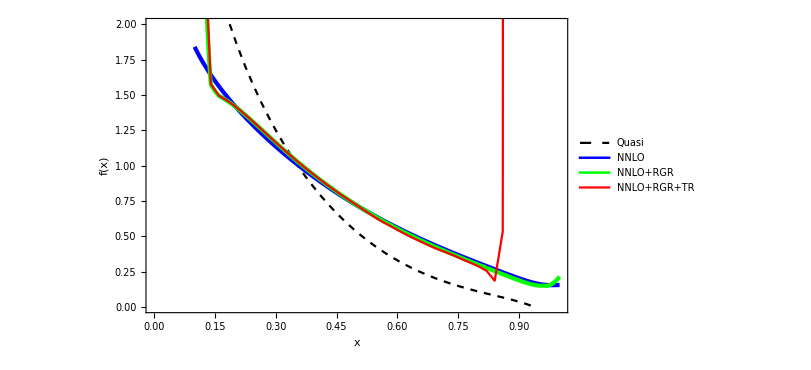

```mathematica
fig=Show[
Plot[qint[x],{x,0,1},PlotStyle->{Black,Dashed},
PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["Quasi",20]},{0.7,0.75}]],

Plot[fVint[x],{x,0.10,1},PlotStyle->{Blue,Thickness[0.005]},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc,20]},{0.7,0.65}]],

Plot[PDFRGRint[x],{x,0.12,1},PlotStyle->{Green,Thickness[0.005]},PlotRange->All,PlotLegends->Placed[{Style[PertAcc<>"+RGR",20]},{0.7,0.55}]],

Plot[PDFRGRTRint[x],{x,0.12,0.9},PlotStyle->Red,PlotRange->All,PlotLegends->Placed[{Style[PertAcc<>"+RGR+TR",20]},{0.7,0.45}]],

PlotRange->{{0,1},{0,2}},
FrameLabel->{Style["x",20],Style["f(x)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]

(*SetDirectory[NotebookDirectory[]];
Export["./pics/MCfull5NLO_add.pdf",fig]*)
```

#### μ_i=2|1-|x_i||P_z r1, μ_h=2|x_i| P_z r2, r1,r2=0.8~1.2

```mathematica
r1ls={1.2,1,0.8};
r2ls={1.2,1,0.8};
xlsf=Join[Table[N[1.0/50 i],{i,6,44}]];
Mcut=Table[If[Abs[1-y/x]<0.4,1,0],{y,xlist},{x,xlist}];
```

```mathematica
(*Resummation and variation of r1 and r2*)
PDFRGRTRls=Table[
PrintTemporary[{r1,r2}];
(*Resummation on the inversed matrix*)
PDFls={};
PDFls2={};
μils=2*(1-xlsf)*Pz*r1;
μhls=2*xlsf*Pz*r2;
Monitor[
For[i=Length[μhls],i≥1,i--,

ChM=MfixGen[μhls[[i]]];
Quiet[If[μhls[[i]]>μils[[i]],
Hm=Hmgen[μhls[[i]]];
Jmμi=Jmgen[μils[[i]]];
Jmμh=Jmgen[μhls[[i]]];
PJm=PJmgen[μhls[[i]],μils[[i]]];
Strnew=(Mcut*PJm).(Mcut*Jmμi).(Mcut*Hm);
Strnew0=(Mcut*Jmμh).(Mcut*Hm);
PDFlist=Transpose[{xlist,(ChM+Strnew-Strnew0).qV}],
PDFlist=Transpose[{xlist,ChM.qV}]
];];

ClearAll[PDFint,PDFintsys,PDFCombine];
PDFint=Interpolation[PDFlist];
PDFintsys[x_]:=(PDFint[x]+PDFint[-x])/2;
If[μhls[[i]]>μils[[i]],
PDFCombine[x_]:=PDFintsys[x],
PDFCombine[x_]:=If[Abs[x]≤ xlsf[[i]]+Δx/4,PDFintsys[x],If[xlsf[[i]]+Δx/4<Abs[x]≤ xlsf[[i]]+(3Δx)/4,((xlsf[[i]]+(3Δx)/4)-Abs[x])/(Δx/2)PDFintsys[x]+(Abs[x]-(xlsf[[i]]+Δx/4))/(Δx/2)PDFls2[[Length[μhls]-i]][x],PDFls2[[Length[μhls]-i]][x]]]
];
(*PDFCombine[x_]:=PDFintsys[x];*)

If[PertAcc=="NNLO",
AppendTo[PDFls,DGLAPNNLOx[PDFCombine,μhls[[i]],μ,Mdglapns0,Mdglapns1,Mdglapns2,xDGLAP]];AppendTo[PDFls2,DGLAPNNLOx[PDFCombine,μhls[[i]],μhls[[i-1]],Mdglapns0,Mdglapns1,Mdglapns2,xDGLAP]];,
Nothing[]
];

],
Row[{ProgressIndicator[i,{1,Length[μhls]}],i}," "]
];
Table[PDFls[[Length[xlsf]-i+1]][xlsf[[i]]],{i,1,Length[xlsf]}]
,{r1,r1ls},{r2,r2ls}]
```

General::munfl: 1/31.25^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/29.4792^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/27.7083^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/25.9375^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/24.1667^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/22.3958^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.00083^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.06095^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.12876^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.20582^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.29418^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.39651^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/31.1979^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/29.4271^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/27.6563^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/25.8854^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/24.1146^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/22.3438^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/20.625^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/18.8542^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/17.0833^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/15.3125^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/13.5417^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/11.7708^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.51641^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.65884^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.83079^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.04252^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/1.30962^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/1.65708^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/20.5729^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/18.8021^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/17.0313^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/15.2604^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.30962^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.65708^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/10.^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/8.28125^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/6.5625^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/4.84375^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.125^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/1.40625^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.1276^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.77673^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.76587^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/5.45699^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/9.00833^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/21.2407^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/4.1276^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/4.77673^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/5.76587^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/7.45699^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/11.0083^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/23.2407^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/84.7857^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.08333^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.80208^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/5.52083^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/7.23958^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/8.95833^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/86.7857^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/14.0125^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/7.22603^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/4.66509^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.32014^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.49128^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/74.0625^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/16.0125^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/9.22603^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/6.66509^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/5.32014^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/4.49128^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/10.6771^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/12.3958^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/14.1146^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/15.8333^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/17.5521^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/19.2708^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/1.92927^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/1.52311^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/1.21587^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.97533^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.7819^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.62297^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.92927^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.52311^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.21587^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/15.8854^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/17.6042^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/19.3229^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/20.9896^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/22.7083^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/24.4271^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/26.1458^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/27.8646^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/29.5833^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.49007^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.37729^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.28038^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.19622^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.12243^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.05722^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/21.0417^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/22.7604^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/24.4792^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/26.1979^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/27.9167^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/29.6354^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/31.25^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/29.4792^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/27.7083^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/25.9375^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/24.1667^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/22.3958^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.00083^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.06095^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.12876^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.20582^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.29418^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.39651^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/31.1979^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/29.4271^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/27.6563^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/25.8854^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/24.1146^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/22.3438^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/20.625^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/18.8542^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/17.0833^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/15.3125^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/13.5417^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/11.7708^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.51641^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.65884^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.83079^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.04252^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/1.30962^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/1.65708^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/20.5729^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/18.8021^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/17.0313^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/15.2604^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.30962^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.65708^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/10.^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/8.28125^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/6.5625^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/4.84375^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.125^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/1.40625^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.1276^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.77673^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.76587^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/5.45699^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/9.00833^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/21.2407^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/4.1276^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/4.77673^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/5.76587^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/7.45699^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/11.0083^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/23.2407^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/84.7857^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.08333^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.80208^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/5.52083^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/7.23958^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/8.95833^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/86.7857^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/14.0125^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/7.22603^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/4.66509^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.32014^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.49128^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/74.0625^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/16.0125^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/9.22603^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/6.66509^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/5.32014^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/4.49128^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/10.6771^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/12.3958^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/14.1146^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/15.8333^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/17.5521^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/19.2708^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/1.92927^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/1.52311^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/1.21587^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.97533^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.7819^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.62297^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.92927^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.52311^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.21587^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/15.8854^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/17.6042^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/19.3229^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/20.9896^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/22.7083^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/24.4271^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/26.1458^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/27.8646^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/29.5833^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.49007^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.37729^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.28038^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.19622^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.12243^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.05722^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/21.0417^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/22.7604^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/24.4792^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/26.1979^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/27.9167^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/29.6354^10826.5 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/31.25^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/29.4792^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/27.7083^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/25.9375^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/24.1667^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/22.3958^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.00083^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.06095^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.12876^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.20582^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.29418^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.39651^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/31.1979^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/29.4271^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/27.6563^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/25.8854^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/24.1146^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/22.3438^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/20.625^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/18.8542^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/17.0833^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/15.3125^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/13.5417^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/11.7708^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.51641^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.65884^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.83079^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.04252^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/1.30962^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/1.65708^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/20.5729^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/18.8021^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/17.0313^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/15.2604^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.30962^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.65708^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/10.^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/8.28125^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/6.5625^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/4.84375^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.125^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/1.40625^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.1276^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.77673^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.76587^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/5.45699^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/9.00833^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/21.2407^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/4.1276^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/4.77673^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/5.76587^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/7.45699^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/11.0083^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/23.2407^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/84.7857^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.08333^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.80208^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/5.52083^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/7.23958^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/8.95833^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/86.7857^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/14.0125^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/7.22603^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/4.66509^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.32014^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.49128^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/74.0625^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/16.0125^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/9.22603^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/6.66509^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/5.32014^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/4.49128^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/10.6771^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/12.3958^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/14.1146^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/15.8333^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/17.5521^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/19.2708^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/1.92927^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/1.52311^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/1.21587^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.97533^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.7819^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.62297^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.92927^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.52311^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3.21587^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/15.8854^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/17.6042^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/19.3229^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/20.9896^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/22.7083^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/24.4271^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/26.1458^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/27.8646^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/29.5833^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.49007^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.37729^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.28038^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.19622^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.12243^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.05722^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/21.0417^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/22.7604^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/24.4792^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/26.1979^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/27.9167^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/29.6354^10826.6 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{{1.54749,1.51081,1.49392,1.46092,1.41698,1.36694,1.31394,1.2598,1.20562,1.15235,1.10059,1.05045,1.00199,0.955267,0.910239,0.866897,0.825155,0.784984,0.746372,0.709296,0.670866,0.633359,0.598308,0.570447,0.539809,0.508305,0.480555,0.454019,0.427231,0.403531,0.386469,0.364049,0.338411,0.314447,0.29126,0.264895,0.235958,0.179436,0.580445},{2.86915,1.5756,1.49391,1.45952,1.41885,1.37195,1.32135,1.26898,1.21615,1.16368,1.11212,1.06195,1.01345,0.966596,0.921407,0.87788,0.835961,0.79563,0.756843,0.719551,0.683684,0.649151,0.613682,0.581178,0.549409,0.518017,0.489441,0.462086,0.434969,0.410388,0.390155,0.366874,0.341612,0.317886,0.294513,0.268741,0.240765,0.191147,0.767758},{-4.1225×10^16,-118.757,1.73884,1.47963,1.4234,1.37825,1.33078,1.28101,1.23008,1.17889,1.12814,1.07826,1.02954,0.982171,0.936318,0.892275,0.850025,0.809325,0.770142,0.732419,0.696149,0.661264,0.627713,0.595436,0.56435,0.532628,0.50249,0.473765,0.445873,0.419944,0.396604,0.372141,0.346825,0.322792,0.298899,0.273377,0.245924,0.201592,2.1256}},{{1.54894,1.51194,1.49488,1.46177,1.41773,1.36762,1.31455,1.26035,1.20612,1.1528,1.10099,1.05079,1.00229,0.955498,0.910394,0.866955,0.825083,0.784174,0.742684,0.703098,0.665276,0.626863,0.592259,0.566785,0.536437,0.504744,0.477527,0.451462,0.424556,0.400412,0.383266,0.360677,0.334669,0.310139,0.284975,0.251312,0.165808,0.466483,99.3526},{2.87247,1.5762,1.49437,1.45991,1.4192,1.37227,1.32164,1.26925,1.21639,1.1639,1.11233,1.06215,1.01363,0.96676,0.921554,0.878009,0.836071,0.795716,0.756899,0.719563,0.680876,0.642798,0.607207,0.576976,0.545529,0.514006,0.486039,0.459172,0.43193,0.406899,0.386485,0.36301,0.337376,0.313048,0.287776,0.255493,0.185736,0.536938,167.585},{-4.11861×10^16,-118.682,1.74048,1.48057,1.42419,1.37896,1.33142,1.28162,1.23065,1.17943,1.12866,1.07876,1.03002,0.982639,0.936775,0.892723,0.850467,0.809762,0.770576,0.732852,0.696582,0.661689,0.627628,0.59303,0.560038,0.528044,0.498604,0.4704,0.442388,0.416003,0.392355,0.36766,0.341966,0.317285,0.291543,0.260194,0.201357,0.722674,-2702.47}},{{1.54975,1.51256,1.4954,1.46223,1.41814,1.36798,1.31487,1.26064,1.20638,1.15303,1.10118,1.05095,1.00241,0.955564,0.910357,0.861524,0.82028,0.778168,0.734393,0.694956,0.657457,0.618452,0.584447,0.561164,0.530763,0.498085,0.470706,0.444483,0.417581,0.394125,0.377732,0.355042,0.32793,0.300709,0.254485,0.381203,0.701115,-7.19039×10^13,0.24748},{2.88097,1.57781,1.4956,1.46098,1.42016,1.37314,1.32244,1.26999,1.21709,1.16456,1.11294,1.06272,1.01417,0.967267,0.922019,0.878417,0.836336,0.794136,0.751091,0.710827,0.672343,0.633694,0.598816,0.570701,0.539244,0.506782,0.478676,0.451605,0.424272,0.399839,0.379983,0.356233,0.329224,0.301488,0.256744,0.516624,0.798762,-5.64132×10^13,0.247982},{-4.11678×10^16,-118.631,1.74128,1.48102,1.42456,1.37929,1.33173,1.2819,1.23091,1.17968,1.12889,1.07898,1.03023,0.982838,0.936964,0.8929,0.850628,0.809901,0.770668,0.73276,0.693923,0.654965,0.618536,0.585895,0.552953,0.520112,0.490568,0.462124,0.433926,0.408033,0.384716,0.359551,0.33221,0.30352,0.259844,6.40767,0.951425,-3.87066×10^13,0.248466}}}

```mathematica
PDFRGRTRintls=Table[Interpolation[Transpose[Re[{xlsf,PDFRGRTRls[[i,j]]}]],InterpolationOrder->1],{i,1,Length[r1ls]},{j,1,Length[r2ls]}];
```

InterpolatingFunction::dmval: Input value {0.100016} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

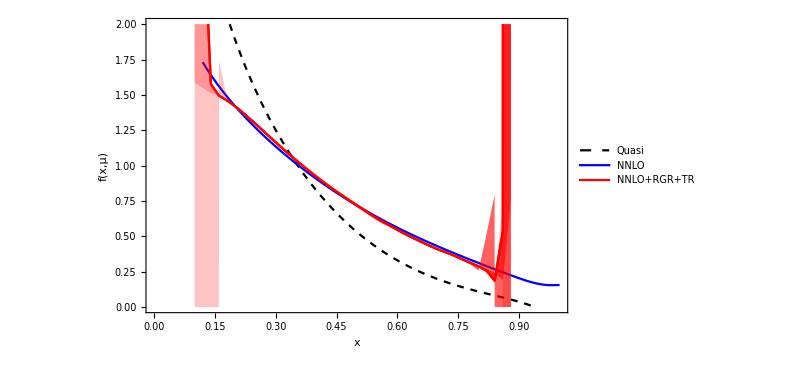

```mathematica
fig=Show[
Plot[qint[x],{x,0,1},PlotStyle->{Black,Dashed},
PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["Quasi",20]},{0.7,0.75}]],

Plot[fVint[x],{x,0.12,1},PlotStyle->Blue,PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc,20]},{0.7,0.65}]],

Plot[{PDFRGRTRintls[[2,2]][x],PDFRGRTRintls[[2,1]][x],PDFRGRTRintls[[2,3]][x]},{x,0.1,0.88},PlotStyle->{Red,Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618^3,Red]}},1->{{3},{Opacity[0.618^3,Red]}}},PlotRange->{{0,1},{0,2}}],

Plot[{PDFRGRTRintls[[2,2]][x],PDFRGRTRintls[[1,2]][x],PDFRGRTRintls[[3,2]][x]},{x,0.1,0.88},PlotStyle->{Red,Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618,Red]}},1->{{3},{Opacity[0.618,Red]}}},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc<>"+RGR+TR",20]},{0.7,0.55}]],

PlotRange->{{0,1},{0,2}},
FrameLabel->{Style["x",20],Style["f(x,μ)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]
```

#### μ_i=2|1-|x_i||P_z, μ_i0=2|x_i|P_z, μ_h=2|x_i| P_z, |1-ξ|<γ, γ=0.3~0.5

```mathematica
γls={0.3,0.4,0.5};
xlsf=Table[N[1.0/50 i],{i,6,44}];
```

```mathematica
(*Resummation and variation of r1 and r2*)
PDFRGRTRls=Table[
PrintTemporary[{γ}];
(*Resummation on the inversed matrix*)
Mcut=Table[If[Abs[1-y/x]<γ,1,0],{y,xlist},{x,xlist}];
PDFls={};
PDFls2={};
μils=2*(1-xlsf)*Pz;
μhls=2*xlsf*Pz;
Monitor[
For[i=Length[μhls],i≥1,i--,

ChM=MfixGen[μhls[[i]]];
Quiet[If[μhls[[i]]>μils[[i]],
Hm=Hmgen[μhls[[i]]];
Jmμi=Jmgen[μils[[i]]];
Jmμh=Jmgen[μhls[[i]]];
PJm=PJmgen[μhls[[i]],μils[[i]]];
Strnew=(Mcut*PJm).(Mcut*Jmμi).(Mcut*Hm);
Strnew0=(Mcut*Jmμh).(Mcut*Hm);
PDFlist=Transpose[{xlist,(ChM+Strnew-Strnew0).qV}],
PDFlist=Transpose[{xlist,ChM.qV}]
];];

PDFint=Interpolation[PDFlist];
PDFintsys[x_]:=(PDFint[x]+PDFint[-x])/2;
If[μhls[[i]]>μils[[i]],
PDFCombine[x_]:=PDFintsys[x],
PDFCombine[x_]:=If[Abs[x]≤ xlsf[[i]]+Δx/4,PDFintsys[x],If[xlsf[[i]]+Δx/4<Abs[x]≤ xlsf[[i]]+(3Δx)/4,((xlsf[[i]]+(3Δx)/4)-Abs[x])/(Δx/2)PDFintsys[x]+(Abs[x]-(xlsf[[i]]+Δx/4))/(Δx/2)PDFls2[[Length[μhls]-i]][x],PDFls2[[Length[μhls]-i]][x]]]
];
(*PDFCombine[x_]:=PDFintsys[x];*)

If[PertAcc=="NNLO",
AppendTo[PDFls,DGLAPNNLOx[PDFCombine,μhls[[i]],μ,Mdglapns0,Mdglapns1,Mdglapns2,xDGLAP]];AppendTo[PDFls2,DGLAPNNLOx[PDFCombine,μhls[[i]],μhls[[i-1]],Mdglapns0,Mdglapns1,Mdglapns2,xDGLAP]];,
Nothing[]
];

],
Row[{ProgressIndicator[i,{1,Length[μhls]}],i}," "]
];
Table[PDFls[[Length[xlsf]-i+1]][xlsf[[i]]],{i,1,Length[xlsf]}]
,{γ,γls}]
```

{{2.87201,1.57612,1.49431,1.45985,1.41915,1.37222,1.3216,1.26921,1.21636,1.16387,1.1123,1.06212,1.0136,0.966734,0.92153,0.877987,0.836051,0.795698,0.756883,0.71955,0.680432,0.643025,0.607671,0.575411,0.543065,0.511929,0.482568,0.453918,0.425788,0.398023,0.375017,0.352004,0.329869,0.303954,0.281777,0.257651,0.225072,0.216684,50.0226},{2.87247,1.5762,1.49437,1.45991,1.4192,1.37227,1.32164,1.26925,1.21639,1.1639,1.11233,1.06215,1.01363,0.96676,0.921554,0.878009,0.836071,0.795716,0.756899,0.719563,0.680876,0.642798,0.607207,0.576976,0.545529,0.514006,0.486039,0.459172,0.43193,0.406899,0.386485,0.36301,0.337376,0.313048,0.287776,0.255493,0.185736,0.536938,167.585},{2.8729,1.57629,1.49443,1.45997,1.41925,1.37231,1.32168,1.26928,1.21643,1.16394,1.11236,1.06218,1.01365,0.966786,0.921578,0.878031,0.83609,0.795732,0.756909,0.719562,0.681243,0.6437,0.612614,0.578363,0.545404,0.520762,0.49,0.460592,0.439442,0.410548,0.382905,0.363238,0.335592,0.307905,0.284372,0.241268,0.101109,1.09183,308.995}}

```mathematica
PDFRGRTRintls2=Table[Interpolation[Transpose[Re[{xlsf,PDFRGRTRls[[i]]}]],InterpolationOrder->1],{i,1,Length[γls]}];
```

InterpolatingFunction::dmval: Input value {0.100016} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

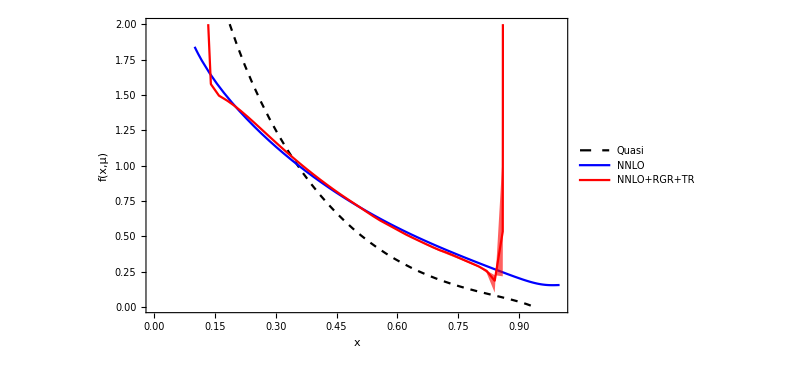

```mathematica
fig=Show[
Plot[qint[x],{x,0,1},PlotStyle->{Black,Dashed},
PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["Quasi",20]},{0.7,0.75}]],

Plot[fVint[x],{x,0.10,1},PlotStyle->Blue,PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc,20]},{0.7,0.65}]],

Plot[{PDFRGRTRintls2[[2]][x],PDFRGRTRintls2[[1]][x],PDFRGRTRintls2[[3]][x]},{x,0.1,0.9},PlotStyle->{Red,Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618,Red]}},1->{{3},{Opacity[0.618,Red]}}},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc<>"+RGR+TR",20]},{0.7,0.55}]],

PlotRange->{{0,1},{0,2}},
FrameLabel->{Style["x",20],Style["f(x,μ)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]

(*SetDirectory[NotebookDirectory[]];
Export["./pics/MCfull6err2_add.pdf",fig]*)
```

## NLO with renormalon

### Lattice Data Pion Valence Quasi - PDF, Pz=1.9 GeV, zs=0.12fm, λ_L=25

```mathematica
(*
The data is generated by BNL/ANL Collaborations, Gao:2021dbh
Renormalized based on the RGR+LRR method, Zhang:2023bxs
*)
```

```mathematica
Pz=1.94;(*GeV*)
zs=0.12/GeVfm;(*GeV^-1*)
```

```mathematica
qls={{-2.,0.004644373353200662},{-1.99,0.004120247847633056},{-1.98,0.003622067087287381},{-1.97,0.0031552223149979},{-1.96,0.002726220362994065},{-1.95,0.002332121946113358},{-1.94,0.0019748105696102128},{-1.93,0.0016617946317518128},{-1.92,0.0013896498468505209},{-1.91,0.001157969030572405},{-1.9,0.0009740062784405524},{-1.89,0.0008343069837817357},{-1.88,0.0007354910726053484},{-1.87,0.0006844474334537591},{-1.86,0.0006775322836966953},{-1.85,0.0007093746490651379},{-1.84,0.0007848304657079239},{-1.83,0.0009010306765860066},{-1.82,0.0010500511427830594},{-1.81,0.0012347748938322317},{-1.8,0.0014529691648524812},{-1.79,0.001695074247695391},{-1.78,0.0019608772861017146},{-1.77,0.0022493261730182164},{-1.76,0.002548904375507088},{-1.75,0.0028570969569776993},{-1.74,0.0031734135755238676},{-1.73,0.003485305751241066},{-1.72,0.003787860492555417},{-1.71,0.004080714570753909},{-1.7,0.0043513415591125565},{-1.69,0.00459209780747},{-1.68,0.004802930805205951},{-1.67,0.004971973589585376},{-1.66,0.0050893807375176625},{-1.65,0.0051544301651739125},{-1.64,0.0051572528883037675},{-1.63,0.0050857962876900975},{-1.62,0.004939638608088999},{-1.61,0.0047103710762440385},{-1.6,0.004384588087735983},{-1.59,0.003961638559377615},{-1.58,0.0034355478567254134},{-1.57,0.0027923727101677306},{-1.56,0.0020307899346212865},{-1.55,0.001147653353127118},{-1.54,0.0001293662115165748},{-1.53,-0.0010262053436745217},{-1.52,-0.002319241626571331},{-1.51,-0.003762070898562308},{-1.5,-0.00535767461611031},{-1.49,-0.007103322325419803},{-1.48,-0.009009173627881811},{-1.47,-0.011078971693766839},{-1.46,-0.013307310981559016},{-1.45,-0.01570136328212513},{-1.44,-0.0182654114646309},{-1.43,-0.020991762810628253},{-1.42,-0.02388391683318669},{-1.41,-0.026946333224345465},{-1.4,-0.030169528227263636},{-1.39,-0.03355282186583401},{-1.38,-0.03710035027897443},{-1.37,-0.04081071753848808},{-1.36,-0.04465944879214011},{-1.35,-0.04865963860632827},{-1.34,-0.052799840226409746},{-1.33,-0.05707031143306075},{-1.32,-0.061472539521033896},{-1.31,-0.06599476622458914},{-1.3,-0.07062273776425468},{-1.29,-0.07535273029596794},{-1.28,-0.08017913633450793},{-1.27,-0.08507972027317055},{-1.26,-0.09004977201197047},{-1.25,-0.09507580386853634},{-1.24,-0.10013643453606268},{-1.23,-0.1052217762493435},{-1.22,-0.11031842068337755},{-1.21,-0.11539884898458205},{-1.2,-0.12044650543362649},{-1.19,-0.12544472751274555},{-1.18,-0.1303598348657722},{-1.17,-0.1351735733812622},{-1.16,-0.13984482290530456},{-1.15,-0.14433717761958592},{-1.14,-0.14860599638320865},{-1.13,-0.15260865725942266},{-1.12,-0.15627783779791632},{-1.11,-0.15953306926178973},{-1.1,-0.16228714588271892},{-1.09,-0.16441456147949368},{-1.08,-0.16574791938649297},{-1.07,-0.16608017752841578},{-1.06,-0.16512238403855972},{-1.05,-0.16247228616306125},{-1.04,-0.1576079570670807},{-1.03,-0.1498745549865596},{-1.02,-0.13856750481624514},{-1.01,-0.12329118093713683},{-1.,-0.10452791672037298},{-0.99,-0.08386577478628733},{-0.98,-0.06335779275286002},{-0.97,-0.044487529193872555},{-0.96,-0.027791608369410428},{-0.95,-0.013222288017471662},{-0.94,-0.0005060197676422379},{-0.93,0.010712926418813828},{-0.92,0.020747082549468394},{-0.91,0.029838009883754957},{-0.9,0.03821136232499601},{-0.89,0.0460465568700808},{-0.88,0.05346537832030689},{-0.87,0.06059246869266078},{-0.86,0.06753496522164032},{-0.85,0.0743557313427976},{-0.84,0.08112836368178805},{-0.83,0.0879271737670217},{-0.82,0.09478793608711844},{-0.81,0.10175642926745493},{-0.8,0.10889143693088607},{-0.79,0.11621674758268581},{-0.78,0.1237610583222274},{-0.77,0.13157504382591872},{-0.76,0.1396783280519504},{-0.75,0.14808810060910665},{-0.74,0.1568499582295041},{-0.73,0.16598381259698758},{-0.72,0.17549878312097195},{-0.71,0.18543635329779484},{-0.7,0.19581939592572234},{-0.69,0.20665153845175915},{-0.68,0.2179701214189261},{-0.67,0.22980255026321988},{-0.66,0.24214923764638413},{-0.65,0.25504292135001416},{-0.64,0.2685163194493533},{-0.63,0.28256884463310383},{-0.62,0.2972271045353138},{-0.61,0.3125311593245419},{-0.6,0.32848076047689745},{-0.59,0.34509795809233895},{-0.58,0.3624260434801411},{-0.57,0.38046917194148},{-0.56,0.3992438019869307},{-0.55,0.4187982160626459},{-0.54,0.43914024161844556},{-0.53,0.46028312747525324},{-0.52,0.4822784905078693},{-0.51,0.5051420233327284},{-0.5,0.5288815511766826},{-0.49,0.5535517147724702},{-0.48,0.5791791881504709},{-0.47,0.6057682632765653},{-0.46,0.6333745418103949},{-0.45,0.6620379331888059},{-0.44,0.6917625152625423},{-0.43,0.7226035104236992},{-0.42,0.7546157172441825},{-0.41,0.78780717183097},{-0.4,0.8222324759737083},{-0.39,0.8579628404685727},{-0.38,0.8950151875900143},{-0.37,0.9334445457962022},{-0.36,0.9733404584277825},{-0.35,1.0147346620849456},{-0.34,1.05768518912032},{-0.33,1.1023027626430033},{-0.32,1.1486414268852312},{-0.31,1.1967701625144844},{-0.3,1.246818645446664},{-0.29,1.2988768175409042},{-0.28,1.3530252429364402},{-0.27,1.409432971004116},{-0.26,1.4682327591165751},{-0.25,1.5295336404418816},{-0.24,1.5935488304240892},{-0.23,1.6604769430098891},{-0.22,1.7304757454739113},{-0.21,1.8038230429831537},{-0.2,1.8808140737409953},{-0.19,1.961688885024415},{-0.18,2.046824052821365},{-0.17,2.1366600426183044},{-0.16,2.231574775658292},{-0.15,2.3320820112281115},{-0.14,2.439006731842744},{-0.13,2.552529992013758},{-0.12,2.673751967916616},{-0.11,2.8037487067637175},{-0.1,2.9433866951050964},{-0.09,3.0936367993617053},{-0.08,3.2556429738423134},{-0.07,3.4302252428984916},{-0.06,3.617879799994142},{-0.05,3.8181709368900414},{-0.04,4.027353378189677},{-0.03,4.235688352317414},{-0.02,4.423972412482997},{-0.01,4.56087468343495},{0,4.612277188558619},{0.01,4.56087468343495},{0.02,4.423972412482997},{0.03,4.235688352317414},{0.04,4.027353378189677},{0.05,3.8181709368900414},{0.06,3.617879799994142},{0.07,3.4302252428984916},{0.08,3.2556429738423134},{0.09,3.0936367993617053},{0.1,2.9433866951050964},{0.11,2.8037487067637175},{0.12,2.673751967916616},{0.13,2.552529992013758},{0.14,2.439006731842744},{0.15,2.3320820112281115},{0.16,2.231574775658292},{0.17,2.1366600426183044},{0.18,2.046824052821365},{0.19,1.961688885024415},{0.2,1.8808140737409953},{0.21,1.8038230429831537},{0.22,1.7304757454739113},{0.23,1.6604769430098891},{0.24,1.5935488304240892},{0.25,1.5295336404418816},{0.26,1.4682327591165751},{0.27,1.409432971004116},{0.28,1.3530252429364402},{0.29,1.2988768175409042},{0.3,1.246818645446664},{0.31,1.1967701625144844},{0.32,1.1486414268852312},{0.33,1.1023027626430033},{0.34,1.05768518912032},{0.35,1.0147346620849456},{0.36,0.9733404584277825},{0.37,0.9334445457962022},{0.38,0.8950151875900143},{0.39,0.8579628404685727},{0.4,0.8222324759737083},{0.41,0.78780717183097},{0.42,0.7546157172441825},{0.43,0.7226035104236992},{0.44,0.6917625152625423},{0.45,0.6620379331888059},{0.46,0.6333745418103949},{0.47,0.6057682632765653},{0.48,0.5791791881504709},{0.49,0.5535517147724702},{0.5,0.5288815511766826},{0.51,0.5051420233327284},{0.52,0.4822784905078693},{0.53,0.46028312747525324},{0.54,0.43914024161844556},{0.55,0.4187982160626459},{0.56,0.3992438019869307},{0.57,0.38046917194148},{0.58,0.3624260434801411},{0.59,0.34509795809233895},{0.6,0.32848076047689745},{0.61,0.3125311593245419},{0.62,0.2972271045353138},{0.63,0.28256884463310383},{0.64,0.2685163194493533},{0.65,0.25504292135001416},{0.66,0.24214923764638413},{0.67,0.22980255026321988},{0.68,0.2179701214189261},{0.69,0.20665153845175915},{0.7,0.19581939592572234},{0.71,0.18543635329779484},{0.72,0.17549878312097195},{0.73,0.16598381259698758},{0.74,0.1568499582295041},{0.75,0.14808810060910665},{0.76,0.1396783280519504},{0.77,0.13157504382591872},{0.78,0.1237610583222274},{0.79,0.11621674758268581},{0.8,0.10889143693088607},{0.81,0.10175642926745493},{0.82,0.09478793608711844},{0.83,0.0879271737670217},{0.84,0.08112836368178805},{0.85,0.0743557313427976},{0.86,0.06753496522164032},{0.87,0.06059246869266078},{0.88,0.05346537832030689},{0.89,0.0460465568700808},{0.9,0.03821136232499601},{0.91,0.029838009883754957},{0.92,0.020747082549468394},{0.93,0.010712926418813828},{0.94,-0.0005060197676422379},{0.95,-0.013222288017471662},{0.96,-0.027791608369410428},{0.97,-0.044487529193872555},{0.98,-0.06335779275286002},{0.99,-0.08386577478628733},{1.,-0.10452791672037298},{1.01,-0.12329118093713683},{1.02,-0.13856750481624514},{1.03,-0.1498745549865596},{1.04,-0.1576079570670807},{1.05,-0.16247228616306125},{1.06,-0.16512238403855972},{1.07,-0.16608017752841578},{1.08,-0.16574791938649297},{1.09,-0.16441456147949368},{1.1,-0.16228714588271892},{1.11,-0.15953306926178973},{1.12,-0.15627783779791632},{1.13,-0.15260865725942266},{1.14,-0.14860599638320865},{1.15,-0.14433717761958592},{1.16,-0.13984482290530456},{1.17,-0.1351735733812622},{1.18,-0.1303598348657722},{1.19,-0.12544472751274555},{1.2,-0.12044650543362649},{1.21,-0.11539884898458205},{1.22,-0.11031842068337755},{1.23,-0.1052217762493435},{1.24,-0.10013643453606268},{1.25,-0.09507580386853634},{1.26,-0.09004977201197047},{1.27,-0.08507972027317055},{1.28,-0.08017913633450793},{1.29,-0.07535273029596794},{1.3,-0.07062273776425468},{1.31,-0.06599476622458914},{1.32,-0.061472539521033896},{1.33,-0.05707031143306075},{1.34,-0.052799840226409746},{1.35,-0.04865963860632827},{1.36,-0.04465944879214011},{1.37,-0.04081071753848808},{1.38,-0.03710035027897443},{1.39,-0.03355282186583401},{1.4,-0.030169528227263636},{1.41,-0.026946333224345465},{1.42,-0.02388391683318669},{1.43,-0.020991762810628253},{1.44,-0.0182654114646309},{1.45,-0.01570136328212513},{1.46,-0.013307310981559016},{1.47,-0.011078971693766839},{1.48,-0.009009173627881811},{1.49,-0.007103322325419803},{1.5,-0.00535767461611031},{1.51,-0.003762070898562308},{1.52,-0.002319241626571331},{1.53,-0.0010262053436745217},{1.54,0.0001293662115165748},{1.55,0.001147653353127118},{1.56,0.0020307899346212865},{1.57,0.0027923727101677306},{1.58,0.0034355478567254134},{1.59,0.003961638559377615},{1.6,0.004384588087735983},{1.61,0.0047103710762440385},{1.62,0.004939638608088999},{1.63,0.0050857962876900975},{1.64,0.0051572528883037675},{1.65,0.0051544301651739125},{1.66,0.0050893807375176625},{1.67,0.004971973589585376},{1.68,0.004802930805205951},{1.69,0.00459209780747},{1.7,0.0043513415591125565},{1.71,0.004080714570753909},{1.72,0.003787860492555417},{1.73,0.003485305751241066},{1.74,0.0031734135755238676},{1.75,0.0028570969569776993},{1.76,0.002548904375507088},{1.77,0.0022493261730182164},{1.78,0.0019608772861017146},{1.79,0.001695074247695391},{1.8,0.0014529691648524812},{1.81,0.0012347748938322317},{1.82,0.0010500511427830594},{1.83,0.0009010306765860066},{1.84,0.0007848304657079239},{1.85,0.0007093746490651379},{1.86,0.0006775322836966953},{1.87,0.0006844474334537591},{1.88,0.0007354910726053484},{1.89,0.0008343069837817357},{1.9,0.0009740062784405524},{1.91,0.001157969030572405},{1.92,0.0013896498468505209},{1.93,0.0016617946317518128},{1.94,0.0019748105696102128},{1.95,0.002332121946113358},{1.96,0.002726220362994065},{1.97,0.0031552223149979},{1.98,0.003622067087287381},{1.99,0.004120247847633056},{2.,0.004644373353200662}};
```

### Δx=0.005, L=3, γ=0.4

```mathematica
μ=2;(*GeV*)(*Factorization Scale*)
PertAcc="NLO+LRR";
```

#### Discretization

```mathematica
qlsgf=GaussianFilter[qls,{{4,0}}];
qinttest=Interpolation[qlsgf];
ClearAll[qint];
qint[x_]:=If[Abs[x]<2,qinttest[x],qinttest[2]Exp[-(Abs[x]-2)]];
Plot[qint[x],{x,-4,4},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
L=3;
Δx=0.005;(*Discretization*)
xlist=Join[Table[x,{x,-L,-Δx,Δx}],Table[x,{x,Δx,L,Δx}]];
qV=Table[qint[x],{x,xlist}];
```

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

#### Fixed order results

```mathematica
(*Matrix Elements generation*)
```

```mathematica
If[PertAcc=="NLO+LRR",
MCratio1pluswμ=SubMGen[Cratio1pluswμ,xlist,Pz,zs];
MCratio1pluswoμ=SubMGen[Cratio1pluswoμ,xlist,Pz,zs];
MChybrid1plus=SubMGen[Chybrid1plus,xlist,Pz,zs];
MCz=SubMGen[Cz,xlist,Pz,zs];
MfixGen[μ_]:=Module[{nf,rsumPV,r0,C1,C1i},
nf=3;
rsumPV=dPVasym[1,μ,nf,αsNLO[[1]][μ]];
r0=rnasym[0,1,μ,nf]*αsNLO[[1]][μ];
C1=(αsNLO[[1]][μ]*CF)/(2Pi)((-Log[(μ/Pz)^2])MCratio1pluswμ+MCratio1pluswoμ+MChybrid1plus);
C1i=-C1;
(IdentityMatrix[Length[xlist]]+C1i+r0*MCz).MatrixExp[-MCz*rsumPV]
],
Nothing[];
]
```

```mathematica
(*Calculation*)
```

```mathematica
ChM=MfixGen[μ];
fVfixed=ChM.qV;
(fVfixed+Reverse[fVfixed])/2
fVint=Interpolation[Transpose[{xlist,(fVfixed+Reverse[fVfixed])/2}]];
```

{-0.0443261,-0.0396366,-0.0373117,-0.0357748,-0.0346319,-0.0337252,-0.0329759,-0.0323387,-0.0317854,-0.0312972,-0.0308608,-0.0304666,-0.0301075,-0.0297778,-0.0294732,-0.0291903,-0.0289261,-0.0286783,-0.028445,-0.0282245,-0.0280155,-0.0278167,-0.0276271,-0.0274458,-0.0272721,-0.0271052,-0.0269445,-0.0267894,-0.0266396,-0.0264945,-0.0263538,-0.0262171,-0.0260841,-0.0259546,-0.0258281,-0.0257046,-0.0255837,-0.0254653,-0.0253492,-0.0252352,-0.0251231,-0.0250129,-0.0249043,-0.0247973,-0.0246917,-0.0245874,-0.0244843,-0.0243823,-0.0242813,-0.0241813,-0.0240821,-0.0239836,-0.0238859,-0.0237888,-0.0236923,-0.0235963,-0.0235007,-0.0234056,-0.0233108,-0.0232163,-0.023122,-0.0230279,-0.022934,-0.0228403,-0.0227466,-0.0226529,-0.0225593,-0.0224656,-0.0223719,-0.0222781,-0.0221842,-0.0220901,-0.0219959,-0.0219014,-0.0218067,-0.0217118,-0.0216166,-0.0215211,-0.0214253,-0.0213292,-0.0212327,-0.0211358,-0.0210385,-0.0209408,-0.0208427,-0.0207441,-0.020645,-0.0205454,-0.0204454,-0.0203448,-0.0202437,-0.020142,-0.0200398,-0.019937,-0.0198337,-0.0197297,-0.0196251,-0.0195199,-0.019414,-0.0193075,-0.0192004,-0.0190926,-0.018984,-0.0188749,-0.018765,-0.0186544,-0.018543,-0.018431,-0.0183182,-0.0182047,-0.0180904,-0.0179754,-0.0178596,-0.017743,-0.0176257,-0.0175075,-0.0173886,-0.0172689,-0.0171483,-0.017027,-0.0169048,-0.0167818,-0.016658,-0.0165333,-0.0164078,-0.0162815,-0.0161543,-0.0160263,-0.0158974,-0.0157677,-0.0156371,-0.0155056,-0.0153733,-0.0152401,-0.0151061,-0.0149711,-0.0148353,-0.0146987,-0.0145611,-0.0144227,-0.0142834,-0.0141433,-0.0140023,-0.0138604,-0.0137176,-0.013574,-0.0134295,-0.0132841,-0.0131379,-0.0129909,-0.0128429,-0.0126942,-0.0125446,-0.0123941,-0.0122429,-0.0120908,-0.0119378,-0.0117841,-0.0116296,-0.0114743,-0.0113182,-0.0111613,-0.0110036,-0.0108452,-0.0106861,-0.0105262,-0.0103656,-0.0102043,-0.0100422,-0.00987952,-0.00971614,-0.00955209,-0.0093874,-0.00922208,-0.00905613,-0.00888957,-0.00872241,-0.00855468,-0.00838636,-0.00821749,-0.00804806,-0.00787809,-0.00770759,-0.00753655,-0.00736498,-0.00719289,-0.00702028,-0.00684713,-0.00667345,-0.00649922,-0.00632443,-0.00614907,-0.00597312,-0.00579654,-0.00561931,-0.00544141,-0.00526278,-0.00508339,-0.0049032,-0.00472214,-0.00454018,-0.00435723,-0.00417326,-0.00398818,-0.00380193,-0.00361445,-0.00342565,-0.00323547,-0.00304383,-0.00285065,-0.00265587,-0.00245942,-0.00226123,-0.00206122,-0.00185935,-0.00165554,-0.00144976,-0.00124195,-0.00103207,-0.000820095,-0.000605987,-0.000389729,-0.00017131,0.0000492759,0.000272024,0.000496923,0.000723951,0.00095308,0.00118427,0.00141748,0.00165264,0.00188971,0.00212859,0.00236922,0.0026115,0.00285533,0.00310062,0.00334724,0.00359507,0.00384398,0.00409385,0.00434452,0.00459585,0.00484768,0.00509986,0.0053522,0.00560456,0.00585673,0.00610856,0.00635984,0.0066104,0.00686004,0.00710856,0.00735576,0.00760146,0.00784544,0.00808751,0.00832745,0.00856507,0.00880017,0.00903254,0.00926197,0.00948828,0.00971125,0.00993069,0.0101464,0.0103582,0.0105659,0.0107694,0.0109683,0.0111627,0.0113522,0.0115368,0.0117162,0.0118904,0.0120592,0.0122224,0.01238,0.0125318,0.0126777,0.0128176,0.0129514,0.0130791,0.0132005,0.0133157,0.0134246,0.0135271,0.0136232,0.0137129,0.0137963,0.0138733,0.013944,0.0140084,0.0140667,0.0141188,0.0141648,0.0142049,0.0142393,0.014268,0.0142911,0.014309,0.0143218,0.0143296,0.0143327,0.0143315,0.014326,0.0143167,0.0143038,0.0142877,0.0142687,0.0142471,0.0142235,0.014198,0.0141713,0.0141438,0.0141158,0.014088,0.0140608,0.0140348,0.0140106,0.0139886,0.0139696,0.0139542,0.013943,0.0139367,0.0139361,0.0139417,0.0139545,0.0139752,0.0140046,0.0140435,0.0140928,0.0141534,0.0142261,0.014312,0.014412,0.0145271,0.0146583,0.0148066,0.0149732,0.0151592,0.0153656,0.0155937,0.0158447,0.0161197,0.01642,0.0167469,0.0171018,0.0174859,0.0179006,0.0183473,0.0188274,0.0193424,0.0198937,0.0204828,0.0211113,0.0217806,0.0224924,0.0232482,0.0240496,0.0248982,0.0257957,0.0267435,0.0277435,0.0287971,0.029906,0.0310719,0.0322963,0.0335807,0.0349268,0.036336,0.0378099,0.0393498,0.0409571,0.0426331,0.0443791,0.0461962,0.0480855,0.0500478,0.0520842,0.0541952,0.0563816,0.0586437,0.0609819,0.0633964,0.0658871,0.0684538,0.0710964,0.0738141,0.0766064,0.0794724,0.0824109,0.0854209,0.0885008,0.0916491,0.0948641,0.0981439,0.101486,0.10489,0.108351,0.111869,0.11544,0.119062,0.122733,0.126449,0.13021,0.134011,0.13785,0.141726,0.145634,0.149575,0.153544,0.15754,0.161561,0.165605,0.169671,0.173756,0.17786,0.181981,0.186119,0.190271,0.194438,0.198618,0.202812,0.207019,0.211239,0.215472,0.219717,0.223975,0.228247,0.232533,0.236833,0.241149,0.24548,0.249827,0.254193,0.258577,0.26298,0.267404,0.27185,0.276319,0.280812,0.285331,0.289877,0.294451,0.299055,0.303689,0.308357,0.313058,0.317795,0.322569,0.327381,0.332233,0.337126,0.342063,0.347044,0.352071,0.357146,0.362271,0.367446,0.372673,0.377954,0.383291,0.388686,0.394139,0.399652,0.405227,0.410867,0.416571,0.422342,0.428183,0.434093,0.440076,0.446132,0.452264,0.458474,0.464762,0.471132,0.477584,0.48412,0.490744,0.497455,0.504258,0.511152,0.518141,0.525226,0.53241,0.539694,0.547081,0.554574,0.562173,0.569883,0.577704,0.58564,0.593693,0.601865,0.610159,0.618578,0.627125,0.635802,0.644613,0.653559,0.662645,0.671874,0.681248,0.690771,0.700447,0.710278,0.720269,0.730424,0.740745,0.751237,0.761905,0.772752,0.783783,0.795001,0.806412,0.818021,0.829831,0.841849,0.854079,0.866526,0.879197,0.892095,0.905229,0.918602,0.932222,0.946094,0.960225,0.974622,0.989291,1.00424,1.01948,1.035,1.05083,1.06697,1.08343,1.10021,1.11733,1.13478,1.15259,1.17076,1.1893,1.20821,1.22751,1.24721,1.26731,1.28784,1.30878,1.33017,1.35201,1.3743,1.39706,1.42031,1.44404,1.46829,1.49304,1.51833,1.54416,1.57054,1.59749,1.62503,1.65316,1.6819,1.71127,1.74129,1.77198,1.80335,1.83544,1.86826,1.90184,1.93622,1.97143,2.00751,2.04452,2.0825,2.12153,2.16168,2.20306,2.24575,2.28991,2.3357,2.38331,2.43299,2.48504,2.53983,2.59785,2.65972,2.72621,2.79839,2.87766,2.96598,3.06614,3.18224,3.32069,3.49211,3.71581,4.03178,4.54291,5.65979,5.65979,4.54291,4.03178,3.71581,3.49211,3.32069,3.18224,3.06614,2.96598,2.87766,2.79839,2.72621,2.65972,2.59785,2.53983,2.48504,2.43299,2.38331,2.3357,2.28991,2.24575,2.20306,2.16168,2.12153,2.0825,2.04452,2.00751,1.97143,1.93622,1.90184,1.86826,1.83544,1.80335,1.77198,1.74129,1.71127,1.6819,1.65316,1.62503,1.59749,1.57054,1.54416,1.51833,1.49304,1.46829,1.44404,1.42031,1.39706,1.3743,1.35201,1.33017,1.30878,1.28784,1.26731,1.24721,1.22751,1.20821,1.1893,1.17076,1.15259,1.13478,1.11733,1.10021,1.08343,1.06697,1.05083,1.035,1.01948,1.00424,0.989291,0.974622,0.960225,0.946094,0.932222,0.918602,0.905229,0.892095,0.879197,0.866526,0.854079,0.841849,0.829831,0.818021,0.806412,0.795001,0.783783,0.772752,0.761905,0.751237,0.740745,0.730424,0.720269,0.710278,0.700447,0.690771,0.681248,0.671874,0.662645,0.653559,0.644613,0.635802,0.627125,0.618578,0.610159,0.601865,0.593693,0.58564,0.577704,0.569883,0.562173,0.554574,0.547081,0.539694,0.53241,0.525226,0.518141,0.511152,0.504258,0.497455,0.490744,0.48412,0.477584,0.471132,0.464762,0.458474,0.452264,0.446132,0.440076,0.434093,0.428183,0.422342,0.416571,0.410867,0.405227,0.399652,0.394139,0.388686,0.383291,0.377954,0.372673,0.367446,0.362271,0.357146,0.352071,0.347044,0.342063,0.337126,0.332233,0.327381,0.322569,0.317795,0.313058,0.308357,0.303689,0.299055,0.294451,0.289877,0.285331,0.280812,0.276319,0.27185,0.267404,0.26298,0.258577,0.254193,0.249827,0.24548,0.241149,0.236833,0.232533,0.228247,0.223975,0.219717,0.215472,0.211239,0.207019,0.202812,0.198618,0.194438,0.190271,0.186119,0.181981,0.17786,0.173756,0.169671,0.165605,0.161561,0.15754,0.153544,0.149575,0.145634,0.141726,0.13785,0.134011,0.13021,0.126449,0.122733,0.119062,0.11544,0.111869,0.108351,0.10489,0.101486,0.0981439,0.0948641,0.0916491,0.0885008,0.0854209,0.0824109,0.0794724,0.0766064,0.0738141,0.0710964,0.0684538,0.0658871,0.0633964,0.0609819,0.0586437,0.0563816,0.0541952,0.0520842,0.0500478,0.0480855,0.0461962,0.0443791,0.0426331,0.0409571,0.0393498,0.0378099,0.036336,0.0349268,0.0335807,0.0322963,0.0310719,0.029906,0.0287971,0.0277435,0.0267435,0.0257957,0.0248982,0.0240496,0.0232482,0.0224924,0.0217806,0.0211113,0.0204828,0.0198937,0.0193424,0.0188274,0.0183473,0.0179006,0.0174859,0.0171018,0.0167469,0.01642,0.0161197,0.0158447,0.0155937,0.0153656,0.0151592,0.0149732,0.0148066,0.0146583,0.0145271,0.014412,0.014312,0.0142261,0.0141534,0.0140928,0.0140435,0.0140046,0.0139752,0.0139545,0.0139417,0.0139361,0.0139367,0.013943,0.0139542,0.0139696,0.0139886,0.0140106,0.0140348,0.0140608,0.014088,0.0141158,0.0141438,0.0141713,0.014198,0.0142235,0.0142471,0.0142687,0.0142877,0.0143038,0.0143167,0.014326,0.0143315,0.0143327,0.0143296,0.0143218,0.014309,0.0142911,0.014268,0.0142393,0.0142049,0.0141648,0.0141188,0.0140667,0.0140084,0.013944,0.0138733,0.0137963,0.0137129,0.0136232,0.0135271,0.0134246,0.0133157,0.0132005,0.0130791,0.0129514,0.0128176,0.0126777,0.0125318,0.01238,0.0122224,0.0120592,0.0118904,0.0117162,0.0115368,0.0113522,0.0111627,0.0109683,0.0107694,0.0105659,0.0103582,0.0101464,0.00993069,0.00971125,0.00948828,0.00926197,0.00903254,0.00880017,0.00856507,0.00832745,0.00808751,0.00784544,0.00760146,0.00735576,0.00710856,0.00686004,0.0066104,0.00635984,0.00610856,0.00585673,0.00560456,0.0053522,0.00509986,0.00484768,0.00459585,0.00434452,0.00409385,0.00384398,0.00359507,0.00334724,0.00310062,0.00285533,0.0026115,0.00236922,0.00212859,0.00188971,0.00165264,0.00141748,0.00118427,0.00095308,0.000723951,0.000496923,0.000272024,0.0000492759,-0.00017131,-0.000389729,-0.000605987,-0.000820095,-0.00103207,-0.00124195,-0.00144976,-0.00165554,-0.00185935,-0.00206122,-0.00226123,-0.00245942,-0.00265587,-0.00285065,-0.00304383,-0.00323547,-0.00342565,-0.00361445,-0.00380193,-0.00398818,-0.00417326,-0.00435723,-0.00454018,-0.00472214,-0.0049032,-0.00508339,-0.00526278,-0.00544141,-0.00561931,-0.00579654,-0.00597312,-0.00614907,-0.00632443,-0.00649922,-0.00667345,-0.00684713,-0.00702028,-0.00719289,-0.00736498,-0.00753655,-0.00770759,-0.00787809,-0.00804806,-0.00821749,-0.00838636,-0.00855468,-0.00872241,-0.00888957,-0.00905613,-0.00922208,-0.0093874,-0.00955209,-0.00971614,-0.00987952,-0.0100422,-0.0102043,-0.0103656,-0.0105262,-0.0106861,-0.0108452,-0.0110036,-0.0111613,-0.0113182,-0.0114743,-0.0116296,-0.0117841,-0.0119378,-0.0120908,-0.0122429,-0.0123941,-0.0125446,-0.0126942,-0.0128429,-0.0129909,-0.0131379,-0.0132841,-0.0134295,-0.013574,-0.0137176,-0.0138604,-0.0140023,-0.0141433,-0.0142834,-0.0144227,-0.0145611,-0.0146987,-0.0148353,-0.0149711,-0.0151061,-0.0152401,-0.0153733,-0.0155056,-0.0156371,-0.0157677,-0.0158974,-0.0160263,-0.0161543,-0.0162815,-0.0164078,-0.0165333,-0.016658,-0.0167818,-0.0169048,-0.017027,-0.0171483,-0.0172689,-0.0173886,-0.0175075,-0.0176257,-0.017743,-0.0178596,-0.0179754,-0.0180904,-0.0182047,-0.0183182,-0.018431,-0.018543,-0.0186544,-0.018765,-0.0188749,-0.018984,-0.0190926,-0.0192004,-0.0193075,-0.019414,-0.0195199,-0.0196251,-0.0197297,-0.0198337,-0.019937,-0.0200398,-0.020142,-0.0202437,-0.0203448,-0.0204454,-0.0205454,-0.020645,-0.0207441,-0.0208427,-0.0209408,-0.0210385,-0.0211358,-0.0212327,-0.0213292,-0.0214253,-0.0215211,-0.0216166,-0.0217118,-0.0218067,-0.0219014,-0.0219959,-0.0220901,-0.0221842,-0.0222781,-0.0223719,-0.0224656,-0.0225593,-0.0226529,-0.0227466,-0.0228403,-0.022934,-0.0230279,-0.023122,-0.0232163,-0.0233108,-0.0234056,-0.0235007,-0.0235963,-0.0236923,-0.0237888,-0.0238859,-0.0239836,-0.0240821,-0.0241813,-0.0242813,-0.0243823,-0.0244843,-0.0245874,-0.0246917,-0.0247973,-0.0249043,-0.0250129,-0.0251231,-0.0252352,-0.0253492,-0.0254653,-0.0255837,-0.0257046,-0.0258281,-0.0259546,-0.0260841,-0.0262171,-0.0263538,-0.0264945,-0.0266396,-0.0267894,-0.0269445,-0.0271052,-0.0272721,-0.0274458,-0.0276271,-0.0278167,-0.0280155,-0.0282245,-0.028445,-0.0286783,-0.0289261,-0.0291903,-0.0294732,-0.0297778,-0.0301075,-0.0304666,-0.0308608,-0.0312972,-0.0317854,-0.0323387,-0.0329759,-0.0337252,-0.0346319,-0.0357748,-0.0373117,-0.0396366,-0.0443261}

#### DGLAP log resummation

```mathematica
(*Generating xlsf and μhls*)
xlsf=Table[N[1.0/50 i],{i,5,50}];
μhls=2*xlsf*Pz(1+10^-4);

(*Generating DGLAP kernels*)
xDGLAP=Table[N[1.0/100 i],{i,1,100}];
If[PertAcc=="NLO+LRR",
{Mdglapns0,Mdglapns1}=DGLAPNLOMGen[xDGLAP];,
Nothing[]
];
```

```mathematica
(*Calculation*)
PDFls={};
PDFls2={};
Monitor[
For[i=Length[μhls],i≥1,i--,

ChM=MfixGen[μhls[[i]]];
PDFlist=Transpose[{xlist,ChM.qV}];

PDFint=Interpolation[PDFlist];
PDFintsys[x_]:=(PDFint[x]+PDFint[-x])/2;
PDFCombine[x_]:=If[Abs[x]≤ xlsf[[i]]+Δx/4,PDFintsys[x],If[xlsf[[i]]+Δx/4<Abs[x]≤ xlsf[[i]]+(3Δx)/4,((xlsf[[i]]+(3Δx)/4)-Abs[x])/(Δx/2)PDFintsys[x]+(Abs[x]-(xlsf[[i]]+Δx/4))/(Δx/2)PDFls2[[Length[μhls]-i]][x],PDFls2[[Length[μhls]-i]][x]]];
(*PDFCombine[x_]:=PDFintsys[x];*)

If[PertAcc=="NLO+LRR",
AppendTo[PDFls,DGLAPNLOx[PDFCombine,μhls[[i]],μ,Mdglapns0,Mdglapns1,xDGLAP]];AppendTo[PDFls2,DGLAPNLOx[PDFCombine,μhls[[i]],μhls[[i-1]],Mdglapns0,Mdglapns1,xDGLAP]];,
Nothing[]
];

PrintTemporary[{xlsf[[i]],PDFls[[Length[PDFls]]][xlsf[[i]]]}];
],
Row[{ProgressIndicator[i,{1,Length[μhls]}],i}," "]
]

PDFRGR=Table[PDFls[[Length[xlsf]-i+1]][xlsf[[i]]],{i,1,Length[xlsf]}]
```

{5.93169×10^8,1.60081,1.28712,1.30885,1.29135,1.25586,1.2122,1.16521,1.11731,1.06977,1.02325,0.978021,0.933894,0.891338,0.850628,0.811693,0.774468,0.738857,0.704793,0.6722,0.641007,0.611128,0.58246,0.554985,0.528638,0.503345,0.479054,0.455693,0.4332,0.411511,0.390568,0.370318,0.350714,0.331709,0.313292,0.295443,0.27817,0.261506,0.245511,0.230291,0.216014,0.202959,0.191661,0.183274,0.181395,0.213788}

```mathematica
PDFRGRint=Interpolation[Transpose[Re[{xlsf,PDFRGR}]],InterpolationOrder->2];
```

#### DGLAP+Threshold log

```mathematica
(*Generating xlist and μhls*)
xlsf=Table[N[1.0/50 i],{i,5,45}];
μhls=2*xlsf*Pz;
μils=2*(1-xlsf)*Pz;
```

```mathematica
(*Prepare for hard kernel*)
J1dnm=Jdngen[J1dn,xlist];

If[PertAcc=="NLO+LRR",
Hmgen[μ_]:=Module[{},
Hgen[J1dnm,ANLOLRR,HNLOLRR,xlist,μ,Pz,zs]
],
Nothing[]
]
```

```mathematica
(*Prepare for soft function*)
J2ηpm=Jηpgen[J2ηp,xlist];
J2dnm=Jdngen[J2dn,xlist];
Jls0=Jls0gen[J2ηpm,J2dnm];
JLTls0=JLTls0gen[xlist];
MCzJ=SubMGen[Cz,xlist,Pz,10^-2];

If[PertAcc=="NLO+LRR",
Jmgen[μ_]:=Module[{nf,rsumPV,r0,Jmfix},
nf=3;
rsumPV=dPVasym[1,μ,nf,αsNLO[[1]][μ]];
r0=rnasym[0,1,μ,nf]*αsNLO[[1]][μ];
Jmfix=Jgen[Jls0,JLTls0,JcoeNLO,xlist,μ,Pz,zs];
(Jmfix+r0*MCzJ).MatrixExp[-rsumPV*MCzJ]
];
PJmgen[μf_,μi_]:=Module[{},
PJgen[J2ηpm,J2dnm,SNLO,aΓNLO,aJNLO,xlist,μf,μi,Pz,zs]
];,
Nothing[]
]
```

```mathematica
(*Threshold cut*)
Mcut=Table[If[Abs[1-y/x]<0.4,1,0],{y,xlist},{x,xlist}];
```

```mathematica
(*Calculations*)
PDFls={};
PDFls2={};
Monitor[
For[i=Length[μhls],i≥1,i--,

ChM=MfixGen[μhls[[i]]];
If[μhls[[i]]>μils[[i]],
Hm=Hmgen[μhls[[i]]];
Jmμi=Jmgen[μils[[i]]];
Jmμh=Jmgen[μhls[[i]]];
PJm=PJmgen[μhls[[i]],μils[[i]]];
Strnew=(Mcut*PJm).(Mcut*Jmμi).(Mcut*Hm);
Strnew0=(Mcut*Jmμh).(Mcut*Hm);
PDFlist=Transpose[{xlist,(ChM+Strnew-Strnew0).qV}],
PDFlist=Transpose[{xlist,ChM.qV}]
];


PDFint=Interpolation[PDFlist];
PDFintsys[x_]:=(PDFint[x]+PDFint[-x])/2;
If[μhls[[i]]>μils[[i]],
PDFCombine[x_]:=PDFintsys[x],
PDFCombine[x_]:=If[Abs[x]≤ xlsf[[i]]+Δx/4,PDFintsys[x],If[xlsf[[i]]+Δx/4<Abs[x]≤ xlsf[[i]]+(3Δx)/4,((xlsf[[i]]+(3Δx)/4)-Abs[x])/(Δx/2)PDFintsys[x]+(Abs[x]-(xlsf[[i]]+Δx/4))/(Δx/2)PDFls2[[Length[μhls]-i]][x],PDFls2[[Length[μhls]-i]][x]]]
];
(*PDFCombine[x_]:=PDFintsys[x];*)


If[PertAcc=="NLO+LRR",
AppendTo[PDFls,DGLAPNLOx[PDFCombine,μhls[[i]],μ,Mdglapns0,Mdglapns1,xDGLAP]];AppendTo[PDFls2,DGLAPNLOx[PDFCombine,μhls[[i]],μhls[[i-1]],Mdglapns0,Mdglapns1,xDGLAP]];,
Nothing[]
];


PrintTemporary[{xlsf[[i]],PDFls[[Length[PDFls]]][xlsf[[i]]]}];
],
Row[{ProgressIndicator[i,{1,Length[μhls]}],i}," "]
]

PDFRGRTR=Table[PDFls[[Length[xlsf]-i+1]][xlsf[[i]]],{i,1,Length[xlsf]}]
```

{6.06744×10^8,1.5978,1.2825,1.30487,1.28782,1.25268,1.20933,1.16258,1.1149,1.06756,1.02122,0.976155,0.932184,0.889777,0.849215,0.810431,0.773364,0.737922,0.704047,0.671673,0.640752,0.613294,0.58686,0.561206,0.535444,0.511616,0.489176,0.467881,0.447136,0.427077,0.407361,0.387166,0.368073,0.348874,0.329283,0.308388,0.284344,0.249793,0.0571906,34.2757,-1.27429×10^13}

```mathematica
PDFRGRTRint=Interpolation[Transpose[Re[{xlsf,PDFRGRTR}]],InterpolationOrder->1];
```

#### CVs Plot

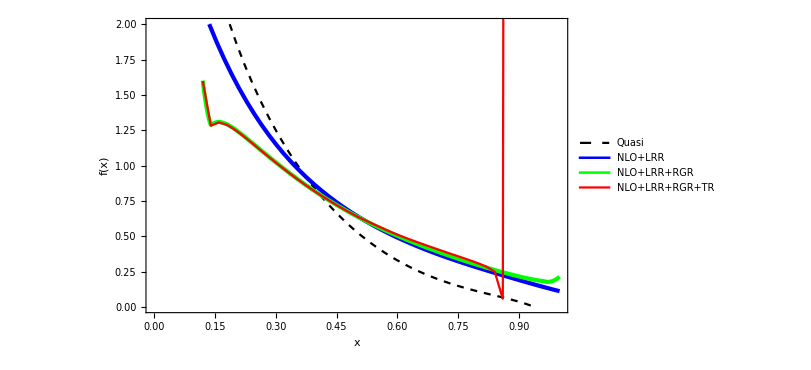

```mathematica
fig=Show[
Plot[qint[x],{x,0,1},PlotStyle->{Black,Dashed},
PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["Quasi",20]},{0.7,0.75}]],

Plot[fVint[x],{x,0.10,1},PlotStyle->{Blue,Thickness[0.005]},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc,20]},{0.7,0.65}]],

Plot[PDFRGRint[x],{x,0.12,1},PlotStyle->{Green,Thickness[0.005]},PlotRange->All,PlotLegends->Placed[{Style[PertAcc<>"+RGR",20]},{0.7,0.55}]],

Plot[PDFRGRTRint[x],{x,0.12,0.88},PlotStyle->Red,PlotRange->All,PlotLegends->Placed[{Style[PertAcc<>"+RGR+TR",20]},{0.7,0.45}]],

PlotRange->{{0,1},{0,2}},
FrameLabel->{Style["x",20],Style["f(x)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]

(*SetDirectory[NotebookDirectory[]];
Export["./pics/MCfull5NLO_add.pdf",fig]*)
```

#### μ_i=2|1-|x_i||P_z r1, μ_h=2|x_i| P_z r2, r1,r2=0.8~1.2

```mathematica
r1ls={1.2,1,0.8};
r2ls={1.2,1,0.8};
xlsf=Join[Table[N[1.0/50 i],{i,6,44}]];
```

```mathematica
(*Resummation and variation of r1 and r2*)
PDFRGRTRls=Table[
PrintTemporary[{r1,r2}];
(*Resummation on the inversed matrix*)
PDFls={};
PDFls2={};
μils=2*(1-xlsf)*Pz*r1;
μhls=2*xlsf*Pz*r2;
Monitor[
For[i=Length[μhls],i≥1,i--,

ChM=MfixGen[μhls[[i]]];
Quiet[If[μhls[[i]]>μils[[i]],
Hm=Hmgen[μhls[[i]]];
Jmμi=Jmgen[μils[[i]]];
Jmμh=Jmgen[μhls[[i]]];
PJm=PJmgen[μhls[[i]],μils[[i]]];
Strnew=(Mcut*PJm).(Mcut*Jmμi).(Mcut*Hm);
Strnew0=(Mcut*Jmμh).(Mcut*Hm);
PDFlist=Transpose[{xlist,(ChM+Strnew-Strnew0).qV}],
PDFlist=Transpose[{xlist,ChM.qV}]
];];

ClearAll[PDFint,PDFintsys,PDFCombine];
PDFint=Interpolation[PDFlist];
PDFintsys[x_]:=(PDFint[x]+PDFint[-x])/2;
If[μhls[[i]]>μils[[i]],
PDFCombine[x_]:=PDFintsys[x],
PDFCombine[x_]:=If[Abs[x]≤ xlsf[[i]]+Δx/4,PDFintsys[x],If[xlsf[[i]]+Δx/4<Abs[x]≤ xlsf[[i]]+(3Δx)/4,((xlsf[[i]]+(3Δx)/4)-Abs[x])/(Δx/2)PDFintsys[x]+(Abs[x]-(xlsf[[i]]+Δx/4))/(Δx/2)PDFls2[[Length[μhls]-i]][x],PDFls2[[Length[μhls]-i]][x]]]
];
(*PDFCombine[x_]:=PDFintsys[x];*)

If[PertAcc=="NLO+LRR",
AppendTo[PDFls,DGLAPNLOx[PDFCombine,μhls[[i]],μ,Mdglapns0,Mdglapns1,xDGLAP]];AppendTo[PDFls2,DGLAPNLOx[PDFCombine,μhls[[i]],μhls[[i-1]],Mdglapns0,Mdglapns1,xDGLAP]];,
Nothing[]
];

],
Row[{ProgressIndicator[i,{1,Length[μhls]}],i}," "]
];
Table[PDFls[[Length[xlsf]-i+1]][xlsf[[i]]],{i,1,Length[xlsf]}]
,{r1,r1ls},{r2,r2ls}]
```

{{{1.42835,1.45814,1.43216,1.3854,1.33111,1.27481,1.21896,1.16456,1.11171,1.06062,1.01204,0.965856,0.921914,0.88009,0.840246,0.802278,0.76605,0.731487,0.698553,0.667183,0.639894,0.612373,0.585683,0.559039,0.534281,0.511097,0.489187,0.467709,0.447102,0.426935,0.406081,0.386327,0.366476,0.34636,0.325434,0.302791,0.275981,0.236641,0.0669241},{1.59893,1.2834,1.30565,1.28852,1.25332,1.20991,1.16312,1.1154,1.06803,1.02165,0.97656,0.932563,0.890131,0.849544,0.810733,0.773636,0.738161,0.704245,0.671819,0.640819,0.611174,0.582791,0.557092,0.531994,0.508135,0.485582,0.464215,0.443528,0.42374,0.404509,0.384739,0.366181,0.347707,0.32921,0.31028,0.290274,0.267619,0.237484,0.146716},{1.29488×10^13,170.089,1.18856,1.18917,1.17437,1.1458,1.10956,1.06945,1.02768,0.985556,0.943825,0.902935,0.863143,0.824586,0.787311,0.751179,0.71634,0.68297,0.651018,0.620417,0.591136,0.563106,0.536269,0.510568,0.485958,0.463536,0.442465,0.422267,0.403011,0.384444,0.365667,0.348041,0.330703,0.313558,0.296345,0.278635,0.259539,0.236661,0.18825}},{{1.42565,1.45583,1.43013,1.3836,1.32948,1.27334,1.21762,1.16333,1.1106,1.05961,1.01114,0.965064,0.921242,0.879557,0.839883,0.802139,0.766234,0.733015,0.702508,0.672966,0.64431,0.616631,0.589739,0.562582,0.537817,0.514675,0.492749,0.471123,0.450117,0.429324,0.407915,0.387346,0.366377,0.344552,0.320577,0.29148,0.244182,-0.235914,72.399},{1.5978,1.2825,1.30487,1.28782,1.25268,1.20933,1.16258,1.1149,1.06756,1.02122,0.976155,0.932184,0.889777,0.849215,0.810431,0.773364,0.737922,0.704047,0.671673,0.640752,0.613294,0.58686,0.561206,0.535444,0.511616,0.489176,0.467881,0.447136,0.427077,0.407361,0.387166,0.368073,0.348874,0.329283,0.308388,0.284344,0.249793,0.0571906,34.2757},{1.29488×10^13,170.087,1.18743,1.1882,1.17348,1.14499,1.1088,1.06874,1.02702,0.984925,0.943223,0.902359,0.862588,0.82405,0.786792,0.750673,0.715847,0.682487,0.650544,0.61995,0.590674,0.562647,0.536067,0.511852,0.488708,0.466726,0.445828,0.425688,0.406318,0.387429,0.368328,0.350438,0.332737,0.315033,0.296755,0.276888,0.251873,0.169001,1.20796}},{{1.42386,1.4543,1.42877,1.38238,1.32838,1.27232,1.21668,1.16247,1.1098,1.05887,1.01046,0.96445,0.920703,0.879115,0.839602,0.805616,0.772408,0.740679,0.710045,0.680281,0.651337,0.623403,0.596239,0.568635,0.543725,0.520311,0.498021,0.475961,0.454214,0.43249,0.410323,0.387795,0.36357,0.335458,0.295217,0.190553,-5.6304,164635.,-1.18068×10^18},{1.59536,1.28055,1.30317,1.28629,1.25129,1.20804,1.16139,1.11378,1.0665,1.02021,0.975197,0.93127,0.888904,0.848381,0.809638,0.772621,0.737286,0.705298,0.67611,0.647748,0.620208,0.593544,0.567613,0.541262,0.51733,0.494712,0.473207,0.452189,0.431679,0.41142,0.39092,0.370647,0.349466,0.326179,0.296116,0.238675,-5.55245,126565.,-7.93841×10^17},{1.29488×10^13,170.087,1.18707,1.18788,1.1732,1.14473,1.10856,1.06852,1.02681,0.984723,0.943031,0.902175,0.862411,0.82388,0.786628,0.750516,0.715697,0.682348,0.650428,0.619941,0.592327,0.566615,0.541685,0.516705,0.493543,0.471516,0.450583,0.430357,0.410828,0.391764,0.372698,0.354285,0.335623,0.316171,0.293559,0.261068,-6.81896,86523.6,-4.48028×10^17}}}

```mathematica
PDFRGRTRintls=Table[Interpolation[Transpose[Re[{xlsf,PDFRGRTRls[[i,j]]}]],InterpolationOrder->1],{i,1,Length[r1ls]},{j,1,Length[r2ls]}];
```

InterpolatingFunction::dmval: Input value {0.100016} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

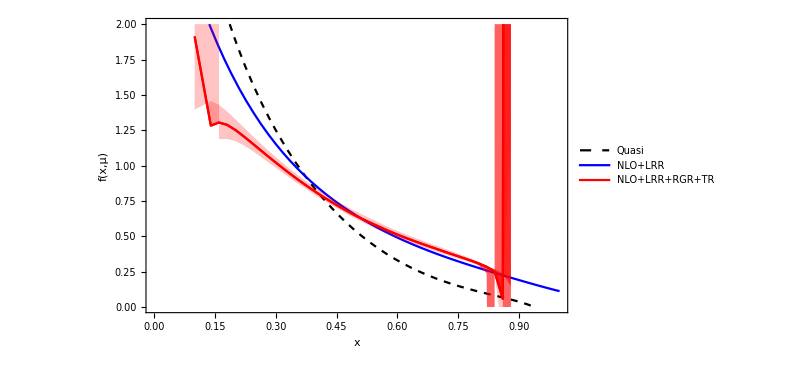

```mathematica
fig=Show[
Plot[qint[x],{x,0,1},PlotStyle->{Black,Dashed},
PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["Quasi",20]},{0.7,0.75}]],

Plot[fVint[x],{x,0.12,1},PlotStyle->Blue,PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc,20]},{0.7,0.65}]],

Plot[{PDFRGRTRintls[[2,2]][x],PDFRGRTRintls[[2,1]][x],PDFRGRTRintls[[2,3]][x]},{x,0.1,0.88},PlotStyle->{Red,Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618^3,Red]}},1->{{3},{Opacity[0.618^3,Red]}}},PlotRange->{{0,1},{0,2}}],

Plot[{PDFRGRTRintls[[2,2]][x],PDFRGRTRintls[[1,2]][x],PDFRGRTRintls[[3,2]][x]},{x,0.1,0.88},PlotStyle->{Red,Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618,Red]}},1->{{3},{Opacity[0.618,Red]}}},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc<>"+RGR+TR",20]},{0.7,0.55}]],

PlotRange->{{0,1},{0,2}},
FrameLabel->{Style["x",20],Style["f(x,μ)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]
```

#### μ_i=2|1-|x_i||P_z, μ_i0=2|x_i|P_z, μ_h=2|x_i| P_z, |1-ξ|<γ, γ=0.3~0.5

```mathematica
γls={0.3,0.4,0.5};
xlsf=Table[N[1.0/50 i],{i,6,44}];
```

```mathematica
(*Resummation and variation of r1 and r2*)
PDFRGRTRls=Table[
PrintTemporary[{γ}];
(*Resummation on the inversed matrix*)
Mcut=Table[If[Abs[1-y/x]<γ,1,0],{y,xlist},{x,xlist}];
PDFls={};
PDFls2={};
μils=2*(1-xlsf)*Pz;
μhls=2*xlsf*Pz;
Monitor[
For[i=Length[μhls],i≥1,i--,

ChM=MfixGen[μhls[[i]]];
Quiet[If[μhls[[i]]>μils[[i]],
Hm=Hmgen[μhls[[i]]];
Jmμi=Jmgen[μils[[i]]];
Jmμh=Jmgen[μhls[[i]]];
PJm=PJmgen[μhls[[i]],μils[[i]]];
Strnew=(Mcut*PJm).(Mcut*Jmμi).(Mcut*Hm);
Strnew0=(Mcut*Jmμh).(Mcut*Hm);
PDFlist=Transpose[{xlist,(ChM+Strnew-Strnew0).qV}],
PDFlist=Transpose[{xlist,ChM.qV}]
];];

PDFint=Interpolation[PDFlist];
PDFintsys[x_]:=(PDFint[x]+PDFint[-x])/2;
If[μhls[[i]]>μils[[i]],
PDFCombine[x_]:=PDFintsys[x],
PDFCombine[x_]:=If[Abs[x]≤ xlsf[[i]]+Δx/4,PDFintsys[x],If[xlsf[[i]]+Δx/4<Abs[x]≤ xlsf[[i]]+(3Δx)/4,((xlsf[[i]]+(3Δx)/4)-Abs[x])/(Δx/2)PDFintsys[x]+(Abs[x]-(xlsf[[i]]+Δx/4))/(Δx/2)PDFls2[[Length[μhls]-i]][x],PDFls2[[Length[μhls]-i]][x]]]
];
(*PDFCombine[x_]:=PDFintsys[x];*)

If[PertAcc=="NLO+LRR",
AppendTo[PDFls,DGLAPNLOx[PDFCombine,μhls[[i]],μ,Mdglapns0,Mdglapns1,xDGLAP]];AppendTo[PDFls2,DGLAPNLOx[PDFCombine,μhls[[i]],μhls[[i-1]],Mdglapns0,Mdglapns1,xDGLAP]];,
Nothing[]
];

],
Row[{ProgressIndicator[i,{1,Length[μhls]}],i}," "]
];
Table[PDFls[[Length[xlsf]-i+1]][xlsf[[i]]],{i,1,Length[xlsf]}]
,{γ,γls}]
```

{{1.59784,1.28253,1.3049,1.28784,1.25271,1.20935,1.16261,1.11492,1.06758,1.02124,0.976175,0.932204,0.889797,0.849234,0.81045,0.773383,0.737941,0.704065,0.671691,0.640768,0.613979,0.588006,0.562827,0.538108,0.514137,0.49086,0.468175,0.446261,0.425367,0.405348,0.386866,0.369364,0.352085,0.334724,0.315587,0.29282,0.258849,0.112508,-50.8007},{1.5978,1.2825,1.30487,1.28782,1.25268,1.20933,1.16258,1.1149,1.06756,1.02122,0.976155,0.932184,0.889777,0.849215,0.810431,0.773364,0.737922,0.704047,0.671673,0.640752,0.613294,0.58686,0.561206,0.535444,0.511616,0.489176,0.467881,0.447136,0.427077,0.407361,0.387166,0.368073,0.348874,0.329283,0.308388,0.284344,0.249793,0.0571906,34.2757},{1.59778,1.28249,1.30485,1.28781,1.25267,1.20932,1.16258,1.1149,1.06756,1.02121,0.97615,0.93218,0.889774,0.849212,0.810428,0.773361,0.73792,0.704045,0.671672,0.64075,0.612994,0.586712,0.560776,0.53656,0.513214,0.48964,0.467786,0.446509,0.424898,0.404607,0.384739,0.364798,0.345749,0.326777,0.307841,0.288108,0.266223,0.173229,374.355}}

```mathematica
PDFRGRTRintls2=Table[Interpolation[Transpose[Re[{xlsf,PDFRGRTRls[[i]]}]],InterpolationOrder->1],{i,1,Length[γls]}];
```

InterpolatingFunction::dmval: Input value {0.100016} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

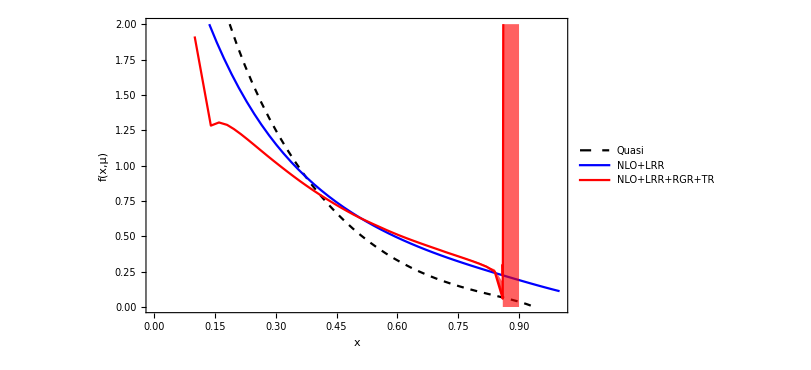

```mathematica
fig=Show[
Plot[qint[x],{x,0,1},PlotStyle->{Black,Dashed},
PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["Quasi",20]},{0.7,0.75}]],

Plot[fVint[x],{x,0.10,1},PlotStyle->Blue,PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc,20]},{0.7,0.65}]],

Plot[{PDFRGRTRintls2[[2]][x],PDFRGRTRintls2[[1]][x],PDFRGRTRintls2[[3]][x]},{x,0.1,0.9},PlotStyle->{Red,Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618,Red]}},1->{{3},{Opacity[0.618,Red]}}},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc<>"+RGR+TR",20]},{0.7,0.55}]],

PlotRange->{{0,1},{0,2}},
FrameLabel->{Style["x",20],Style["f(x,μ)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]
```

## NNLO with renormalon

### Lattice Data Pion Valence Quasi - PDF, Pz=1.9 GeV, zs=0.12fm, λ_L=25

```mathematica
(*
The data is generated by BNL/ANL Collaborations, Gao:2021dbh
Renormalized based on the RGR+LRR method, Zhang:2023bxs
*)
```

```mathematica
Pz=1.94;(*GeV*)
zs=0.12/GeVfm;(*GeV^-1*)
```

```mathematica
qls={{-2.,0.004644373353200662},{-1.99,0.004120247847633056},{-1.98,0.003622067087287381},{-1.97,0.0031552223149979},{-1.96,0.002726220362994065},{-1.95,0.002332121946113358},{-1.94,0.0019748105696102128},{-1.93,0.0016617946317518128},{-1.92,0.0013896498468505209},{-1.91,0.001157969030572405},{-1.9,0.0009740062784405524},{-1.89,0.0008343069837817357},{-1.88,0.0007354910726053484},{-1.87,0.0006844474334537591},{-1.86,0.0006775322836966953},{-1.85,0.0007093746490651379},{-1.84,0.0007848304657079239},{-1.83,0.0009010306765860066},{-1.82,0.0010500511427830594},{-1.81,0.0012347748938322317},{-1.8,0.0014529691648524812},{-1.79,0.001695074247695391},{-1.78,0.0019608772861017146},{-1.77,0.0022493261730182164},{-1.76,0.002548904375507088},{-1.75,0.0028570969569776993},{-1.74,0.0031734135755238676},{-1.73,0.003485305751241066},{-1.72,0.003787860492555417},{-1.71,0.004080714570753909},{-1.7,0.0043513415591125565},{-1.69,0.00459209780747},{-1.68,0.004802930805205951},{-1.67,0.004971973589585376},{-1.66,0.0050893807375176625},{-1.65,0.0051544301651739125},{-1.64,0.0051572528883037675},{-1.63,0.0050857962876900975},{-1.62,0.004939638608088999},{-1.61,0.0047103710762440385},{-1.6,0.004384588087735983},{-1.59,0.003961638559377615},{-1.58,0.0034355478567254134},{-1.57,0.0027923727101677306},{-1.56,0.0020307899346212865},{-1.55,0.001147653353127118},{-1.54,0.0001293662115165748},{-1.53,-0.0010262053436745217},{-1.52,-0.002319241626571331},{-1.51,-0.003762070898562308},{-1.5,-0.00535767461611031},{-1.49,-0.007103322325419803},{-1.48,-0.009009173627881811},{-1.47,-0.011078971693766839},{-1.46,-0.013307310981559016},{-1.45,-0.01570136328212513},{-1.44,-0.0182654114646309},{-1.43,-0.020991762810628253},{-1.42,-0.02388391683318669},{-1.41,-0.026946333224345465},{-1.4,-0.030169528227263636},{-1.39,-0.03355282186583401},{-1.38,-0.03710035027897443},{-1.37,-0.04081071753848808},{-1.36,-0.04465944879214011},{-1.35,-0.04865963860632827},{-1.34,-0.052799840226409746},{-1.33,-0.05707031143306075},{-1.32,-0.061472539521033896},{-1.31,-0.06599476622458914},{-1.3,-0.07062273776425468},{-1.29,-0.07535273029596794},{-1.28,-0.08017913633450793},{-1.27,-0.08507972027317055},{-1.26,-0.09004977201197047},{-1.25,-0.09507580386853634},{-1.24,-0.10013643453606268},{-1.23,-0.1052217762493435},{-1.22,-0.11031842068337755},{-1.21,-0.11539884898458205},{-1.2,-0.12044650543362649},{-1.19,-0.12544472751274555},{-1.18,-0.1303598348657722},{-1.17,-0.1351735733812622},{-1.16,-0.13984482290530456},{-1.15,-0.14433717761958592},{-1.14,-0.14860599638320865},{-1.13,-0.15260865725942266},{-1.12,-0.15627783779791632},{-1.11,-0.15953306926178973},{-1.1,-0.16228714588271892},{-1.09,-0.16441456147949368},{-1.08,-0.16574791938649297},{-1.07,-0.16608017752841578},{-1.06,-0.16512238403855972},{-1.05,-0.16247228616306125},{-1.04,-0.1576079570670807},{-1.03,-0.1498745549865596},{-1.02,-0.13856750481624514},{-1.01,-0.12329118093713683},{-1.,-0.10452791672037298},{-0.99,-0.08386577478628733},{-0.98,-0.06335779275286002},{-0.97,-0.044487529193872555},{-0.96,-0.027791608369410428},{-0.95,-0.013222288017471662},{-0.94,-0.0005060197676422379},{-0.93,0.010712926418813828},{-0.92,0.020747082549468394},{-0.91,0.029838009883754957},{-0.9,0.03821136232499601},{-0.89,0.0460465568700808},{-0.88,0.05346537832030689},{-0.87,0.06059246869266078},{-0.86,0.06753496522164032},{-0.85,0.0743557313427976},{-0.84,0.08112836368178805},{-0.83,0.0879271737670217},{-0.82,0.09478793608711844},{-0.81,0.10175642926745493},{-0.8,0.10889143693088607},{-0.79,0.11621674758268581},{-0.78,0.1237610583222274},{-0.77,0.13157504382591872},{-0.76,0.1396783280519504},{-0.75,0.14808810060910665},{-0.74,0.1568499582295041},{-0.73,0.16598381259698758},{-0.72,0.17549878312097195},{-0.71,0.18543635329779484},{-0.7,0.19581939592572234},{-0.69,0.20665153845175915},{-0.68,0.2179701214189261},{-0.67,0.22980255026321988},{-0.66,0.24214923764638413},{-0.65,0.25504292135001416},{-0.64,0.2685163194493533},{-0.63,0.28256884463310383},{-0.62,0.2972271045353138},{-0.61,0.3125311593245419},{-0.6,0.32848076047689745},{-0.59,0.34509795809233895},{-0.58,0.3624260434801411},{-0.57,0.38046917194148},{-0.56,0.3992438019869307},{-0.55,0.4187982160626459},{-0.54,0.43914024161844556},{-0.53,0.46028312747525324},{-0.52,0.4822784905078693},{-0.51,0.5051420233327284},{-0.5,0.5288815511766826},{-0.49,0.5535517147724702},{-0.48,0.5791791881504709},{-0.47,0.6057682632765653},{-0.46,0.6333745418103949},{-0.45,0.6620379331888059},{-0.44,0.6917625152625423},{-0.43,0.7226035104236992},{-0.42,0.7546157172441825},{-0.41,0.78780717183097},{-0.4,0.8222324759737083},{-0.39,0.8579628404685727},{-0.38,0.8950151875900143},{-0.37,0.9334445457962022},{-0.36,0.9733404584277825},{-0.35,1.0147346620849456},{-0.34,1.05768518912032},{-0.33,1.1023027626430033},{-0.32,1.1486414268852312},{-0.31,1.1967701625144844},{-0.3,1.246818645446664},{-0.29,1.2988768175409042},{-0.28,1.3530252429364402},{-0.27,1.409432971004116},{-0.26,1.4682327591165751},{-0.25,1.5295336404418816},{-0.24,1.5935488304240892},{-0.23,1.6604769430098891},{-0.22,1.7304757454739113},{-0.21,1.8038230429831537},{-0.2,1.8808140737409953},{-0.19,1.961688885024415},{-0.18,2.046824052821365},{-0.17,2.1366600426183044},{-0.16,2.231574775658292},{-0.15,2.3320820112281115},{-0.14,2.439006731842744},{-0.13,2.552529992013758},{-0.12,2.673751967916616},{-0.11,2.8037487067637175},{-0.1,2.9433866951050964},{-0.09,3.0936367993617053},{-0.08,3.2556429738423134},{-0.07,3.4302252428984916},{-0.06,3.617879799994142},{-0.05,3.8181709368900414},{-0.04,4.027353378189677},{-0.03,4.235688352317414},{-0.02,4.423972412482997},{-0.01,4.56087468343495},{0,4.612277188558619},{0.01,4.56087468343495},{0.02,4.423972412482997},{0.03,4.235688352317414},{0.04,4.027353378189677},{0.05,3.8181709368900414},{0.06,3.617879799994142},{0.07,3.4302252428984916},{0.08,3.2556429738423134},{0.09,3.0936367993617053},{0.1,2.9433866951050964},{0.11,2.8037487067637175},{0.12,2.673751967916616},{0.13,2.552529992013758},{0.14,2.439006731842744},{0.15,2.3320820112281115},{0.16,2.231574775658292},{0.17,2.1366600426183044},{0.18,2.046824052821365},{0.19,1.961688885024415},{0.2,1.8808140737409953},{0.21,1.8038230429831537},{0.22,1.7304757454739113},{0.23,1.6604769430098891},{0.24,1.5935488304240892},{0.25,1.5295336404418816},{0.26,1.4682327591165751},{0.27,1.409432971004116},{0.28,1.3530252429364402},{0.29,1.2988768175409042},{0.3,1.246818645446664},{0.31,1.1967701625144844},{0.32,1.1486414268852312},{0.33,1.1023027626430033},{0.34,1.05768518912032},{0.35,1.0147346620849456},{0.36,0.9733404584277825},{0.37,0.9334445457962022},{0.38,0.8950151875900143},{0.39,0.8579628404685727},{0.4,0.8222324759737083},{0.41,0.78780717183097},{0.42,0.7546157172441825},{0.43,0.7226035104236992},{0.44,0.6917625152625423},{0.45,0.6620379331888059},{0.46,0.6333745418103949},{0.47,0.6057682632765653},{0.48,0.5791791881504709},{0.49,0.5535517147724702},{0.5,0.5288815511766826},{0.51,0.5051420233327284},{0.52,0.4822784905078693},{0.53,0.46028312747525324},{0.54,0.43914024161844556},{0.55,0.4187982160626459},{0.56,0.3992438019869307},{0.57,0.38046917194148},{0.58,0.3624260434801411},{0.59,0.34509795809233895},{0.6,0.32848076047689745},{0.61,0.3125311593245419},{0.62,0.2972271045353138},{0.63,0.28256884463310383},{0.64,0.2685163194493533},{0.65,0.25504292135001416},{0.66,0.24214923764638413},{0.67,0.22980255026321988},{0.68,0.2179701214189261},{0.69,0.20665153845175915},{0.7,0.19581939592572234},{0.71,0.18543635329779484},{0.72,0.17549878312097195},{0.73,0.16598381259698758},{0.74,0.1568499582295041},{0.75,0.14808810060910665},{0.76,0.1396783280519504},{0.77,0.13157504382591872},{0.78,0.1237610583222274},{0.79,0.11621674758268581},{0.8,0.10889143693088607},{0.81,0.10175642926745493},{0.82,0.09478793608711844},{0.83,0.0879271737670217},{0.84,0.08112836368178805},{0.85,0.0743557313427976},{0.86,0.06753496522164032},{0.87,0.06059246869266078},{0.88,0.05346537832030689},{0.89,0.0460465568700808},{0.9,0.03821136232499601},{0.91,0.029838009883754957},{0.92,0.020747082549468394},{0.93,0.010712926418813828},{0.94,-0.0005060197676422379},{0.95,-0.013222288017471662},{0.96,-0.027791608369410428},{0.97,-0.044487529193872555},{0.98,-0.06335779275286002},{0.99,-0.08386577478628733},{1.,-0.10452791672037298},{1.01,-0.12329118093713683},{1.02,-0.13856750481624514},{1.03,-0.1498745549865596},{1.04,-0.1576079570670807},{1.05,-0.16247228616306125},{1.06,-0.16512238403855972},{1.07,-0.16608017752841578},{1.08,-0.16574791938649297},{1.09,-0.16441456147949368},{1.1,-0.16228714588271892},{1.11,-0.15953306926178973},{1.12,-0.15627783779791632},{1.13,-0.15260865725942266},{1.14,-0.14860599638320865},{1.15,-0.14433717761958592},{1.16,-0.13984482290530456},{1.17,-0.1351735733812622},{1.18,-0.1303598348657722},{1.19,-0.12544472751274555},{1.2,-0.12044650543362649},{1.21,-0.11539884898458205},{1.22,-0.11031842068337755},{1.23,-0.1052217762493435},{1.24,-0.10013643453606268},{1.25,-0.09507580386853634},{1.26,-0.09004977201197047},{1.27,-0.08507972027317055},{1.28,-0.08017913633450793},{1.29,-0.07535273029596794},{1.3,-0.07062273776425468},{1.31,-0.06599476622458914},{1.32,-0.061472539521033896},{1.33,-0.05707031143306075},{1.34,-0.052799840226409746},{1.35,-0.04865963860632827},{1.36,-0.04465944879214011},{1.37,-0.04081071753848808},{1.38,-0.03710035027897443},{1.39,-0.03355282186583401},{1.4,-0.030169528227263636},{1.41,-0.026946333224345465},{1.42,-0.02388391683318669},{1.43,-0.020991762810628253},{1.44,-0.0182654114646309},{1.45,-0.01570136328212513},{1.46,-0.013307310981559016},{1.47,-0.011078971693766839},{1.48,-0.009009173627881811},{1.49,-0.007103322325419803},{1.5,-0.00535767461611031},{1.51,-0.003762070898562308},{1.52,-0.002319241626571331},{1.53,-0.0010262053436745217},{1.54,0.0001293662115165748},{1.55,0.001147653353127118},{1.56,0.0020307899346212865},{1.57,0.0027923727101677306},{1.58,0.0034355478567254134},{1.59,0.003961638559377615},{1.6,0.004384588087735983},{1.61,0.0047103710762440385},{1.62,0.004939638608088999},{1.63,0.0050857962876900975},{1.64,0.0051572528883037675},{1.65,0.0051544301651739125},{1.66,0.0050893807375176625},{1.67,0.004971973589585376},{1.68,0.004802930805205951},{1.69,0.00459209780747},{1.7,0.0043513415591125565},{1.71,0.004080714570753909},{1.72,0.003787860492555417},{1.73,0.003485305751241066},{1.74,0.0031734135755238676},{1.75,0.0028570969569776993},{1.76,0.002548904375507088},{1.77,0.0022493261730182164},{1.78,0.0019608772861017146},{1.79,0.001695074247695391},{1.8,0.0014529691648524812},{1.81,0.0012347748938322317},{1.82,0.0010500511427830594},{1.83,0.0009010306765860066},{1.84,0.0007848304657079239},{1.85,0.0007093746490651379},{1.86,0.0006775322836966953},{1.87,0.0006844474334537591},{1.88,0.0007354910726053484},{1.89,0.0008343069837817357},{1.9,0.0009740062784405524},{1.91,0.001157969030572405},{1.92,0.0013896498468505209},{1.93,0.0016617946317518128},{1.94,0.0019748105696102128},{1.95,0.002332121946113358},{1.96,0.002726220362994065},{1.97,0.0031552223149979},{1.98,0.003622067087287381},{1.99,0.004120247847633056},{2.,0.004644373353200662}};
```

### Δx=0.005, L=4, γ=0.4

```mathematica
μ=2;(*GeV*)(*Factorization Scale*)
PertAcc="NNLO+LRR";
```

#### Discretization

```mathematica
qlsgf=GaussianFilter[qls,{{4,0}}];
qinttest=Interpolation[qlsgf];
ClearAll[qint];
qint[x_]:=If[Abs[x]<2,qinttest[x],qinttest[2]Exp[-(Abs[x]-2)]];
Plot[qint[x],{x,-4,4},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
L=4;
Δx=0.005;(*Discretization*)
xlist=Join[Table[x,{x,-L,-Δx,Δx}],Table[x,{x,Δx,L,Δx}]];
qV=Table[qint[x],{x,xlist}];
```

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

#### Fixed order results

```mathematica
(*Matrix Elements generation*)
```

```mathematica
If[PertAcc=="NNLO+LRR",
MCratio1pluswμ=SubMGen[Cratio1pluswμ,xlist,Pz,zs];
MCratio1pluswoμ=SubMGen[Cratio1pluswoμ,xlist,Pz,zs];
MChybrid1plus=SubMGen[Chybrid1plus,xlist,Pz,zs];

MCMS2wLL=SubMGen[CMS2wLL,xlist,Pz,zs];
MCMS2wNLL=SubMGen[CMS2wNLL,xlist,Pz,zs];
MCMS2woL=SubMGen[CMS2woL,xlist,Pz,zs];
MChybrid2pluswLL=SubMGen[Chybrid2pluswLL,xlist,Pz,zs];
MChybrid2pluswNLLPz=SubMGen[Chybrid2pluswNLLPz,xlist,Pz,zs];
MChybrid2pluswNLLzs=SubMGen[Chybrid2pluswNLLzs,xlist,Pz,zs];
MChybrid2pluswoL=SubMGen[Chybrid2pluswoL,xlist,Pz,zs];

MCz=SubMGen[Cz,xlist,Pz,zs];

MfixGen[μ_]:=Module[{nf,C1,C2,C1i,C2i,rsumPV,r0,r1},
nf=3;
C1=(αsNNLO[[1]][μ]*CF)/(2Pi)((-Log[(μ/Pz)^2])MCratio1pluswμ+MCratio1pluswoμ+MChybrid1plus);
C2=Re[((αsNNLO[[1]][μ])/(2Pi))^2(MCMS2wLL*Log[μ^2/Pz^2]^2+MCMS2wNLL*Log[μ^2/Pz^2]+MCMS2woL+MChybrid2pluswLL*Log[μ^2/Pz^2]Log[(zs^2 μ^2 Exp[2EulerGamma])/4]+MChybrid2pluswNLLPz*Log[μ^2/Pz^2]+MChybrid2pluswNLLzs*Log[(zs^2 μ^2 Exp[2EulerGamma])/4]+MChybrid2pluswoL)];
C1i=-C1;
C2i=-C2+C1.C1;

rsumPV=dPVasym[1,μ,nf,αsNNLO[[1]][μ]];
r0=rnasym[0,1,μ,nf]*αsNNLO[[1]][μ];
r1=rnasym[1,1,μ,nf]*(αsNNLO[[1]][μ])^2;

(IdentityMatrix[Length[xlist]]+C1i+C2i+r0*MCz+r1*MCz+C1i.MCz*r0+1/2 MCz.MCz*r0^2).MatrixExp[-MCz*rsumPV]
],
Nothing[];
]
```

```mathematica
(*Calculation*)
```

```mathematica
ChM=MfixGen[μ];
fVfixed=ChM.qV;
(fVfixed+Reverse[fVfixed])/2
fVint=Interpolation[Transpose[{xlist,(fVfixed+Reverse[fVfixed])/2}]];
```

{-0.0197609,-0.0168412,-0.0155898,-0.0148465,-0.0143413,-0.0139713,-0.0136872,-0.0134619,-0.0132789,-0.0131276,-0.0130008,-0.0128934,-0.0128017,-0.0127228,-0.0126545,-0.0125953,-0.0125437,-0.0124987,-0.0124593,-0.012425,-0.0123949,-0.0123688,-0.012346,-0.0123263,-0.0123093,-0.0122947,-0.0122824,-0.0122721,-0.0122636,-0.0122568,-0.0122515,-0.0122476,-0.012245,-0.0122435,-0.0122431,-0.0122438,-0.0122453,-0.0122478,-0.012251,-0.012255,-0.0122596,-0.0122649,-0.0122708,-0.0122773,-0.0122842,-0.0122917,-0.0122996,-0.012308,-0.0123167,-0.0123259,-0.0123353,-0.0123451,-0.0123552,-0.0123656,-0.0123762,-0.0123871,-0.0123983,-0.0124096,-0.0124211,-0.0124329,-0.0124448,-0.0124568,-0.012469,-0.0124814,-0.0124939,-0.0125065,-0.0125192,-0.0125319,-0.0125448,-0.0125578,-0.0125708,-0.0125839,-0.012597,-0.0126102,-0.0126234,-0.0126366,-0.0126499,-0.0126632,-0.0126765,-0.0126898,-0.0127031,-0.0127164,-0.0127297,-0.0127429,-0.0127561,-0.0127694,-0.0127825,-0.0127956,-0.0128087,-0.0128218,-0.0128347,-0.0128477,-0.0128605,-0.0128733,-0.012886,-0.0128987,-0.0129112,-0.0129237,-0.0129361,-0.0129484,-0.0129606,-0.0129727,-0.0129847,-0.0129966,-0.0130083,-0.01302,-0.0130315,-0.013043,-0.0130543,-0.0130654,-0.0130764,-0.0130873,-0.0130981,-0.0131087,-0.0131192,-0.0131295,-0.0131397,-0.0131497,-0.0131595,-0.0131692,-0.0131787,-0.0131881,-0.0131973,-0.0132063,-0.0132151,-0.0132238,-0.0132322,-0.0132405,-0.0132486,-0.0132565,-0.0132642,-0.0132717,-0.013279,-0.0132861,-0.013293,-0.0132997,-0.0133061,-0.0133124,-0.0133184,-0.0133242,-0.0133298,-0.0133351,-0.0133403,-0.0133451,-0.0133498,-0.0133542,-0.0133584,-0.0133623,-0.013366,-0.0133694,-0.0133726,-0.0133755,-0.0133781,-0.0133805,-0.0133826,-0.0133845,-0.0133861,-0.0133874,-0.0133884,-0.0133892,-0.0133896,-0.0133898,-0.0133897,-0.0133893,-0.0133886,-0.0133877,-0.0133864,-0.0133848,-0.0133829,-0.0133807,-0.0133781,-0.0133753,-0.0133722,-0.0133687,-0.0133649,-0.0133608,-0.0133563,-0.0133515,-0.0133464,-0.0133409,-0.0133351,-0.013329,-0.0133225,-0.0133156,-0.0133084,-0.0133009,-0.013293,-0.0132847,-0.0132761,-0.013267,-0.0132577,-0.0132479,-0.0132378,-0.0132273,-0.0132164,-0.0132051,-0.0131934,-0.0131813,-0.0131689,-0.013156,-0.0131427,-0.0131291,-0.013115,-0.0131005,-0.0130856,-0.0130703,-0.0130545,-0.0130383,-0.0130217,-0.0130047,-0.0129873,-0.0129694,-0.012951,-0.0129322,-0.012913,-0.0128933,-0.0128732,-0.0128526,-0.0128316,-0.0128101,-0.0127881,-0.0127657,-0.0127428,-0.0127194,-0.0126955,-0.0126712,-0.0126463,-0.012621,-0.0125952,-0.0125689,-0.0125421,-0.0125148,-0.012487,-0.0124586,-0.0124298,-0.0124005,-0.0123706,-0.0123402,-0.0123093,-0.0122779,-0.0122459,-0.0122134,-0.0121803,-0.0121468,-0.0121126,-0.012078,-0.0120427,-0.0120069,-0.0119706,-0.0119337,-0.0118962,-0.0118582,-0.0118196,-0.0117804,-0.0117406,-0.0117003,-0.0116594,-0.0116178,-0.0115757,-0.011533,-0.0114897,-0.0114458,-0.0114013,-0.0113562,-0.0113104,-0.0112641,-0.0112171,-0.0111695,-0.0111213,-0.0110724,-0.0110229,-0.0109728,-0.0109221,-0.0108707,-0.0108186,-0.0107659,-0.0107125,-0.0106585,-0.0106039,-0.0105485,-0.0104925,-0.0104358,-0.0103785,-0.0103205,-0.0102618,-0.0102024,-0.0101423,-0.0100816,-0.0100201,-0.00995795,-0.00989509,-0.00983154,-0.00976728,-0.00970231,-0.00963663,-0.00957023,-0.00950311,-0.00943528,-0.00936671,-0.00929742,-0.0092274,-0.00915665,-0.00908516,-0.00901293,-0.00893995,-0.00886624,-0.00879177,-0.00871655,-0.00864058,-0.00856386,-0.00848637,-0.00840812,-0.00832911,-0.00824934,-0.00816879,-0.00808747,-0.00800538,-0.00792252,-0.00783887,-0.00775445,-0.00766924,-0.00758325,-0.00749647,-0.00740891,-0.00732056,-0.00723141,-0.00714148,-0.00705075,-0.00695922,-0.0068669,-0.00677379,-0.00667987,-0.00658516,-0.00648965,-0.00639334,-0.00629624,-0.00619833,-0.00609962,-0.00600012,-0.00589982,-0.00579873,-0.00569684,-0.00559415,-0.00549068,-0.00538641,-0.00528136,-0.00517553,-0.00506891,-0.00496152,-0.00485336,-0.00474443,-0.00463473,-0.00452428,-0.00441308,-0.00430114,-0.00418846,-0.00407505,-0.00396092,-0.00384609,-0.00373055,-0.00361433,-0.00349743,-0.00337987,-0.00326166,-0.00314281,-0.00302335,-0.00290328,-0.00278264,-0.00266143,-0.00253967,-0.00241739,-0.00229461,-0.00217135,-0.00204763,-0.00192349,-0.00179894,-0.00167402,-0.00154874,-0.00142314,-0.00129724,-0.00117106,-0.00104465,-0.000918008,-0.000791172,-0.000664161,-0.000536994,-0.000409688,-0.000282255,-0.000154706,-0.0000270433,0.000100733,0.00022863,0.000356662,0.000484849,0.00061322,0.000741812,0.000870672,0.000999853,0.00112942,0.00125945,0.00139001,0.00152121,0.00165313,0.00178589,0.0019196,0.00205437,0.00219032,0.0023276,0.00246631,0.00260659,0.00274857,0.00289238,0.00303814,0.00318596,0.00333596,0.00348824,0.00364292,0.00380007,0.00395978,0.00412211,0.00428714,0.0044549,0.00462545,0.00479879,0.00497496,0.00515394,0.00533574,0.00552033,0.00570767,0.00589771,0.00609041,0.00628569,0.00648348,0.00668367,0.00688617,0.00709086,0.00729762,0.00750632,0.00771682,0.00792895,0.00814258,0.00835751,0.00857359,0.00879062,0.00900842,0.00922678,0.00944551,0.0096644,0.00988322,0.0101018,0.0103198,0.0105371,0.0107535,0.0109686,0.0111823,0.0113944,0.0116045,0.0118125,0.0120181,0.012221,0.012421,0.012618,0.0128115,0.0130014,0.0131875,0.0133695,0.0135471,0.0137202,0.0138886,0.0140519,0.01421,0.0143627,0.0145097,0.0146509,0.0147861,0.0149151,0.0150376,0.0151536,0.0152629,0.0153653,0.0154606,0.0155488,0.0156297,0.0157032,0.0157691,0.0158275,0.0158782,0.0159212,0.0159563,0.0159837,0.0160031,0.0160147,0.0160184,0.0160142,0.0160021,0.0159823,0.0159548,0.0159195,0.0158768,0.0158265,0.015769,0.0157042,0.0156325,0.0155539,0.0154687,0.015377,0.0152792,0.0151754,0.015066,0.0149512,0.0148314,0.0147068,0.0145779,0.0144451,0.0143087,0.0141691,0.0140268,0.0138823,0.013736,0.0135885,0.0134403,0.013292,0.0131441,0.0129972,0.012852,0.0127091,0.0125693,0.0124332,0.0123015,0.0121751,0.0120547,0.0119412,0.0118353,0.011738,0.0116501,0.0115727,0.0115066,0.0114529,0.0114127,0.0113869,0.0113767,0.0113832,0.0114077,0.0114512,0.0115152,0.0116007,0.0117093,0.0118422,0.012001,0.0121869,0.0124016,0.0126466,0.0129234,0.0132338,0.0135794,0.0139618,0.0143831,0.0148448,0.015349,0.0158974,0.0164922,0.0171353,0.0178287,0.0185745,0.0193749,0.0202319,0.0211478,0.0221248,0.023165,0.0242707,0.0254441,0.0266874,0.0280027,0.0293922,0.030858,0.0324021,0.0340265,0.035733,0.0375233,0.0393991,0.0413619,0.0434128,0.0455531,0.0477837,0.0501051,0.0525179,0.0550222,0.0576178,0.0603045,0.0630815,0.0659479,0.0689022,0.071943,0.0750682,0.0782756,0.0815628,0.0849269,0.0883649,0.0918736,0.0954494,0.0990887,0.102788,0.106543,0.110349,0.114204,0.118102,0.122041,0.126015,0.130022,0.134057,0.138118,0.142201,0.146302,0.15042,0.154551,0.158694,0.162846,0.167005,0.17117,0.17534,0.179513,0.183689,0.187868,0.192048,0.196231,0.200416,0.204603,0.208793,0.212987,0.217185,0.221388,0.225598,0.229815,0.234041,0.238277,0.242524,0.246784,0.251058,0.255348,0.259655,0.26398,0.268326,0.272694,0.277085,0.281502,0.285944,0.290415,0.294916,0.299448,0.304013,0.308611,0.313246,0.317918,0.322628,0.327379,0.332171,0.337005,0.341884,0.346809,0.35178,0.3568,0.361869,0.366989,0.372162,0.377387,0.382667,0.388003,0.393396,0.398847,0.404358,0.409929,0.415563,0.421259,0.42702,0.432846,0.438739,0.444699,0.450729,0.456829,0.463,0.469245,0.475563,0.481956,0.488426,0.494974,0.501601,0.508308,0.515098,0.52197,0.528927,0.535971,0.543102,0.550322,0.557633,0.565036,0.572533,0.580126,0.587817,0.595607,0.603498,0.611493,0.619593,0.627801,0.636119,0.644549,0.653093,0.661755,0.670536,0.67944,0.688469,0.697627,0.706916,0.71634,0.725903,0.735607,0.745458,0.755458,0.765613,0.775926,0.786403,0.797047,0.807865,0.818862,0.830043,0.841415,0.852983,0.864756,0.876738,0.888939,0.901365,0.914025,0.926928,0.940082,0.953498,0.967185,0.981154,0.995416,1.00998,1.02487,1.04008,1.05564,1.07156,1.08785,1.10453,1.12162,1.13913,1.15709,1.17551,1.19441,1.21381,1.23374,1.25422,1.27528,1.29694,1.31923,1.34217,1.36581,1.39016,1.41527,1.44117,1.46789,1.49548,1.52398,1.55342,1.58387,1.61536,1.64796,1.68171,1.71668,1.75294,1.79056,1.82963,1.87022,1.91244,1.95641,2.00223,2.05007,2.10008,2.15246,2.20742,2.26524,2.32622,2.39076,2.45929,2.5324,2.61079,2.69534,2.78718,2.88778,2.99906,3.12364,3.26512,3.42863,3.6218,3.8565,4.15248,4.54568,5.11123,6.04792,8.26988,8.26988,6.04792,5.11123,4.54568,4.15248,3.8565,3.6218,3.42863,3.26512,3.12364,2.99906,2.88778,2.78718,2.69534,2.61079,2.5324,2.45929,2.39076,2.32622,2.26524,2.20742,2.15246,2.10008,2.05007,2.00223,1.95641,1.91244,1.87022,1.82963,1.79056,1.75294,1.71668,1.68171,1.64796,1.61536,1.58387,1.55342,1.52398,1.49548,1.46789,1.44117,1.41527,1.39016,1.36581,1.34217,1.31923,1.29694,1.27528,1.25422,1.23374,1.21381,1.19441,1.17551,1.15709,1.13913,1.12162,1.10453,1.08785,1.07156,1.05564,1.04008,1.02487,1.00998,0.995416,0.981154,0.967185,0.953498,0.940082,0.926928,0.914025,0.901365,0.888939,0.876738,0.864756,0.852983,0.841415,0.830043,0.818862,0.807865,0.797047,0.786403,0.775926,0.765613,0.755458,0.745458,0.735607,0.725903,0.71634,0.706916,0.697627,0.688469,0.67944,0.670536,0.661755,0.653093,0.644549,0.636119,0.627801,0.619593,0.611493,0.603498,0.595607,0.587817,0.580126,0.572533,0.565036,0.557633,0.550322,0.543102,0.535971,0.528927,0.52197,0.515098,0.508308,0.501601,0.494974,0.488426,0.481956,0.475563,0.469245,0.463,0.456829,0.450729,0.444699,0.438739,0.432846,0.42702,0.421259,0.415563,0.409929,0.404358,0.398847,0.393396,0.388003,0.382667,0.377387,0.372162,0.366989,0.361869,0.3568,0.35178,0.346809,0.341884,0.337005,0.332171,0.327379,0.322628,0.317918,0.313246,0.308611,0.304013,0.299448,0.294916,0.290415,0.285944,0.281502,0.277085,0.272694,0.268326,0.26398,0.259655,0.255348,0.251058,0.246784,0.242524,0.238277,0.234041,0.229815,0.225598,0.221388,0.217185,0.212987,0.208793,0.204603,0.200416,0.196231,0.192048,0.187868,0.183689,0.179513,0.17534,0.17117,0.167005,0.162846,0.158694,0.154551,0.15042,0.146302,0.142201,0.138118,0.134057,0.130022,0.126015,0.122041,0.118102,0.114204,0.110349,0.106543,0.102788,0.0990887,0.0954494,0.0918736,0.0883649,0.0849269,0.0815628,0.0782756,0.0750682,0.071943,0.0689022,0.0659479,0.0630815,0.0603045,0.0576178,0.0550222,0.0525179,0.0501051,0.0477837,0.0455531,0.0434128,0.0413619,0.0393991,0.0375233,0.035733,0.0340265,0.0324021,0.030858,0.0293922,0.0280027,0.0266874,0.0254441,0.0242707,0.023165,0.0221248,0.0211478,0.0202319,0.0193749,0.0185745,0.0178287,0.0171353,0.0164922,0.0158974,0.015349,0.0148448,0.0143831,0.0139618,0.0135794,0.0132338,0.0129234,0.0126466,0.0124016,0.0121869,0.012001,0.0118422,0.0117093,0.0116007,0.0115152,0.0114512,0.0114077,0.0113832,0.0113767,0.0113869,0.0114127,0.0114529,0.0115066,0.0115727,0.0116501,0.011738,0.0118353,0.0119412,0.0120547,0.0121751,0.0123015,0.0124332,0.0125693,0.0127091,0.012852,0.0129972,0.0131441,0.013292,0.0134403,0.0135885,0.013736,0.0138823,0.0140268,0.0141691,0.0143087,0.0144451,0.0145779,0.0147068,0.0148314,0.0149512,0.015066,0.0151754,0.0152792,0.015377,0.0154687,0.0155539,0.0156325,0.0157042,0.015769,0.0158265,0.0158768,0.0159195,0.0159548,0.0159823,0.0160021,0.0160142,0.0160184,0.0160147,0.0160031,0.0159837,0.0159563,0.0159212,0.0158782,0.0158275,0.0157691,0.0157032,0.0156297,0.0155488,0.0154606,0.0153653,0.0152629,0.0151536,0.0150376,0.0149151,0.0147861,0.0146509,0.0145097,0.0143627,0.01421,0.0140519,0.0138886,0.0137202,0.0135471,0.0133695,0.0131875,0.0130014,0.0128115,0.012618,0.012421,0.012221,0.0120181,0.0118125,0.0116045,0.0113944,0.0111823,0.0109686,0.0107535,0.0105371,0.0103198,0.0101018,0.00988322,0.0096644,0.00944551,0.00922678,0.00900842,0.00879062,0.00857359,0.00835751,0.00814258,0.00792895,0.00771682,0.00750632,0.00729762,0.00709086,0.00688617,0.00668367,0.00648348,0.00628569,0.00609041,0.00589771,0.00570767,0.00552033,0.00533574,0.00515394,0.00497496,0.00479879,0.00462545,0.0044549,0.00428714,0.00412211,0.00395978,0.00380007,0.00364292,0.00348824,0.00333596,0.00318596,0.00303814,0.00289238,0.00274857,0.00260659,0.00246631,0.0023276,0.00219032,0.00205437,0.0019196,0.00178589,0.00165313,0.00152121,0.00139001,0.00125945,0.00112942,0.000999853,0.000870672,0.000741812,0.00061322,0.000484849,0.000356662,0.00022863,0.000100733,-0.0000270433,-0.000154706,-0.000282255,-0.000409688,-0.000536994,-0.000664161,-0.000791172,-0.000918008,-0.00104465,-0.00117106,-0.00129724,-0.00142314,-0.00154874,-0.00167402,-0.00179894,-0.00192349,-0.00204763,-0.00217135,-0.00229461,-0.00241739,-0.00253967,-0.00266143,-0.00278264,-0.00290328,-0.00302335,-0.00314281,-0.00326166,-0.00337987,-0.00349743,-0.00361433,-0.00373055,-0.00384609,-0.00396092,-0.00407505,-0.00418846,-0.00430114,-0.00441308,-0.00452428,-0.00463473,-0.00474443,-0.00485336,-0.00496152,-0.00506891,-0.00517553,-0.00528136,-0.00538641,-0.00549068,-0.00559415,-0.00569684,-0.00579873,-0.00589982,-0.00600012,-0.00609962,-0.00619833,-0.00629624,-0.00639334,-0.00648965,-0.00658516,-0.00667987,-0.00677379,-0.0068669,-0.00695922,-0.00705075,-0.00714148,-0.00723141,-0.00732056,-0.00740891,-0.00749647,-0.00758325,-0.00766924,-0.00775445,-0.00783887,-0.00792252,-0.00800538,-0.00808747,-0.00816879,-0.00824934,-0.00832911,-0.00840812,-0.00848637,-0.00856386,-0.00864058,-0.00871655,-0.00879177,-0.00886624,-0.00893995,-0.00901293,-0.00908516,-0.00915665,-0.0092274,-0.00929742,-0.00936671,-0.00943528,-0.00950311,-0.00957023,-0.00963663,-0.00970231,-0.00976728,-0.00983154,-0.00989509,-0.00995795,-0.0100201,-0.0100816,-0.0101423,-0.0102024,-0.0102618,-0.0103205,-0.0103785,-0.0104358,-0.0104925,-0.0105485,-0.0106039,-0.0106585,-0.0107125,-0.0107659,-0.0108186,-0.0108707,-0.0109221,-0.0109728,-0.0110229,-0.0110724,-0.0111213,-0.0111695,-0.0112171,-0.0112641,-0.0113104,-0.0113562,-0.0114013,-0.0114458,-0.0114897,-0.011533,-0.0115757,-0.0116178,-0.0116594,-0.0117003,-0.0117406,-0.0117804,-0.0118196,-0.0118582,-0.0118962,-0.0119337,-0.0119706,-0.0120069,-0.0120427,-0.012078,-0.0121126,-0.0121468,-0.0121803,-0.0122134,-0.0122459,-0.0122779,-0.0123093,-0.0123402,-0.0123706,-0.0124005,-0.0124298,-0.0124586,-0.012487,-0.0125148,-0.0125421,-0.0125689,-0.0125952,-0.012621,-0.0126463,-0.0126712,-0.0126955,-0.0127194,-0.0127428,-0.0127657,-0.0127881,-0.0128101,-0.0128316,-0.0128526,-0.0128732,-0.0128933,-0.012913,-0.0129322,-0.012951,-0.0129694,-0.0129873,-0.0130047,-0.0130217,-0.0130383,-0.0130545,-0.0130703,-0.0130856,-0.0131005,-0.013115,-0.0131291,-0.0131427,-0.013156,-0.0131689,-0.0131813,-0.0131934,-0.0132051,-0.0132164,-0.0132273,-0.0132378,-0.0132479,-0.0132577,-0.013267,-0.0132761,-0.0132847,-0.013293,-0.0133009,-0.0133084,-0.0133156,-0.0133225,-0.013329,-0.0133351,-0.0133409,-0.0133464,-0.0133515,-0.0133563,-0.0133608,-0.0133649,-0.0133687,-0.0133722,-0.0133753,-0.0133781,-0.0133807,-0.0133829,-0.0133848,-0.0133864,-0.0133877,-0.0133886,-0.0133893,-0.0133897,-0.0133898,-0.0133896,-0.0133892,-0.0133884,-0.0133874,-0.0133861,-0.0133845,-0.0133826,-0.0133805,-0.0133781,-0.0133755,-0.0133726,-0.0133694,-0.013366,-0.0133623,-0.0133584,-0.0133542,-0.0133498,-0.0133451,-0.0133403,-0.0133351,-0.0133298,-0.0133242,-0.0133184,-0.0133124,-0.0133061,-0.0132997,-0.013293,-0.0132861,-0.013279,-0.0132717,-0.0132642,-0.0132565,-0.0132486,-0.0132405,-0.0132322,-0.0132238,-0.0132151,-0.0132063,-0.0131973,-0.0131881,-0.0131787,-0.0131692,-0.0131595,-0.0131497,-0.0131397,-0.0131295,-0.0131192,-0.0131087,-0.0130981,-0.0130873,-0.0130764,-0.0130654,-0.0130543,-0.013043,-0.0130315,-0.01302,-0.0130083,-0.0129966,-0.0129847,-0.0129727,-0.0129606,-0.0129484,-0.0129361,-0.0129237,-0.0129112,-0.0128987,-0.012886,-0.0128733,-0.0128605,-0.0128477,-0.0128347,-0.0128218,-0.0128087,-0.0127956,-0.0127825,-0.0127694,-0.0127561,-0.0127429,-0.0127297,-0.0127164,-0.0127031,-0.0126898,-0.0126765,-0.0126632,-0.0126499,-0.0126366,-0.0126234,-0.0126102,-0.012597,-0.0125839,-0.0125708,-0.0125578,-0.0125448,-0.0125319,-0.0125192,-0.0125065,-0.0124939,-0.0124814,-0.012469,-0.0124568,-0.0124448,-0.0124329,-0.0124211,-0.0124096,-0.0123983,-0.0123871,-0.0123762,-0.0123656,-0.0123552,-0.0123451,-0.0123353,-0.0123259,-0.0123167,-0.012308,-0.0122996,-0.0122917,-0.0122842,-0.0122773,-0.0122708,-0.0122649,-0.0122596,-0.012255,-0.012251,-0.0122478,-0.0122453,-0.0122438,-0.0122431,-0.0122435,-0.012245,-0.0122476,-0.0122515,-0.0122568,-0.0122636,-0.0122721,-0.0122824,-0.0122947,-0.0123093,-0.0123263,-0.012346,-0.0123688,-0.0123949,-0.012425,-0.0124593,-0.0124987,-0.0125437,-0.0125953,-0.0126545,-0.0127228,-0.0128017,-0.0128934,-0.0130008,-0.0131276,-0.0132789,-0.0134619,-0.0136872,-0.0139713,-0.0143413,-0.0148465,-0.0155898,-0.0168412,-0.0197609}

#### DGLAP log resummation

```mathematica
(*Generating xlsf and μhls*)
xlsf=Table[N[1.0/50 i],{i,5,50}];
μhls=2*xlsf*Pz;

(*Generating DGLAP kernels*)
xDGLAP=Table[N[1.0/100 i],{i,1,100}];
If[PertAcc=="NNLO+LRR",
{Mdglapns0,Mdglapns1,Mdglapns2}=DGLAPNNLOMGen[xDGLAP];,
Nothing[]
];
```

```mathematica
(*Calculation*)
PDFls={};
PDFls2={};
Monitor[
For[i=Length[μhls],i≥1,i--,

ChM=MfixGen[μhls[[i]]];
PDFlist=Transpose[{xlist,ChM.qV}];

PDFint=Interpolation[PDFlist];
PDFintsys[x_]:=(PDFint[x]+PDFint[-x])/2;
PDFCombine[x_]:=If[Abs[x]≤ xlsf[[i]]+Δx/4,PDFintsys[x],If[xlsf[[i]]+Δx/4<Abs[x]≤ xlsf[[i]]+(3Δx)/4,((xlsf[[i]]+(3Δx)/4)-Abs[x])/(Δx/2)PDFintsys[x]+(Abs[x]-(xlsf[[i]]+Δx/4))/(Δx/2)PDFls2[[Length[μhls]-i]][x],PDFls2[[Length[μhls]-i]][x]]];
(*PDFCombine[x_]:=PDFintsys[x];*)

If[PertAcc=="NNLO+LRR",
AppendTo[PDFls,DGLAPNNLOx[PDFCombine,μhls[[i]],μ,Mdglapns0,Mdglapns1,Mdglapns2,xDGLAP]];AppendTo[PDFls2,DGLAPNNLOx[PDFCombine,μhls[[i]],μhls[[i-1]],Mdglapns0,Mdglapns1,Mdglapns2,xDGLAP]];,
Nothing[]
];

PrintTemporary[{xlsf[[i]],PDFls[[Length[PDFls]]][xlsf[[i]]]}];
],
Row[{ProgressIndicator[i,{1,Length[μhls]}],i}," "]
]

PDFRGR=Table[PDFls[[Length[xlsf]-i+1]][xlsf[[i]]],{i,1,Length[xlsf]}]
```

{-2.95409×10^188,2.55205×10^10,15.9708,1.28566,1.24855,1.20794,1.16328,1.117,1.07057,1.02482,0.980146,0.936676,0.893989,0.852715,0.813245,0.775486,0.739366,0.704787,0.671688,0.640002,0.609667,0.580606,0.552722,0.526016,0.500429,0.475895,0.452371,0.429784,0.408072,0.387167,0.367001,0.347507,0.328617,0.310265,0.29241,0.275006,0.258034,0.241501,0.225448,0.209965,0.195207,0.181432,0.169125,0.15931,0.155114,0.180921}

```mathematica
PDFRGRint=Interpolation[Transpose[Re[{xlsf,PDFRGR}]],InterpolationOrder->2];
```

#### DGLAP+Threshold log

```mathematica
(*Generating xlist and μhls*)
xlsf=Table[N[1.0/50 i],{i,6,44}];
μhls=2*xlsf*Pz;
μils=2*(1-xlsf)*Pz;
```

```mathematica
(*Prepare for hard kernel*)
J1dnm=Jdngen[J1dn,xlist];

If[PertAcc=="NNLO+LRR",
Hmgen[μ_]:=Module[{},
Hgen[J1dnm,ANNLOLRR,HNNLOLRR,xlist,μ,Pz,zs]
],
Nothing[]
]
```

```mathematica
(*Prepare for soft function*)
J2ηpm=Jηpgen[J2ηp,xlist];
J2dnm=Jdngen[J2dn,xlist];
Jls0=Jls0gen[J2ηpm,J2dnm];
JLTls0=JLTls0gen[xlist];
MCzJ=SubMGen[Cz,xlist,Pz,10^-2];

If[PertAcc=="NNLO+LRR",
Jmgen[μ_]:=Module[{nf,Jmfix,Jmfix1,rsumPV,r0,r1},
nf=3;

Jmfix=Jgen[Jls0,JLTls0,JcoeNNLO,xlist,μ,Pz,zs];
Jmfix1=Jgen[Jls0,JLTls0,Jcoe1,xlist,μ,Pz,zs];

rsumPV=dPVasym[1,μ,nf,αsNNLO[[1]][μ]];
r0=rnasym[0,1,μ,nf]*αsNNLO[[1]][μ];
r1=rnasym[1,1,μ,nf]*(αsNNLO[[1]][μ])^2;

(Jmfix+MCzJ*r0+MCzJ*r1+Jmfix1.MCzJ*r0+1/2 MCzJ.MCzJ*r0^2).MatrixExp[-rsumPV*MCzJ]
];
PJmgen[μf_,μi_]:=Module[{},
PJgen[J2ηpm,J2dnm,SNNLO,aΓNNLO,aJNNLO,xlist,μf,μi,Pz,zs]
];,
Nothing[]
]
```

```mathematica
(*Threshold cut*)
Mcut=Table[If[Abs[1-y/x]<0.4,1,0],{y,xlist},{x,xlist}];
```

```mathematica
(*Calculations*)
PDFls={};
PDFls2={};
Monitor[
For[i=Length[μhls],i≥1,i--,

ChM=MfixGen[μhls[[i]]];
If[μhls[[i]]>μils[[i]],
Hm=Hmgen[μhls[[i]]];
Jmμi=Jmgen[μils[[i]]];
Jmμh=Jmgen[μhls[[i]]];
PJm=PJmgen[μhls[[i]],μils[[i]]];
Strnew=(Mcut*PJm).(Mcut*Jmμi).(Mcut*Hm);
Strnew0=(Mcut*Jmμh).(Mcut*Hm);
PDFlist=Transpose[{xlist,(ChM+Strnew-Strnew0).qV}],
PDFlist=Transpose[{xlist,ChM.qV}]
];


PDFint=Interpolation[PDFlist];
PDFintsys[x_]:=(PDFint[x]+PDFint[-x])/2;
If[μhls[[i]]>μils[[i]],
PDFCombine[x_]:=PDFintsys[x],
PDFCombine[x_]:=If[Abs[x]≤ xlsf[[i]]+Δx/4,PDFintsys[x],If[xlsf[[i]]+Δx/4<Abs[x]≤ xlsf[[i]]+(3Δx)/4,((xlsf[[i]]+(3Δx)/4)-Abs[x])/(Δx/2)PDFintsys[x]+(Abs[x]-(xlsf[[i]]+Δx/4))/(Δx/2)PDFls2[[Length[μhls]-i]][x],PDFls2[[Length[μhls]-i]][x]]]
];
(*PDFCombine[x_]:=PDFintsys[x];*)


If[PertAcc=="NNLO+LRR",
AppendTo[PDFls,DGLAPNNLOx[PDFCombine,μhls[[i]],μ,Mdglapns0,Mdglapns1,Mdglapns2,xDGLAP]];AppendTo[PDFls2,DGLAPNNLOx[PDFCombine,μhls[[i]],μhls[[i-1]],Mdglapns0,Mdglapns1,Mdglapns2,xDGLAP]];,
Nothing[]
];


PrintTemporary[{xlsf[[i]],PDFls[[Length[PDFls]]][xlsf[[i]]]}];
],
Row[{ProgressIndicator[i,{1,Length[μhls]}],i}," "]
]

PDFRGRTR=Table[PDFls[[Length[xlsf]-i+1]][xlsf[[i]]],{i,1,Length[xlsf]}]
```

{2.55205×10^10,15.9674,1.28307,1.24633,1.20598,1.16153,1.11542,1.06914,1.02352,0.97896,0.935597,0.893012,0.851835,0.812459,0.774796,0.738776,0.704301,0.671316,0.639758,0.609578,0.584033,0.559283,0.535098,0.510329,0.487545,0.465878,0.445127,0.424805,0.404959,0.385261,0.365091,0.345473,0.324918,0.302134,0.272737,0.221427,0.0959339,14591.4,-6.87543×10^15}

```mathematica
PDFRGRTRint=Interpolation[Transpose[Re[{xlsf,PDFRGRTR}]],InterpolationOrder->1];
```

#### Plot

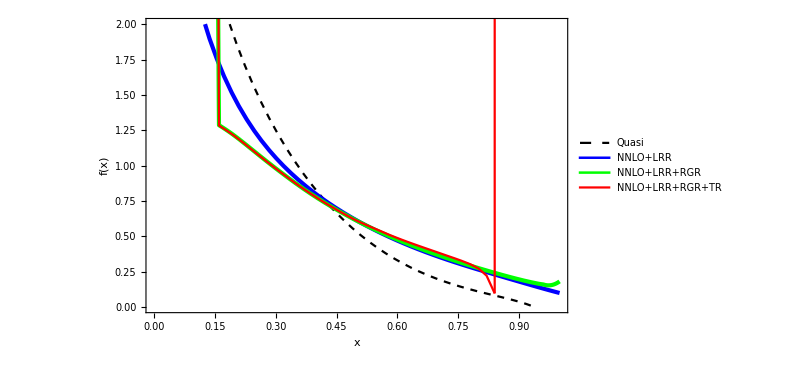

```mathematica
fig=Show[
Plot[qint[x],{x,0,1},PlotStyle->{Black,Dashed},
PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["Quasi",20]},{0.7,0.75}]],

Plot[fVint[x],{x,0.10,1},PlotStyle->{Blue,Thickness[0.005]},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc,20]},{0.7,0.65}]],

Plot[PDFRGRint[x],{x,0.14,1},PlotStyle->{Green,Thickness[0.005]},PlotRange->All,PlotLegends->Placed[{Style[PertAcc<>"+RGR",20]},{0.7,0.55}]],

Plot[PDFRGRTRint[x],{x,0.14,0.86},PlotStyle->Red,PlotRange->All,PlotLegends->Placed[{Style[PertAcc<>"+RGR+TR",20]},{0.7,0.45}]],

PlotRange->{{0,1},{0,2}},
FrameLabel->{Style["x",20],Style["f(x)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]

(*SetDirectory[NotebookDirectory[]];
Export["./pics/MCfull5NLO_add.pdf",fig]*)
```

#### μ_i=2|1-|x_i||P_z r1, μ_h=2|x_i| P_z r2, r1,r2=0.8~1.2

```mathematica
r1ls={1.2,1,0.8};
r2ls={1.2,1,0.8};
xlsf=Join[Table[N[1.0/50 i],{i,7,43}]];
```

```mathematica
(*Resummation and variation of r1 and r2*)
PDFRGRTRls=Table[
PrintTemporary[{r1,r2}];
(*Resummation on the inversed matrix*)
PDFls={};
PDFls2={};
μils=2*(1-xlsf)*Pz*r1;
μhls=2*xlsf*Pz*r2;
Monitor[
For[i=Length[μhls],i≥1,i--,

ChM=MfixGen[μhls[[i]]];
Quiet[If[μhls[[i]]>μils[[i]],
Hm=Hmgen[μhls[[i]]];
Jmμi=Jmgen[μils[[i]]];
Jmμh=Jmgen[μhls[[i]]];
PJm=PJmgen[μhls[[i]],μils[[i]]];
Strnew=(Mcut*PJm).(Mcut*Jmμi).(Mcut*Hm);
Strnew0=(Mcut*Jmμh).(Mcut*Hm);
PDFlist=Transpose[{xlist,(ChM+Strnew-Strnew0).qV}],
PDFlist=Transpose[{xlist,ChM.qV}]
];];

ClearAll[PDFint,PDFintsys,PDFCombine];
PDFint=Interpolation[PDFlist];
PDFintsys[x_]:=(PDFint[x]+PDFint[-x])/2;
If[μhls[[i]]>μils[[i]],
PDFCombine[x_]:=PDFintsys[x],
PDFCombine[x_]:=If[Abs[x]≤ xlsf[[i]]+Δx/4,PDFintsys[x],If[xlsf[[i]]+Δx/4<Abs[x]≤ xlsf[[i]]+(3Δx)/4,((xlsf[[i]]+(3Δx)/4)-Abs[x])/(Δx/2)PDFintsys[x]+(Abs[x]-(xlsf[[i]]+Δx/4))/(Δx/2)PDFls2[[Length[μhls]-i]][x],PDFls2[[Length[μhls]-i]][x]]]
];
(*PDFCombine[x_]:=PDFintsys[x];*)

If[PertAcc=="NNLO+LRR",
AppendTo[PDFls,DGLAPNNLOx[PDFCombine,μhls[[i]],μ,Mdglapns0,Mdglapns1,Mdglapns2,xDGLAP]];AppendTo[PDFls2,DGLAPNNLOx[PDFCombine,μhls[[i]],μhls[[i-1]],Mdglapns0,Mdglapns1,Mdglapns2,xDGLAP]];,
Nothing[]
];

],
Row[{ProgressIndicator[i,{1,Length[μhls]}],i}," "]
];
Table[PDFls[[Length[xlsf]-i+1]][xlsf[[i]]],{i,1,Length[xlsf]}]
,{r1,r1ls},{r2,r2ls}]
```

{{{1.35751,1.33896,1.29957,1.25143,1.20046,1.14927,1.09889,1.04931,1.00078,0.954558,0.910498,0.868465,0.828347,0.79002,0.753396,0.71835,0.684814,0.652743,0.621984,0.596316,0.570565,0.545454,0.519716,0.496081,0.473736,0.452483,0.431538,0.411281,0.391357,0.370505,0.350685,0.330355,0.308965,0.284724,0.253694,0.201361,0.00849772},{15.9681,1.2836,1.24678,1.20638,1.16189,1.11574,1.06944,1.02379,0.97921,0.935826,0.893221,0.852024,0.81263,0.774947,0.738905,0.704407,0.671394,0.639803,0.609574,0.580635,0.552874,0.528396,0.504484,0.481716,0.46002,0.4393,0.419125,0.399675,0.38065,0.360968,0.34234,0.32347,0.303967,0.282497,0.256161,0.214727,0.0829325},{1.84475×10^24,-16834.5,1.62705,1.16522,1.1212,1.07885,1.03642,0.994168,0.952485,0.911681,0.871941,0.833374,0.796032,0.7599,0.724737,0.690751,0.658203,0.627035,0.597178,0.568606,0.541255,0.515074,0.490014,0.466044,0.444772,0.424641,0.405188,0.386489,0.368318,0.349887,0.332373,0.31489,0.297163,0.278307,0.256378,0.22482,0.140409}},{{1.35595,1.33763,1.2984,1.25039,1.19954,1.14844,1.09814,1.04863,1.00017,0.954023,0.910033,0.868076,0.828043,0.789817,0.753321,0.718442,0.686423,0.658249,0.630784,0.603968,0.577968,0.552533,0.526054,0.502318,0.479873,0.458431,0.437174,0.416285,0.395397,0.373788,0.35242,0.329528,0.303241,0.2674,0.199224,0.00449393,16678.3},{15.9674,1.28307,1.24633,1.20598,1.16153,1.11542,1.06914,1.02352,0.97896,0.935597,0.893012,0.851835,0.812459,0.774796,0.738776,0.704301,0.671316,0.639758,0.609578,0.584033,0.559283,0.535098,0.510329,0.487545,0.465878,0.445127,0.424805,0.404959,0.385261,0.365091,0.345473,0.324918,0.302134,0.272737,0.221427,0.0959339,14591.4},{1.84475×10^24,-16834.5,1.62576,1.16415,1.12024,1.07798,1.03562,0.993416,0.951777,0.91101,0.871302,0.832763,0.795445,0.759334,0.72419,0.690221,0.657689,0.626535,0.59669,0.568132,0.540806,0.515111,0.492498,0.470751,0.449923,0.429937,0.410534,0.391708,0.373184,0.35451,0.336548,0.31821,0.298679,0.275146,0.238324,0.158501,13159.1}},{{1.35533,1.33711,1.29795,1.24999,1.19918,1.14813,1.09787,1.04839,0.999965,0.953852,0.909901,0.867989,0.828017,0.789923,0.759769,0.729231,0.700054,0.671652,0.64387,0.616668,0.590337,0.564579,0.537714,0.513865,0.491121,0.469205,0.447418,0.425509,0.403114,0.380325,0.354258,0.320515,0.262879,0.15878,-184.02,-1.20862×10^9,-1.71821×10^42},{15.9656,1.2817,1.24515,1.20493,1.16058,1.11455,1.06834,1.02278,0.978277,0.934963,0.892424,0.851293,0.811967,0.774361,0.73842,0.704152,0.674513,0.647776,0.621545,0.595888,0.570908,0.546472,0.521216,0.498449,0.476703,0.455798,0.435285,0.414969,0.394531,0.374094,0.351766,0.324598,0.282625,0.210208,-247.201,-8.74026×10^8,-1.31961×10^42},{1.84475×10^24,-16834.5,1.62535,1.16382,1.11995,1.07772,1.03538,0.993197,0.951576,0.910827,0.871135,0.832611,0.795309,0.759215,0.724091,0.690147,0.657653,0.626571,0.596985,0.571419,0.547951,0.525033,0.501839,0.480298,0.459661,0.439867,0.42064,0.401887,0.383346,0.36515,0.346218,0.324843,0.295706,0.246964,-3373.51,-5.41844×10^8,-8.49428×10^41}}}

```mathematica
PDFRGRTRintls=Table[Interpolation[Transpose[Re[{xlsf,PDFRGRTRls[[i,j]]}]],InterpolationOrder->1],{i,1,Length[r1ls]},{j,1,Length[r2ls]}];
```

InterpolatingFunction::dmval: Input value {0.100016} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

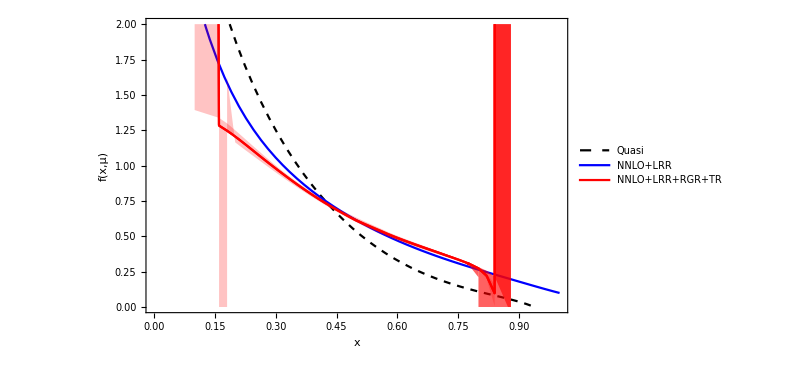

```mathematica
fig=Show[
Plot[qint[x],{x,0,1},PlotStyle->{Black,Dashed},
PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["Quasi",20]},{0.7,0.75}]],

Plot[fVint[x],{x,0.12,1},PlotStyle->Blue,PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc,20]},{0.7,0.65}]],

Plot[{PDFRGRTRintls[[2,2]][x],PDFRGRTRintls[[2,1]][x],PDFRGRTRintls[[2,3]][x]},{x,0.1,0.88},PlotStyle->{Red,Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618^3,Red]}},1->{{3},{Opacity[0.618^3,Red]}}},PlotRange->{{0,1},{0,2}}],

Plot[{PDFRGRTRintls[[2,2]][x],PDFRGRTRintls[[1,2]][x],PDFRGRTRintls[[3,2]][x]},{x,0.1,0.88},PlotStyle->{Red,Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618,Red]}},1->{{3},{Opacity[0.618,Red]}}},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc<>"+RGR+TR",20]},{0.7,0.55}]],

PlotRange->{{0,1},{0,2}},
FrameLabel->{Style["x",20],Style["f(x,μ)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]
```

#### μ_i=2|1-|x_i||P_z, μ_i0=2|x_i|P_z, μ_h=2|x_i| P_z, |1-ξ|<γ, γ=0.3~0.5

```mathematica
γls={0.3,0.4,0.5};
xlsf=Table[N[1.0/50 i],{i,7,43}];
```

```mathematica
(*Resummation and variation of r1 and r2*)
PDFRGRTRls=Table[
PrintTemporary[{γ}];
(*Resummation on the inversed matrix*)
Mcut=Table[If[Abs[1-y/x]<γ,1,0],{y,xlist},{x,xlist}];
PDFls={};
PDFls2={};
μils=2*(1-xlsf)*Pz;
μhls=2*xlsf*Pz;
Monitor[
For[i=Length[μhls],i≥1,i--,

ChM=MfixGen[μhls[[i]]];
Quiet[If[μhls[[i]]>μils[[i]],
Hm=Hmgen[μhls[[i]]];
Jmμi=Jmgen[μils[[i]]];
Jmμh=Jmgen[μhls[[i]]];
PJm=PJmgen[μhls[[i]],μils[[i]]];
Strnew=(Mcut*PJm).(Mcut*Jmμi).(Mcut*Hm);
Strnew0=(Mcut*Jmμh).(Mcut*Hm);
PDFlist=Transpose[{xlist,(ChM+Strnew-Strnew0).qV}],
PDFlist=Transpose[{xlist,ChM.qV}]
];];

PDFint=Interpolation[PDFlist];
PDFintsys[x_]:=(PDFint[x]+PDFint[-x])/2;
If[μhls[[i]]>μils[[i]],
PDFCombine[x_]:=PDFintsys[x],
PDFCombine[x_]:=If[Abs[x]≤ xlsf[[i]]+Δx/4,PDFintsys[x],If[xlsf[[i]]+Δx/4<Abs[x]≤ xlsf[[i]]+(3Δx)/4,((xlsf[[i]]+(3Δx)/4)-Abs[x])/(Δx/2)PDFintsys[x]+(Abs[x]-(xlsf[[i]]+Δx/4))/(Δx/2)PDFls2[[Length[μhls]-i]][x],PDFls2[[Length[μhls]-i]][x]]]
];
(*PDFCombine[x_]:=PDFintsys[x];*)

If[PertAcc=="NNLO+LRR",
AppendTo[PDFls,DGLAPNNLOx[PDFCombine,μhls[[i]],μ,Mdglapns0,Mdglapns1,Mdglapns2,xDGLAP]];AppendTo[PDFls2,DGLAPNNLOx[PDFCombine,μhls[[i]],μhls[[i-1]],Mdglapns0,Mdglapns1,Mdglapns2,xDGLAP]];,
Nothing[]
];

],
Row[{ProgressIndicator[i,{1,Length[μhls]}],i}," "]
];
Table[PDFls[[Length[xlsf]-i+1]][xlsf[[i]]],{i,1,Length[xlsf]}]
,{γ,γls}]
```

{{15.9675,1.28314,1.24639,1.20603,1.16158,1.11546,1.06918,1.02356,0.979,0.935635,0.893048,0.851869,0.812492,0.774828,0.738806,0.70433,0.671342,0.639782,0.609598,0.584779,0.560518,0.536855,0.513512,0.490831,0.468778,0.447273,0.426479,0.406571,0.387483,0.369558,0.352296,0.334745,0.316003,0.292704,0.254792,0.159252,2265.62},{15.9674,1.28307,1.24633,1.20598,1.16153,1.11542,1.06914,1.02352,0.97896,0.935597,0.893012,0.851835,0.812459,0.774796,0.738776,0.704301,0.671316,0.639758,0.609578,0.584033,0.559283,0.535098,0.510329,0.487545,0.465878,0.445127,0.424805,0.404959,0.385261,0.365091,0.345473,0.324918,0.302134,0.272737,0.221427,0.0959339,14591.4},{15.9674,1.28304,1.2463,1.20595,1.16151,1.1154,1.06912,1.0235,0.978944,0.935582,0.892997,0.851821,0.812446,0.774784,0.738764,0.70429,0.671306,0.639749,0.609571,0.583553,0.55869,0.533664,0.510362,0.48776,0.464611,0.44329,0.42242,0.401054,0.380832,0.360694,0.340197,0.319199,0.295752,0.266867,0.21335,0.096183,20695.6}}

```mathematica
PDFRGRTRintls2=Table[Interpolation[Transpose[Re[{xlsf,PDFRGRTRls[[i]]}]],InterpolationOrder->1],{i,1,Length[γls]}];
```

InterpolatingFunction::dmval: Input value {0.100016} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

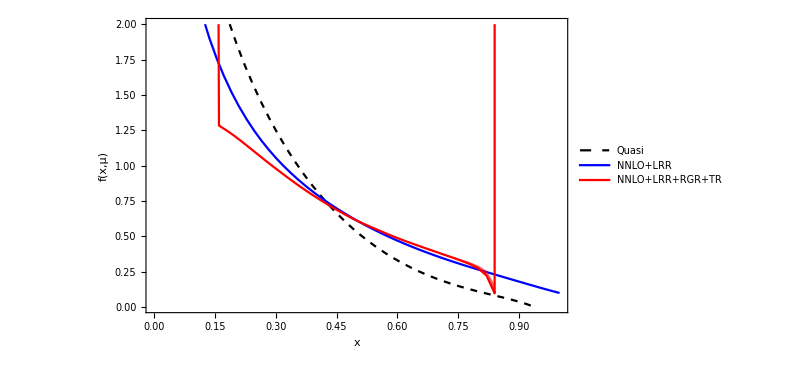

```mathematica
fig=Show[
Plot[qint[x],{x,0,1},PlotStyle->{Black,Dashed},
PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["Quasi",20]},{0.7,0.75}]],

Plot[fVint[x],{x,0.10,1},PlotStyle->Blue,PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc,20]},{0.7,0.65}]],

Plot[{PDFRGRTRintls2[[2]][x],PDFRGRTRintls2[[1]][x],PDFRGRTRintls2[[3]][x]},{x,0.1,0.9},PlotStyle->{Red,Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618,Red]}},1->{{3},{Opacity[0.618,Red]}}},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style[PertAcc<>"+RGR+TR",20]},{0.7,0.55}]],

PlotRange->{{0,1},{0,2}},
FrameLabel->{Style["x",20],Style["f(x,μ)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]

(*SetDirectory[NotebookDirectory[]];
Export["./pics/MCfull6err2_add.pdf",fig]*)
```

## Compare NLO and NNLO

### without renormalon, additive, L=3

#### data, λ_L=25, scale variation

```mathematica
PDFRGRTRlsNLO={{{1.3467996518428786,1.4681419489731502,1.509241443386508,1.4958391582421522,1.4558010656679137,1.402826177373952,1.343950674903559,1.2829107528343362,1.2216909017919546,1.1613135038978475,1.1025136266675755,1.0459134573705822,0.9915769141533246,0.9395229195831142,0.8897360809514534,0.8421444312765097,0.7966917046844358,0.7532610438998287,0.7117902033086799,0.6722421876868607,0.634584582064467,0.5965972905041276,0.5616187822647409,0.5293969739258167,0.4928155525219778,0.46391333348381303,0.4376219017370061,0.4065500843097786,0.38344259351612153,0.3614970378897441,0.3419718818486321,0.31590977916530877,0.29732740373163946,0.2797300447755983,0.2575509069124838,0.24122902752645106,0.2257949068698581,0.21271415474329403,0.19959896266151664,0.245929040328498,0.08184903194385551},{2.485005081503087,1.4046907729959754,1.4557158291942636,1.4670771798614417,1.4421684242352566,1.3985810154633376,1.34562345486278,1.288365972173637,1.2296272297023745,1.1709985814954105,1.1133915211310743,1.057329365268923,1.0031137615109313,0.9510049846853174,0.901055597830699,0.8532421320987965,0.8075321901856047,0.7638431032851503,0.7221234291560866,0.6823041864629067,0.6443154793619399,0.6080653849080951,0.5734439980281864,0.5392098737724246,0.5045635870154256,0.4735763552297303,0.4451647766958857,0.41475797159692623,0.38989261179101703,0.36652317817996605,0.3450714325446493,0.31987500491648513,0.3001131804557724,0.28124032581888314,0.25935749290041804,0.2421946244862067,0.22596066840249862,0.21182580701084064,0.198796589458327,0.2263098620624731,0.07139430977198455},{9.270921629147358*^6,2.7314345423323365,1.5195282617661774,1.4551246710859043,1.4440231640275374,1.4097174458203774,1.3626120998601503,1.3087164490741583,1.2517429384331515,1.193879773629715,1.1363933617320423,1.0800704108038652,1.0253350490402315,0.9724335912356358,0.9215001389212375,0.8726077690166147,0.8258702196376712,0.7812639451172325,0.7386428653969601,0.6979438653566302,0.6590852779750508,0.6220308834499044,0.5866929470725231,0.5529991841272638,0.5208714816975415,0.49021248019164554,0.45913844896593153,0.4287013324530103,0.40132317798426764,0.37585243957065706,0.3520865745689015,0.32716018685536835,0.30574811059131946,0.28525726809925345,0.2633768768212463,0.24504232733572487,0.22773595870112495,0.21233917246566159,0.1990499997208716,0.2133600227648599,0.05576632084418362}},{{1.3484328313705383,1.4693964145355158,1.5103126837054777,1.4967778532472662,1.4566359671756632,1.4035757847475374,1.3446276619501494,1.2835244219580957,1.2222476296155336,1.16181735800111,1.1029668891751285,1.0463162020449097,0.9919275217682728,0.9398172334407102,0.8899665202206029,0.8422988243789185,0.7967494127177116,0.7531877548806879,0.7110492914318086,0.6709376792641834,0.6284974128457251,0.592229249374636,0.5578942055940427,0.5264806846203643,0.4880434932810811,0.460068274059752,0.4347243208092409,0.40339143725557103,0.38116041656897304,0.3596627182356621,0.34024351464913005,0.3137879989863189,0.2957209466781051,0.2789137785505366,0.25757902661249693,0.24266437886053355,0.23013014310964475,0.22616620210159044,0.3669407896430617,0.09052699771323432,-2.512380771479854},{2.4869773445281185,1.4054345684705,1.4563045870446032,1.4675883496209576,1.4426233503426764,1.3989913404022591,1.3459968857388813,1.288707996881424,1.2299418114490936,1.171288825449605,1.113659656234851,1.057576975373116,1.0033418671133199,0.9512140047671026,0.9012453942853872,0.8534119563742913,0.8076804666801588,0.7639673590437731,0.7222195612501711,0.6823653077237146,0.644326306654306,0.6055260878538757,0.5691360608381585,0.5352970660991363,0.4988562604275064,0.46890317389517033,0.4415281827011606,0.4108620835331967,0.38695391948634356,0.3641062225216392,0.34277859756163775,0.3172005676908754,0.29797776239451823,0.2798803173411989,0.25877311087047644,0.24291120833362137,0.2292197861498737,0.2225726548803893,0.28721882979554264,0.0799063687269465,-1.8884863458773549},{9.178498018858016*^6,2.7379575712315107,1.5210353025749983,1.456254237697612,1.4450009709103746,1.4106014605142976,1.3634253924453872,1.309473580353102,1.2524542300440296,1.1945530145725374,1.1370348389126688,1.0806848680689212,1.025926546440134,0.9730055263754006,0.9220553967336014,0.8731488312675226,0.8263992661825134,0.7817828398475394,0.7391533065904249,0.6984475471489751,0.6595842975247315,0.6225270528553123,0.5871810254967715,0.5531116320377779,0.5174986006434442,0.48474015830258554,0.4545663314378421,0.42391064764822306,0.39758423136388865,0.37272875150030416,0.34910035716139104,0.3238269897454188,0.3029767668107062,0.28323411398485315,0.2620532428084015,0.24489089948988835,0.2297320448743481,0.22022862355055667,0.2504004179163178,0.0640524152779377,-1.4246329771476467}},{{1.3496359116893295,1.4703205128621462,1.5111019282851137,1.4974694796955572,1.4572511224637341,1.4041281074031842,1.3451265300400055,1.2839767541077574,1.2226582096707719,1.1621892845664628,1.103301951647344,1.0466145423838453,0.9921879512082742,0.9400364183372037,0.8901376533893984,0.8424057465632907,0.7962830812019394,0.7470788730001212,0.7054013787759742,0.6667857982727454,0.62063574132377,0.5858123134268862,0.5524310307524035,0.5220472284789006,0.48230872196524993,0.4551039056222826,0.43024224099296,0.3985003256386692,0.37692633924364966,0.3562334397544444,0.3380772534723745,0.31258255123346584,0.2959852864348623,0.2812896564893709,0.26381061908515496,0.2585298251427144,0.3007480111596869,0.08522152755708351,0.07717882477918267,1.0579299618152371,0.16710648775862452},{2.492038320715153,1.4073875361431658,1.4578595603581028,1.4689454392891625,1.443839309832058,1.4000974407479314,1.3470139284835856,1.2896508802798394,1.2308213808152264,1.1721137000690887,1.1144361440548227,1.0583096869229047,1.004033889845872,0.9518666684392608,0.9018580951278293,0.8539810411922762,0.8081942428438474,0.7643618504600102,0.7206490766491404,0.6788139963735954,0.6349594347439249,0.5976875659270933,0.562347027437299,0.5295130912109611,0.49183510585259604,0.4627638004471041,0.4359599261655267,0.4048700209229126,0.3816665920207571,0.35965015157310476,0.3395465088845295,0.3148430263429977,0.2969922541157884,0.28075394433010276,0.26283092921045315,0.2545303864998919,0.2759679829939944,0.043760687887736335,0.0716614927654211,1.1009684970217324,0.1656992723555646},{9.116008030478425*^6,2.7423602685958195,1.5220208749741198,1.4569886852022125,1.4456343806697192,1.4111718986460358,1.3639477314891675,1.3099571218887311,1.2529054982879453,1.1949768566247594,1.1374350723420414,1.0810642463730427,1.026287266705073,0.9733491892765124,0.9223830008740745,0.8734606477450994,0.8266944890124148,0.7820585814586715,0.7394017344249628,0.6986438175187193,0.6595739516149344,0.6199401203689489,0.5815301702192075,0.5455884745069983,0.5089012580375372,0.477151995647698,0.447663998775945,0.4166129876684524,0.391052811425722,0.3670663299281522,0.344606990155018,0.3201358690343405,0.30055240335581423,0.28240086698397976,0.26374431155592915,0.25226216654460626,0.2593034919683255,-0.09131350649075436,0.06559506965828071,1.161007563981439,0.1647640664875977}}};
```

```mathematica
PDFRGRTRlsNNLO={{{1.5474877076467577,1.5108147557139913,1.4939172961226146,1.4609238385087508,1.4169789277781484,1.3669404515115628,1.3139366246735715,1.259797147404452,1.2056244956857423,1.1523519793708341,1.1005879007424184,1.0504450800349554,1.0019939024056874,0.9552666516767372,0.910238952636731,0.8668967956842363,0.8251554068767244,0.7849836125667696,0.7463718774071358,0.709295859719676,0.6708657639239808,0.6333593889811101,0.5983081330853851,0.5704467814307648,0.5398085314028552,0.5083045178394826,0.4805552277376414,0.4540193260358931,0.4272314932497619,0.4035309118803517,0.386468783390362,0.3640490722775032,0.33841086194902337,0.31444725478607793,0.291259838788617,0.264895196925211,0.23595829937035914,0.1794361303336062,0.5804449262032861},{2.8691541842201445,1.575601713991538,1.4939139763662586,1.459515642123837,1.4188490656241155,1.3719511046672972,1.3213478826796252,1.2689798570068014,1.216148578168132,1.1636780395051485,1.1121184726736868,1.0619522365846734,1.013447662128966,0.9665964946700641,0.9214065724947321,0.8778795257065419,0.8359611600768031,0.7956297561687393,0.7568425135466829,0.719550747779432,0.6836840759327724,0.6491510851306213,0.6136820406154535,0.5811781569094161,0.5494094443874091,0.5180167155550631,0.4894405480878111,0.4620858994904776,0.4349691797163236,0.41038845130243046,0.39015502056224416,0.366874163369419,0.34161165300543456,0.31788633699061036,0.2945126485029584,0.2687412577555274,0.24076459219955132,0.19114693595526402,0.7677579922211677},{-4.122503550221849*^16,-118.75723178443664,1.7388379825318403,1.4796268880303058,1.4233972694240422,1.3782521618577288,1.3307757450342685,1.281013211095965,1.2300781432678738,1.1788934651938965,1.1281413017503894,1.0782579431914263,1.029536430130658,0.9821712665312161,0.9363178282081149,0.8922745529803032,0.8500247063192925,0.809324798561558,0.7701419687648166,0.7324187744982568,0.6961485250194278,0.6612640364184198,0.6277125845965922,0.5954359098150395,0.5643502295758513,0.5326281837340161,0.5024903234513707,0.473765147930475,0.44587266187466223,0.41994402112871765,0.396603917543971,0.37214118281127706,0.3468249997900308,0.32279230400809134,0.29889870785912537,0.27337679142679383,0.2459238800314675,0.2015915282804922,2.125595219507363}},{{1.5489432823475966,1.5119397508886128,1.494878301828966,1.4617675950787943,1.417730436898091,1.3676156263892485,1.3145466933673646,1.2603496867192776,1.2061243641797053,1.1528019575502766,1.1009883344614089,1.0507944886076188,1.002288091103412,0.9554977751025096,0.9103942992678644,0.8669548944112568,0.8250833417809592,0.7841743461291272,0.742684165372837,0.7030980809230362,0.6652756634910101,0.6268634965974695,0.5922589682150577,0.5667846721432824,0.5364369187044551,0.504743562458503,0.47752729217884926,0.4514621352503294,0.4245560492403349,0.40041216232740673,0.38326614354636973,0.3606766167805856,0.33466920910203657,0.31013897912788085,0.28497492181528744,0.2513123090855888,0.16580805016407194,0.4664833809289849,99.3525839827173},{2.87247244090996,1.576204342158213,1.4943719642041595,1.4599109942826431,1.4192007262481958,1.372268665670088,1.3216374627896297,1.2692456450919463,1.2163937453580917,1.1639048287776188,1.1123284700678606,1.0621464752135257,1.0136265862405351,0.9667600195885026,0.9215540366539109,0.8780094802208593,0.8360712905375279,0.7957161807060952,0.7568987196134204,0.7195630988324676,0.6808755888590576,0.642798166385549,0.6072069783960959,0.5769758347324352,0.5455289467518754,0.5140062261762298,0.4860387361859773,0.459171922906183,0.431929866023523,0.4068994007700296,0.3864853335212406,0.3630096874338293,0.337376087685397,0.31304831434628533,0.28777640965042267,0.2554926587782679,0.1857362968509481,0.5369376822568082,167.58465805258385},{-4.118608444922763*^16,-118.68244068137162,1.740480876749145,1.4805712438948546,1.424186159958069,1.378958945360502,1.3314246158610046,1.2816175905855356,1.2306470542288637,1.1794337221387052,1.1286578884662861,1.0787550194364581,1.030017434444455,0.9826391061757223,0.9367750099027597,0.8927232982955416,0.8504669302667366,0.8097622633844158,0.7705764264128758,0.7328522716426827,0.6965824155060361,0.6616891282326881,0.6276282837594622,0.5930302477249048,0.5600376448033357,0.5280442574666387,0.49860442015540996,0.47040046613754305,0.44238787001156843,0.4160028783502452,0.3923554993233969,0.3676601705151732,0.34196630009557893,0.31728536042410665,0.29154314165625433,0.2601935378559318,0.2013574817368993,0.7226741690166697,-2702.4679008063536}},{{1.5497469722504054,1.5125583558090627,1.4954046608965224,1.4622273603402332,1.4181372218354933,1.367978015344739,1.3148706395921457,1.260639061464369,1.2063814311918581,1.1530276357285358,1.1011818854661477,1.0509534681168022,1.0024069818046881,0.9555640964079543,0.9103569480740866,0.8615241690218519,0.8202799646059828,0.778167603780736,0.7343930784792875,0.6949555601871688,0.6574570079994145,0.6184523890406637,0.5844469748883275,0.561164428719249,0.5307633762331496,0.4980852368482895,0.47070649691101024,0.4444830995044071,0.41758110077824734,0.39412464047869344,0.3777316205950041,0.3550423034844545,0.32793001582800363,0.3007093077034537,0.2544853860720984,0.38120291899006187,0.7011148606594814,-7.190393371555247*^13,0.24748021073382118},{2.8809700966986824,1.5778135210761195,1.4956041618932718,1.4609803164699713,1.4201579335956387,1.3731397566369061,1.3224391296235134,1.2699893792905668,1.2170883146193294,1.1645564792224352,1.112941629278651,1.06272394981055,1.0141692570947305,0.9672665265937518,0.9220191838106625,0.8784174768365485,0.8363360586736496,0.7941355998911453,0.751091201408166,0.7108271729606173,0.672343238372804,0.6336940448003703,0.5988164307454771,0.5707005234383826,0.5392437290909017,0.5067821799162071,0.47867589458853316,0.4516052809161626,0.42427178436016744,0.39983899995501,0.3799825190856502,0.35623342835122096,0.32922381421930136,0.30148766433360974,0.2567442561134936,0.5166235845018051,0.79876203532296,-5.641317483768234*^13,0.24798176523671314},{-4.11678242256306*^16,-118.6314812555423,1.7412771499921897,1.4810226632728003,1.4245610702812697,1.3792930611303484,1.3317294708647358,1.2818994665204233,1.2309100791207213,1.1796809088519031,1.128891305408365,1.0789762261006948,1.0302274744131237,0.9828384936747406,0.936963595285971,0.8928999132837981,0.8506284152405917,0.8099007442463502,0.7706682494548005,0.7327601476730234,0.6939234585205489,0.6549651120067138,0.6185359204829541,0.5858945893408227,0.5529526411321884,0.5201119876003475,0.4905678126599143,0.46212435868058827,0.43392561473681074,0.4080328919967824,0.3847159683558333,0.3595512241029144,0.3322099323733162,0.3035195734695334,0.25984420164129435,6.407670566611788,0.9514247396868374,-3.870664844251085*^13,0.24846584958858248}}};
```

#### plot, √(σ_h^2+σ_i^2)

```mathematica
ClearAll[PDFRGRTRintNLOcv,PDFRGRTRintNLOherr,PDFRGRTRintNLOierr,PDFRGRTRintNNLOcv,PDFRGRTRintNNLOherr,PDFRGRTRintNNLOierr];
xlsfNLO=Table[N[1.0/50 i],{i,5,45}];
(*PDFRGRTRNLOcvls=Mean[Flatten[PDFRGRTRlsNLO,1]];*)
PDFRGRTRNLOcvls=PDFRGRTRlsNLO[[2,2]];
PDFRGRTRintNLOcv=Interpolation[Transpose[{xlsfNLO,PDFRGRTRNLOcvls}],InterpolationOrder->1];

PDFRGRTRNLOhsdls=StandardDeviation[PDFRGRTRlsNLO[[2,;;]]];
PDFRGRTRintNLOherr=Interpolation[Transpose[{xlsfNLO,PDFRGRTRNLOhsdls}],InterpolationOrder->1];

PDFRGRTRNLOisdls=StandardDeviation[PDFRGRTRlsNLO[[;;,2]]];
PDFRGRTRintNLOierr=Interpolation[Transpose[{xlsfNLO,PDFRGRTRNLOisdls}],InterpolationOrder->1];

PDFRGRTRintNLOerr[x_]:=√(PDFRGRTRintNLOherr[x]^2+PDFRGRTRintNLOierr[x]^2);



xlsfNNLO=Table[N[1.0/50 i],{i,6,44}];
(*PDFRGRTRNNLOcvls=Mean[Flatten[PDFRGRTRlsNNLO,1]];*)
PDFRGRTRNNLOcvls=PDFRGRTRlsNNLO[[2,2]];
PDFRGRTRintNNLOcv=Interpolation[Transpose[{xlsfNNLO,PDFRGRTRNNLOcvls}],InterpolationOrder->1];

PDFRGRTRNNLOhsdls=StandardDeviation[PDFRGRTRlsNNLO[[2,;;]]];
PDFRGRTRintNNLOherr=Interpolation[Transpose[{xlsfNNLO,PDFRGRTRNNLOhsdls}],InterpolationOrder->1];

PDFRGRTRNNLOisdls=StandardDeviation[PDFRGRTRlsNNLO[[;;,2]]];
PDFRGRTRintNNLOierr=Interpolation[Transpose[{xlsfNNLO,PDFRGRTRNNLOisdls}],InterpolationOrder->1];

PDFRGRTRintNNLOerr[x_]:=√(PDFRGRTRintNNLOherr[x]^2+PDFRGRTRintNNLOierr[x]^2);
```

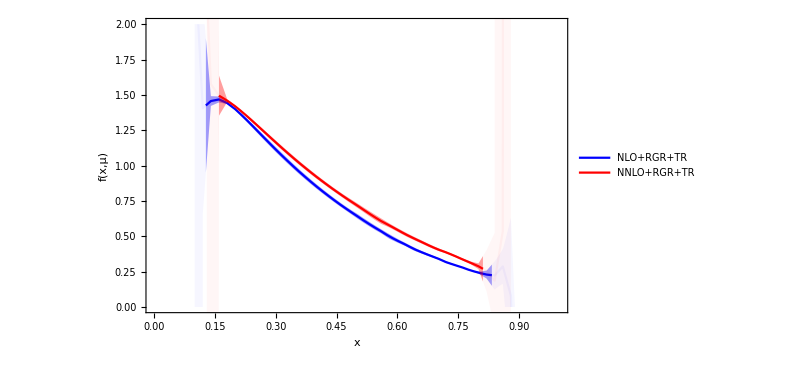

./pics/NLO_NNLO_wo_renormalon_add6.pdf

```mathematica
fig=Show[

Plot[{PDFRGRTRintNLOcv[x],PDFRGRTRintNLOcv[x]+PDFRGRTRintNLOerr[x],PDFRGRTRintNLOcv[x]-PDFRGRTRintNLOerr[x]},{x,0.127715,0.832990},PlotStyle->{Blue,Opacity[0,Blue],Opacity[0,Blue]},Filling->{1->{{2},{Opacity[0.618^2,Blue]}},1->{{3},{Opacity[0.618^2,Blue]}}},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["NLO+RGR+TR",20]},{0.55,0.8}]],

Plot[{PDFRGRTRintNLOcv[x],PDFRGRTRintNLOcv[x]+PDFRGRTRintNLOerr[x],PDFRGRTRintNLOcv[x]-PDFRGRTRintNLOerr[x]},x∈ImplicitRegion[0.1≤x≤0.127715||0.832990≤x≤0.9,{x}],PlotStyle->{Opacity[0.618^7,Blue],Opacity[0,Blue],Opacity[0,Blue]},Filling->{1->{{2},{Opacity[0.618^7,Blue]}},1->{{3},{Opacity[0.618^7,Blue]}}},PlotRange->{{0,1},{0,2}}],

Plot[{PDFRGRTRintNNLOcv[x],PDFRGRTRintNNLOcv[x]+PDFRGRTRintNNLOerr[x],PDFRGRTRintNNLOcv[x]-PDFRGRTRintNNLOerr[x]},{x,0.159897,0.810994},PlotStyle->{Red,Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618^2,Red]}},1->{{3},{Opacity[0.618^2,Red]}}},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["NNLO+RGR+TR",20]},{0.55,0.7}]],

Plot[{PDFRGRTRintNNLOcv[x],PDFRGRTRintNNLOcv[x]+PDFRGRTRintNNLOerr[x],PDFRGRTRintNNLOcv[x]-PDFRGRTRintNNLOerr[x]},x∈ImplicitRegion[0.13≤x≤0.159897∨0.810994≤x≤0.88,{x}],PlotStyle->{Opacity[0.618^7,Red],Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618^7,Red]}},1->{{3},{Opacity[0.618^7,Red]}}}],

PlotRange->{{0,1},{0,2}},
FrameLabel->{Style["x",20],Style["f(x,μ)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]

SetDirectory[NotebookDirectory[]];
Export["./pics/NLO_NNLO_wo_renormalon_add6.pdf",fig]
```

#### data, λ_L=25, threshold cut variation

```mathematica
PDFRGRTRls2NLO={{2.487294834074457,1.405562170695839,1.4564072205610856,1.467678735162951,1.4427052708050287,1.3990669164443097,1.3460675423543598,1.2887747681021846,1.2300054644394385,1.1713499895736619,1.1137188152571682,1.0576345126153188,1.0033980811461505,0.9512690989904221,0.9012994855782911,0.8534650616738637,0.807732433311909,0.764017867343768,0.7222678682236138,0.6824098524690739,0.6443641621409127,0.6079189572587312,0.5723674558061608,0.5375382306494971,0.5042925701007513,0.47237648286691175,0.4412289968777472,0.41173090290646025,0.38883125554472114,0.3616283159289855,0.336399878588279,0.3133942382880516,0.29265188419091986,0.27296809893965573,0.258488564448035,0.24173184996025407,0.2264302277396023,0.21625674666842862,0.2560192103857031,0.11136376191359978,-0.7935053771579833},{2.4869773445281185,1.4054345684705,1.4563045870446032,1.4675883496209576,1.4426233503426764,1.3989913404022591,1.3459968857388813,1.288707996881424,1.2299418114490936,1.171288825449605,1.113659656234851,1.057576975373116,1.0033418671133199,0.9512140047671026,0.9012453942853872,0.8534119563742913,0.8076804666801588,0.7639673590437731,0.7222195612501711,0.6823653077237146,0.644326306654306,0.6055260878538757,0.5691360608381585,0.5352970660991363,0.4988562604275064,0.46890317389517033,0.4415281827011606,0.4108620835331967,0.38695391948634356,0.3641062225216392,0.34277859756163775,0.3172005676908754,0.29797776239451823,0.2798803173411989,0.25877311087047644,0.24291120833362137,0.2292197861498737,0.2225726548803893,0.28721882979554264,0.0799063687269465,-1.8884863458773549},{2.486997301086157,1.4054424560765766,1.4563108873267407,1.4675938531973485,1.442628291296195,1.3989958475699646,1.3460010429412288,1.2887118618987585,1.2299454236949485,1.1712922133779844,1.1136628366910324,1.057579955702004,1.0033446453702628,0.9512165683800701,0.9012477195110404,0.8534140067633768,0.8076821908392976,0.7639686947392181,0.7222204518031267,0.6823658144420136,0.6443277292752249,0.6046170087482645,0.5694279680136255,0.533813493486556,0.499773439656697,0.4725308675296495,0.44188516623041085,0.4128406189705295,0.3909182286078231,0.36438161922528084,0.33917341732711825,0.32067777601595115,0.29792876921306866,0.277014143675675,0.26226474051799603,0.24477127526970205,0.23139313735596628,0.23214367286023516,0.3450095422479836,0.033768380638429615,-3.787155743799039}};
```

```mathematica
PDFRGRTRls2NNLO={{2.872008879209411,1.5761183358030857,1.4943063262861243,1.4598541616094163,1.4191499885767458,1.37222263985849,1.3215952605759669,1.2692066527942913,1.2163574914864583,1.1638709708429575,1.1122967538443176,1.0621167175763508,1.0135986775706285,0.9667339095402487,0.9215297320702069,0.8779870627792857,0.8360508911489316,0.7956980235287802,0.7568830919580629,0.7195496059015674,0.680431792059111,0.6430251501216031,0.6076706750622725,0.5754109090247344,0.5430647106503449,0.5119292723608342,0.48256764752952525,0.4539183494270166,0.42578804841224466,0.398023154304041,0.37501733567296597,0.35200449282670354,0.3298693631157996,0.3039543719145181,0.2817770842903002,0.25765069987525435,0.22507222853801176,0.2166837787089631,50.02259407338425},{2.87247244090996,1.576204342158213,1.4943719642041595,1.4599109942826431,1.4192007262481958,1.372268665670088,1.3216374627896297,1.2692456450919463,1.2163937453580917,1.1639048287776188,1.1123284700678606,1.0621464752135257,1.0136265862405351,0.9667600195885026,0.9215540366539109,0.8780094802208593,0.8360712905375279,0.7957161807060952,0.7568987196134204,0.7195630988324676,0.6808755888590576,0.642798166385549,0.6072069783960959,0.5769758347324352,0.5455289467518754,0.5140062261762298,0.4860387361859773,0.459171922906183,0.431929866023523,0.4068994007700296,0.3864853335212406,0.3630096874338293,0.337376087685397,0.31304831434628533,0.28777640965042267,0.2554926587782679,0.1857362968509481,0.5369376822568082,167.58465805258385},{2.872901222463248,1.5762863852504785,1.4944348777856709,1.4599656245461317,1.4192496619190809,1.3723132341848878,1.3216785149971477,1.269283764562745,1.2164293751479611,1.163938281927645,1.1123599663336006,1.062176153359188,1.0136544947311845,0.9667861191924192,0.9215781830897514,0.8780313715681646,0.8360904203717305,0.7957316285087187,0.7569086689302135,0.7195618725593794,0.6812432477328267,0.6437000212591169,0.6126144399084549,0.5783628132101174,0.5454035750523132,0.5207620075570348,0.4899995713582942,0.46059239949708325,0.439441745150269,0.4105484473652035,0.38290503567710865,0.36323772671949917,0.3355924228246671,0.3079051215246734,0.2843723395322654,0.24126795581352878,0.1011090880302795,1.0918304166545791,308.9949411002011}};
```

#### plot, √(σ_h^2+σ_i^2+σ_γ^2)

```mathematica
ClearAll[PDFRGRTRintNLOcv,PDFRGRTRintNLOherr,PDFRGRTRintNLOierr,PDFRGRTRintNNLOcv,PDFRGRTRintNNLOherr,PDFRGRTRintNNLOierr];
xlsfNLO=Table[N[1.0/50 i],{i,5,45}];
(*PDFRGRTRNLOcvls=Mean[Flatten[PDFRGRTRlsNLO,1]];*)
PDFRGRTRNLOcvls=PDFRGRTRlsNLO[[2,2]];
PDFRGRTRintNLOcv=Interpolation[Transpose[{xlsfNLO,PDFRGRTRNLOcvls}],InterpolationOrder->1];

PDFRGRTRNLOhsdls=StandardDeviation[PDFRGRTRlsNLO[[2,;;]]];
PDFRGRTRintNLOherr=Interpolation[Transpose[{xlsfNLO,PDFRGRTRNLOhsdls}],InterpolationOrder->1];

PDFRGRTRNLOisdls=StandardDeviation[PDFRGRTRlsNLO[[;;,2]]];
PDFRGRTRintNLOierr=Interpolation[Transpose[{xlsfNLO,PDFRGRTRNLOisdls}],InterpolationOrder->1];

PDFRGRTRNLOγsdls=StandardDeviation[PDFRGRTRls2NLO];
PDFRGRTRintNLOγerr=Interpolation[Transpose[{xlsfNLO,PDFRGRTRNLOγsdls}],InterpolationOrder->1];

PDFRGRTRintNLOerr[x_]:=√(PDFRGRTRintNLOherr[x]^2+PDFRGRTRintNLOierr[x]^2+PDFRGRTRintNLOγerr[x]^2);



xlsfNNLO=Table[N[1.0/50 i],{i,6,44}];
(*PDFRGRTRNNLOcvls=Mean[Flatten[PDFRGRTRlsNNLO,1]];*)
PDFRGRTRNNLOcvls=PDFRGRTRlsNNLO[[2,2]];
PDFRGRTRintNNLOcv=Interpolation[Transpose[{xlsfNNLO,PDFRGRTRNNLOcvls}],InterpolationOrder->1];

PDFRGRTRNNLOhsdls=StandardDeviation[PDFRGRTRlsNNLO[[2,;;]]];
PDFRGRTRintNNLOherr=Interpolation[Transpose[{xlsfNNLO,PDFRGRTRNNLOhsdls}],InterpolationOrder->1];

PDFRGRTRNNLOisdls=StandardDeviation[PDFRGRTRlsNNLO[[;;,2]]];
PDFRGRTRintNNLOierr=Interpolation[Transpose[{xlsfNNLO,PDFRGRTRNNLOisdls}],InterpolationOrder->1];

PDFRGRTRNNLOγsdls=StandardDeviation[PDFRGRTRls2NNLO];
PDFRGRTRintNNLOγerr=Interpolation[Transpose[{xlsfNNLO,PDFRGRTRNNLOγsdls}],InterpolationOrder->1];

PDFRGRTRintNNLOerr[x_]:=√(PDFRGRTRintNNLOherr[x]^2+PDFRGRTRintNNLOierr[x]^2+PDFRGRTRintNNLOγerr[x]^2);
```

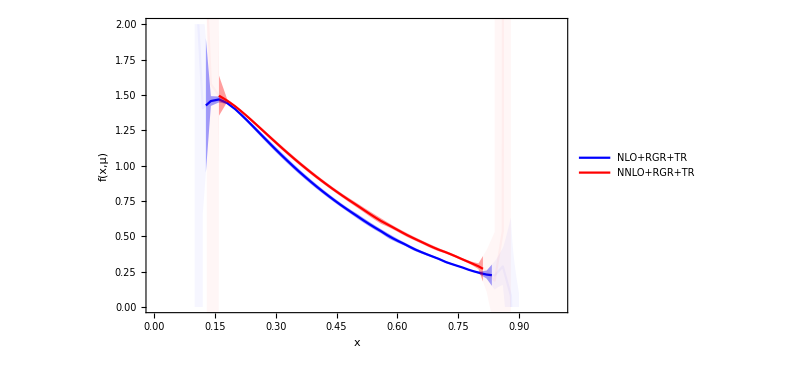

./pics/NLO_NNLO_wo_renormalon_add6.pdf

```mathematica
fig=Show[

Plot[{PDFRGRTRintNLOcv[x],PDFRGRTRintNLOcv[x]+PDFRGRTRintNLOerr[x],PDFRGRTRintNLOcv[x]-PDFRGRTRintNLOerr[x]},{x,0.127715,0.832990},PlotStyle->{Blue,Opacity[0,Blue],Opacity[0,Blue]},Filling->{1->{{2},{Opacity[0.618^2,Blue]}},1->{{3},{Opacity[0.618^2,Blue]}}},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["NLO+RGR+TR",20]},{0.55,0.8}]],

Plot[{PDFRGRTRintNLOcv[x],PDFRGRTRintNLOcv[x]+PDFRGRTRintNLOerr[x],PDFRGRTRintNLOcv[x]-PDFRGRTRintNLOerr[x]},x∈ImplicitRegion[0.1≤x≤0.127715||0.832990≤x≤0.9,{x}],PlotStyle->{Opacity[0.618^7,Blue],Opacity[0,Blue],Opacity[0,Blue]},Filling->{1->{{2},{Opacity[0.618^7,Blue]}},1->{{3},{Opacity[0.618^7,Blue]}}},PlotRange->{{0,1},{0,2}}],

Plot[{PDFRGRTRintNNLOcv[x],PDFRGRTRintNNLOcv[x]+PDFRGRTRintNNLOerr[x],PDFRGRTRintNNLOcv[x]-PDFRGRTRintNNLOerr[x]},{x,0.159897,0.810994},PlotStyle->{Red,Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618^2,Red]}},1->{{3},{Opacity[0.618^2,Red]}}},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["NNLO+RGR+TR",20]},{0.55,0.7}]],

Plot[{PDFRGRTRintNNLOcv[x],PDFRGRTRintNNLOcv[x]+PDFRGRTRintNNLOerr[x],PDFRGRTRintNNLOcv[x]-PDFRGRTRintNNLOerr[x]},x∈ImplicitRegion[0.13≤x≤0.159897∨0.810994≤x≤0.88,{x}],PlotStyle->{Opacity[0.618^7,Red],Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618^7,Red]}},1->{{3},{Opacity[0.618^7,Red]}}}],

PlotRange->{{0,1},{0,2}},
FrameLabel->{Style["x",20],Style["f(x,μ)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]

SetDirectory[NotebookDirectory[]];
Export["./pics/NLO_NNLO_wo_renormalon_add6.pdf",fig]
```

### Considering renormalon series, additive, L=3 NLO and L=4 NNLO

#### data, λ_L=25, scale variation

```mathematica
PDFRGRTRlsNLO={{{1.4283478562131704,1.4581398822548937,1.4321553012995685,1.3854007230554934,1.3311087724620334,1.274810755651971,1.2189604434783536,1.1645552976939202,1.1117117255732811,1.0606153651556103,1.0120446511538312,0.9658562074518777,0.9219136428698831,0.8800895431491129,0.8402463118678256,0.8022777869355046,0.7660498445961863,0.7314866644871542,0.6985529646548742,0.6671829646866136,0.6398935623069089,0.6123727549283584,0.5856830757841742,0.5590392417987011,0.5342811929995476,0.5110965609360263,0.4891866870327278,0.46770885733478373,0.44710238487583903,0.42693504588849723,0.406080828174211,0.3863269834104332,0.36647572063169265,0.34636032824093105,0.3254343176601823,0.3027907571589714,0.2759812318850727,0.2366413510906128,0.06692413253197893},{1.598929582276852,1.2833993964709702,1.3056504896204193,1.2885175217331724,1.25331778643403,1.2099084263812057,1.1631214396084706,1.1153998434052714,1.068026988241896,1.021650470365426,0.9765604687695743,0.932563327340846,0.8901314042107225,0.8495436308585589,0.8107329845229826,0.7736363557912522,0.7381614124453454,0.7042453809735225,0.671819431360153,0.6408193841249153,0.6111738373409759,0.5827912367081742,0.5570920650903765,0.5319937639943453,0.5081346445115776,0.4855816204970517,0.464214911260766,0.443528289060665,0.42374046375516367,0.40450918688028165,0.38473883001525866,0.36618125976398674,0.34770650773193224,0.32921025996738157,0.3102797347847441,0.29027366708742336,0.2676188469303188,0.2374837288651362,0.14671584901443666},{1.2948840713833287*^13,170.08866946612923,1.1885621389430547,1.1891732341390424,1.1743657398183551,1.1457953906402978,1.109555333160248,1.0694458284813921,1.0276839564984979,0.9855555667555557,0.9438248947472816,0.9029353566841897,0.8631428497859308,0.8245860597898278,0.787311476663314,0.7511785597376889,0.7163397442589786,0.6829698078695003,0.6510175664336824,0.6204165712994847,0.5911359141026004,0.563105893058103,0.5362689998063697,0.5105683565794739,0.4859579614599167,0.4635364473380971,0.44246468282823537,0.4222667216266787,0.40301093253882053,0.38444428051312834,0.3656670321361927,0.3480408007710714,0.330702692432864,0.3135583959204095,0.2963452663492949,0.2786352535843533,0.25953904666658306,0.2366610200161619,0.18825040849132813}},{{1.4256510749155678,1.4558339175049149,1.4301308176688718,1.3835956512457606,1.3294831957769224,1.2733373605499578,1.2176192105750698,1.1633325635945053,1.1105988846898331,1.0596077646251527,1.011142624451974,0.9650640429922718,0.9212416972181063,0.8795566740160231,0.8398833865873376,0.8021389603631992,0.7662337437449022,0.7330146799681359,0.7025079702787329,0.67296612494465,0.6443101109230323,0.6166313971737422,0.5897388745887016,0.5625820045645247,0.5378171109750941,0.514674856533522,0.4927487467079861,0.4711226769805201,0.45011697696891134,0.42932395487514796,0.407915370760169,0.38734628016283634,0.36637722395964367,0.34455206941766775,0.3205774333286924,0.2914796243557175,0.24418243342155174,-0.2359141666623239,72.39898991344597},{1.5977956697705704,1.2824986783296386,1.304866043735052,1.2878165602765645,1.2526823195612309,1.2093265160436624,1.1625845618746597,1.114901820037413,1.0675629436239666,1.0212168708721918,0.9761547641887306,0.9321838294827042,0.8897773614898143,0.8492151727635479,0.810431232482159,0.7733638450717919,0.7379222333315253,0.7040466258515508,0.6716734780151097,0.640752188110795,0.6132938301386525,0.586859990839781,0.5612059301372005,0.5354440598626011,0.5116164212924907,0.4891755958779238,0.46788145670830733,0.4471355098725907,0.42707741192428095,0.4073609018687889,0.3871655525415898,0.36807339644550474,0.34887428066409976,0.3292830037334456,0.3083884348403326,0.28434444430869965,0.24979292831781807,0.057190591933449574,34.27565112893579},{1.294884071383326*^13,170.08715754902863,1.1874323474110737,1.1881969263108507,1.173484598530697,1.1449864369494356,1.108804102824594,1.0687420851036864,1.027019987756233,0.9849251618919324,0.943223378277126,0.9023587413959047,0.8625878134976779,0.824049795881845,0.7867915835018175,0.7506729362111014,0.7158465925728923,0.6824874679016891,0.6505443143400849,0.619950111726048,0.5906735422748497,0.5626471112688854,0.5360665014081295,0.5118515075176656,0.4887082786113174,0.46672582905122095,0.4458282973856861,0.4256877420856902,0.40631793063988914,0.38742868407297915,0.3683284301353578,0.35043847801473926,0.33273690255158866,0.3150325156905439,0.29675464374117877,0.2768880933558729,0.25187250905981007,0.1690005512983752,1.207960795409175}},{{1.4238608932609733,1.4542966743572943,1.4287733606767763,1.3823762941289799,1.3283750645471386,1.2723220139120102,1.2166830562483044,1.1624662731816453,1.1097965845266096,1.0588663463705297,1.0104627345128954,0.9644497115442576,0.9207029948464651,0.8791152240060337,0.8396022980251692,0.8056155358257744,0.772407635028134,0.7406787195166439,0.7100448193011065,0.6802807504008489,0.651336614725045,0.6234030876508172,0.5962390757327938,0.5686349186090909,0.5437248696868331,0.52031094100062,0.49802148579690386,0.47596051641479065,0.4542136920060981,0.43248984245890215,0.4103230753783434,0.38779529542566227,0.3635702271908307,0.3354584560767966,0.2952171286387272,0.19055347129601372,-5.630403271183196,164635.23737355103,-1.1806801256768092*^18},{1.595358952701694,1.2805542887945716,1.3031655840303202,1.2862889562620805,1.2512882390410716,1.2080396918856349,1.1613860716861217,1.1137777613564648,1.066502103387088,1.0202108230321365,0.9751970513026634,0.9312696748326548,0.8889038516305634,0.848381220204028,0.8096383632350902,0.7726205468946242,0.7372856974039934,0.705297887725472,0.6761101896169245,0.647747970569918,0.6202083259925779,0.5935438378513956,0.5676132074294288,0.5412620826139376,0.5173299450353201,0.49471164138894685,0.47320699587691967,0.4521889776747445,0.43167896305788545,0.41142024060442267,0.39092043911730745,0.3706472837132248,0.34946575068263935,0.3261790554715887,0.29611580573375085,0.23867524117319347,-5.5524518419948805,126565.26448105909,-7.938413245652604*^17},{1.2948840713833258*^13,170.08667071121383,1.1870688968686316,1.1878829846282095,1.1732013695964267,1.144726549416091,1.1085629237760495,1.0685163414228784,1.0268072212430523,0.984723405276005,0.9430311719453089,0.9021748733137084,0.8624113320053393,0.8238800011892586,0.7866280741657775,0.7505157622302812,0.7156967380058553,0.6823483081881153,0.6504281063236246,0.6199413144083445,0.5923268400197593,0.5666147529025227,0.5416846781230096,0.5167053918733052,0.4935425198743972,0.4715159916350504,0.4505826983488142,0.4303574305289798,0.4108282913368947,0.39176378827217595,0.37269783105664217,0.35428504275429623,0.33562299063532663,0.31617097585781756,0.2935592455607742,0.26106831459413093,-6.818964010134795,86523.63147887726,-4.4802752720898694*^17}}};
```

```mathematica
PDFRGRTRlsNNLO={{{1.3575084331010372,1.3389593591236435,1.29956580446769,1.2514251339439715,1.2004591492514598,1.1492724175997822,1.0988933930268108,1.0493073533197539,1.0007757434429958,0.9545581124741799,0.9104975390424018,0.868464585659602,0.8283465483542274,0.7900200715379252,0.753396148255154,0.7183500236227193,0.6848136764123933,0.6527432991419986,0.621983900716279,0.5963161561637067,0.5705646983204478,0.5454540049897257,0.5197155819076312,0.4960806012515956,0.4737355514320618,0.4524829713492268,0.43153786556240226,0.4112814478231893,0.3913572928103662,0.37050528157026236,0.3506854763195252,0.3303553261929767,0.3089648507571774,0.2847235794576661,0.2536940804615611,0.20136104548706163,0.008497721642024076},{15.968099431156272,1.2835960850309962,1.2467820135639538,1.2063787689628407,1.161891662655705,1.1157440364490052,1.0694359620042373,1.0237898008091808,0.9792096764787339,0.9358257007354512,0.8932206167893457,0.8520241590861807,0.8126295866484936,0.7749469927318228,0.7389050347337696,0.7044069266000258,0.6713942232678815,0.6398030161890139,0.6095736823661457,0.5806345139982424,0.5528740981450934,0.528395793670977,0.5044839379865607,0.4817163407815948,0.4600197901278031,0.43930004520297605,0.4191249622823076,0.39967492276751987,0.3806496217724693,0.3609680958094867,0.3423400719548733,0.3234696706803921,0.30396686772218806,0.2824965991435214,0.2561613131430676,0.21472696929481477,0.08293247199295317},{1.8447519385252414*^24,-16834.49465232814,1.6270512289431307,1.1652195695179988,1.1211959428367726,1.0788538509513232,1.0364216701146156,0.9941684013089515,0.9524853202021799,0.9116814947936818,0.8719412179993737,0.8333739916505998,0.796032125068128,0.7598996175610294,0.7247368196846703,0.690751055352364,0.658203025258115,0.627034807732285,0.5971775192023258,0.5686063154619528,0.5412553087883302,0.5150740912775374,0.49001421105022597,0.46604440088351,0.4447715477367822,0.4246406087650221,0.4051878938560713,0.3864888622276082,0.3683175921287565,0.34988675741977016,0.33237275848910636,0.3148903791390682,0.29716263513654684,0.27830731909521667,0.256377765479586,0.2248198947866702,0.14040932969087447}},{{1.3559544450499166,1.3376341238376188,1.2984047673818122,1.2503938154925642,1.1995355503631524,1.1484409484346307,1.0981434365574707,1.0486319636773966,1.0001707549895333,0.9540225745036102,0.9100328544289924,0.8680756341501276,0.8280428424437013,0.7898172502319406,0.7533208514496036,0.7184419797529835,0.6864233174542127,0.6582494192840486,0.6307836660350481,0.6039675150882085,0.5779679401622719,0.5525332759943336,0.5260536824901278,0.5023180769365959,0.4798734601329162,0.45843101266361164,0.43717436618126676,0.41628467449969336,0.39539728926316753,0.3737878175102806,0.35242003160604696,0.329528099850933,0.3032410900100481,0.2674004850694641,0.19922378804523788,0.004493934573852363,16678.25692628091},{15.967402680232436,1.283069787109002,1.2463292911533377,1.2059777660870914,1.1615314101038645,1.1154175519626615,1.0691384622272933,1.0235176625310698,0.9789603271173133,0.9355973075475328,0.8930119628599447,0.8518346731807471,0.812459264174279,0.774796432618943,0.7387756373015587,0.7043009709858638,0.671315557063897,0.6397581748368845,0.6095778186114941,0.5840327515372026,0.559282757243618,0.5350982276353831,0.5103289567576954,0.48754493819061473,0.4658780090287885,0.44512726707149386,0.42480473186508017,0.4049585080471106,0.38526110109653533,0.3650908292551659,0.34547271953439695,0.3249182763514681,0.30213430986145967,0.2727372875281786,0.22142680417407937,0.09593389296356483,14591.447128564376},{1.8447519385252414*^24,-16834.496940219313,1.6257606977089178,1.164148604357194,1.1202414228491855,1.0779826574234732,1.0356156885788448,0.993415566298473,0.9517766036991558,0.9110103661543885,0.8713023060908388,0.8327629483603447,0.7954453799675649,0.7593342164777913,0.7241902902037594,0.6902214557209352,0.6576887919634751,0.6265346518385151,0.5966902179056944,0.5681320113023256,0.5408059255740192,0.5151109446781212,0.4924979598468485,0.4707506573652505,0.44992261159716684,0.4299370506269958,0.4105343573061192,0.3917078832585693,0.3731835626114277,0.35450991255410697,0.3365480371548481,0.31820994888487103,0.29867880384954165,0.2751464520705975,0.23832359366480962,0.15850127203276393,13159.117831873045}},{{1.3553333227275233,1.3371078974181132,1.29794771127883,1.2499923672473103,1.199181184146534,1.1481277842408035,1.0978676934952376,1.0483914947833737,0.9999648218899112,0.9538521775947795,0.9099009388094299,0.8679887735075622,0.8280165468554566,0.7899229153999411,0.7597693779018615,0.7292306353204122,0.7000539877231398,0.6716521434956223,0.6438703816453049,0.6166678396469053,0.5903366558615972,0.5645793204793371,0.5377136616715177,0.5138654794630021,0.4911205624411313,0.4692052131432141,0.4474180309639102,0.42550933630968363,0.40311365876981226,0.3803245795619321,0.3542576012421056,0.32051455106230275,0.2628788463247375,0.1587798686451897,-184.01964408477096,-1.2086206080421877*^9,-1.7182146882855948*^42},{15.965605658728023,1.2817033975483485,1.2451487781224733,1.2049266193963015,1.160581007153648,1.1145496198174603,1.0683404876344762,1.0227801865755182,0.9782767178178119,0.9349630171187352,0.8924243554689685,0.8512934413856195,0.8119670081841451,0.774361066864429,0.7384202939406741,0.7041515599057669,0.6745134314123167,0.6477764593544432,0.6215446556191463,0.5958880545455176,0.5709076883276591,0.5464718681395022,0.5212161396013459,0.49844922861613605,0.47670268536607646,0.4557982564076194,0.4352850334500495,0.4149688784594331,0.39453093128902206,0.37409410050952946,0.35176645246814947,0.32459770991194814,0.2826249980457792,0.21020758092664574,-247.20085814387835,-8.740259969148588*^8,-1.3196121627735503*^42},{1.8447519385252414*^24,-16834.497684991104,1.6253544026082667,1.1638161462765468,1.1199488349600595,1.0777195576382643,1.0353766312353208,0.9931971009292453,0.9515763374805761,0.9108268049792115,0.8711345120758516,0.832610584643683,0.7953087955301567,0.7592146946137579,0.7240906141603491,0.6901473111712689,0.6576526506433976,0.6265709238482308,0.5969851415414636,0.5714193146573907,0.5479512254369177,0.525032725572725,0.5018387904542588,0.48029841054885214,0.4596609024325193,0.4398665943323726,0.42064013212899903,0.40188708985181043,0.3833459691531907,0.36514996434495894,0.3462180056165837,0.32484332119187714,0.2957059091273763,0.24696391082733307,-3373.505275905273,-5.418440592518739*^8,-8.494277071956426*^41}}};
```

#### plot, √(σ_h^2+σ_i^2)

```mathematica
ClearAll[PDFRGRTRintNLOcv,PDFRGRTRintNLOherr,PDFRGRTRintNLOierr,PDFRGRTRintNNLOcv,PDFRGRTRintNNLOherr,PDFRGRTRintNNLOierr];
xlsfNLO=Table[N[1.0/50 i],{i,6,44}];
(*PDFRGRTRNLOcvls=Mean[Flatten[PDFRGRTRlsNLO,1]];*)
PDFRGRTRNLOcvls=PDFRGRTRlsNLO[[2,2]];
PDFRGRTRintNLOcv=Interpolation[Transpose[{xlsfNLO,PDFRGRTRNLOcvls}],InterpolationOrder->1];

PDFRGRTRNLOhsdls=StandardDeviation[PDFRGRTRlsNLO[[2,;;]]];
PDFRGRTRintNLOherr=Interpolation[Transpose[{xlsfNLO,PDFRGRTRNLOhsdls}],InterpolationOrder->1];

PDFRGRTRNLOisdls=StandardDeviation[PDFRGRTRlsNLO[[;;,2]]];
PDFRGRTRintNLOierr=Interpolation[Transpose[{xlsfNLO,PDFRGRTRNLOisdls}],InterpolationOrder->1];

PDFRGRTRintNLOerr[x_]:=√(PDFRGRTRintNLOherr[x]^2+PDFRGRTRintNLOierr[x]^2);





xlsfNNLO=Table[N[1.0/50 i],{i,7,43}];
(*PDFRGRTRNNLOcvls=Mean[Flatten[PDFRGRTRlsNNLO,1]];*)
PDFRGRTRNNLOcvls=PDFRGRTRlsNNLO[[2,2]];
PDFRGRTRintNNLOcv=Interpolation[Transpose[{xlsfNNLO,PDFRGRTRNNLOcvls}],InterpolationOrder->1];

PDFRGRTRNNLOhsdls=StandardDeviation[PDFRGRTRlsNNLO[[2,;;]]];
PDFRGRTRintNNLOherr=Interpolation[Transpose[{xlsfNNLO,PDFRGRTRNNLOhsdls}],InterpolationOrder->1];

PDFRGRTRNNLOisdls=StandardDeviation[PDFRGRTRlsNNLO[[;;,2]]];
PDFRGRTRintNNLOierr=Interpolation[Transpose[{xlsfNNLO,PDFRGRTRNNLOisdls}],InterpolationOrder->1];

PDFRGRTRintNNLOerr[x_]:=√(PDFRGRTRintNNLOherr[x]^2+PDFRGRTRintNNLOierr[x]^2);
```

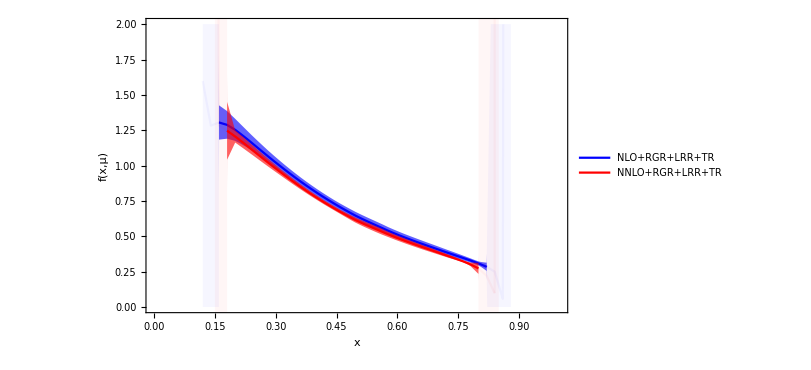

./pics/NLO_NNLO_renormalon_add6_power.pdf

```mathematica
fig=Show[

Plot[{PDFRGRTRintNLOcv[x],PDFRGRTRintNLOcv[x]+PDFRGRTRintNLOerr[x],PDFRGRTRintNLOcv[x]-PDFRGRTRintNLOerr[x]},{x,0.159936,0.820397},PlotStyle->{Blue,Opacity[0,Blue],Opacity[0,Blue]},Filling->{1->{{2},{Opacity[0.618,Blue]}},1->{{3},{Opacity[0.618,Blue]}}},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["NLO+RGR+LRR+TR",20]},{0.55,0.8}]],

Plot[{PDFRGRTRintNLOcv[x],PDFRGRTRintNLOcv[x]+PDFRGRTRintNLOerr[x],PDFRGRTRintNLOcv[x]-PDFRGRTRintNLOerr[x]},x∈ImplicitRegion[0.12≤x≤0.159936||0.820397≤x≤0.88,{x}],PlotStyle->{Opacity[0.618^7,Blue],Opacity[0,Blue],Opacity[0,Blue]},Filling->{1->{{2},{Opacity[0.618^7,Blue]}},1->{{3},{Opacity[0.618^7,Blue]}}},PlotRange->{{0,1},{0,2}}],

Plot[{PDFRGRTRintNNLOcv[x],PDFRGRTRintNNLOcv[x]+PDFRGRTRintNNLOerr[x],PDFRGRTRintNNLOcv[x]-PDFRGRTRintNNLOerr[x]},{x,0.17999957,0.800007},PlotStyle->{Red,Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618,Red]}},1->{{3},{Opacity[0.618,Red]}}},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["NNLO+RGR+LRR+TR",20]},{0.55,0.7}]],

Plot[{PDFRGRTRintNNLOcv[x],PDFRGRTRintNNLOcv[x]+PDFRGRTRintNNLOerr[x],PDFRGRTRintNNLOcv[x]-PDFRGRTRintNNLOerr[x]},x∈ImplicitRegion[0.15≤x≤0.17999957||0.800007≤x≤0.85,{x}],PlotStyle->{Opacity[0.618^7,Red],Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618^7,Red]}},1->{{3},{Opacity[0.618^7,Red]}}}],

PlotRange->{{0,1},{0,2}},
FrameLabel->{Style["x",20],Style["f(x,μ)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]

SetDirectory[NotebookDirectory[]];
Export["./pics/NLO_NNLO_renormalon_add6_power.pdf",fig]
```

InterpolatingFunction::dmval: Input value {0.110015} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

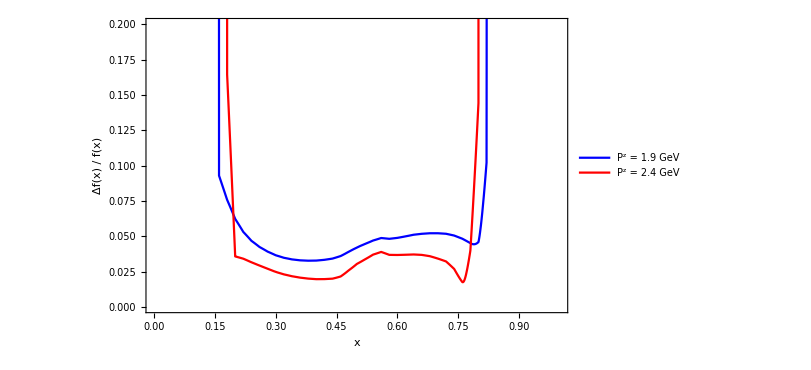

```mathematica
fig=Show[

Plot[Abs[PDFRGRTRintNLOerr[x]/PDFRGRTRintNLOcv[x]],{x,0.11,0.86},PlotStyle->Blue,PlotRange->{{0,1},{0,1}},PlotLegends->Placed[{Style["P^z = 1.9 GeV",20]},{0.5,0.6}]],

Plot[Abs[PDFRGRTRintNNLOerr[x]/PDFRGRTRintNNLOcv[x]],{x,0.09,0.9},PlotStyle->Red,PlotRange->{{0,1},{0,1}},PlotLegends->Placed[{Style["P^z = 2.4 GeV",20]},{0.5,0.5}]],

PlotRange->{{0,1},{0,0.20}},
FrameLabel->{Style["x",20],Style["Δf(x) / f(x)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]
```

#### data, λ_L=25, threshold cut variation

```mathematica
PDFRGRTRls2NLO={{1.5978387725188876,1.2825334089603073,1.3048966846633667,1.2878443910385857,1.2527080598028293,1.2093506511923238,1.1626074460965747,1.1149237181609333,1.06758407527076,1.0212374076888808,0.9761748454440328,0.9322035676310577,0.8897968387239908,0.8492344443511672,0.8104503225663511,0.7733827224130423,0.7379408151028662,0.7040646913745471,0.6716905602794374,0.6407678077420363,0.613979204441269,0.5880056456811931,0.562827499135767,0.5381083684012233,0.5141366811072456,0.49085974127801296,0.468175082318707,0.4462606973806385,0.4253671661045909,0.40534844349319615,0.38686556295407704,0.3693642861941401,0.35208462703853394,0.334724377260079,0.3155871443222478,0.2928201640636893,0.25884934497129986,0.11250845600565038,-50.80065102566561},{1.5977956697705704,1.2824986783296386,1.304866043735052,1.2878165602765645,1.2526823195612309,1.2093265160436624,1.1625845618746597,1.114901820037413,1.0675629436239666,1.0212168708721918,0.9761547641887306,0.9321838294827042,0.8897773614898143,0.8492151727635479,0.810431232482159,0.7733638450717919,0.7379222333315253,0.7040466258515508,0.6716734780151097,0.640752188110795,0.6132938301386525,0.586859990839781,0.5612059301372005,0.5354440598626011,0.5116164212924907,0.4891755958779238,0.46788145670830733,0.4471355098725907,0.42707741192428095,0.4073609018687889,0.3871655525415898,0.36807339644550474,0.34887428066409976,0.3292830037334456,0.3083884348403326,0.28434444430869965,0.24979292831781807,0.057190591933449574,34.27565112893579},{1.5977790864527555,1.2824856592077871,1.3048548129219462,1.2878066532947594,1.2526734857251458,1.2093185882093878,1.1625774192280736,1.1148953729827744,1.0675571195485887,1.0212116137102256,0.9761500286961745,0.9321795781659362,0.8897735633364638,0.8492117993483874,0.8104282544648432,0.7733612290445855,0.7379199316661464,0.7040445693691255,0.6716715589998102,0.6407502254077831,0.6129943419458053,0.5867115621204961,0.560775932529246,0.5365601059152842,0.5132144004921707,0.48964038362378004,0.4677861709813399,0.44650860822580984,0.424897948504332,0.4046069854711521,0.38473903826310996,0.36479759506196696,0.3457486474586239,0.32677696829325664,0.3078414992497217,0.2881076183801656,0.2662233384599209,0.1732293734174579,374.35525765217574}};
```

```mathematica
PDFRGRTRls2NNLO={{15.96749400458798,1.2831400736720857,1.2463905403609723,1.2060328686114066,1.1615818611482513,1.115464321312496,1.0691822274621832,1.0235589529389748,0.9789995362976384,0.9356347376051035,0.8930478422035568,0.8518691510827857,0.8124924233794122,0.7748282850636595,0.7388060863476016,0.704329820939785,0.671342384135467,0.6397821807877018,0.6095980722444202,0.5847791574682385,0.5605182600030514,0.536854618443184,0.5135121930879798,0.490830588591032,0.4687782638263175,0.4472733082316517,0.4264788731477622,0.40657105280717604,0.38748315559106256,0.36955773902114436,0.35229629258725803,0.33474499995337714,0.31600314783448796,0.2927040499075217,0.25479248960747186,0.15925215508343737,2265.6228079518196},{15.967402680232436,1.283069787109002,1.2463292911533377,1.2059777660870914,1.1615314101038645,1.1154175519626615,1.0691384622272933,1.0235176625310698,0.9789603271173133,0.9355973075475328,0.8930119628599447,0.8518346731807471,0.812459264174279,0.774796432618943,0.7387756373015587,0.7043009709858638,0.671315557063897,0.6397581748368845,0.6095778186114941,0.5840327515372026,0.559282757243618,0.5350982276353831,0.5103289567576954,0.48754493819061473,0.4658780090287885,0.44512726707149386,0.42480473186508017,0.4049585080471106,0.38526110109653533,0.3650908292551659,0.34547271953439695,0.3249182763514681,0.30213430986145967,0.2727372875281786,0.22142680417407937,0.09593389296356483,14591.447128564376},{15.96736143201344,1.2830382426325466,1.2463019216784121,1.2059532698027204,1.1615091199767613,1.1153970374330826,1.0691194236384183,1.0234998671883806,0.9789436031359533,0.9355815241231784,0.8929970220316604,0.8518205114353525,0.8124458461409471,0.7747837516873107,0.7387637290719795,0.7042899090161013,0.6713055046016525,0.6397494664956943,0.6095712263303001,0.583553085641422,0.5586902457838522,0.5336638107709585,0.5103615767561704,0.4877602980183688,0.46461071614814103,0.4432895019783708,0.42242013123104105,0.4010536343213133,0.3808320534385216,0.3606936661941825,0.34019650884231073,0.31919885515554874,0.2957522763533905,0.26686683511780374,0.2133503064376721,0.09618297053653448,20695.6246478552}};
```

#### plot, √(σ_h^2+σ_i^2+σ_γ^2)

```mathematica
ClearAll[PDFRGRTRintNLOcv,PDFRGRTRintNLOherr,PDFRGRTRintNLOierr,PDFRGRTRintNNLOcv,PDFRGRTRintNNLOherr,PDFRGRTRintNNLOierr];
xlsfNLO=Table[N[1.0/50 i],{i,6,44}];
(*PDFRGRTRNLOcvls=Mean[Flatten[PDFRGRTRlsNLO,1]];*)
PDFRGRTRNLOcvls=PDFRGRTRlsNLO[[2,2]];
PDFRGRTRintNLOcv=Interpolation[Transpose[{xlsfNLO,PDFRGRTRNLOcvls}],InterpolationOrder->1];

PDFRGRTRNLOhsdls=StandardDeviation[PDFRGRTRlsNLO[[2,;;]]];
PDFRGRTRintNLOherr=Interpolation[Transpose[{xlsfNLO,PDFRGRTRNLOhsdls}],InterpolationOrder->1];

PDFRGRTRNLOisdls=StandardDeviation[PDFRGRTRlsNLO[[;;,2]]];
PDFRGRTRintNLOierr=Interpolation[Transpose[{xlsfNLO,PDFRGRTRNLOisdls}],InterpolationOrder->1];

PDFRGRTRNLOγsdls=StandardDeviation[PDFRGRTRls2NLO];
PDFRGRTRintNLOγerr=Interpolation[Transpose[{xlsfNLO,PDFRGRTRNLOγsdls}],InterpolationOrder->1];

PDFRGRTRintNLOerr[x_]:=√(PDFRGRTRintNLOherr[x]^2+PDFRGRTRintNLOierr[x]^2+PDFRGRTRintNLOγerr[x]^2);



xlsfNNLO=Table[N[1.0/50 i],{i,7,43}];
(*PDFRGRTRNNLOcvls=Mean[Flatten[PDFRGRTRlsNNLO,1]];*)
PDFRGRTRNNLOcvls=PDFRGRTRlsNNLO[[2,2]];
PDFRGRTRintNNLOcv=Interpolation[Transpose[{xlsfNNLO,PDFRGRTRNNLOcvls}],InterpolationOrder->1];

PDFRGRTRNNLOhsdls=StandardDeviation[PDFRGRTRlsNNLO[[2,;;]]];
PDFRGRTRintNNLOherr=Interpolation[Transpose[{xlsfNNLO,PDFRGRTRNNLOhsdls}],InterpolationOrder->1];

PDFRGRTRNNLOisdls=StandardDeviation[PDFRGRTRlsNNLO[[;;,2]]];
PDFRGRTRintNNLOierr=Interpolation[Transpose[{xlsfNNLO,PDFRGRTRNNLOisdls}],InterpolationOrder->1];

PDFRGRTRNNLOγsdls=StandardDeviation[PDFRGRTRls2NNLO];
PDFRGRTRintNNLOγerr=Interpolation[Transpose[{xlsfNNLO,PDFRGRTRNNLOγsdls}],InterpolationOrder->1];

PDFRGRTRintNNLOerr[x_]:=√(PDFRGRTRintNNLOherr[x]^2+PDFRGRTRintNNLOierr[x]^2+PDFRGRTRintNNLOγerr[x]^2);
```

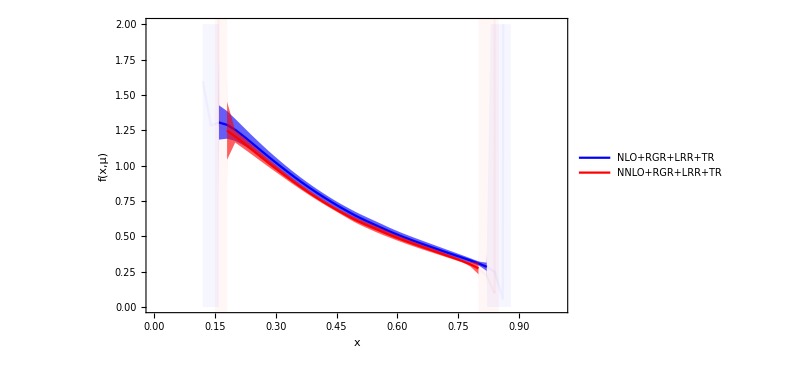

./pics/NLO_NNLO_renormalon_add6_power.pdf

```mathematica
fig=Show[

Plot[{PDFRGRTRintNLOcv[x],PDFRGRTRintNLOcv[x]+PDFRGRTRintNLOerr[x],PDFRGRTRintNLOcv[x]-PDFRGRTRintNLOerr[x]},{x,0.159936,0.820397},PlotStyle->{Blue,Opacity[0,Blue],Opacity[0,Blue]},Filling->{1->{{2},{Opacity[0.618,Blue]}},1->{{3},{Opacity[0.618,Blue]}}},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["NLO+RGR+LRR+TR",20]},{0.55,0.8}]],

Plot[{PDFRGRTRintNLOcv[x],PDFRGRTRintNLOcv[x]+PDFRGRTRintNLOerr[x],PDFRGRTRintNLOcv[x]-PDFRGRTRintNLOerr[x]},x∈ImplicitRegion[0.12≤x≤0.159936||0.820397≤x≤0.88,{x}],PlotStyle->{Opacity[0.618^7,Blue],Opacity[0,Blue],Opacity[0,Blue]},Filling->{1->{{2},{Opacity[0.618^7,Blue]}},1->{{3},{Opacity[0.618^7,Blue]}}},PlotRange->{{0,1},{0,2}}],

Plot[{PDFRGRTRintNNLOcv[x],PDFRGRTRintNNLOcv[x]+PDFRGRTRintNNLOerr[x],PDFRGRTRintNNLOcv[x]-PDFRGRTRintNNLOerr[x]},{x,0.17999957,0.800007},PlotStyle->{Red,Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618,Red]}},1->{{3},{Opacity[0.618,Red]}}},PlotRange->{{0,1},{0,2}},PlotLegends->Placed[{Style["NNLO+RGR+LRR+TR",20]},{0.55,0.7}]],

Plot[{PDFRGRTRintNNLOcv[x],PDFRGRTRintNNLOcv[x]+PDFRGRTRintNNLOerr[x],PDFRGRTRintNNLOcv[x]-PDFRGRTRintNNLOerr[x]},x∈ImplicitRegion[0.15≤x≤0.17999957||0.800007≤x≤0.85,{x}],PlotStyle->{Opacity[0.618^7,Red],Opacity[0,Red],Opacity[0,Red]},Filling->{1->{{2},{Opacity[0.618^7,Red]}},1->{{3},{Opacity[0.618^7,Red]}}}],

PlotRange->{{0,1},{0,2}},
FrameLabel->{Style["x",20],Style["f(x,μ)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]

SetDirectory[NotebookDirectory[]];
Export["./pics/NLO_NNLO_renormalon_add6_power.pdf",fig]
```

InterpolatingFunction::dmval: Input value {0.110015} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

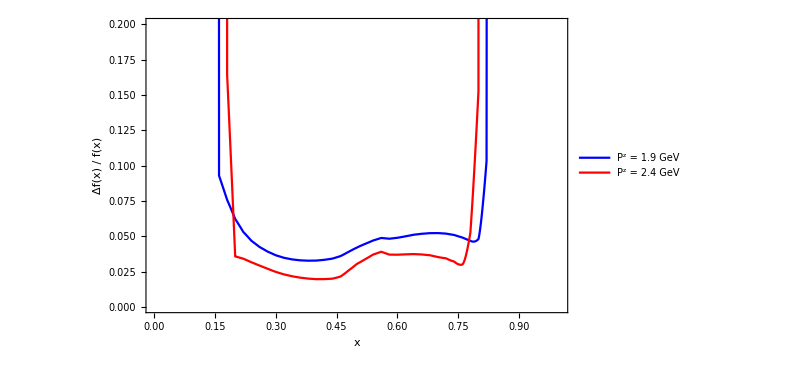

```mathematica
fig=Show[

Plot[Abs[PDFRGRTRintNLOerr[x]/PDFRGRTRintNLOcv[x]],{x,0.11,0.86},PlotStyle->Blue,PlotRange->{{0,1},{0,1}},PlotLegends->Placed[{Style["P^z = 1.9 GeV",20]},{0.5,0.6}]],

Plot[Abs[PDFRGRTRintNNLOerr[x]/PDFRGRTRintNNLOcv[x]],{x,0.09,0.9},PlotStyle->Red,PlotRange->{{0,1},{0,1}},PlotLegends->Placed[{Style["P^z = 2.4 GeV",20]},{0.5,0.5}]],

PlotRange->{{0,1},{0,0.20}},
FrameLabel->{Style["x",20],Style["Δf(x) / f(x)",20]},Frame->True,FrameTicksStyle->20,FrameStyle->Black,LabelStyle->{FontSize->20},
ImageSize->600
]
```